```mathematica
DES1={{14,4,13,1,2,15,11,8,3,10,6,12,5,9,0,7},{0,15,7,4,14,2,13,10,3,6,12,11,9,5,3,8},{4,1,14,8,13,6,2,11,15,12,9,7,3,10,5,0},{15,12,8,2,4,9,1,7,5,11,3,14,10,0,6,13}};
Slice[sbox_,x_,bit_]:=Mod[Floor[sbox[[(Mod[x,2]+Mod[Floor[x/16],2] 2)+1,If[Floor[x/2]≥16,Floor[x/2]-16+1,Floor[x/2]+1]]]/(2^bit)],2];
```

```mathematica
f=y^6+y+1;
len=Exponent[f,y];

FieldInversion[-1]=1
FieldInversion[1]=1
FieldInversion[k_]:=FieldInversion[k]=
Module[{u,v,g1,g2,i,ux,vx},
(
u=PolynomialMod[k,2];
v=f;
g1=1;
g2=0;
i=0;
While[While[Coefficient[u,y,0]==0,
(
u=Simplify[u/y];
If[Coefficient[g1,y,0]==0,g1=g1/y,g1=Simplify[PolynomialMod[(g1+f),{2}]/y]]
)];(u=!=1)&&(i<10),
If[Exponent[u,y]<Exponent[v,y],
ux=v;v=u;u=ux;
ux=g2;g2=g1;g1=ux];
u=PolynomialMod[(u+v),{2}];
g1=PolynomialMod[(g1+g2),{2}];
i++;
];
g1)];

Poly[n_]:=Reverse[IntegerDigits[n,2,6]].Table[y^i,{i,0,6-1}];

Int2Vec[x_]:=Reverse@IntegerDigits[x,2,len];
Int2Poly[x_]:=Int2Vec[x].Table[y^i,{i,0,len-1}];

Pol2Vec[x_]:=Reverse@CoefficientList[x,y,len];
Pol2Int[x_]:=FromDigits[Pol2Vec[x],2];

FP[a_,b_]:=FP[a,b]=Pol2Int[PolynomialMod[Int2Poly[a]Int2Poly[b],{f,2}]];
FA[a_,b_]:=FA[a,b]=Pol2Int[PolynomialMod[Int2Poly[a]+Int2Poly[b],{f,2}]];
FI[a_]:=FI[a]=Pol2Int[FieldInversion[Int2Poly[a]]];

rule1=GF[a_] GF[b_]:>GF[FP[a,b]];
rule2=GF[a_]+ GF[b_]:>GF[FA[a,b]];
rule3=Power[GF[a_],b_/;b>0]:>GF[Nest[FP[#,a]&,a,b-1]];
rule4=Power[GF[a_],-1]:>GF[FI[a]];
rule5=-GF[a_]:>GF[a];
rule6=(a_;IntegerQ[a]) GF[b_]:>GF[Nest[FA[#,b]&,a,a-1]]; (*regola inutile ?!?!*)
rule7=GF[0]->0;
(*
rule8 = 1-> GF[1];
rule9=b_ GF[a_]:> Mod[b,2] GF[a];
*)
rules={rule1,rule2,rule3,rule4,rule5,rule7};

(*Produttoria[k_]:=Partition[Map[(Collect[Expand[#],x]//.rules)&,x(Xp[[k]]-Drop[Xp,{k}])^(-1)-Drop[Xp,{k}] (Xp[[k]]-Drop[Xp,{k}])^(-1) ],2,2,{1,1},1];*)
Produttoria[k_]:=Partition[((x(Xp[[k]]-Drop[Xp,{k}])^(-1))//.rules)+(-Drop[Xp,{k}] (Xp[[k]]-Drop[Xp,{k}])^(-1)//.rules),2,2,{1,1},GF[1]];

f2[c_]:=PolynomialMod[Collect[Expand[c[[1]] c[[2]]],x]//.rules,2];
ApplyStep[p2_]:=If[(Length[p2]>=2),Partition[Map[f2,p2],2],f2[p2[[1]]],p2];


Lagrange[Yp_]:=
Module[{sum,XX,pp,tt,stt},
(sum=0;
XX=Table[
{Produttoria[kk],
Yp[[kk]],
pp=Nest[ApplyStep,Produttoria[kk],Log[2,points]],
tt=Yp[[kk]] pp,
stt=f2[tt],
sum=f2[{sum+ stt,1}]},{kk,1,points}];
TableForm[XX,TableDepth->2];
PolynomialMod[XX[[-1,-1]],{2}]
)]
```

```mathematica
points=64
Xp=Map[GF,Range[points]-1];Length[Xp]

Print[lagrange2=Lagrange[Map[GF,Table[Slice[DES1,i,2],{i,0,63}]]]]
```

64

64

GF[1]+x^7 GF[1]+x^14 GF[1]+x^23 GF[1]+x^28 GF[1]+x^29 GF[1]+x^35 GF[1]+x^43 GF[1]+x^46 GF[1]+x^49 GF[1]+x^53 GF[1]+x^56 GF[1]+x^58 GF[1]+x^44 GF[3]+x^25 GF[5]+x^6 GF[7]+x^22 GF[8]+x^3 GF[10]+x^37 GF[13]+x^27 GF[14]+x^36 GF[15]+x^50 GF[17]+x^11 GF[18]+x^12 GF[21]+x^9 GF[22]+x^54 GF[23]+x^18 GF[24]+x^45 GF[25]+x^33 GF[27]+x^24 GF[29]+x^48 GF[30]+x^62 GF[32]+x^57 GF[33]+x^31 GF[36]+x^60 GF[37]+x^47 GF[38]+x^30 GF[39]+x^2 GF[40]+x^41 GF[40]+x^40 GF[41]+x^10 GF[42]+x^26 GF[43]+x^32 GF[43]+x^15 GF[46]+x^55 GF[47]+x^61 GF[48]+x^51 GF[49]+x^17 GF[50]+x^4 GF[51]+x^19 GF[51]+x GF[54]+x^52 GF[54]+x^20 GF[55]+x^34 GF[56]+x^8 GF[57]+x^38 GF[57]+x^42 GF[58]+x^21 GF[59]+x^59 GF[60]+x^39 GF[61]+x^13 GF[62]+x^16 GF[62]+x^5 GF[63]

```mathematica
vars=Table[ToExpression["x"<>ToString[j]],{j,0,7}];
subs=Map[Rule[x,#]&,vars];
Print@Timing[composed=ExpandAll[Sum[GF[2^j] Lagrange[Map[GF,Table[Slice[DES1,i,Mod[j,4]],{i,0,63}]]]/.subs[[j+1]],{j,0,Length[vars]-1}]]//.rules];
```

{45.7921,x0^21 GF[1]+x0^42 GF[1]+x1^33 GF[1]+x2^51 GF[1]+x3^16 GF[1]+x3^52 GF[1]+x5^20 GF[1]+x2^57 GF[2]+x3^10 GF[2]+x3^37 GF[2]+x4^17 GF[2]+x4^23 GF[2]+x4^32 GF[2]+x4^41 GF[2]+x5^6 GF[2]+x2^7 GF[4]+x2^14 GF[4]+x2^23 GF[4]+x2^28 GF[4]+x2^29 GF[4]+x2^35 GF[4]+x2^43 GF[4]+x2^46 GF[4]+x2^49 GF[4]+x2^53 GF[4]+x2^56 GF[4]+x2^58 GF[4]+x3^5 GF[4]+x3^50 GF[4]+x1^28 GF[5]+x2^61 GF[5]+x0^28 GF[6]+x0^37 GF[6]+x1^44 GF[6]+x1^60 GF[6]+x2^62 GF[6]+x0^24 GF[7]+x1^35 GF[7]+x2^50 GF[7]+x3^33 GF[7]+x5^26 GF[7]+x5^38 GF[7]+x5^41 GF[7]+x5^42 GF[7]+x3^27 GF[8]+x3^45 GF[8]+x3^54 GF[8]+x5^3 GF[8]+x1^48 GF[9]+x2^4 GF[9]+x2^19 GF[9]+x3^6 GF[9]+x4^22 GF[9]+x4^49 GF[9]+x5^36 GF[9]+x0^12 GF[10]+x1^25 GF[10]+x1^57 GF[10]+x3^51 GF[10]+x3^61 GF[10]+x0^14 GF[11]+x0^50 GF[11]+x2^11 GF[11]+x2^44 GF[12]+x3^57 GF[12]+x3^62 GF[12]+x5^22 GF[12]+x5^30 GF[12]+x1^24 GF[13]+x2^17 GF[13]+x3^29 GF[13]+x3^43 GF[13]+x5^17 GF[13]+x0^39 GF[14]+x0^54 GF[14]+x0^60 GF[14]+x1^29 GF[14]+x1^32 GF[14]+x5^56 GF[14]+x3^4 GF[15]+x3^13 GF[15]+x4^11 GF[15]+x4^56 GF[15]+x5^16 GF[15]+x5^46 GF[15]+x1^22 GF[16]+x1^30 GF[16]+x4^21 GF[16]+x4^42 GF[16]+x5^33 GF[16]+x1^34 GF[17]+x3^21 GF[17]+x5^4 GF[17]+x5^43 GF[17]+x2^60 GF[18]+x3^8 GF[18]+x3^26 GF[18]+x5^28 GF[19]+x0^11 GF[20]+x0^56 GF[20]+x1^16 GF[20]+x1^46 GF[20]+x2^25 GF[20]+x0^48 GF[21]+x3^14 GF[21]+x5^24 GF[21]+x2^31 GF[22]+x5^48 GF[22]+x0^15 GF[23]+x0^45 GF[23]+x0^57 GF[23]+x1^40 GF[23]+x2^12 GF[23]+x3 GF[23]+x3^19 GF[23]+x0^27 GF[25]+x0^30 GF[25]+x0^51 GF[25]+x1^49 GF[25]+x2^20 GF[25]+x3^42 GF[25]+x4^33 GF[25]+x0^7 GF[26]+x0^25 GF[26]+x1^37 GF[26]+x1^39 GF[26]+x2^30 GF[26]+x3^3 GF[26]+x4^27 GF[26]+x4^30 GF[26]+x4^51 GF[26]+x5^49 GF[26]+x0^6 GF[27]+x1^14 GF[27]+x2^9 GF[27]+x3^28 GF[27]+x5^11 GF[27]+x5^15 GF[27]+x0^22 GF[28]+x0^49 GF[28]+x1^36 GF[28]+x2^6 GF[28]+x5^34 GF[28]+x0^33 GF[29]+x2 GF[29]+x2^52 GF[29]+x0^3 GF[30]+x2^47 GF[30]+x4^8 GF[30]+x4^20 GF[30]+x4^26 GF[30]+x4^53 GF[30]+x0^35 GF[31]+x0^44 GF[31]+x1^12 GF[31]+x2^54 GF[31]+x3^24 GF[31]+x4^48 GF[31]+x2^22 GF[32]+x1^3 GF[33]+x2^8 GF[33]+x2^38 GF[33]+x3^11 GF[33]+x3^20 GF[33]+x1^50 GF[34]+x1^51 GF[34]+x2^40 GF[34]+x2^18 GF[35]+x4^28 GF[35]+x4^37 GF[35]+x5^44 GF[35]+x5^60 GF[35]+x1^11 GF[36]+x1^15 GF[36]+x3^25 GF[36]+x3^34 GF[36]+x4^16 GF[36]+x4^40 GF[36]+x4^43 GF[36]+x4^52 GF[36]+x5^10 GF[36]+x2^34 GF[37]+x3^35 GF[37]+x4^39 GF[37]+x4^54 GF[37]+x4^60 GF[37]+x5^29 GF[37]+x5^32 GF[37]+x2^2 GF[38]+x2^41 GF[38]+x3^49 GF[38]+x4^12 GF[38]+x5^25 GF[38]+x5^57 GF[38]+x1^5 GF[39]+x2^45 GF[39]+x5^13 GF[39]+x5^19 GF[39]+x5^21 GF[39]+x5^52 GF[39]+x0^8 GF[40]+x0^20 GF[40]+x0^26 GF[40]+x0^53 GF[40]+x2^3 GF[40]+x1^56 GF[41]+x2^21 GF[41]+x3^39 GF[41]+x3^59 GF[41]+x4^3 GF[41]+x1 GF[42]+x1^58 GF[42]+x2^26 GF[42]+x2^32 GF[42]+x4^7 GF[42]+x4^25 GF[42]+x5^37 GF[42]+x5^39 GF[42]+x0^2 GF[43]+x0^5 GF[43]+x0^29 GF[43]+x0^38 GF[43]+x1^7 GF[43]+x5^5 GF[43]+x3^31 GF[44]+x3^60 GF[44]+x1^17 GF[45]+x2^42 GF[45]+GF[46]+x1^9 GF[46]+x2^10 GF[46]+x4^2 GF[46]+x4^5 GF[46]+x4^29 GF[46]+x4^38 GF[46]+x5^7 GF[46]+x2^33 GF[47]+x3^56 GF[48]+x2^39 GF[49]+x3^12 GF[49]+x4 GF[49]+x4^19 GF[49]+x4^34 GF[49]+x4^46 GF[49]+x1^18 GF[50]+x3^48 GF[50]+x5^2 GF[50]+x5^53 GF[50]+x0^16 GF[51]+x0^40 GF[51]+x0^43 GF[51]+x0^52 GF[51]+x1^10 GF[51]+x3^23 GF[51]+x3^58 GF[51]+x4^24 GF[51]+x5^35 GF[51]+x2^37 GF[52]+x3^17 GF[52]+x3^44 GF[52]+x5^18 GF[52]+x1^26 GF[53]+x1^38 GF[53]+x1^41 GF[53]+x1^42 GF[53]+x2^59 GF[53]+x0^4 GF[54]+x0^10 GF[54]+x0^13 GF[54]+x0^58 GF[54]+x1^8 GF[54]+x1^23 GF[54]+x4^14 GF[54]+x4^50 GF[54]+x1^13 GF[55]+x1^19 GF[55]+x1^21 GF[55]+x1^52 GF[55]+x2^24 GF[55]+x3^15 GF[55]+x3^55 GF[55]+x4^4 GF[55]+x4^10 GF[55]+x4^13 GF[55]+x4^58 GF[55]+x5^8 GF[55]+x5^23 GF[55]+x2^27 GF[56]+x5^50 GF[56]+x5^51 GF[56]+x0^17 GF[57]+x0^23 GF[57]+x0^32 GF[57]+x0^41 GF[57]+x1^6 GF[57]+x2^5 GF[57]+x3^32 GF[57]+x3^41 GF[57]+x4^35 GF[57]+x4^44 GF[57]+x5^12 GF[57]+x1^2 GF[58]+x1^53 GF[58]+x2^55 GF[58]+x3^2 GF[58]+x3^38 GF[58]+x4^6 GF[58]+x5^14 GF[58]+x2^48 GF[59]+x1^4 GF[60]+x1^43 GF[60]+x2^36 GF[60]+x3^30 GF[60]+x3^47 GF[60]+x1^20 GF[61]+x2^13 GF[61]+x2^16 GF[61]+x3^7 GF[61]+x5^9 GF[61]+x0 GF[62]+x0^19 GF[62]+x0^34 GF[62]+x0^46 GF[62]+x2^15 GF[62]+x3^46 GF[62]+x3^53 GF[62]+x5 GF[62]+x5^58 GF[62]+x3^22 GF[63]+x3^40 GF[63]+x4^15 GF[63]+x4^45 GF[63]+x4^57 GF[63]+x5^40 GF[63]}

```mathematica
G[lagrange25_,composed_]:=f2[{lagrange25/.Join@@Table[{x^(2 i)->Map[#^(2 i)&,composed],x^(2 i+1)->(composed Map[#^(2 i)&,composed])},{i,1,Floor[Exponent[lagrange25,x]/2]}],1}];


maxdegree=1;
timing={}; polynomials={};
    Print[composed];
While[maxdegree≤4,
(
Print[lagrange25=Select[lagrange2,Exponent[#,x]≤maxdegree&]];
	t=Timing[G[lagrange25,composed]];

timing=Append[timing,{maxdegree,t[[1]]}];
     polynomials=Append[polynomials,{maxdegree,t[[2]]}];
maxdegree= 2 maxdegree;
)]
```

x0^21 GF[1]+x0^42 GF[1]+x1^33 GF[1]+x2^51 GF[1]+x3^16 GF[1]+x3^52 GF[1]+x5^20 GF[1]+x2^57 GF[2]+x3^10 GF[2]+x3^37 GF[2]+x4^17 GF[2]+x4^23 GF[2]+x4^32 GF[2]+x4^41 GF[2]+x5^6 GF[2]+x2^7 GF[4]+x2^14 GF[4]+x2^23 GF[4]+x2^28 GF[4]+x2^29 GF[4]+x2^35 GF[4]+x2^43 GF[4]+x2^46 GF[4]+x2^49 GF[4]+x2^53 GF[4]+x2^56 GF[4]+x2^58 GF[4]+x3^5 GF[4]+x3^50 GF[4]+x1^28 GF[5]+x2^61 GF[5]+x0^28 GF[6]+x0^37 GF[6]+x1^44 GF[6]+x1^60 GF[6]+x2^62 GF[6]+x0^24 GF[7]+x1^35 GF[7]+x2^50 GF[7]+x3^33 GF[7]+x5^26 GF[7]+x5^38 GF[7]+x5^41 GF[7]+x5^42 GF[7]+x3^27 GF[8]+x3^45 GF[8]+x3^54 GF[8]+x5^3 GF[8]+x1^48 GF[9]+x2^4 GF[9]+x2^19 GF[9]+x3^6 GF[9]+x4^22 GF[9]+x4^49 GF[9]+x5^36 GF[9]+x0^12 GF[10]+x1^25 GF[10]+x1^57 GF[10]+x3^51 GF[10]+x3^61 GF[10]+x0^14 GF[11]+x0^50 GF[11]+x2^11 GF[11]+x2^44 GF[12]+x3^57 GF[12]+x3^62 GF[12]+x5^22 GF[12]+x5^30 GF[12]+x1^24 GF[13]+x2^17 GF[13]+x3^29 GF[13]+x3^43 GF[13]+x5^17 GF[13]+x0^39 GF[14]+x0^54 GF[14]+x0^60 GF[14]+x1^29 GF[14]+x1^32 GF[14]+x5^56 GF[14]+x3^4 GF[15]+x3^13 GF[15]+x4^11 GF[15]+x4^56 GF[15]+x5^16 GF[15]+x5^46 GF[15]+x1^22 GF[16]+x1^30 GF[16]+x4^21 GF[16]+x4^42 GF[16]+x5^33 GF[16]+x1^34 GF[17]+x3^21 GF[17]+x5^4 GF[17]+x5^43 GF[17]+x2^60 GF[18]+x3^8 GF[18]+x3^26 GF[18]+x5^28 GF[19]+x0^11 GF[20]+x0^56 GF[20]+x1^16 GF[20]+x1^46 GF[20]+x2^25 GF[20]+x0^48 GF[21]+x3^14 GF[21]+x5^24 GF[21]+x2^31 GF[22]+x5^48 GF[22]+x0^15 GF[23]+x0^45 GF[23]+x0^57 GF[23]+x1^40 GF[23]+x2^12 GF[23]+x3 GF[23]+x3^19 GF[23]+x0^27 GF[25]+x0^30 GF[25]+x0^51 GF[25]+x1^49 GF[25]+x2^20 GF[25]+x3^42 GF[25]+x4^33 GF[25]+x0^7 GF[26]+x0^25 GF[26]+x1^37 GF[26]+x1^39 GF[26]+x2^30 GF[26]+x3^3 GF[26]+x4^27 GF[26]+x4^30 GF[26]+x4^51 GF[26]+x5^49 GF[26]+x0^6 GF[27]+x1^14 GF[27]+x2^9 GF[27]+x3^28 GF[27]+x5^11 GF[27]+x5^15 GF[27]+x0^22 GF[28]+x0^49 GF[28]+x1^36 GF[28]+x2^6 GF[28]+x5^34 GF[28]+x0^33 GF[29]+x2 GF[29]+x2^52 GF[29]+x0^3 GF[30]+x2^47 GF[30]+x4^8 GF[30]+x4^20 GF[30]+x4^26 GF[30]+x4^53 GF[30]+x0^35 GF[31]+x0^44 GF[31]+x1^12 GF[31]+x2^54 GF[31]+x3^24 GF[31]+x4^48 GF[31]+x2^22 GF[32]+x1^3 GF[33]+x2^8 GF[33]+x2^38 GF[33]+x3^11 GF[33]+x3^20 GF[33]+x1^50 GF[34]+x1^51 GF[34]+x2^40 GF[34]+x2^18 GF[35]+x4^28 GF[35]+x4^37 GF[35]+x5^44 GF[35]+x5^60 GF[35]+x1^11 GF[36]+x1^15 GF[36]+x3^25 GF[36]+x3^34 GF[36]+x4^16 GF[36]+x4^40 GF[36]+x4^43 GF[36]+x4^52 GF[36]+x5^10 GF[36]+x2^34 GF[37]+x3^35 GF[37]+x4^39 GF[37]+x4^54 GF[37]+x4^60 GF[37]+x5^29 GF[37]+x5^32 GF[37]+x2^2 GF[38]+x2^41 GF[38]+x3^49 GF[38]+x4^12 GF[38]+x5^25 GF[38]+x5^57 GF[38]+x1^5 GF[39]+x2^45 GF[39]+x5^13 GF[39]+x5^19 GF[39]+x5^21 GF[39]+x5^52 GF[39]+x0^8 GF[40]+x0^20 GF[40]+x0^26 GF[40]+x0^53 GF[40]+x2^3 GF[40]+x1^56 GF[41]+x2^21 GF[41]+x3^39 GF[41]+x3^59 GF[41]+x4^3 GF[41]+x1 GF[42]+x1^58 GF[42]+x2^26 GF[42]+x2^32 GF[42]+x4^7 GF[42]+x4^25 GF[42]+x5^37 GF[42]+x5^39 GF[42]+x0^2 GF[43]+x0^5 GF[43]+x0^29 GF[43]+x0^38 GF[43]+x1^7 GF[43]+x5^5 GF[43]+x3^31 GF[44]+x3^60 GF[44]+x1^17 GF[45]+x2^42 GF[45]+GF[46]+x1^9 GF[46]+x2^10 GF[46]+x4^2 GF[46]+x4^5 GF[46]+x4^29 GF[46]+x4^38 GF[46]+x5^7 GF[46]+x2^33 GF[47]+x3^56 GF[48]+x2^39 GF[49]+x3^12 GF[49]+x4 GF[49]+x4^19 GF[49]+x4^34 GF[49]+x4^46 GF[49]+x1^18 GF[50]+x3^48 GF[50]+x5^2 GF[50]+x5^53 GF[50]+x0^16 GF[51]+x0^40 GF[51]+x0^43 GF[51]+x0^52 GF[51]+x1^10 GF[51]+x3^23 GF[51]+x3^58 GF[51]+x4^24 GF[51]+x5^35 GF[51]+x2^37 GF[52]+x3^17 GF[52]+x3^44 GF[52]+x5^18 GF[52]+x1^26 GF[53]+x1^38 GF[53]+x1^41 GF[53]+x1^42 GF[53]+x2^59 GF[53]+x0^4 GF[54]+x0^10 GF[54]+x0^13 GF[54]+x0^58 GF[54]+x1^8 GF[54]+x1^23 GF[54]+x4^14 GF[54]+x4^50 GF[54]+x1^13 GF[55]+x1^19 GF[55]+x1^21 GF[55]+x1^52 GF[55]+x2^24 GF[55]+x3^15 GF[55]+x3^55 GF[55]+x4^4 GF[55]+x4^10 GF[55]+x4^13 GF[55]+x4^58 GF[55]+x5^8 GF[55]+x5^23 GF[55]+x2^27 GF[56]+x5^50 GF[56]+x5^51 GF[56]+x0^17 GF[57]+x0^23 GF[57]+x0^32 GF[57]+x0^41 GF[57]+x1^6 GF[57]+x2^5 GF[57]+x3^32 GF[57]+x3^41 GF[57]+x4^35 GF[57]+x4^44 GF[57]+x5^12 GF[57]+x1^2 GF[58]+x1^53 GF[58]+x2^55 GF[58]+x3^2 GF[58]+x3^38 GF[58]+x4^6 GF[58]+x5^14 GF[58]+x2^48 GF[59]+x1^4 GF[60]+x1^43 GF[60]+x2^36 GF[60]+x3^30 GF[60]+x3^47 GF[60]+x1^20 GF[61]+x2^13 GF[61]+x2^16 GF[61]+x3^7 GF[61]+x5^9 GF[61]+x0 GF[62]+x0^19 GF[62]+x0^34 GF[62]+x0^46 GF[62]+x2^15 GF[62]+x3^46 GF[62]+x3^53 GF[62]+x5 GF[62]+x5^58 GF[62]+x3^22 GF[63]+x3^40 GF[63]+x4^15 GF[63]+x4^45 GF[63]+x4^57 GF[63]+x5^40 GF[63]

GF[1]+x GF[54]

GF[1]+x^2 GF[40]+x GF[54]

GF[1]+x^3 GF[10]+x^2 GF[40]+x^4 GF[51]+x GF[54]

```mathematica
timing
```

{{1,0.000104},{2,0.158776},{4,14806.2}}

```mathematica
Map [Length[#[[2]]]&,polynomials]
```

{2,335,100653}

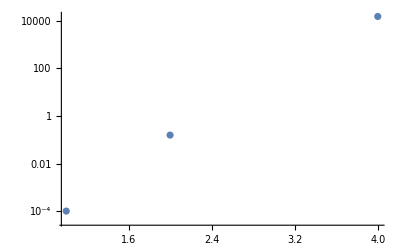

64

64

$Aborted

{x0,x1,x2,x3,x4,x5,x6,x7}

{x→x0,x→x1,x→x2,x→x3,x→x4,x→x5,x→x6,x→x7}

x0^21 GF[1]+x0^42 GF[1]+x1^33 GF[1]+x2^51 GF[1]+x3^16 GF[1]+x3^52 GF[1]+x5^20 GF[1]+x2^57 GF[2]+x3^10 GF[2]+x3^37 GF[2]+x4^17 GF[2]+x4^23 GF[2]+x4^32 GF[2]+x4^41 GF[2]+x5^6 GF[2]+x2^7 GF[4]+x2^14 GF[4]+x2^23 GF[4]+x2^28 GF[4]+x2^29 GF[4]+x2^35 GF[4]+x2^43 GF[4]+x2^46 GF[4]+x2^49 GF[4]+x2^53 GF[4]+x2^56 GF[4]+x2^58 GF[4]+x3^5 GF[4]+x3^50 GF[4]+x1^28 GF[5]+x2^61 GF[5]+x0^28 GF[6]+x0^37 GF[6]+x1^44 GF[6]+x1^60 GF[6]+x2^62 GF[6]+x0^24 GF[7]+x1^35 GF[7]+x2^50 GF[7]+x3^33 GF[7]+x5^26 GF[7]+x5^38 GF[7]+x5^41 GF[7]+x5^42 GF[7]+x3^27 GF[8]+x3^45 GF[8]+x3^54 GF[8]+x5^3 GF[8]+x1^48 GF[9]+x2^4 GF[9]+x2^19 GF[9]+x3^6 GF[9]+x4^22 GF[9]+x4^49 GF[9]+x5^36 GF[9]+x0^12 GF[10]+x1^25 GF[10]+x1^57 GF[10]+x3^51 GF[10]+x3^61 GF[10]+x0^14 GF[11]+x0^50 GF[11]+x2^11 GF[11]+x2^44 GF[12]+x3^57 GF[12]+x3^62 GF[12]+x5^22 GF[12]+x5^30 GF[12]+x1^24 GF[13]+x2^17 GF[13]+x3^29 GF[13]+x3^43 GF[13]+x5^17 GF[13]+x0^39 GF[14]+x0^54 GF[14]+x0^60 GF[14]+x1^29 GF[14]+x1^32 GF[14]+x5^56 GF[14]+x3^4 GF[15]+x3^13 GF[15]+x4^11 GF[15]+x4^56 GF[15]+x5^16 GF[15]+x5^46 GF[15]+x1^22 GF[16]+x1^30 GF[16]+x4^21 GF[16]+x4^42 GF[16]+x5^33 GF[16]+x1^34 GF[17]+x3^21 GF[17]+x5^4 GF[17]+x5^43 GF[17]+x2^60 GF[18]+x3^8 GF[18]+x3^26 GF[18]+x5^28 GF[19]+x0^11 GF[20]+x0^56 GF[20]+x1^16 GF[20]+x1^46 GF[20]+x2^25 GF[20]+x0^48 GF[21]+x3^14 GF[21]+x5^24 GF[21]+x2^31 GF[22]+x5^48 GF[22]+x0^15 GF[23]+x0^45 GF[23]+x0^57 GF[23]+x1^40 GF[23]+x2^12 GF[23]+x3 GF[23]+x3^19 GF[23]+x0^27 GF[25]+x0^30 GF[25]+x0^51 GF[25]+x1^49 GF[25]+x2^20 GF[25]+x3^42 GF[25]+x4^33 GF[25]+x0^7 GF[26]+x0^25 GF[26]+x1^37 GF[26]+x1^39 GF[26]+x2^30 GF[26]+x3^3 GF[26]+x4^27 GF[26]+x4^30 GF[26]+x4^51 GF[26]+x5^49 GF[26]+x0^6 GF[27]+x1^14 GF[27]+x2^9 GF[27]+x3^28 GF[27]+x5^11 GF[27]+x5^15 GF[27]+x0^22 GF[28]+x0^49 GF[28]+x1^36 GF[28]+x2^6 GF[28]+x5^34 GF[28]+x0^33 GF[29]+x2 GF[29]+x2^52 GF[29]+x0^3 GF[30]+x2^47 GF[30]+x4^8 GF[30]+x4^20 GF[30]+x4^26 GF[30]+x4^53 GF[30]+x0^35 GF[31]+x0^44 GF[31]+x1^12 GF[31]+x2^54 GF[31]+x3^24 GF[31]+x4^48 GF[31]+x2^22 GF[32]+x1^3 GF[33]+x2^8 GF[33]+x2^38 GF[33]+x3^11 GF[33]+x3^20 GF[33]+x1^50 GF[34]+x1^51 GF[34]+x2^40 GF[34]+x2^18 GF[35]+x4^28 GF[35]+x4^37 GF[35]+x5^44 GF[35]+x5^60 GF[35]+x1^11 GF[36]+x1^15 GF[36]+x3^25 GF[36]+x3^34 GF[36]+x4^16 GF[36]+x4^40 GF[36]+x4^43 GF[36]+x4^52 GF[36]+x5^10 GF[36]+x2^34 GF[37]+x3^35 GF[37]+x4^39 GF[37]+x4^54 GF[37]+x4^60 GF[37]+x5^29 GF[37]+x5^32 GF[37]+x2^2 GF[38]+x2^41 GF[38]+x3^49 GF[38]+x4^12 GF[38]+x5^25 GF[38]+x5^57 GF[38]+x1^5 GF[39]+x2^45 GF[39]+x5^13 GF[39]+x5^19 GF[39]+x5^21 GF[39]+x5^52 GF[39]+x0^8 GF[40]+x0^20 GF[40]+x0^26 GF[40]+x0^53 GF[40]+x2^3 GF[40]+x1^56 GF[41]+x2^21 GF[41]+x3^39 GF[41]+x3^59 GF[41]+x4^3 GF[41]+x1 GF[42]+x1^58 GF[42]+x2^26 GF[42]+x2^32 GF[42]+x4^7 GF[42]+x4^25 GF[42]+x5^37 GF[42]+x5^39 GF[42]+x0^2 GF[43]+x0^5 GF[43]+x0^29 GF[43]+x0^38 GF[43]+x1^7 GF[43]+x5^5 GF[43]+x3^31 GF[44]+x3^60 GF[44]+x1^17 GF[45]+x2^42 GF[45]+GF[46]+x1^9 GF[46]+x2^10 GF[46]+x4^2 GF[46]+x4^5 GF[46]+x4^29 GF[46]+x4^38 GF[46]+x5^7 GF[46]+x2^33 GF[47]+x3^56 GF[48]+x2^39 GF[49]+x3^12 GF[49]+x4 GF[49]+x4^19 GF[49]+x4^34 GF[49]+x4^46 GF[49]+x1^18 GF[50]+x3^48 GF[50]+x5^2 GF[50]+x5^53 GF[50]+x0^16 GF[51]+x0^40 GF[51]+x0^43 GF[51]+x0^52 GF[51]+x1^10 GF[51]+x3^23 GF[51]+x3^58 GF[51]+x4^24 GF[51]+x5^35 GF[51]+x2^37 GF[52]+x3^17 GF[52]+x3^44 GF[52]+x5^18 GF[52]+x1^26 GF[53]+x1^38 GF[53]+x1^41 GF[53]+x1^42 GF[53]+x2^59 GF[53]+x0^4 GF[54]+x0^10 GF[54]+x0^13 GF[54]+x0^58 GF[54]+x1^8 GF[54]+x1^23 GF[54]+x4^14 GF[54]+x4^50 GF[54]+x1^13 GF[55]+x1^19 GF[55]+x1^21 GF[55]+x1^52 GF[55]+x2^24 GF[55]+x3^15 GF[55]+x3^55 GF[55]+x4^4 GF[55]+x4^10 GF[55]+x4^13 GF[55]+x4^58 GF[55]+x5^8 GF[55]+x5^23 GF[55]+x2^27 GF[56]+x5^50 GF[56]+x5^51 GF[56]+x0^17 GF[57]+x0^23 GF[57]+x0^32 GF[57]+x0^41 GF[57]+x1^6 GF[57]+x2^5 GF[57]+x3^32 GF[57]+x3^41 GF[57]+x4^35 GF[57]+x4^44 GF[57]+x5^12 GF[57]+x1^2 GF[58]+x1^53 GF[58]+x2^55 GF[58]+x3^2 GF[58]+x3^38 GF[58]+x4^6 GF[58]+x5^14 GF[58]+x2^48 GF[59]+x1^4 GF[60]+x1^43 GF[60]+x2^36 GF[60]+x3^30 GF[60]+x3^47 GF[60]+x1^20 GF[61]+x2^13 GF[61]+x2^16 GF[61]+x3^7 GF[61]+x5^9 GF[61]+x0 GF[62]+x0^19 GF[62]+x0^34 GF[62]+x0^46 GF[62]+x2^15 GF[62]+x3^46 GF[62]+x3^53 GF[62]+x5 GF[62]+x5^58 GF[62]+x3^22 GF[63]+x3^40 GF[63]+x4^15 GF[63]+x4^45 GF[63]+x4^57 GF[63]+x5^40 GF[63]

4

GF[1]+x^3 GF[10]+x^2 GF[40]+x^4 GF[51]+x GF[54]

x0^21 GF[1]+x0^42 GF[1]+x1^33 GF[1]+x2^51 GF[1]+x3^16 GF[1]+x3^52 GF[1]+x5^20 GF[1]+x2^57 GF[2]+x3^10 GF[2]+x3^37 GF[2]+x4^17 GF[2]+x4^23 GF[2]+x4^32 GF[2]+x4^41 GF[2]+x5^6 GF[2]+x2^7 GF[4]+x2^14 GF[4]+x2^23 GF[4]+x2^28 GF[4]+x2^29 GF[4]+x2^35 GF[4]+x2^43 GF[4]+x2^46 GF[4]+x2^49 GF[4]+x2^53 GF[4]+x2^56 GF[4]+x2^58 GF[4]+x3^5 GF[4]+x3^50 GF[4]+x1^28 GF[5]+x2^61 GF[5]+x0^28 GF[6]+x0^37 GF[6]+x1^44 GF[6]+x1^60 GF[6]+x2^62 GF[6]+x0^24 GF[7]+x1^35 GF[7]+x2^50 GF[7]+x3^33 GF[7]+x5^26 GF[7]+x5^38 GF[7]+x5^41 GF[7]+x5^42 GF[7]+x3^27 GF[8]+x3^45 GF[8]+x3^54 GF[8]+x5^3 GF[8]+x1^48 GF[9]+x2^4 GF[9]+x2^19 GF[9]+x3^6 GF[9]+x4^22 GF[9]+x4^49 GF[9]+x5^36 GF[9]+x0^12 GF[10]+x1^25 GF[10]+x1^57 GF[10]+x3^51 GF[10]+x3^61 GF[10]+x0^14 GF[11]+x0^50 GF[11]+x2^11 GF[11]+x2^44 GF[12]+x3^57 GF[12]+x3^62 GF[12]+x5^22 GF[12]+x5^30 GF[12]+x1^24 GF[13]+x2^17 GF[13]+x3^29 GF[13]+x3^43 GF[13]+x5^17 GF[13]+x0^39 GF[14]+x0^54 GF[14]+x0^60 GF[14]+x1^29 GF[14]+x1^32 GF[14]+x5^56 GF[14]+x3^4 GF[15]+x3^13 GF[15]+x4^11 GF[15]+x4^56 GF[15]+x5^16 GF[15]+x5^46 GF[15]+x1^22 GF[16]+x1^30 GF[16]+x4^21 GF[16]+x4^42 GF[16]+x5^33 GF[16]+x1^34 GF[17]+x3^21 GF[17]+x5^4 GF[17]+x5^43 GF[17]+x2^60 GF[18]+x3^8 GF[18]+x3^26 GF[18]+x5^28 GF[19]+x0^11 GF[20]+x0^56 GF[20]+x1^16 GF[20]+x1^46 GF[20]+x2^25 GF[20]+x0^48 GF[21]+x3^14 GF[21]+x5^24 GF[21]+x2^31 GF[22]+x5^48 GF[22]+x0^15 GF[23]+x0^45 GF[23]+x0^57 GF[23]+x1^40 GF[23]+x2^12 GF[23]+x3 GF[23]+x3^19 GF[23]+x0^27 GF[25]+x0^30 GF[25]+x0^51 GF[25]+x1^49 GF[25]+x2^20 GF[25]+x3^42 GF[25]+x4^33 GF[25]+x0^7 GF[26]+x0^25 GF[26]+x1^37 GF[26]+x1^39 GF[26]+x2^30 GF[26]+x3^3 GF[26]+x4^27 GF[26]+x4^30 GF[26]+x4^51 GF[26]+x5^49 GF[26]+x0^6 GF[27]+x1^14 GF[27]+x2^9 GF[27]+x3^28 GF[27]+x5^11 GF[27]+x5^15 GF[27]+x0^22 GF[28]+x0^49 GF[28]+x1^36 GF[28]+x2^6 GF[28]+x5^34 GF[28]+x0^33 GF[29]+x2 GF[29]+x2^52 GF[29]+x0^3 GF[30]+x2^47 GF[30]+x4^8 GF[30]+x4^20 GF[30]+x4^26 GF[30]+x4^53 GF[30]+x0^35 GF[31]+x0^44 GF[31]+x1^12 GF[31]+x2^54 GF[31]+x3^24 GF[31]+x4^48 GF[31]+x2^22 GF[32]+x1^3 GF[33]+x2^8 GF[33]+x2^38 GF[33]+x3^11 GF[33]+x3^20 GF[33]+x1^50 GF[34]+x1^51 GF[34]+x2^40 GF[34]+x2^18 GF[35]+x4^28 GF[35]+x4^37 GF[35]+x5^44 GF[35]+x5^60 GF[35]+x1^11 GF[36]+x1^15 GF[36]+x3^25 GF[36]+x3^34 GF[36]+x4^16 GF[36]+x4^40 GF[36]+x4^43 GF[36]+x4^52 GF[36]+x5^10 GF[36]+x2^34 GF[37]+x3^35 GF[37]+x4^39 GF[37]+x4^54 GF[37]+x4^60 GF[37]+x5^29 GF[37]+x5^32 GF[37]+x2^2 GF[38]+x2^41 GF[38]+x3^49 GF[38]+x4^12 GF[38]+x5^25 GF[38]+x5^57 GF[38]+x1^5 GF[39]+x2^45 GF[39]+x5^13 GF[39]+x5^19 GF[39]+x5^21 GF[39]+x5^52 GF[39]+x0^8 GF[40]+x0^20 GF[40]+x0^26 GF[40]+x0^53 GF[40]+x2^3 GF[40]+x1^56 GF[41]+x2^21 GF[41]+x3^39 GF[41]+x3^59 GF[41]+x4^3 GF[41]+x1 GF[42]+x1^58 GF[42]+x2^26 GF[42]+x2^32 GF[42]+x4^7 GF[42]+x4^25 GF[42]+x5^37 GF[42]+x5^39 GF[42]+x0^2 GF[43]+x0^5 GF[43]+x0^29 GF[43]+x0^38 GF[43]+x1^7 GF[43]+x5^5 GF[43]+x3^31 GF[44]+x3^60 GF[44]+x1^17 GF[45]+x2^42 GF[45]+GF[46]+x1^9 GF[46]+x2^10 GF[46]+x4^2 GF[46]+x4^5 GF[46]+x4^29 GF[46]+x4^38 GF[46]+x5^7 GF[46]+x2^33 GF[47]+x3^56 GF[48]+x2^39 GF[49]+x3^12 GF[49]+x4 GF[49]+x4^19 GF[49]+x4^34 GF[49]+x4^46 GF[49]+x1^18 GF[50]+x3^48 GF[50]+x5^2 GF[50]+x5^53 GF[50]+x0^16 GF[51]+x0^40 GF[51]+x0^43 GF[51]+x0^52 GF[51]+x1^10 GF[51]+x3^23 GF[51]+x3^58 GF[51]+x4^24 GF[51]+x5^35 GF[51]+x2^37 GF[52]+x3^17 GF[52]+x3^44 GF[52]+x5^18 GF[52]+x1^26 GF[53]+x1^38 GF[53]+x1^41 GF[53]+x1^42 GF[53]+x2^59 GF[53]+x0^4 GF[54]+x0^10 GF[54]+x0^13 GF[54]+x0^58 GF[54]+x1^8 GF[54]+x1^23 GF[54]+x4^14 GF[54]+x4^50 GF[54]+x1^13 GF[55]+x1^19 GF[55]+x1^21 GF[55]+x1^52 GF[55]+x2^24 GF[55]+x3^15 GF[55]+x3^55 GF[55]+x4^4 GF[55]+x4^10 GF[55]+x4^13 GF[55]+x4^58 GF[55]+x5^8 GF[55]+x5^23 GF[55]+x2^27 GF[56]+x5^50 GF[56]+x5^51 GF[56]+x0^17 GF[57]+x0^23 GF[57]+x0^32 GF[57]+x0^41 GF[57]+x1^6 GF[57]+x2^5 GF[57]+x3^32 GF[57]+x3^41 GF[57]+x4^35 GF[57]+x4^44 GF[57]+x5^12 GF[57]+x1^2 GF[58]+x1^53 GF[58]+x2^55 GF[58]+x3^2 GF[58]+x3^38 GF[58]+x4^6 GF[58]+x5^14 GF[58]+x2^48 GF[59]+x1^4 GF[60]+x1^43 GF[60]+x2^36 GF[60]+x3^30 GF[60]+x3^47 GF[60]+x1^20 GF[61]+x2^13 GF[61]+x2^16 GF[61]+x3^7 GF[61]+x5^9 GF[61]+x0 GF[62]+x0^19 GF[62]+x0^34 GF[62]+x0^46 GF[62]+x2^15 GF[62]+x3^46 GF[62]+x3^53 GF[62]+x5 GF[62]+x5^58 GF[62]+x3^22 GF[63]+x3^40 GF[63]+x4^15 GF[63]+x4^45 GF[63]+x4^57 GF[63]+x5^40 GF[63]

```mathematica
ListLogPlot[timing]
```

```mathematica
3 GF[5]//.rules
```

```mathematica
PolynomialMod[3 GF[5],{2}]
```

GF[5]

```mathematica
points=64
Xp=Map[GF,Range[points]-1];Length[Xp]
Yp=Map[GF,Table[RandomInteger[1],{points}]]
Length[Yp]
```

64

64

{GF[1],GF[0],GF[1],GF[1],GF[0],GF[0],GF[1],GF[0],GF[0],GF[0],GF[0],GF[1],GF[1],GF[0],GF[1],GF[1],GF[1],GF[1],GF[0],GF[1],GF[1],GF[0],GF[0],GF[1],GF[0],GF[1],GF[1],GF[0],GF[1],GF[1],GF[1],GF[0],GF[1],GF[0],GF[1],GF[1],GF[0],GF[1],GF[0],GF[1],GF[1],GF[0],GF[0],GF[0],GF[1],GF[1],GF[0],GF[1],GF[0],GF[0],GF[0],GF[0],GF[1],GF[1],GF[1],GF[1],GF[0],GF[0],GF[0],GF[1],GF[1],GF[1],GF[1],GF[0]}

64

```mathematica
Yp=Map[GF,Table[Slice[DES1,i,0],{i,0,63}]]
sum=0;
XX=Table[
{Produttoria[kk],
Yp[[kk]],
pp=Nest[ApplyStep,Produttoria[kk],Log[2,points]],
tt=Yp[[kk]] pp,
stt=f2[tt],
sum=f2[{sum+ stt,1}]},{kk,1,points}];
TableForm[XX,TableDepth->2]
lagrange0=PolynomialMod[XX[[-1,-1]],{2}]
```

{GF[0],GF[0],GF[0],GF[1],GF[1],GF[1],GF[1],GF[0],GF[0],GF[0],GF[1],GF[0],GF[1],GF[1],GF[0],GF[0],GF[1],GF[1],GF[0],GF[1],GF[1],GF[1],GF[1],GF[0],GF[1],GF[0],GF[0],GF[0],GF[1],GF[0],GF[0],GF[1],GF[0],GF[0],GF[0],GF[1],GF[1],GF[1],GF[1],GF[0],GF[0],GF[0],GF[1],GF[0],GF[1],GF[1],GF[0],GF[0],GF[1],GF[1],GF[0],GF[1],GF[1],GF[1],GF[1],GF[0],GF[1],GF[0],GF[0],GF[0],GF[1],GF[0],GF[0],GF[1]}

1
 |  |  |  |

x^21 GF[1]+x^42 GF[1]+x^28 GF[6]+x^37 GF[6]+x^24 GF[7]+x^12 GF[10]+x^14 GF[11]+x^50 GF[11]+x^39 GF[14]+x^54 GF[14]+x^60 GF[14]+x^11 GF[20]+x^56 GF[20]+x^48 GF[21]+x^15 GF[23]+x^45 GF[23]+x^57 GF[23]+x^27 GF[25]+x^30 GF[25]+x^51 GF[25]+x^7 GF[26]+x^25 GF[26]+x^6 GF[27]+x^22 GF[28]+x^49 GF[28]+x^33 GF[29]+x^3 GF[30]+x^35 GF[31]+x^44 GF[31]+x^8 GF[40]+x^20 GF[40]+x^26 GF[40]+x^53 GF[40]+x^2 GF[43]+x^5 GF[43]+x^29 GF[43]+x^38 GF[43]+x^16 GF[51]+x^40 GF[51]+x^43 GF[51]+x^52 GF[51]+x^4 GF[54]+x^10 GF[54]+x^13 GF[54]+x^58 GF[54]+x^17 GF[57]+x^23 GF[57]+x^32 GF[57]+x^41 GF[57]+x GF[62]+x^19 GF[62]+x^34 GF[62]+x^46 GF[62]

```mathematica
lagrange1=Lagrange[Map[GF,Table[Slice[DES1,i,1],{i,0,63}]]]
lagrange0=Lagrange[Map[GF,Table[Slice[DES1,i,0],{i,0,63}]]]
lagrange2=Lagrange[Map[GF,Table[Slice[DES1,i,2],{i,0,63}]]]
```

GF[1]+x^44 GF[3]+x^60 GF[3]+x^25 GF[5]+x^57 GF[5]+x^29 GF[7]+x^32 GF[7]+x^22 GF[8]+x^30 GF[8]+x^16 GF[10]+x^46 GF[10]+x^37 GF[13]+x^39 GF[13]+x^36 GF[14]+x^50 GF[17]+x^51 GF[17]+x^11 GF[18]+x^15 GF[18]+x GF[21]+x^58 GF[21]+x^9 GF[23]+x^18 GF[25]+x^8 GF[27]+x^23 GF[27]+x^2 GF[29]+x^53 GF[29]+x^4 GF[30]+x^43 GF[30]+x^33 GF[33]+x^35 GF[34]+x^28 GF[35]+x^48 GF[37]+x^24 GF[39]+x^34 GF[41]+x^40 GF[42]+x^14 GF[44]+x^49 GF[45]+x^12 GF[46]+x^3 GF[49]+x^5 GF[50]+x^7 GF[52]+x^56 GF[53]+x^17 GF[55]+x^10 GF[56]+x^13 GF[58]+x^19 GF[58]+x^21 GF[58]+x^52 GF[58]+x^26 GF[59]+x^38 GF[59]+x^41 GF[59]+x^42 GF[59]+x^6 GF[61]+x^20 GF[63]

x^21 GF[1]+x^42 GF[1]+x^28 GF[6]+x^37 GF[6]+x^24 GF[7]+x^12 GF[10]+x^14 GF[11]+x^50 GF[11]+x^39 GF[14]+x^54 GF[14]+x^60 GF[14]+x^11 GF[20]+x^56 GF[20]+x^48 GF[21]+x^15 GF[23]+x^45 GF[23]+x^57 GF[23]+x^27 GF[25]+x^30 GF[25]+x^51 GF[25]+x^7 GF[26]+x^25 GF[26]+x^6 GF[27]+x^22 GF[28]+x^49 GF[28]+x^33 GF[29]+x^3 GF[30]+x^35 GF[31]+x^44 GF[31]+x^8 GF[40]+x^20 GF[40]+x^26 GF[40]+x^53 GF[40]+x^2 GF[43]+x^5 GF[43]+x^29 GF[43]+x^38 GF[43]+x^16 GF[51]+x^40 GF[51]+x^43 GF[51]+x^52 GF[51]+x^4 GF[54]+x^10 GF[54]+x^13 GF[54]+x^58 GF[54]+x^17 GF[57]+x^23 GF[57]+x^32 GF[57]+x^41 GF[57]+x GF[62]+x^19 GF[62]+x^34 GF[62]+x^46 GF[62]

GF[1]+x^7 GF[1]+x^14 GF[1]+x^23 GF[1]+x^28 GF[1]+x^29 GF[1]+x^35 GF[1]+x^43 GF[1]+x^46 GF[1]+x^49 GF[1]+x^53 GF[1]+x^56 GF[1]+x^58 GF[1]+x^44 GF[3]+x^25 GF[5]+x^6 GF[7]+x^22 GF[8]+x^3 GF[10]+x^37 GF[13]+x^27 GF[14]+x^36 GF[15]+x^50 GF[17]+x^11 GF[18]+x^12 GF[21]+x^9 GF[22]+x^54 GF[23]+x^18 GF[24]+x^45 GF[25]+x^33 GF[27]+x^24 GF[29]+x^48 GF[30]+x^62 GF[32]+x^57 GF[33]+x^31 GF[36]+x^60 GF[37]+x^47 GF[38]+x^30 GF[39]+x^2 GF[40]+x^41 GF[40]+x^40 GF[41]+x^10 GF[42]+x^26 GF[43]+x^32 GF[43]+x^15 GF[46]+x^55 GF[47]+x^61 GF[48]+x^51 GF[49]+x^17 GF[50]+x^4 GF[51]+x^19 GF[51]+x GF[54]+x^52 GF[54]+x^20 GF[55]+x^34 GF[56]+x^8 GF[57]+x^38 GF[57]+x^42 GF[58]+x^21 GF[59]+x^59 GF[60]+x^39 GF[61]+x^13 GF[62]+x^16 GF[62]+x^5 GF[63]

```mathematica
composed=GF[2]lagrange1/.x->x1+lagrange0/.x->x2
```

GF[2] (GF[1]+GF[21] (x1+x2^21 GF[1]+x2^42 GF[1]+x2^28 GF[6]+x2^37 GF[6]+x2^24 GF[7]+x2^12 GF[10]+x2^14 GF[11]+x2^50 GF[11]+x2^39 GF[14]+x2^54 GF[14]+x2^60 GF[14]+x2^11 GF[20]+28+x2^52 GF[51]+x2^4 GF[54]+x2^10 GF[54]+x2^13 GF[54]+x2^58 GF[54]+x2^17 GF[57]+x2^23 GF[57]+x2^32 GF[57]+x2^41 GF[57]+x2 GF[62]+x2^19 GF[62]+x2^34 GF[62]+x2^46 GF[62])+50+GF[3] (1)^60+(x1+x2^21 GF[1]+x2^42 GF[1]+x2^28 GF[6]+x2^37 GF[6]+x2^24 GF[7]+x2^12 GF[10]+x2^14 GF[11]+x2^50 GF[11]+x2^39 GF[14]+x2^54 GF[14]+x2^60 GF[14]+x2^11 GF[20]+28+x2^52 GF[51]+x2^4 GF[54]+x2^10 GF[54]+x2^13 GF[54]+x2^58 GF[54]+x2^17 GF[57]+x2^23 GF[57]+x2^32 GF[57]+x2^41 GF[57]+x2 GF[62]+x2^19 GF[62]+x2^34 GF[62]+x2^46 GF[62])^20 GF[63])
 |  |  |  |

```mathematica
lagrange/.GF[a_]:>a
```

```mathematica
(* VERIFICA *)
legenda={"x_i","y_i","L(x_i)"};
TableForm@Join[{legenda},Table[{Xp[[i]],PolynomialMod[PolynomialMod[(lagrange/.x->Xp[[i]])//.rules,{2}]//.rules,{2}],Yp[[i]]},{i,1,Length[Xp]}]]
```

```mathematica
Table[Slice[DES1,i,j],{i,0,63},{j,0,3}]
```

{{0,1,1,1},{0,0,0,0},{0,0,1,0},{1,1,1,1},{1,0,1,1},{1,1,1,0},{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,1,1,1},{1,1,1,1},{0,1,0,0},{1,1,0,1},{1,0,1,1},{0,0,0,1},{0,1,0,1},{1,1,1,1},{1,0,1,0},{0,0,1,1},{1,1,0,1},{1,0,0,1},{1,1,0,0},{1,1,1,0},{0,1,1,1},{1,1,0,0},{0,1,0,1},{0,1,0,1},{0,0,0,0},{1,0,1,0},{0,1,1,0},{0,0,0,0},{1,0,1,1},{0,1,1,1},{0,0,0,0},{0,0,1,0},{1,1,1,1},{1,0,1,1},{1,1,1,0},{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,1,1,1},{1,1,1,1},{0,1,0,0},{1,1,0,1},{1,0,1,1},{0,0,0,1},{0,1,0,1},{1,1,1,1},{1,0,1,0},{0,0,1,1},{1,1,0,1},{1,0,0,1},{1,1,0,0},{1,1,1,0},{0,1,1,1},{1,1,0,0},{0,1,0,1},{0,1,0,1},{0,0,0,0},{1,0,1,0},{0,1,1,0},{0,0,0,0},{1,0,1,1}}

```mathematica
Yp=Map[GF,Table[Slice[DES1,i,0],{i,0,63}]]
```

{GF[0],GF[0],GF[0],GF[1],GF[1],GF[1],GF[1],GF[0],GF[0],GF[0],GF[1],GF[0],GF[1],GF[1],GF[0],GF[0],GF[1],GF[1],GF[0],GF[1],GF[1],GF[1],GF[1],GF[0],GF[1],GF[0],GF[0],GF[0],GF[1],GF[0],GF[0],GF[1],GF[0],GF[0],GF[0],GF[1],GF[1],GF[1],GF[1],GF[0],GF[0],GF[0],GF[1],GF[0],GF[1],GF[1],GF[0],GF[0],GF[1],GF[1],GF[0],GF[1],GF[1],GF[1],GF[1],GF[0],GF[1],GF[0],GF[0],GF[0],GF[1],GF[0],GF[0],GF[1]}

```mathematica
lagrange0
```

x^21 GF[1]+x^42 GF[1]+x^28 GF[6]+x^37 GF[6]+x^24 GF[7]+x^12 GF[10]+x^14 GF[11]+x^50 GF[11]+x^39 GF[14]+x^54 GF[14]+x^60 GF[14]+x^11 GF[20]+x^56 GF[20]+x^48 GF[21]+x^15 GF[23]+x^45 GF[23]+x^57 GF[23]+x^27 GF[25]+x^30 GF[25]+x^51 GF[25]+x^7 GF[26]+x^25 GF[26]+x^6 GF[27]+x^22 GF[28]+x^49 GF[28]+x^33 GF[29]+x^3 GF[30]+x^35 GF[31]+x^44 GF[31]+x^8 GF[40]+x^20 GF[40]+x^26 GF[40]+x^53 GF[40]+x^2 GF[43]+x^5 GF[43]+x^29 GF[43]+x^38 GF[43]+x^16 GF[51]+x^40 GF[51]+x^43 GF[51]+x^52 GF[51]+x^4 GF[54]+x^10 GF[54]+x^13 GF[54]+x^58 GF[54]+x^17 GF[57]+x^23 GF[57]+x^32 GF[57]+x^41 GF[57]+x GF[62]+x^19 GF[62]+x^34 GF[62]+x^46 GF[62]

```mathematica
lagrange1
```

GF[1]+x^44 GF[3]+x^60 GF[3]+x^25 GF[5]+x^57 GF[5]+x^29 GF[7]+x^32 GF[7]+x^22 GF[8]+x^30 GF[8]+x^16 GF[10]+x^46 GF[10]+x^37 GF[13]+x^39 GF[13]+x^36 GF[14]+x^50 GF[17]+x^51 GF[17]+x^11 GF[18]+x^15 GF[18]+x GF[21]+x^58 GF[21]+x^9 GF[23]+x^18 GF[25]+x^8 GF[27]+x^23 GF[27]+x^2 GF[29]+x^53 GF[29]+x^4 GF[30]+x^43 GF[30]+x^33 GF[33]+x^35 GF[34]+x^28 GF[35]+x^48 GF[37]+x^24 GF[39]+x^34 GF[41]+x^40 GF[42]+x^14 GF[44]+x^49 GF[45]+x^12 GF[46]+x^3 GF[49]+x^5 GF[50]+x^7 GF[52]+x^56 GF[53]+x^17 GF[55]+x^10 GF[56]+x^13 GF[58]+x^19 GF[58]+x^21 GF[58]+x^52 GF[58]+x^26 GF[59]+x^38 GF[59]+x^41 GF[59]+x^42 GF[59]+x^6 GF[61]+x^20 GF[63]

{x0,x1,x2,x3,x4,x5,x6,x7}

{x→x0,x→x1,x→x2,x→x3,x→x4,x→x5,x→x6,x→x7}

x0^21 GF[1]+x0^42 GF[1]+x1^33 GF[1]+x2^51 GF[1]+x3^16 GF[1]+x3^52 GF[1]+x5^20 GF[1]+x2^57 GF[2]+x3^10 GF[2]+x3^37 GF[2]+x4^17 GF[2]+x4^23 GF[2]+x4^32 GF[2]+x4^41 GF[2]+x5^6 GF[2]+x2^7 GF[4]+x2^14 GF[4]+x2^23 GF[4]+x2^28 GF[4]+x2^29 GF[4]+x2^35 GF[4]+x2^43 GF[4]+x2^46 GF[4]+x2^49 GF[4]+x2^53 GF[4]+x2^56 GF[4]+x2^58 GF[4]+x3^5 GF[4]+x3^50 GF[4]+x1^28 GF[5]+x2^61 GF[5]+x0^28 GF[6]+x0^37 GF[6]+x1^44 GF[6]+x1^60 GF[6]+x2^62 GF[6]+x0^24 GF[7]+x1^35 GF[7]+x2^50 GF[7]+x3^33 GF[7]+x5^26 GF[7]+x5^38 GF[7]+x5^41 GF[7]+x5^42 GF[7]+x3^27 GF[8]+x3^45 GF[8]+x3^54 GF[8]+x5^3 GF[8]+x1^48 GF[9]+x2^4 GF[9]+x2^19 GF[9]+x3^6 GF[9]+x4^22 GF[9]+x4^49 GF[9]+x5^36 GF[9]+x0^12 GF[10]+x1^25 GF[10]+x1^57 GF[10]+x3^51 GF[10]+x3^61 GF[10]+x0^14 GF[11]+x0^50 GF[11]+x2^11 GF[11]+x2^44 GF[12]+x3^57 GF[12]+x3^62 GF[12]+x5^22 GF[12]+x5^30 GF[12]+x1^24 GF[13]+x2^17 GF[13]+x3^29 GF[13]+x3^43 GF[13]+x5^17 GF[13]+x0^39 GF[14]+x0^54 GF[14]+x0^60 GF[14]+x1^29 GF[14]+x1^32 GF[14]+x5^56 GF[14]+x3^4 GF[15]+x3^13 GF[15]+x4^11 GF[15]+x4^56 GF[15]+x5^16 GF[15]+x5^46 GF[15]+x1^22 GF[16]+x1^30 GF[16]+x4^21 GF[16]+x4^42 GF[16]+x5^33 GF[16]+x1^34 GF[17]+x3^21 GF[17]+x5^4 GF[17]+x5^43 GF[17]+x2^60 GF[18]+x3^8 GF[18]+x3^26 GF[18]+x5^28 GF[19]+x0^11 GF[20]+x0^56 GF[20]+x1^16 GF[20]+x1^46 GF[20]+x2^25 GF[20]+x0^48 GF[21]+x3^14 GF[21]+x5^24 GF[21]+x2^31 GF[22]+x5^48 GF[22]+x0^15 GF[23]+x0^45 GF[23]+x0^57 GF[23]+x1^40 GF[23]+x2^12 GF[23]+x3 GF[23]+x3^19 GF[23]+x0^27 GF[25]+x0^30 GF[25]+x0^51 GF[25]+x1^49 GF[25]+x2^20 GF[25]+x3^42 GF[25]+x4^33 GF[25]+x0^7 GF[26]+x0^25 GF[26]+x1^37 GF[26]+x1^39 GF[26]+x2^30 GF[26]+x3^3 GF[26]+x4^27 GF[26]+x4^30 GF[26]+x4^51 GF[26]+x5^49 GF[26]+x0^6 GF[27]+x1^14 GF[27]+x2^9 GF[27]+x3^28 GF[27]+x5^11 GF[27]+x5^15 GF[27]+x0^22 GF[28]+x0^49 GF[28]+x1^36 GF[28]+x2^6 GF[28]+x5^34 GF[28]+x0^33 GF[29]+x2 GF[29]+x2^52 GF[29]+x0^3 GF[30]+x2^47 GF[30]+x4^8 GF[30]+x4^20 GF[30]+x4^26 GF[30]+x4^53 GF[30]+x0^35 GF[31]+x0^44 GF[31]+x1^12 GF[31]+x2^54 GF[31]+x3^24 GF[31]+x4^48 GF[31]+x2^22 GF[32]+x1^3 GF[33]+x2^8 GF[33]+x2^38 GF[33]+x3^11 GF[33]+x3^20 GF[33]+x1^50 GF[34]+x1^51 GF[34]+x2^40 GF[34]+x2^18 GF[35]+x4^28 GF[35]+x4^37 GF[35]+x5^44 GF[35]+x5^60 GF[35]+x1^11 GF[36]+x1^15 GF[36]+x3^25 GF[36]+x3^34 GF[36]+x4^16 GF[36]+x4^40 GF[36]+x4^43 GF[36]+x4^52 GF[36]+x5^10 GF[36]+x2^34 GF[37]+x3^35 GF[37]+x4^39 GF[37]+x4^54 GF[37]+x4^60 GF[37]+x5^29 GF[37]+x5^32 GF[37]+x2^2 GF[38]+x2^41 GF[38]+x3^49 GF[38]+x4^12 GF[38]+x5^25 GF[38]+x5^57 GF[38]+x1^5 GF[39]+x2^45 GF[39]+x5^13 GF[39]+x5^19 GF[39]+x5^21 GF[39]+x5^52 GF[39]+x0^8 GF[40]+x0^20 GF[40]+x0^26 GF[40]+x0^53 GF[40]+x2^3 GF[40]+x1^56 GF[41]+x2^21 GF[41]+x3^39 GF[41]+x3^59 GF[41]+x4^3 GF[41]+x1 GF[42]+x1^58 GF[42]+x2^26 GF[42]+x2^32 GF[42]+x4^7 GF[42]+x4^25 GF[42]+x5^37 GF[42]+x5^39 GF[42]+x0^2 GF[43]+x0^5 GF[43]+x0^29 GF[43]+x0^38 GF[43]+x1^7 GF[43]+x5^5 GF[43]+x3^31 GF[44]+x3^60 GF[44]+x1^17 GF[45]+x2^42 GF[45]+GF[46]+x1^9 GF[46]+x2^10 GF[46]+x4^2 GF[46]+x4^5 GF[46]+x4^29 GF[46]+x4^38 GF[46]+x5^7 GF[46]+x2^33 GF[47]+x3^56 GF[48]+x2^39 GF[49]+x3^12 GF[49]+x4 GF[49]+x4^19 GF[49]+x4^34 GF[49]+x4^46 GF[49]+x1^18 GF[50]+x3^48 GF[50]+x5^2 GF[50]+x5^53 GF[50]+x0^16 GF[51]+x0^40 GF[51]+x0^43 GF[51]+x0^52 GF[51]+x1^10 GF[51]+x3^23 GF[51]+x3^58 GF[51]+x4^24 GF[51]+x5^35 GF[51]+x2^37 GF[52]+x3^17 GF[52]+x3^44 GF[52]+x5^18 GF[52]+x1^26 GF[53]+x1^38 GF[53]+x1^41 GF[53]+x1^42 GF[53]+x2^59 GF[53]+x0^4 GF[54]+x0^10 GF[54]+x0^13 GF[54]+x0^58 GF[54]+x1^8 GF[54]+x1^23 GF[54]+x4^14 GF[54]+x4^50 GF[54]+x1^13 GF[55]+x1^19 GF[55]+x1^21 GF[55]+x1^52 GF[55]+x2^24 GF[55]+x3^15 GF[55]+x3^55 GF[55]+x4^4 GF[55]+x4^10 GF[55]+x4^13 GF[55]+x4^58 GF[55]+x5^8 GF[55]+x5^23 GF[55]+x2^27 GF[56]+x5^50 GF[56]+x5^51 GF[56]+x0^17 GF[57]+x0^23 GF[57]+x0^32 GF[57]+x0^41 GF[57]+x1^6 GF[57]+x2^5 GF[57]+x3^32 GF[57]+x3^41 GF[57]+x4^35 GF[57]+x4^44 GF[57]+x5^12 GF[57]+x1^2 GF[58]+x1^53 GF[58]+x2^55 GF[58]+x3^2 GF[58]+x3^38 GF[58]+x4^6 GF[58]+x5^14 GF[58]+x2^48 GF[59]+x1^4 GF[60]+x1^43 GF[60]+x2^36 GF[60]+x3^30 GF[60]+x3^47 GF[60]+x1^20 GF[61]+x2^13 GF[61]+x2^16 GF[61]+x3^7 GF[61]+x5^9 GF[61]+x0 GF[62]+x0^19 GF[62]+x0^34 GF[62]+x0^46 GF[62]+x2^15 GF[62]+x3^46 GF[62]+x3^53 GF[62]+x5 GF[62]+x5^58 GF[62]+x3^22 GF[63]+x3^40 GF[63]+x4^15 GF[63]+x4^45 GF[63]+x4^57 GF[63]+x5^40 GF[63]

```mathematica
composed=ExpandAll[Sum[GF[2^j] Lagrange[Map[GF,Table[Slice[DES1,i,1],{i,0,63}]]]/.x->ToExpression["x"<>ToString[j]],{j,0,5}]]//.rules
```

{x0,x1,x2,x3,x4,x5,x6,x7}

$Aborted

```mathematica
lagrange25=Select[lagrange2,Exponent[#,x]≤10&]
```

GF[1]+x^7 GF[1]+x^6 GF[7]+x^3 GF[10]+x^9 GF[22]+x^2 GF[40]+x^10 GF[42]+x^4 GF[51]+x GF[54]+x^8 GF[57]+x^5 GF[63]

```mathematica
Exponent[lagrange2[[3]],x]
```

14

```mathematica
lagrange25=Take[lagrange2,10]
```

GF[1]+x^7 GF[1]+x^14 GF[1]+x^23 GF[1]+x^28 GF[1]+x^29 GF[1]+x^35 GF[1]+x^43 GF[1]+x^46 GF[1]+x^49 GF[1]

```mathematica
G[lagrange25_,composed_]:=f2[{lagrange25/.Join@@Table[{x^(2i)->Map[#^(2i)&,composed],x^(2 i+1)->(composed Map[#^(2i)&,composed])},{i,1,Floor[Exponent[lagrange25,x]/2]}],1}]

lagrange25=Select[lagrange2,Exponent[#,x]≤4&]
composed

Timing[G[lagrange25,composed]]
```

GF[1]+x^3 GF[10]+x^2 GF[40]+x^4 GF[51]+x GF[54]

x0^21 GF[1]+x0^42 GF[1]+x1^33 GF[1]+x2^51 GF[1]+x3^16 GF[1]+x3^52 GF[1]+x5^20 GF[1]+x2^57 GF[2]+x3^10 GF[2]+x3^37 GF[2]+x4^17 GF[2]+x4^23 GF[2]+x4^32 GF[2]+x4^41 GF[2]+x5^6 GF[2]+x2^7 GF[4]+x2^14 GF[4]+x2^23 GF[4]+x2^28 GF[4]+x2^29 GF[4]+x2^35 GF[4]+x2^43 GF[4]+x2^46 GF[4]+x2^49 GF[4]+x2^53 GF[4]+x2^56 GF[4]+x2^58 GF[4]+x3^5 GF[4]+x3^50 GF[4]+x1^28 GF[5]+x2^61 GF[5]+x0^28 GF[6]+x0^37 GF[6]+x1^44 GF[6]+x1^60 GF[6]+x2^62 GF[6]+x0^24 GF[7]+x1^35 GF[7]+x2^50 GF[7]+x3^33 GF[7]+x5^26 GF[7]+x5^38 GF[7]+x5^41 GF[7]+x5^42 GF[7]+x3^27 GF[8]+x3^45 GF[8]+x3^54 GF[8]+x5^3 GF[8]+x1^48 GF[9]+x2^4 GF[9]+x2^19 GF[9]+x3^6 GF[9]+x4^22 GF[9]+x4^49 GF[9]+x5^36 GF[9]+x0^12 GF[10]+x1^25 GF[10]+x1^57 GF[10]+x3^51 GF[10]+x3^61 GF[10]+x0^14 GF[11]+x0^50 GF[11]+x2^11 GF[11]+x2^44 GF[12]+x3^57 GF[12]+x3^62 GF[12]+x5^22 GF[12]+x5^30 GF[12]+x1^24 GF[13]+x2^17 GF[13]+x3^29 GF[13]+x3^43 GF[13]+x5^17 GF[13]+x0^39 GF[14]+x0^54 GF[14]+x0^60 GF[14]+x1^29 GF[14]+x1^32 GF[14]+x5^56 GF[14]+x3^4 GF[15]+x3^13 GF[15]+x4^11 GF[15]+x4^56 GF[15]+x5^16 GF[15]+x5^46 GF[15]+x1^22 GF[16]+x1^30 GF[16]+x4^21 GF[16]+x4^42 GF[16]+x5^33 GF[16]+x1^34 GF[17]+x3^21 GF[17]+x5^4 GF[17]+x5^43 GF[17]+x2^60 GF[18]+x3^8 GF[18]+x3^26 GF[18]+x5^28 GF[19]+x0^11 GF[20]+x0^56 GF[20]+x1^16 GF[20]+x1^46 GF[20]+x2^25 GF[20]+x0^48 GF[21]+x3^14 GF[21]+x5^24 GF[21]+x2^31 GF[22]+x5^48 GF[22]+x0^15 GF[23]+x0^45 GF[23]+x0^57 GF[23]+x1^40 GF[23]+x2^12 GF[23]+x3 GF[23]+x3^19 GF[23]+x0^27 GF[25]+x0^30 GF[25]+x0^51 GF[25]+x1^49 GF[25]+x2^20 GF[25]+x3^42 GF[25]+x4^33 GF[25]+x0^7 GF[26]+x0^25 GF[26]+x1^37 GF[26]+x1^39 GF[26]+x2^30 GF[26]+x3^3 GF[26]+x4^27 GF[26]+x4^30 GF[26]+x4^51 GF[26]+x5^49 GF[26]+x0^6 GF[27]+x1^14 GF[27]+x2^9 GF[27]+x3^28 GF[27]+x5^11 GF[27]+x5^15 GF[27]+x0^22 GF[28]+x0^49 GF[28]+x1^36 GF[28]+x2^6 GF[28]+x5^34 GF[28]+x0^33 GF[29]+x2 GF[29]+x2^52 GF[29]+x0^3 GF[30]+x2^47 GF[30]+x4^8 GF[30]+x4^20 GF[30]+x4^26 GF[30]+x4^53 GF[30]+x0^35 GF[31]+x0^44 GF[31]+x1^12 GF[31]+x2^54 GF[31]+x3^24 GF[31]+x4^48 GF[31]+x2^22 GF[32]+x1^3 GF[33]+x2^8 GF[33]+x2^38 GF[33]+x3^11 GF[33]+x3^20 GF[33]+x1^50 GF[34]+x1^51 GF[34]+x2^40 GF[34]+x2^18 GF[35]+x4^28 GF[35]+x4^37 GF[35]+x5^44 GF[35]+x5^60 GF[35]+x1^11 GF[36]+x1^15 GF[36]+x3^25 GF[36]+x3^34 GF[36]+x4^16 GF[36]+x4^40 GF[36]+x4^43 GF[36]+x4^52 GF[36]+x5^10 GF[36]+x2^34 GF[37]+x3^35 GF[37]+x4^39 GF[37]+x4^54 GF[37]+x4^60 GF[37]+x5^29 GF[37]+x5^32 GF[37]+x2^2 GF[38]+x2^41 GF[38]+x3^49 GF[38]+x4^12 GF[38]+x5^25 GF[38]+x5^57 GF[38]+x1^5 GF[39]+x2^45 GF[39]+x5^13 GF[39]+x5^19 GF[39]+x5^21 GF[39]+x5^52 GF[39]+x0^8 GF[40]+x0^20 GF[40]+x0^26 GF[40]+x0^53 GF[40]+x2^3 GF[40]+x1^56 GF[41]+x2^21 GF[41]+x3^39 GF[41]+x3^59 GF[41]+x4^3 GF[41]+x1 GF[42]+x1^58 GF[42]+x2^26 GF[42]+x2^32 GF[42]+x4^7 GF[42]+x4^25 GF[42]+x5^37 GF[42]+x5^39 GF[42]+x0^2 GF[43]+x0^5 GF[43]+x0^29 GF[43]+x0^38 GF[43]+x1^7 GF[43]+x5^5 GF[43]+x3^31 GF[44]+x3^60 GF[44]+x1^17 GF[45]+x2^42 GF[45]+GF[46]+x1^9 GF[46]+x2^10 GF[46]+x4^2 GF[46]+x4^5 GF[46]+x4^29 GF[46]+x4^38 GF[46]+x5^7 GF[46]+x2^33 GF[47]+x3^56 GF[48]+x2^39 GF[49]+x3^12 GF[49]+x4 GF[49]+x4^19 GF[49]+x4^34 GF[49]+x4^46 GF[49]+x1^18 GF[50]+x3^48 GF[50]+x5^2 GF[50]+x5^53 GF[50]+x0^16 GF[51]+x0^40 GF[51]+x0^43 GF[51]+x0^52 GF[51]+x1^10 GF[51]+x3^23 GF[51]+x3^58 GF[51]+x4^24 GF[51]+x5^35 GF[51]+x2^37 GF[52]+x3^17 GF[52]+x3^44 GF[52]+x5^18 GF[52]+x1^26 GF[53]+x1^38 GF[53]+x1^41 GF[53]+x1^42 GF[53]+x2^59 GF[53]+x0^4 GF[54]+x0^10 GF[54]+x0^13 GF[54]+x0^58 GF[54]+x1^8 GF[54]+x1^23 GF[54]+x4^14 GF[54]+x4^50 GF[54]+x1^13 GF[55]+x1^19 GF[55]+x1^21 GF[55]+x1^52 GF[55]+x2^24 GF[55]+x3^15 GF[55]+x3^55 GF[55]+x4^4 GF[55]+x4^10 GF[55]+x4^13 GF[55]+x4^58 GF[55]+x5^8 GF[55]+x5^23 GF[55]+x2^27 GF[56]+x5^50 GF[56]+x5^51 GF[56]+x0^17 GF[57]+x0^23 GF[57]+x0^32 GF[57]+x0^41 GF[57]+x1^6 GF[57]+x2^5 GF[57]+x3^32 GF[57]+x3^41 GF[57]+x4^35 GF[57]+x4^44 GF[57]+x5^12 GF[57]+x1^2 GF[58]+x1^53 GF[58]+x2^55 GF[58]+x3^2 GF[58]+x3^38 GF[58]+x4^6 GF[58]+x5^14 GF[58]+x2^48 GF[59]+x1^4 GF[60]+x1^43 GF[60]+x2^36 GF[60]+x3^30 GF[60]+x3^47 GF[60]+x1^20 GF[61]+x2^13 GF[61]+x2^16 GF[61]+x3^7 GF[61]+x5^9 GF[61]+x0 GF[62]+x0^19 GF[62]+x0^34 GF[62]+x0^46 GF[62]+x2^15 GF[62]+x3^46 GF[62]+x3^53 GF[62]+x5 GF[62]+x5^58 GF[62]+x3^22 GF[63]+x3^40 GF[63]+x4^15 GF[63]+x4^45 GF[63]+x4^57 GF[63]+x5^40 GF[63]

{17562.5,x0^45 GF[1]+x0^63 GF[1]+x0^67 GF[1]+x0^69 GF[1]+x0^81 GF[1]+x0^103 GF[1]+x0^108 GF[1]+x0^126 GF[1]+x0^130 GF[1]+x0^132 GF[1]+x0^144 GF[1]+x0^166 GF[1]+x0^32 x1 GF[1]+x0^80 x1 GF[1]+x0^86 x1 GF[1]+x0^104 x1 GF[1]+x0^28 x1^2 GF[1]+x0^37 x1^2 GF[1]+x0^2 x1^3 GF[1]+x0^38 x1^3 GF[1]+x0^68 x1^3 GF[1]+x0^92 x1^3 GF[1]+x0^16 x1^4 GF[1]+x0^40 x1^4 GF[1]+x0^52 x1^4 GF[1]+x0^106 x1^4 GF[1]+x0^48 x1^6 GF[1]+x0^3 x1^10 GF[1]+x0^34 x1^12 GF[1]+x0^35 x1^12 GF[1]+x0^44 x1^12 GF[1]+x0^46 x1^12 GF[1]+x0^64 x1^12 GF[1]+x0^82 x1^12 GF[1]+x0^28 x1^13 GF[1]+x0^100 x1^13 GF[1]+x0^14 x1^16 GF[1]+x0^50 x1^16 GF[1]+x0^28 x1^19 GF[1]+x0^100 x1^19 GF[1]+x0^78 x1^20 GF[1]+x0^108 x1^20 GF[1]+x0^120 x1^20 GF[1]+x1^21 GF[1]+x0^28 x1^21 GF[1]+x0^100 x1^21 GF[1]+x0^27 x1^22 GF[1]+x0^30 x1^22 GF[1]+x0^51 x1^22 GF[1]+x1^24 GF[1]+x0^22 x1^26 GF[1]+x0^39 x1^26 GF[1]+x0^54 x1^26 GF[1]+x0^60 x1^26 GF[1]+x0^112 x1^26 GF[1]+x0^6 x1^28 GF[1]+x0^27 x1^30 GF[1]+x0^30 x1^30 GF[1]+x0^51 x1^30 GF[1]+x0^24 x1^34 GF[1]+x0^22 x1^38 GF[1]+x0^39 x1^38 GF[1]+x0^54 x1^38 GF[1]+x0^60 x1^38 GF[1]+x0^112 x1^38 GF[1]+x0^22 x1^41 GF[1]+x0^112 x1^41 GF[1]+x0^22 x1^42 GF[1]+x0^39 x1^42 GF[1]+x0^54 x1^42 GF[1]+x0^60 x1^42 GF[1]+x0^112 x1^42 GF[1]+x0^16 x1^43 GF[1]+x0^40 x1^43 GF[1]+x0^52 x1^43 GF[1]+x0^106 x1^43 GF[1]+x0^14 x1^46 GF[1]+x0^50 x1^46 GF[1]+x0^28 x1^52 GF[1]+x0^100 x1^52 GF[1]+x1^55 GF[1]+x0^24 x1^56 GF[1]+x0^54 x1^56 GF[1]+x0^60 x1^56 GF[1]+x0^102 x1^56 GF[1]+x0^32 x1^58 GF[1]+x0^80 x1^58 GF[1]+x0^86 x1^58 GF[1]+x0^104 x1^58 GF[1]+x1^67 GF[1]+x1^68 GF[1]+x0 x1^72 GF[1]+x0^19 x1^72 GF[1]+x0^34 x1^72 GF[1]+x0^46 x1^72 GF[1]+x1^73 GF[1]+x0^8 x1^74 GF[1]+x0^20 x1^74 GF[1]+x0^26 x1^74 GF[1]+x0^53 x1^74 GF[1]+x0^8 x1^78 GF[1]+x0^20 x1^78 GF[1]+x0^26 x1^78 GF[1]+x0^53 x1^78 GF[1]+x1^79 GF[1]+x1^84 GF[1]+x1^85 GF[1]+x1^91 GF[1]+x0^7 x1^96 GF[1]+x0^25 x1^96 GF[1]+x1^97 GF[1]+x0^21 x1^100 GF[1]+x0^42 x1^100 GF[1]+x0^21 x1^102 GF[1]+x0^42 x1^102 GF[1]+x0^39 x1^104 GF[1]+x0^54 x1^104 GF[1]+x0^60 x1^104 GF[1]+x1^113 GF[1]+x0^28 x1^116 GF[1]+x0^37 x1^116 GF[1]+x1^118 GF[1]+x1^130 GF[1]+x1^142 GF[1]+x1^148 GF[1]+x1^154 GF[1]+x1^160 GF[1]+x1^176 GF[1]+x1^48 x2^2 GF[1]+x0^14 x2^3 GF[1]+x0^50 x2^3 GF[1]+x1^74 x2^3 GF[1]+x1^78 x2^3 GF[1]+x1^4 x2^6 GF[1]+x1^43 x2^6 GF[1]+x1^68 x2^7 GF[1]+x0^2 x2^8 GF[1]+x0^7 x2^8 GF[1]+x0^25 x2^8 GF[1]+x0^38 x2^8 GF[1]+x0^68 x2^8 GF[1]+x0^92 x2^8 GF[1]+x1^37 x2^8 GF[1]+x1^39 x2^8 GF[1]+x0^35 x2^10 GF[1]+x0^44 x2^10 GF[1]+x1^12 x2^10 GF[1]+x0^8 x2^11 GF[1]+x0^20 x2^11 GF[1]+x0^26 x2^11 GF[1]+x0^116 x2^11 GF[1]+x1^16 x2^11 GF[1]+x1^46 x2^11 GF[1]+x0 x2^12 GF[1]+x0^19 x2^12 GF[1]+x0^34 x2^12 GF[1]+x0^46 x2^12 GF[1]+x0^78 x2^13 GF[1]+x0^108 x2^13 GF[1]+x0^120 x2^13 GF[1]+x1^58 x2^13 GF[1]+x1^64 x2^13 GF[1]+x1^18 x2^14 GF[1]+x1^68 x2^14 GF[1]+x0^44 x2^15 GF[1]+x0^98 x2^15 GF[1]+x1^72 x2^15 GF[1]+x0^48 x2^16 GF[1]+x0^78 x2^16 GF[1]+x0^108 x2^16 GF[1]+x0^120 x2^16 GF[1]+x1^58 x2^16 GF[1]+x1^64 x2^16 GF[1]+x0^4 x2^18 GF[1]+x0^10 x2^18 GF[1]+x0^58 x2^18 GF[1]+x0^76 x2^18 GF[1]+x1^14 x2^18 GF[1]+x1^22 x2^20 GF[1]+x1^30 x2^20 GF[1]+x0^54 x2^21 GF[1]+x0^60 x2^21 GF[1]+x0^102 x2^21 GF[1]+x1^98 x2^21 GF[1]+x0^30 x2^22 GF[1]+x0^90 x2^22 GF[1]+x0^114 x2^22 GF[1]+x1^13 x2^22 GF[1]+x1^19 x2^22 GF[1]+x1^21 x2^22 GF[1]+x1^52 x2^22 GF[1]+x1^80 x2^22 GF[1]+x1^68 x2^23 GF[1]+x0^28 x2^24 GF[1]+x0^100 x2^24 GF[1]+x0^32 x2^26 GF[1]+x0^80 x2^26 GF[1]+x0^86 x2^26 GF[1]+x0^104 x2^26 GF[1]+x1^20 x2^26 GF[1]+x2^27 GF[1]+x1^4 x2^27 GF[1]+x1^106 x2^27 GF[1]+x1^18 x2^28 GF[1]+x1^68 x2^28 GF[1]+x1^68 x2^29 GF[1]+x1^3 x2^30 GF[1]+x1^96 x2^30 GF[1]+x0^56 x2^31 GF[1]+x0^74 x2^31 GF[1]+x1^88 x2^31 GF[1]+x1^120 x2^31 GF[1]+x0^32 x2^32 GF[1]+x0^80 x2^32 GF[1]+x0^86 x2^32 GF[1]+x0^104 x2^32 GF[1]+x1^20 x2^32 GF[1]+x0^66 x2^34 GF[1]+x1^68 x2^35 GF[1]+x0^16 x2^36 GF[1]+x0^22 x2^36 GF[1]+x0^40 x2^36 GF[1]+x0^49 x2^36 GF[1]+x0^52 x2^36 GF[1]+x0^106 x2^36 GF[1]+x1^36 x2^36 GF[1]+x0^42 x2^37 GF[1]+x0^84 x2^37 GF[1]+x1^66 x2^37 GF[1]+x0^2 x2^38 GF[1]+x0^7 x2^38 GF[1]+x0^25 x2^38 GF[1]+x0^38 x2^38 GF[1]+x0^68 x2^38 GF[1]+x0^92 x2^38 GF[1]+x1^37 x2^38 GF[1]+x1^39 x2^38 GF[1]+x0^48 x2^39 GF[1]+x1^70 x2^39 GF[1]+x1^34 x2^40 GF[1]+x1^56 x2^40 GF[1]+x1^48 x2^41 GF[1]+x1^22 x2^42 GF[1]+x1^30 x2^42 GF[1]+x1^68 x2^43 GF[1]+x1^18 x2^46 GF[1]+x1^68 x2^46 GF[1]+x1^10 x2^47 GF[1]+x0^39 x2^48 GF[1]+x0^54 x2^48 GF[1]+x0^60 x2^48 GF[1]+x1^29 x2^48 GF[1]+x1^32 x2^48 GF[1]+x1^36 x2^48 GF[1]+x1^68 x2^49 GF[1]+x1^26 x2^50 GF[1]+x1^38 x2^50 GF[1]+x1^41 x2^50 GF[1]+x1^42 x2^50 GF[1]+x1^56 x2^50 GF[1]+x1^100 x2^51 GF[1]+x1^102 x2^51 GF[1]+x0^28 x2^52 GF[1]+x0^37 x2^52 GF[1]+x1^44 x2^52 GF[1]+x1^60 x2^52 GF[1]+x1^68 x2^53 GF[1]+x2^54 GF[1]+x0^34 x2^54 GF[1]+x0^46 x2^54 GF[1]+x0^64 x2^54 GF[1]+x0^82 x2^54 GF[1]+x1^9 x2^54 GF[1]+x1^12 x2^54 GF[1]+x1^44 x2^55 GF[1]+x1^60 x2^55 GF[1]+x1^18 x2^56 GF[1]+x1^68 x2^56 GF[1]+x0^70 x2^57 GF[1]+x0^88 x2^57 GF[1]+x1^24 x2^57 GF[1]+x1^18 x2^58 GF[1]+x1^68 x2^58 GF[1]+x0^22 x2^59 GF[1]+x0^112 x2^59 GF[1]+x1^32 x2^59 GF[1]+x1^92 x2^59 GF[1]+x0^8 x2^60 GF[1]+x0^20 x2^60 GF[1]+x0^26 x2^60 GF[1]+x0^53 x2^60 GF[1]+x2^61 GF[1]+x0^6 x2^61 GF[1]+x0^33 x2^62 GF[1]+x1^2 x2^62 GF[1]+x1^116 x2^62 GF[1]+x0^28 x2^64 GF[1]+x0^37 x2^64 GF[1]+x1^44 x2^64 GF[1]+x1^60 x2^64 GF[1]+x0^2 x2^68 GF[1]+x0^5 x2^68 GF[1]+x0^29 x2^68 GF[1]+x0^38 x2^68 GF[1]+x1^7 x2^68 GF[1]+x1^18 x2^70 GF[1]+x0^12 x2^74 GF[1]+x1^25 x2^74 GF[1]+x1^57 x2^74 GF[1]+x2^75 GF[1]+x0^48 x2^76 GF[1]+x2^77 GF[1]+x0^15 x2^78 GF[1]+x0^45 x2^78 GF[1]+x0^57 x2^78 GF[1]+x1^40 x2^78 GF[1]+x0^21 x2^80 GF[1]+x0^42 x2^80 GF[1]+x1^33 x2^80 GF[1]+x1^50 x2^84 GF[1]+x1^51 x2^84 GF[1]+x1^18 x2^86 GF[1]+x1^11 x2^88 GF[1]+x1^15 x2^88 GF[1]+x2^90 GF[1]+x0^3 x2^90 GF[1]+x1^18 x2^92 GF[1]+x1^28 x2^94 GF[1]+x1^18 x2^98 GF[1]+x1^18 x2^106 GF[1]+x2^109 GF[1]+x1^18 x2^112 GF[1]+x1^24 x2^114 GF[1]+x1^18 x2^116 GF[1]+x1^5 x2^120 GF[1]+x0^24 x2^122 GF[1]+x1^35 x2^122 GF[1]+x2^124 GF[1]+x2^138 GF[1]+x2^140 GF[1]+x2^172 GF[1]+x2^78 x3 GF[1]+x1^44 x3^2 GF[1]+x1^60 x3^2 GF[1]+x2^22 x3^2 GF[1]+x1^96 x3^3 GF[1]+x2^8 x3^3 GF[1]+x2^38 x3^3 GF[1]+x2^27 x3^4 GF[1]+x1^68 x3^5 GF[1]+x0^8 x3^6 GF[1]+x0^20 x3^6 GF[1]+x0^26 x3^6 GF[1]+x0^53 x3^6 GF[1]+x2^3 x3^6 GF[1]+x0^78 x3^7 GF[1]+x0^108 x3^7 GF[1]+x0^120 x3^7 GF[1]+x1^58 x3^7 GF[1]+x1^64 x3^7 GF[1]+x0^11 x3^8 GF[1]+x0^56 x3^8 GF[1]+x1^16 x3^8 GF[1]+x1^46 x3^8 GF[1]+x2^25 x3^8 GF[1]+x2^66 x3^8 GF[1]+x0^70 x3^10 GF[1]+x0^88 x3^10 GF[1]+x1^18 x3^10 GF[1]+x1^24 x3^10 GF[1]+x2^108 x3^10 GF[1]+x0^2 x3^11 GF[1]+x0^38 x3^11 GF[1]+x0^68 x3^11 GF[1]+x0^92 x3^11 GF[1]+x2^30 x3^11 GF[1]+x0^7 x3^12 GF[1]+x0^25 x3^12 GF[1]+x0^48 x3^12 GF[1]+x1^37 x3^12 GF[1]+x1^39 x3^12 GF[1]+x1^70 x3^12 GF[1]+x2^30 x3^12 GF[1]+x2^100 x3^12 GF[1]+x1^6 x3^14 GF[1]+x2^16 x3^14 GF[1]+x2^76 x3^14 GF[1]+x3^15 GF[1]+x0^28 x3^15 GF[1]+x0^100 x3^15 GF[1]+x2^22 x3^15 GF[1]+x1^5 x3^16 GF[1]+x1^100 x3^16 GF[1]+x1^102 x3^16 GF[1]+x2^45 x3^16 GF[1]+x2^80 x3^16 GF[1]+x0^42 x3^17 GF[1]+x0^84 x3^17 GF[1]+x1^66 x3^17 GF[1]+x2^102 x3^17 GF[1]+x2^78 x3^19 GF[1]+x0^2 x3^20 GF[1]+x0^38 x3^20 GF[1]+x0^68 x3^20 GF[1]+x0^92 x3^20 GF[1]+x1^24 x3^20 GF[1]+x2^17 x3^20 GF[1]+x2^30 x3^20 GF[1]+x0^24 x3^21 GF[1]+x1^50 x3^21 GF[1]+x1^114 x3^21 GF[1]+x0^48 x3^22 GF[1]+x1^40 x3^22 GF[1]+x2^26 x3^22 GF[1]+x2^32 x3^22 GF[1]+x0^15 x3^24 GF[1]+x0^34 x3^24 GF[1]+x0^45 x3^24 GF[1]+x0^46 x3^24 GF[1]+x0^57 x3^24 GF[1]+x0^64 x3^24 GF[1]+x0^82 x3^24 GF[1]+x1^12 x3^24 GF[1]+x1^40 x3^24 GF[1]+x2^10 x3^24 GF[1]+x2^12 x3^24 GF[1]+x3^25 GF[1]+x2^88 x3^25 GF[1]+x0^11 x3^26 GF[1]+x0^56 x3^26 GF[1]+x1^16 x3^26 GF[1]+x1^46 x3^26 GF[1]+x2^25 x3^26 GF[1]+x2^66 x3^26 GF[1]+x3^27 GF[1]+x1^18 x3^27 GF[1]+x2^20 x3^27 GF[1]+x2^114 x3^29 GF[1]+x0^16 x3^30 GF[1]+x0^39 x3^30 GF[1]+x0^40 x3^30 GF[1]+x0^52 x3^30 GF[1]+x0^54 x3^30 GF[1]+x0^60 x3^30 GF[1]+x0^106 x3^30 GF[1]+x1^29 x3^30 GF[1]+x1^32 x3^30 GF[1]+x2^6 x3^30 GF[1]+x0^12 x3^31 GF[1]+x1^28 x3^31 GF[1]+x2^18 x3^31 GF[1]+x2^37 x3^32 GF[1]+x1^56 x3^33 GF[1]+x2^122 x3^33 GF[1]+x0^12 x3^34 GF[1]+x1^25 x3^34 GF[1]+x1^57 x3^34 GF[1]+x2^88 x3^34 GF[1]+x0^66 x3^35 GF[1]+x2^2 x3^35 GF[1]+x2^104 x3^35 GF[1]+x0^70 x3^37 GF[1]+x0^88 x3^37 GF[1]+x1^24 x3^37 GF[1]+x2^108 x3^37 GF[1]+x1^44 x3^38 GF[1]+x1^60 x3^38 GF[1]+x2^22 x3^38 GF[1]+x0^54 x3^39 GF[1]+x0^60 x3^39 GF[1]+x0^102 x3^39 GF[1]+x1^98 x3^39 GF[1]+x2^40 x3^39 GF[1]+x0^48 x3^40 GF[1]+x1^40 x3^40 GF[1]+x2^26 x3^40 GF[1]+x2^32 x3^40 GF[1]+x3^42 GF[1]+x1^22 x3^42 GF[1]+x1^30 x3^42 GF[1]+x2^7 x3^42 GF[1]+x2^14 x3^42 GF[1]+x2^23 x3^42 GF[1]+x2^28 x3^42 GF[1]+x2^29 x3^42 GF[1]+x2^35 x3^42 GF[1]+x2^43 x3^42 GF[1]+x2^46 x3^42 GF[1]+x2^49 x3^42 GF[1]+x2^53 x3^42 GF[1]+x2^56 x3^42 GF[1]+x2^58 x3^42 GF[1]+x3^43 GF[1]+x2^114 x3^43 GF[1]+x0^17 x3^44 GF[1]+x0^23 x3^44 GF[1]+x0^32 x3^44 GF[1]+x0^41 x3^44 GF[1]+x0^42 x3^44 GF[1]+x0^84 x3^44 GF[1]+x1^6 x3^44 GF[1]+x1^66 x3^44 GF[1]+x2^5 x3^44 GF[1]+x2^102 x3^44 GF[1]+x3^45 GF[1]+x1^18 x3^45 GF[1]+x2^20 x3^45 GF[1]+x0^44 x3^46 GF[1]+x0^98 x3^46 GF[1]+x1 x3^46 GF[1]+x1^58 x3^46 GF[1]+x1^72 x3^46 GF[1]+x2^12 x3^46 GF[1]+x2^26 x3^46 GF[1]+x2^32 x3^46 GF[1]+x3^47 GF[1]+x0^16 x3^47 GF[1]+x0^40 x3^47 GF[1]+x0^52 x3^47 GF[1]+x0^106 x3^47 GF[1]+x2^6 x3^47 GF[1]+x2^14 x3^48 GF[1]+x2^28 x3^48 GF[1]+x2^46 x3^48 GF[1]+x2^56 x3^48 GF[1]+x2^57 x3^48 GF[1]+x2^58 x3^48 GF[1]+x2^70 x3^48 GF[1]+x2^86 x3^48 GF[1]+x2^92 x3^48 GF[1]+x2^98 x3^48 GF[1]+x2^106 x3^48 GF[1]+x2^112 x3^48 GF[1]+x2^116 x3^48 GF[1]+x1^48 x3^49 GF[1]+x2^34 x3^49 GF[1]+x0^27 x3^50 GF[1]+x0^30 x3^50 GF[1]+x0^51 x3^50 GF[1]+x1^49 x3^50 GF[1]+x1^68 x3^50 GF[1]+x2^20 x3^50 GF[1]+x2^74 x3^51 GF[1]+x1^5 x3^52 GF[1]+x1^100 x3^52 GF[1]+x1^102 x3^52 GF[1]+x2^45 x3^52 GF[1]+x2^80 x3^52 GF[1]+x0^44 x3^53 GF[1]+x0^98 x3^53 GF[1]+x1^72 x3^53 GF[1]+x2^12 x3^53 GF[1]+x3^54 GF[1]+x1^17 x3^54 GF[1]+x1^18 x3^54 GF[1]+x2^20 x3^54 GF[1]+x2^42 x3^54 GF[1]+x0^28 x3^55 GF[1]+x0^100 x3^55 GF[1]+x2^22 x3^55 GF[1]+x1^8 x3^56 GF[1]+x1^86 x3^56 GF[1]+x2^72 x3^56 GF[1]+x2^96 x3^57 GF[1]+x2^2 x3^58 GF[1]+x2^41 x3^58 GF[1]+x0^54 x3^59 GF[1]+x0^60 x3^59 GF[1]+x0^102 x3^59 GF[1]+x1^98 x3^59 GF[1]+x2^40 x3^59 GF[1]+x0^12 x3^60 GF[1]+x1^28 x3^60 GF[1]+x2^18 x3^60 GF[1]+x2^74 x3^61 GF[1]+x0^4 x3^62 GF[1]+x0^10 x3^62 GF[1]+x0^13 x3^62 GF[1]+x0^58 x3^62 GF[1]+x1^8 x3^62 GF[1]+x1^23 x3^62 GF[1]+x2^96 x3^62 GF[1]+x3^63 GF[1]+x0^35 x3^64 GF[1]+x0^44 x3^64 GF[1]+x1^12 x3^64 GF[1]+x2^54 x3^64 GF[1]+x2^39 x3^66 GF[1]+x0^27 x3^68 GF[1]+x0^30 x3^68 GF[1]+x0^51 x3^68 GF[1]+x1^49 x3^68 GF[1]+x2^20 x3^68 GF[1]+x0^2 x3^70 GF[1]+x0^5 x3^70 GF[1]+x0^29 x3^70 GF[1]+x0^38 x3^70 GF[1]+x1^7 x3^70 GF[1]+x1^24 x3^74 GF[1]+x2^17 x3^74 GF[1]+x2^27 x3^76 GF[1]+x3^78 GF[1]+x1^22 x3^78 GF[1]+x1^30 x3^78 GF[1]+x0^17 x3^80 GF[1]+x0^23 x3^80 GF[1]+x0^32 x3^80 GF[1]+x0^41 x3^80 GF[1]+x1^6 x3^80 GF[1]+x2^5 x3^80 GF[1]+x0^35 x3^82 GF[1]+x0^44 x3^82 GF[1]+x1^12 x3^82 GF[1]+x2^54 x3^82 GF[1]+x3^84 GF[1]+x1^56 x3^84 GF[1]+x2^21 x3^84 GF[1]+x3^85 GF[1]+x2^2 x3^86 GF[1]+x2^41 x3^86 GF[1]+x3^87 GF[1]+x3^88 GF[1]+x0^12 x3^88 GF[1]+x1^25 x3^88 GF[1]+x1^57 x3^88 GF[1]+x1^17 x3^90 GF[1]+x2^42 x3^90 GF[1]+x1^3 x3^92 GF[1]+x2^8 x3^92 GF[1]+x2^38 x3^92 GF[1]+x3^95 GF[1]+x2^48 x3^96 GF[1]+x1^18 x3^100 GF[1]+x1^34 x3^102 GF[1]+x2^37 x3^104 GF[1]+x3^106 GF[1]+x1^3 x3^106 GF[1]+x2^8 x3^106 GF[1]+x2^38 x3^106 GF[1]+x3^107 GF[1]+x1^17 x3^108 GF[1]+x2^42 x3^108 GF[1]+x3^110 GF[1]+x0^39 x3^110 GF[1]+x0^54 x3^110 GF[1]+x0^60 x3^110 GF[1]+x1^29 x3^110 GF[1]+x1^32 x3^110 GF[1]+x0^16 x3^112 GF[1]+x0^40 x3^112 GF[1]+x0^43 x3^112 GF[1]+x0^52 x3^112 GF[1]+x1^10 x3^112 GF[1]+x1^11 x3^114 GF[1]+x1^15 x3^114 GF[1]+x1 x3^116 GF[1]+x1^58 x3^116 GF[1]+x2^26 x3^116 GF[1]+x2^32 x3^116 GF[1]+x1^22 x3^118 GF[1]+x1^30 x3^118 GF[1]+x0^4 x3^120 GF[1]+x0^10 x3^120 GF[1]+x0^13 x3^120 GF[1]+x0^58 x3^120 GF[1]+x1^8 x3^120 GF[1]+x1^23 x3^120 GF[1]+x1^34 x3^122 GF[1]+x1^11 x3^124 GF[1]+x1^15 x3^124 GF[1]+x3^126 GF[1]+x3^148 GF[1]+x3^150 GF[1]+x3^158 GF[1]+x3^170 GF[1]+x0^48 x4 GF[1]+x1^70 x4 GF[1]+x2^100 x4 GF[1]+x3^66 x4 GF[1]+x0^15 x4^2 GF[1]+x0^45 x4^2 GF[1]+x0^57 x4^2 GF[1]+x1^40 x4^2 GF[1]+x2^12 x4^2 GF[1]+x2^54 x4^2 GF[1]+x3 x4^2 GF[1]+x3^19 x4^2 GF[1]+x0^54 x4^3 GF[1]+x0^60 x4^3 GF[1]+x0^102 x4^3 GF[1]+x1^98 x4^3 GF[1]+x2^40 x4^3 GF[1]+x3^84 x4^3 GF[1]+x0^28 x4^4 GF[1]+x0^100 x4^4 GF[1]+x2^22 x4^4 GF[1]+x3^27 x4^4 GF[1]+x3^45 x4^4 GF[1]+x3^54 x4^4 GF[1]+x2^54 x4^5 GF[1]+x1^22 x4^6 GF[1]+x1^30 x4^6 GF[1]+x1^44 x4^6 GF[1]+x1^60 x4^6 GF[1]+x0^32 x4^7 GF[1]+x0^80 x4^7 GF[1]+x0^86 x4^7 GF[1]+x0^104 x4^7 GF[1]+x1^20 x4^7 GF[1]+x3^46 x4^7 GF[1]+x3^116 x4^7 GF[1]+x0^39 x4^8 GF[1]+x0^54 x4^8 GF[1]+x0^60 x4^8 GF[1]+x1^10 x4^8 GF[1]+x1^29 x4^8 GF[1]+x1^32 x4^8 GF[1]+x2^90 x4^8 GF[1]+x0^28 x4^10 GF[1]+x0^100 x4^10 GF[1]+x2^22 x4^10 GF[1]+x3^27 x4^10 GF[1]+x3^45 x4^10 GF[1]+x3^54 x4^10 GF[1]+x1^48 x4^12 GF[1]+x2^27 x4^12 GF[1]+x2^34 x4^12 GF[1]+x3^58 x4^12 GF[1]+x3^86 x4^12 GF[1]+x0^28 x4^13 GF[1]+x0^100 x4^13 GF[1]+x2^22 x4^13 GF[1]+x0^28 x4^14 GF[1]+x0^37 x4^14 GF[1]+x1^44 x4^14 GF[1]+x1^60 x4^14 GF[1]+x2^62 x4^14 GF[1]+x3^62 x4^14 GF[1]+x3^120 x4^14 GF[1]+x1^40 x4^15 GF[1]+x2^26 x4^15 GF[1]+x2^32 x4^15 GF[1]+x3^14 x4^15 GF[1]+x1^28 x4^16 GF[1]+x2^61 x4^16 GF[1]+x2^88 x4^16 GF[1]+x3^114 x4^16 GF[1]+x3^124 x4^16 GF[1]+x0^70 x4^17 GF[1]+x0^88 x4^17 GF[1]+x1^24 x4^17 GF[1]+x2^108 x4^17 GF[1]+x3^48 x4^17 GF[1]+x0^48 x4^19 GF[1]+x1^70 x4^19 GF[1]+x2^100 x4^19 GF[1]+x3^66 x4^19 GF[1]+x0^39 x4^20 GF[1]+x0^54 x4^20 GF[1]+x0^60 x4^20 GF[1]+x1^10 x4^20 GF[1]+x1^29 x4^20 GF[1]+x1^32 x4^20 GF[1]+x2^90 x4^20 GF[1]+x1^112 x4^21 GF[1]+x2^42 x4^21 GF[1]+x3^78 x4^21 GF[1]+x3^118 x4^21 GF[1]+x0^11 x4^22 GF[1]+x0^56 x4^22 GF[1]+x1^16 x4^22 GF[1]+x1^46 x4^22 GF[1]+x2^25 x4^22 GF[1]+x0^70 x4^23 GF[1]+x0^88 x4^23 GF[1]+x1^24 x4^23 GF[1]+x2^108 x4^23 GF[1]+x3^48 x4^23 GF[1]+x3^112 x4^24 GF[1]+x0^32 x4^25 GF[1]+x0^80 x4^25 GF[1]+x0^86 x4^25 GF[1]+x0^104 x4^25 GF[1]+x1^20 x4^25 GF[1]+x3^46 x4^25 GF[1]+x3^116 x4^25 GF[1]+x0^39 x4^26 GF[1]+x0^54 x4^26 GF[1]+x0^60 x4^26 GF[1]+x1^10 x4^26 GF[1]+x1^29 x4^26 GF[1]+x1^32 x4^26 GF[1]+x2^90 x4^26 GF[1]+x4^27 GF[1]+x1^96 x4^27 GF[1]+x2^8 x4^27 GF[1]+x2^38 x4^27 GF[1]+x3^12 x4^27 GF[1]+x0^4 x4^28 GF[1]+x0^10 x4^28 GF[1]+x0^14 x4^28 GF[1]+x0^50 x4^28 GF[1]+x0^58 x4^28 GF[1]+x0^76 x4^28 GF[1]+x1^14 x4^28 GF[1]+x2^11 x4^28 GF[1]+x2^54 x4^29 GF[1]+x0^17 x4^30 GF[1]+x0^23 x4^30 GF[1]+x0^32 x4^30 GF[1]+x0^41 x4^30 GF[1]+x1^6 x4^30 GF[1]+x1^96 x4^30 GF[1]+x2^5 x4^30 GF[1]+x2^8 x4^30 GF[1]+x2^38 x4^30 GF[1]+x3^12 x4^30 GF[1]+x3^32 x4^30 GF[1]+x3^41 x4^30 GF[1]+x0^27 x4^32 GF[1]+x0^30 x4^32 GF[1]+x0^51 x4^32 GF[1]+x0^70 x4^32 GF[1]+x0^88 x4^32 GF[1]+x1^24 x4^32 GF[1]+x1^49 x4^32 GF[1]+x2^20 x4^32 GF[1]+x2^108 x4^32 GF[1]+x3^42 x4^32 GF[1]+x3^48 x4^32 GF[1]+x1^22 x4^33 GF[1]+x1^30 x4^33 GF[1]+x3^50 x4^33 GF[1]+x3^68 x4^33 GF[1]+x0^48 x4^34 GF[1]+x1^24 x4^34 GF[1]+x1^70 x4^34 GF[1]+x2^17 x4^34 GF[1]+x2^100 x4^34 GF[1]+x3^29 x4^34 GF[1]+x3^43 x4^34 GF[1]+x3^66 x4^34 GF[1]+x3^44 x4^35 GF[1]+x3^80 x4^35 GF[1]+x0^4 x4^37 GF[1]+x0^10 x4^37 GF[1]+x0^58 x4^37 GF[1]+x0^76 x4^37 GF[1]+x1^14 x4^37 GF[1]+x0^15 x4^38 GF[1]+x0^45 x4^38 GF[1]+x0^57 x4^38 GF[1]+x1^40 x4^38 GF[1]+x2^12 x4^38 GF[1]+x2^54 x4^38 GF[1]+x3 x4^38 GF[1]+x3^19 x4^38 GF[1]+x0^66 x4^39 GF[1]+x2^2 x4^39 GF[1]+x2^104 x4^39 GF[1]+x1^28 x4^40 GF[1]+x2^61 x4^40 GF[1]+x2^88 x4^40 GF[1]+x3^114 x4^40 GF[1]+x3^124 x4^40 GF[1]+x0^70 x4^41 GF[1]+x0^88 x4^41 GF[1]+x1^24 x4^41 GF[1]+x2^108 x4^41 GF[1]+x3^48 x4^41 GF[1]+x1^2 x4^42 GF[1]+x1^53 x4^42 GF[1]+x1^112 x4^42 GF[1]+x2^42 x4^42 GF[1]+x2^55 x4^42 GF[1]+x3^2 x4^42 GF[1]+x3^38 x4^42 GF[1]+x3^78 x4^42 GF[1]+x3^118 x4^42 GF[1]+x2^88 x4^43 GF[1]+x3^114 x4^43 GF[1]+x3^124 x4^43 GF[1]+x0^7 x4^44 GF[1]+x0^25 x4^44 GF[1]+x1^37 x4^44 GF[1]+x1^39 x4^44 GF[1]+x2^30 x4^44 GF[1]+x3^3 x4^44 GF[1]+x3^44 x4^44 GF[1]+x3^80 x4^44 GF[1]+x1^40 x4^45 GF[1]+x2^26 x4^45 GF[1]+x2^32 x4^45 GF[1]+x3^14 x4^45 GF[1]+x0^48 x4^46 GF[1]+x1^24 x4^46 GF[1]+x1^70 x4^46 GF[1]+x2^17 x4^46 GF[1]+x2^100 x4^46 GF[1]+x3^29 x4^46 GF[1]+x3^43 x4^46 GF[1]+x3^66 x4^46 GF[1]+x0^34 x4^48 GF[1]+x0^46 x4^48 GF[1]+x0^64 x4^48 GF[1]+x0^82 x4^48 GF[1]+x1 x4^48 GF[1]+x1^12 x4^48 GF[1]+x1^58 x4^48 GF[1]+x2^10 x4^48 GF[1]+x2^26 x4^48 GF[1]+x2^32 x4^48 GF[1]+x3^64 x4^48 GF[1]+x3^82 x4^48 GF[1]+x0^28 x4^50 GF[1]+x0^37 x4^50 GF[1]+x1^44 x4^50 GF[1]+x1^60 x4^50 GF[1]+x2^62 x4^50 GF[1]+x3^62 x4^50 GF[1]+x3^120 x4^50 GF[1]+x1^96 x4^51 GF[1]+x2^8 x4^51 GF[1]+x2^38 x4^51 GF[1]+x3^12 x4^51 GF[1]+x1^28 x4^52 GF[1]+x2^61 x4^52 GF[1]+x2^88 x4^52 GF[1]+x3^114 x4^52 GF[1]+x3^124 x4^52 GF[1]+x1^10 x4^53 GF[1]+x2^90 x4^53 GF[1]+x0^8 x4^54 GF[1]+x0^20 x4^54 GF[1]+x0^26 x4^54 GF[1]+x0^53 x4^54 GF[1]+x0^66 x4^54 GF[1]+x2^2 x4^54 GF[1]+x2^3 x4^54 GF[1]+x2^104 x4^54 GF[1]+x4^55 GF[1]+x0^22 x4^56 GF[1]+x0^49 x4^56 GF[1]+x1^36 x4^56 GF[1]+x2^6 x4^56 GF[1]+x1^40 x4^57 GF[1]+x2^26 x4^57 GF[1]+x2^32 x4^57 GF[1]+x3^14 x4^57 GF[1]+x0^28 x4^58 GF[1]+x0^100 x4^58 GF[1]+x2^22 x4^58 GF[1]+x3^27 x4^58 GF[1]+x3^45 x4^58 GF[1]+x3^54 x4^58 GF[1]+x0^8 x4^60 GF[1]+x0^20 x4^60 GF[1]+x0^26 x4^60 GF[1]+x0^53 x4^60 GF[1]+x0^66 x4^60 GF[1]+x2^2 x4^60 GF[1]+x2^3 x4^60 GF[1]+x2^104 x4^60 GF[1]+x1^24 x4^64 GF[1]+x2^17 x4^64 GF[1]+x3^29 x4^64 GF[1]+x3^43 x4^64 GF[1]+x1^56 x4^66 GF[1]+x2^21 x4^66 GF[1]+x3^39 x4^66 GF[1]+x3^59 x4^66 GF[1]+x0^15 x4^68 GF[1]+x0^45 x4^68 GF[1]+x0^57 x4^68 GF[1]+x1^40 x4^68 GF[1]+x2^12 x4^68 GF[1]+x3 x4^68 GF[1]+x3^19 x4^68 GF[1]+x4^69 GF[1]+x0^35 x4^70 GF[1]+x0^44 x4^70 GF[1]+x1^12 x4^70 GF[1]+x2^54 x4^70 GF[1]+x3^24 x4^70 GF[1]+x4^71 GF[1]+x4^73 GF[1]+x0^22 x4^74 GF[1]+x0^49 x4^74 GF[1]+x1^36 x4^74 GF[1]+x2^6 x4^74 GF[1]+x3^27 x4^76 GF[1]+x3^45 x4^76 GF[1]+x3^54 x4^76 GF[1]+x0^2 x4^78 GF[1]+x0^5 x4^78 GF[1]+x0^29 x4^78 GF[1]+x0^38 x4^78 GF[1]+x1^7 x4^78 GF[1]+x0^27 x4^80 GF[1]+x0^30 x4^80 GF[1]+x0^51 x4^80 GF[1]+x1^49 x4^80 GF[1]+x2^20 x4^80 GF[1]+x3^42 x4^80 GF[1]+x1^24 x4^82 GF[1]+x2^17 x4^82 GF[1]+x3^29 x4^82 GF[1]+x3^43 x4^82 GF[1]+x1^2 x4^84 GF[1]+x1^53 x4^84 GF[1]+x2^55 x4^84 GF[1]+x3^2 x4^84 GF[1]+x3^38 x4^84 GF[1]+x0^27 x4^86 GF[1]+x0^30 x4^86 GF[1]+x0^51 x4^86 GF[1]+x1^49 x4^86 GF[1]+x2^20 x4^86 GF[1]+x3^42 x4^86 GF[1]+x0^35 x4^88 GF[1]+x0^44 x4^88 GF[1]+x1^12 x4^88 GF[1]+x2^54 x4^88 GF[1]+x3^24 x4^88 GF[1]+x4^90 GF[1]+x0^17 x4^90 GF[1]+x0^23 x4^90 GF[1]+x0^32 x4^90 GF[1]+x0^41 x4^90 GF[1]+x1^6 x4^90 GF[1]+x2^5 x4^90 GF[1]+x3^32 x4^90 GF[1]+x3^41 x4^90 GF[1]+x0^15 x4^92 GF[1]+x0^45 x4^92 GF[1]+x0^57 x4^92 GF[1]+x1^40 x4^92 GF[1]+x2^12 x4^92 GF[1]+x3 x4^92 GF[1]+x3^19 x4^92 GF[1]+x4^95 GF[1]+x2^57 x4^96 GF[1]+x3^10 x4^96 GF[1]+x3^37 x4^96 GF[1]+x0^7 x4^98 GF[1]+x0^25 x4^98 GF[1]+x1^37 x4^98 GF[1]+x1^39 x4^98 GF[1]+x2^30 x4^98 GF[1]+x3^3 x4^98 GF[1]+x0^14 x4^100 GF[1]+x0^50 x4^100 GF[1]+x2^11 x4^100 GF[1]+x0^8 x4^102 GF[1]+x0^20 x4^102 GF[1]+x0^26 x4^102 GF[1]+x0^53 x4^102 GF[1]+x2^3 x4^102 GF[1]+x0^27 x4^104 GF[1]+x0^30 x4^104 GF[1]+x0^51 x4^104 GF[1]+x1^49 x4^104 GF[1]+x2^20 x4^104 GF[1]+x3^42 x4^104 GF[1]+x1^28 x4^106 GF[1]+x2^61 x4^106 GF[1]+x0^2 x4^108 GF[1]+x0^5 x4^108 GF[1]+x0^29 x4^108 GF[1]+x0^38 x4^108 GF[1]+x1^7 x4^108 GF[1]+x0^11 x4^112 GF[1]+x0^56 x4^112 GF[1]+x1^16 x4^112 GF[1]+x1^46 x4^112 GF[1]+x2^25 x4^112 GF[1]+x0^17 x4^114 GF[1]+x0^23 x4^114 GF[1]+x0^32 x4^114 GF[1]+x0^41 x4^114 GF[1]+x1^6 x4^114 GF[1]+x2^5 x4^114 GF[1]+x3^32 x4^114 GF[1]+x3^41 x4^114 GF[1]+x0^39 x4^116 GF[1]+x0^54 x4^116 GF[1]+x0^60 x4^116 GF[1]+x1^29 x4^116 GF[1]+x1^32 x4^116 GF[1]+x4^118 GF[1]+x0^2 x4^120 GF[1]+x0^5 x4^120 GF[1]+x0^29 x4^120 GF[1]+x0^38 x4^120 GF[1]+x1^7 x4^120 GF[1]+x4^134 GF[1]+x4^136 GF[1]+x4^158 GF[1]+x0^44 x5 GF[1]+x0^98 x5 GF[1]+x1^72 x5 GF[1]+x2^12 x5 GF[1]+x1^3 x5^2 GF[1]+x2^8 x5^2 GF[1]+x2^14 x5^2 GF[1]+x2^28 x5^2 GF[1]+x2^38 x5^2 GF[1]+x2^46 x5^2 GF[1]+x2^56 x5^2 GF[1]+x2^58 x5^2 GF[1]+x2^70 x5^2 GF[1]+x2^86 x5^2 GF[1]+x2^92 x5^2 GF[1]+x2^98 x5^2 GF[1]+x2^106 x5^2 GF[1]+x2^112 x5^2 GF[1]+x2^116 x5^2 GF[1]+x3^10 x5^2 GF[1]+x3^11 x5^2 GF[1]+x3^20 x5^2 GF[1]+x3^100 x5^2 GF[1]+x5^3 GF[1]+x1^18 x5^3 GF[1]+x2^20 x5^3 GF[1]+x4^4 x5^3 GF[1]+x4^10 x5^3 GF[1]+x4^58 x5^3 GF[1]+x4^76 x5^3 GF[1]+x0^24 x5^4 GF[1]+x1^50 x5^4 GF[1]+x1^114 x5^4 GF[1]+x2^48 x5^4 GF[1]+x3^102 x5^4 GF[1]+x3^122 x5^4 GF[1]+x2^68 x5^5 GF[1]+x3^70 x5^5 GF[1]+x4^78 x5^5 GF[1]+x4^108 x5^5 GF[1]+x4^120 x5^5 GF[1]+x0^70 x5^6 GF[1]+x0^88 x5^6 GF[1]+x1^17 x5^6 GF[1]+x1^24 x5^6 GF[1]+x2^42 x5^6 GF[1]+x2^108 x5^6 GF[1]+x3^48 x5^6 GF[1]+x4^96 x5^6 GF[1]+x2^54 x5^7 GF[1]+x5^8 GF[1]+x0^28 x5^8 GF[1]+x0^100 x5^8 GF[1]+x2^7 x5^8 GF[1]+x2^14 x5^8 GF[1]+x2^22 x5^8 GF[1]+x2^23 x5^8 GF[1]+x2^28 x5^8 GF[1]+x2^29 x5^8 GF[1]+x2^35 x5^8 GF[1]+x2^43 x5^8 GF[1]+x2^46 x5^8 GF[1]+x2^49 x5^8 GF[1]+x2^53 x5^8 GF[1]+x2^56 x5^8 GF[1]+x2^58 x5^8 GF[1]+x3^5 x5^8 GF[1]+x3^50 x5^8 GF[1]+x0^78 x5^9 GF[1]+x0^108 x5^9 GF[1]+x0^120 x5^9 GF[1]+x1^58 x5^9 GF[1]+x1^64 x5^9 GF[1]+x2^18 x5^10 GF[1]+x2^88 x5^10 GF[1]+x3^114 x5^10 GF[1]+x3^124 x5^10 GF[1]+x4^28 x5^10 GF[1]+x4^37 x5^10 GF[1]+x1^24 x5^12 GF[1]+x2^17 x5^12 GF[1]+x3^29 x5^12 GF[1]+x3^43 x5^12 GF[1]+x3^44 x5^12 GF[1]+x3^80 x5^12 GF[1]+x4^30 x5^12 GF[1]+x4^90 x5^12 GF[1]+x4^114 x5^12 GF[1]+x2^120 x5^13 GF[1]+x3^16 x5^13 GF[1]+x3^52 x5^13 GF[1]+x1^44 x5^14 GF[1]+x1^60 x5^14 GF[1]+x3^27 x5^14 GF[1]+x3^45 x5^14 GF[1]+x3^54 x5^14 GF[1]+x4^42 x5^14 GF[1]+x4^84 x5^14 GF[1]+x5^16 GF[1]+x0^39 x5^16 GF[1]+x0^54 x5^16 GF[1]+x0^60 x5^16 GF[1]+x1^29 x5^16 GF[1]+x1^32 x5^16 GF[1]+x5^17 GF[1]+x2^114 x5^17 GF[1]+x3^20 x5^17 GF[1]+x3^74 x5^17 GF[1]+x4^34 x5^17 GF[1]+x4^46 x5^17 GF[1]+x4^64 x5^17 GF[1]+x4^82 x5^17 GF[1]+x0^42 x5^18 GF[1]+x0^84 x5^18 GF[1]+x1^66 x5^18 GF[1]+x2^102 x5^18 GF[1]+x3^22 x5^18 GF[1]+x3^32 x5^18 GF[1]+x3^40 x5^18 GF[1]+x3^104 x5^18 GF[1]+x4^15 x5^18 GF[1]+x4^45 x5^18 GF[1]+x4^57 x5^18 GF[1]+x2^120 x5^19 GF[1]+x3^16 x5^19 GF[1]+x3^52 x5^19 GF[1]+x0^27 x5^20 GF[1]+x0^30 x5^20 GF[1]+x0^51 x5^20 GF[1]+x1^49 x5^20 GF[1]+x1^100 x5^20 GF[1]+x1^102 x5^20 GF[1]+x2^20 x5^20 GF[1]+x2^80 x5^20 GF[1]+x3^42 x5^20 GF[1]+x4^33 x5^20 GF[1]+x2^120 x5^21 GF[1]+x3^16 x5^21 GF[1]+x3^52 x5^21 GF[1]+x2^96 x5^22 GF[1]+x3^31 x5^22 GF[1]+x3^60 x5^22 GF[1]+x0^28 x5^23 GF[1]+x0^100 x5^23 GF[1]+x2^22 x5^23 GF[1]+x0^35 x5^24 GF[1]+x0^44 x5^24 GF[1]+x1^6 x5^24 GF[1]+x1^12 x5^24 GF[1]+x2^16 x5^24 GF[1]+x2^54 x5^24 GF[1]+x2^76 x5^24 GF[1]+x3^22 x5^24 GF[1]+x3^24 x5^24 GF[1]+x3^40 x5^24 GF[1]+x4^48 x5^24 GF[1]+x1^48 x5^25 GF[1]+x2^34 x5^25 GF[1]+x3^58 x5^25 GF[1]+x3^86 x5^25 GF[1]+x0^3 x5^26 GF[1]+x1^56 x5^26 GF[1]+x2^47 x5^26 GF[1]+x2^122 x5^26 GF[1]+x4^8 x5^26 GF[1]+x4^20 x5^26 GF[1]+x4^26 x5^26 GF[1]+x4^53 x5^26 GF[1]+x2^4 x5^28 GF[1]+x2^27 x5^28 GF[1]+x2^82 x5^28 GF[1]+x3^98 x5^28 GF[1]+x4^24 x5^28 GF[1]+x5^29 GF[1]+x0^66 x5^29 GF[1]+x2^2 x5^29 GF[1]+x2^104 x5^29 GF[1]+x2^96 x5^30 GF[1]+x3^31 x5^30 GF[1]+x3^60 x5^30 GF[1]+x0^11 x5^32 GF[1]+x0^56 x5^32 GF[1]+x0^66 x5^32 GF[1]+x1^16 x5^32 GF[1]+x1^46 x5^32 GF[1]+x2^2 x5^32 GF[1]+x2^25 x5^32 GF[1]+x2^104 x5^32 GF[1]+x1^112 x5^33 GF[1]+x2^42 x5^33 GF[1]+x3^78 x5^33 GF[1]+x3^118 x5^33 GF[1]+x4^6 x5^33 GF[1]+x2^2 x5^34 GF[1]+x2^36 x5^34 GF[1]+x2^41 x5^34 GF[1]+x3^49 x5^34 GF[1]+x4^12 x5^34 GF[1]+x4^56 x5^34 GF[1]+x4^74 x5^34 GF[1]+x3^112 x5^35 GF[1]+x0^12 x5^36 GF[1]+x1^25 x5^36 GF[1]+x1^57 x5^36 GF[1]+x3^51 x5^36 GF[1]+x3^61 x5^36 GF[1]+x0^32 x5^37 GF[1]+x0^80 x5^37 GF[1]+x0^86 x5^37 GF[1]+x0^104 x5^37 GF[1]+x1^20 x5^37 GF[1]+x3^46 x5^37 GF[1]+x3^116 x5^37 GF[1]+x4^48 x5^37 GF[1]+x0^3 x5^38 GF[1]+x1^56 x5^38 GF[1]+x2^47 x5^38 GF[1]+x2^122 x5^38 GF[1]+x4^8 x5^38 GF[1]+x4^20 x5^38 GF[1]+x4^26 x5^38 GF[1]+x4^53 x5^38 GF[1]+x0^32 x5^39 GF[1]+x0^80 x5^39 GF[1]+x0^86 x5^39 GF[1]+x0^104 x5^39 GF[1]+x1^20 x5^39 GF[1]+x3^46 x5^39 GF[1]+x3^116 x5^39 GF[1]+x4^48 x5^39 GF[1]+x1^40 x5^40 GF[1]+x2^26 x5^40 GF[1]+x2^32 x5^40 GF[1]+x2^37 x5^40 GF[1]+x3^14 x5^40 GF[1]+x3^17 x5^40 GF[1]+x3^44 x5^40 GF[1]+x1^56 x5^41 GF[1]+x2^122 x5^41 GF[1]+x0^3 x5^42 GF[1]+x1^56 x5^42 GF[1]+x2^47 x5^42 GF[1]+x2^122 x5^42 GF[1]+x4^8 x5^42 GF[1]+x4^20 x5^42 GF[1]+x4^26 x5^42 GF[1]+x4^53 x5^42 GF[1]+x0^24 x5^43 GF[1]+x1^50 x5^43 GF[1]+x1^114 x5^43 GF[1]+x3^102 x5^43 GF[1]+x3^122 x5^43 GF[1]+x0^4 x5^44 GF[1]+x0^10 x5^44 GF[1]+x0^58 x5^44 GF[1]+x0^76 x5^44 GF[1]+x1^11 x5^44 GF[1]+x1^14 x5^44 GF[1]+x1^15 x5^44 GF[1]+x3^25 x5^44 GF[1]+x3^34 x5^44 GF[1]+x4^16 x5^44 GF[1]+x4^40 x5^44 GF[1]+x4^43 x5^44 GF[1]+x4^52 x5^44 GF[1]+x0^39 x5^46 GF[1]+x0^54 x5^46 GF[1]+x0^60 x5^46 GF[1]+x1^29 x5^46 GF[1]+x1^32 x5^46 GF[1]+x0^56 x5^48 GF[1]+x0^74 x5^48 GF[1]+x1^88 x5^48 GF[1]+x1^120 x5^48 GF[1]+x2^124 x5^48 GF[1]+x1^96 x5^49 GF[1]+x2^8 x5^49 GF[1]+x2^38 x5^49 GF[1]+x3^12 x5^49 GF[1]+x4^44 x5^49 GF[1]+x4^98 x5^49 GF[1]+x1^4 x5^50 GF[1]+x1^106 x5^50 GF[1]+x2^110 x5^50 GF[1]+x3^4 x5^50 GF[1]+x3^76 x5^50 GF[1]+x4^12 x5^50 GF[1]+x1^4 x5^51 GF[1]+x1^106 x5^51 GF[1]+x2^110 x5^51 GF[1]+x3^4 x5^51 GF[1]+x3^76 x5^51 GF[1]+x4^12 x5^51 GF[1]+x2^39 x5^52 GF[1]+x2^120 x5^52 GF[1]+x3^12 x5^52 GF[1]+x3^16 x5^52 GF[1]+x3^52 x5^52 GF[1]+x4 x5^52 GF[1]+x4^19 x5^52 GF[1]+x4^34 x5^52 GF[1]+x4^46 x5^52 GF[1]+x2^14 x5^53 GF[1]+x2^28 x5^53 GF[1]+x2^46 x5^53 GF[1]+x2^56 x5^53 GF[1]+x2^58 x5^53 GF[1]+x2^70 x5^53 GF[1]+x2^86 x5^53 GF[1]+x2^92 x5^53 GF[1]+x2^98 x5^53 GF[1]+x2^106 x5^53 GF[1]+x2^112 x5^53 GF[1]+x2^116 x5^53 GF[1]+x3^10 x5^53 GF[1]+x3^100 x5^53 GF[1]+x1^26 x5^56 GF[1]+x1^38 x5^56 GF[1]+x1^42 x5^56 GF[1]+x1^104 x5^56 GF[1]+x2^48 x5^56 GF[1]+x3^4 x5^56 GF[1]+x3^13 x5^56 GF[1]+x3^30 x5^56 GF[1]+x3^110 x5^56 GF[1]+x4^8 x5^56 GF[1]+x4^11 x5^56 GF[1]+x4^20 x5^56 GF[1]+x4^26 x5^56 GF[1]+x4^56 x5^56 GF[1]+x4^116 x5^56 GF[1]+x1^48 x5^57 GF[1]+x2^34 x5^57 GF[1]+x3^58 x5^57 GF[1]+x3^86 x5^57 GF[1]+x0^2 x5^58 GF[1]+x0^5 x5^58 GF[1]+x0^29 x5^58 GF[1]+x0^38 x5^58 GF[1]+x0^44 x5^58 GF[1]+x0^98 x5^58 GF[1]+x1^7 x5^58 GF[1]+x1^72 x5^58 GF[1]+x2^12 x5^58 GF[1]+x5^59 GF[1]+x0^4 x5^60 GF[1]+x0^10 x5^60 GF[1]+x0^58 x5^60 GF[1]+x0^76 x5^60 GF[1]+x1^11 x5^60 GF[1]+x1^14 x5^60 GF[1]+x1^15 x5^60 GF[1]+x3^25 x5^60 GF[1]+x3^34 x5^60 GF[1]+x4^16 x5^60 GF[1]+x4^40 x5^60 GF[1]+x4^43 x5^60 GF[1]+x4^52 x5^60 GF[1]+x5^63 GF[1]+x0^2 x5^64 GF[1]+x0^5 x5^64 GF[1]+x0^29 x5^64 GF[1]+x0^38 x5^64 GF[1]+x1^7 x5^64 GF[1]+x1^2 x5^66 GF[1]+x1^53 x5^66 GF[1]+x2^55 x5^66 GF[1]+x3^2 x5^66 GF[1]+x3^38 x5^66 GF[1]+x4^6 x5^66 GF[1]+x0 x5^68 GF[1]+x0^19 x5^68 GF[1]+x0^34 x5^68 GF[1]+x0^46 x5^68 GF[1]+x2^15 x5^68 GF[1]+x3^46 x5^68 GF[1]+x3^53 x5^68 GF[1]+x1 x5^70 GF[1]+x1^58 x5^70 GF[1]+x2^26 x5^70 GF[1]+x2^32 x5^70 GF[1]+x4^7 x5^70 GF[1]+x4^25 x5^70 GF[1]+x0^7 x5^72 GF[1]+x0^25 x5^72 GF[1]+x1^37 x5^72 GF[1]+x1^39 x5^72 GF[1]+x2^30 x5^72 GF[1]+x3^3 x5^72 GF[1]+x4^27 x5^72 GF[1]+x4^30 x5^72 GF[1]+x4^51 x5^72 GF[1]+x0^28 x5^74 GF[1]+x0^37 x5^74 GF[1]+x1^44 x5^74 GF[1]+x1^60 x5^74 GF[1]+x2^62 x5^74 GF[1]+x2^39 x5^76 GF[1]+x3^12 x5^76 GF[1]+x4 x5^76 GF[1]+x4^19 x5^76 GF[1]+x4^34 x5^76 GF[1]+x4^46 x5^76 GF[1]+x0^28 x5^78 GF[1]+x0^37 x5^78 GF[1]+x1^44 x5^78 GF[1]+x1^60 x5^78 GF[1]+x2^62 x5^78 GF[1]+x5^79 GF[1]+x5^80 GF[1]+x0^17 x5^80 GF[1]+x0^23 x5^80 GF[1]+x0^32 x5^80 GF[1]+x0^41 x5^80 GF[1]+x1^6 x5^80 GF[1]+x2^5 x5^80 GF[1]+x3^32 x5^80 GF[1]+x3^41 x5^80 GF[1]+x4^35 x5^80 GF[1]+x4^44 x5^80 GF[1]+x2^39 x5^82 GF[1]+x3^12 x5^82 GF[1]+x4 x5^82 GF[1]+x4^19 x5^82 GF[1]+x4^34 x5^82 GF[1]+x4^46 x5^82 GF[1]+x2^39 x5^84 GF[1]+x3^12 x5^84 GF[1]+x4 x5^84 GF[1]+x4^19 x5^84 GF[1]+x4^34 x5^84 GF[1]+x4^46 x5^84 GF[1]+x5^86 GF[1]+x2^7 x5^86 GF[1]+x2^14 x5^86 GF[1]+x2^23 x5^86 GF[1]+x2^28 x5^86 GF[1]+x2^29 x5^86 GF[1]+x2^35 x5^86 GF[1]+x2^43 x5^86 GF[1]+x2^46 x5^86 GF[1]+x2^49 x5^86 GF[1]+x2^53 x5^86 GF[1]+x2^56 x5^86 GF[1]+x2^58 x5^86 GF[1]+x3^5 x5^86 GF[1]+x3^50 x5^86 GF[1]+x0^22 x5^88 GF[1]+x0^49 x5^88 GF[1]+x1^36 x5^88 GF[1]+x2^6 x5^88 GF[1]+x5^91 GF[1]+x5^92 GF[1]+x0^11 x5^92 GF[1]+x0^56 x5^92 GF[1]+x1^16 x5^92 GF[1]+x1^46 x5^92 GF[1]+x2^25 x5^92 GF[1]+x0^33 x5^96 GF[1]+x2 x5^96 GF[1]+x2^52 x5^96 GF[1]+x0^8 x5^98 GF[1]+x0^20 x5^98 GF[1]+x0^26 x5^98 GF[1]+x0^53 x5^98 GF[1]+x2^3 x5^98 GF[1]+x5^100 GF[1]+x1^9 x5^100 GF[1]+x2^10 x5^100 GF[1]+x4^2 x5^100 GF[1]+x4^5 x5^100 GF[1]+x4^29 x5^100 GF[1]+x4^38 x5^100 GF[1]+x5^102 GF[1]+x1^9 x5^102 GF[1]+x2^10 x5^102 GF[1]+x4^2 x5^102 GF[1]+x4^5 x5^102 GF[1]+x4^29 x5^102 GF[1]+x4^38 x5^102 GF[1]+x0^3 x5^104 GF[1]+x2^47 x5^104 GF[1]+x4^8 x5^104 GF[1]+x4^20 x5^104 GF[1]+x4^26 x5^104 GF[1]+x4^53 x5^104 GF[1]+x2^48 x5^106 GF[1]+x1^20 x5^112 GF[1]+x2^13 x5^112 GF[1]+x2^16 x5^112 GF[1]+x3^7 x5^112 GF[1]+x1^3 x5^116 GF[1]+x2^8 x5^116 GF[1]+x2^38 x5^116 GF[1]+x3^11 x5^116 GF[1]+x3^20 x5^116 GF[1]+x0^22 x5^120 GF[1]+x0^49 x5^120 GF[1]+x1^36 x5^120 GF[1]+x2^6 x5^120 GF[1]+x5^122 GF[1]+x5^126 GF[1]+x5^142 GF[1]+x5^154 GF[1]+x5^172 GF[1]+x0^23 GF[2]+x0^35 GF[2]+x0^47 GF[2]+x0^53 GF[2]+x0^59 GF[2]+x0^68 GF[2]+x0^70 GF[2]+x0^71 GF[2]+x0^77 GF[2]+x0^86 GF[2]+x0^88 GF[2]+x0^89 GF[2]+x0^92 GF[2]+x0^98 GF[2]+x0^101 GF[2]+x0^110 GF[2]+x0^116 GF[2]+x0^122 GF[2]+x0^128 GF[2]+x0^134 GF[2]+x0^140 GF[2]+x0^152 GF[2]+x0^48 x1^3 GF[2]+x0^16 x1^4 GF[2]+x0^40 x1^4 GF[2]+x0^43 x1^4 GF[2]+x0^52 x1^4 GF[2]+x0^78 x1^6 GF[2]+x0^108 x1^6 GF[2]+x0^120 x1^6 GF[2]+x1^7 GF[2]+x0^42 x1^7 GF[2]+x0^84 x1^7 GF[2]+x0 x1^12 GF[2]+x0^19 x1^12 GF[2]+x0^34 x1^12 GF[2]+x0^46 x1^12 GF[2]+x0^12 x1^14 GF[2]+x0^28 x1^17 GF[2]+x0^100 x1^17 GF[2]+x0^15 x1^20 GF[2]+x0^45 x1^20 GF[2]+x0^57 x1^20 GF[2]+x1^22 GF[2]+x1^24 GF[2]+x0^6 x1^25 GF[2]+x0^22 x1^26 GF[2]+x0^49 x1^26 GF[2]+x0^4 x1^28 GF[2]+x0^6 x1^28 GF[2]+x0^10 x1^28 GF[2]+x0^58 x1^28 GF[2]+x0^76 x1^28 GF[2]+x1^30 GF[2]+x0^2 x1^33 GF[2]+x0^38 x1^33 GF[2]+x0^68 x1^33 GF[2]+x0^92 x1^33 GF[2]+x0^24 x1^34 GF[2]+x0^54 x1^34 GF[2]+x0^60 x1^34 GF[2]+x0^102 x1^34 GF[2]+x0^22 x1^38 GF[2]+x0^49 x1^38 GF[2]+x0^32 x1^40 GF[2]+x0^80 x1^40 GF[2]+x0^86 x1^40 GF[2]+x0^104 x1^40 GF[2]+x0^22 x1^42 GF[2]+x0^49 x1^42 GF[2]+x0^66 x1^48 GF[2]+x0^24 x1^50 GF[2]+x0^24 x1^51 GF[2]+x0^28 x1^52 GF[2]+x0^37 x1^52 GF[2]+x1^53 GF[2]+x0^22 x1^56 GF[2]+x0^39 x1^56 GF[2]+x0^54 x1^56 GF[2]+x0^60 x1^56 GF[2]+x0^112 x1^56 GF[2]+x1^57 GF[2]+x0^6 x1^57 GF[2]+x0^17 x1^58 GF[2]+x0^23 x1^58 GF[2]+x0^32 x1^58 GF[2]+x0^41 x1^58 GF[2]+x1^63 GF[2]+x0^17 x1^64 GF[2]+x0^23 x1^64 GF[2]+x0^32 x1^64 GF[2]+x0^41 x1^64 GF[2]+x1^65 GF[2]+x0^2 x1^66 GF[2]+x0^5 x1^66 GF[2]+x0^29 x1^66 GF[2]+x0^38 x1^66 GF[2]+x1^69 GF[2]+x1^70 GF[2]+x1^73 GF[2]+x0^28 x1^76 GF[2]+x0^37 x1^76 GF[2]+x1^77 GF[2]+x1^79 GF[2]+x1^81 GF[2]+x0^28 x1^82 GF[2]+x0^37 x1^82 GF[2]+x0^28 x1^84 GF[2]+x0^37 x1^84 GF[2]+x1^85 GF[2]+x1^100 GF[2]+x1^101 GF[2]+x0^22 x1^104 GF[2]+x0^49 x1^104 GF[2]+x0^16 x1^106 GF[2]+x0^40 x1^106 GF[2]+x0^43 x1^106 GF[2]+x0^52 x1^106 GF[2]+x1^116 GF[2]+x1^120 GF[2]+x1^126 GF[2]+x1^128 GF[2]+x1^132 GF[2]+x1^136 GF[2]+x1^140 GF[2]+x1^142 GF[2]+x1^144 GF[2]+x1^148 GF[2]+x1^164 GF[2]+x1^165 GF[2]+x1^48 x2^2 GF[2]+x0^66 x2^4 GF[2]+x0^78 x2^5 GF[2]+x0^108 x2^5 GF[2]+x0^120 x2^5 GF[2]+x1^58 x2^5 GF[2]+x1^64 x2^5 GF[2]+x1^26 x2^6 GF[2]+x1^38 x2^6 GF[2]+x1^42 x2^6 GF[2]+x1^104 x2^6 GF[2]+x0^70 x2^7 GF[2]+x0^88 x2^7 GF[2]+x1^24 x2^7 GF[2]+x0^48 x2^8 GF[2]+x1^70 x2^8 GF[2]+x0^12 x2^9 GF[2]+x1^28 x2^9 GF[2]+x0 x2^10 GF[2]+x0^19 x2^10 GF[2]+x0^34 x2^10 GF[2]+x0^46 x2^10 GF[2]+x0^32 x2^12 GF[2]+x0^80 x2^12 GF[2]+x0^86 x2^12 GF[2]+x0^104 x2^12 GF[2]+x1^20 x2^12 GF[2]+x1^40 x2^13 GF[2]+x0^70 x2^14 GF[2]+x0^88 x2^14 GF[2]+x1^5 x2^14 GF[2]+x1^24 x2^14 GF[2]+x0^34 x2^15 GF[2]+x0^46 x2^15 GF[2]+x0^64 x2^15 GF[2]+x0^82 x2^15 GF[2]+x1^12 x2^15 GF[2]+x1 x2^16 GF[2]+x1^40 x2^16 GF[2]+x1^58 x2^16 GF[2]+x0^6 x2^18 GF[2]+x1^8 x2^18 GF[2]+x1^14 x2^18 GF[2]+x1^86 x2^18 GF[2]+x0^66 x2^19 GF[2]+x1^22 x2^20 GF[2]+x1^30 x2^20 GF[2]+x2^21 GF[2]+x0^22 x2^21 GF[2]+x0^112 x2^21 GF[2]+x1^32 x2^21 GF[2]+x1^92 x2^21 GF[2]+x1^17 x2^22 GF[2]+x1^112 x2^22 GF[2]+x0^70 x2^23 GF[2]+x0^88 x2^23 GF[2]+x1^24 x2^23 GF[2]+x1^44 x2^24 GF[2]+x1^60 x2^24 GF[2]+x2^25 GF[2]+x1^6 x2^26 GF[2]+x1^20 x2^26 GF[2]+x2^27 GF[2]+x0^70 x2^28 GF[2]+x0^88 x2^28 GF[2]+x1^5 x2^28 GF[2]+x1^24 x2^28 GF[2]+x0^70 x2^29 GF[2]+x0^88 x2^29 GF[2]+x1^24 x2^29 GF[2]+x0^21 x2^30 GF[2]+x0^42 x2^30 GF[2]+x1^33 x2^30 GF[2]+x0^8 x2^31 GF[2]+x0^20 x2^31 GF[2]+x0^26 x2^31 GF[2]+x0^116 x2^31 GF[2]+x1^16 x2^31 GF[2]+x1^46 x2^31 GF[2]+x1^6 x2^32 GF[2]+x1^20 x2^32 GF[2]+x0^70 x2^35 GF[2]+x0^88 x2^35 GF[2]+x1^24 x2^35 GF[2]+x1^10 x2^36 GF[2]+x1^96 x2^37 GF[2]+x0^48 x2^38 GF[2]+x1^70 x2^38 GF[2]+x2^39 GF[2]+x0^24 x2^40 GF[2]+x1^34 x2^40 GF[2]+x1^50 x2^40 GF[2]+x1^114 x2^40 GF[2]+x0^28 x2^42 GF[2]+x0^100 x2^42 GF[2]+x0^70 x2^43 GF[2]+x0^88 x2^43 GF[2]+x1^24 x2^43 GF[2]+x0^33 x2^44 GF[2]+x1^2 x2^44 GF[2]+x1^116 x2^44 GF[2]+x0^70 x2^46 GF[2]+x0^88 x2^46 GF[2]+x1^5 x2^46 GF[2]+x1^24 x2^46 GF[2]+x0^16 x2^48 GF[2]+x0^22 x2^48 GF[2]+x0^40 x2^48 GF[2]+x0^49 x2^48 GF[2]+x0^52 x2^48 GF[2]+x0^106 x2^48 GF[2]+x1^36 x2^48 GF[2]+x0^70 x2^49 GF[2]+x0^88 x2^49 GF[2]+x1^24 x2^49 GF[2]+x1^34 x2^50 GF[2]+x1^56 x2^50 GF[2]+x0^2 x2^51 GF[2]+x0^38 x2^51 GF[2]+x0^68 x2^51 GF[2]+x0^92 x2^51 GF[2]+x0^70 x2^53 GF[2]+x0^88 x2^53 GF[2]+x1^24 x2^53 GF[2]+x0^35 x2^54 GF[2]+x0^44 x2^54 GF[2]+x1^12 x2^54 GF[2]+x0^70 x2^56 GF[2]+x0^88 x2^56 GF[2]+x1^5 x2^56 GF[2]+x1^24 x2^56 GF[2]+x1^100 x2^57 GF[2]+x1^102 x2^57 GF[2]+x0^70 x2^58 GF[2]+x0^88 x2^58 GF[2]+x1^5 x2^58 GF[2]+x1^24 x2^58 GF[2]+x2^59 GF[2]+x1^36 x2^59 GF[2]+x0^4 x2^61 GF[2]+x0^10 x2^61 GF[2]+x0^58 x2^61 GF[2]+x0^76 x2^61 GF[2]+x1^14 x2^61 GF[2]+x1^2 x2^62 GF[2]+x1^52 x2^62 GF[2]+x1^53 x2^62 GF[2]+x1^76 x2^62 GF[2]+x1^82 x2^62 GF[2]+x1^84 x2^62 GF[2]+x2^63 GF[2]+x1^11 x2^66 GF[2]+x1^15 x2^66 GF[2]+x0^48 x2^68 GF[2]+x1^5 x2^70 GF[2]+x2^71 GF[2]+x2^73 GF[2]+x0^11 x2^74 GF[2]+x0^56 x2^74 GF[2]+x1^16 x2^74 GF[2]+x1^46 x2^74 GF[2]+x2^75 GF[2]+x1 x2^76 GF[2]+x1^58 x2^76 GF[2]+x2^78 GF[2]+x1^9 x2^78 GF[2]+x2^81 GF[2]+x2^84 GF[2]+x0^24 x2^84 GF[2]+x1^35 x2^84 GF[2]+x1^5 x2^86 GF[2]+x2^88 GF[2]+x0^14 x2^88 GF[2]+x0^50 x2^88 GF[2]+x2^90 GF[2]+x1^4 x2^90 GF[2]+x1^43 x2^90 GF[2]+x2^91 GF[2]+x1^5 x2^92 GF[2]+x0^12 x2^94 GF[2]+x1^25 x2^94 GF[2]+x1^57 x2^94 GF[2]+x1^5 x2^98 GF[2]+x1^3 x2^100 GF[2]+x2^101 GF[2]+x2^102 GF[2]+x0^2 x2^102 GF[2]+x0^5 x2^102 GF[2]+x0^29 x2^102 GF[2]+x0^38 x2^102 GF[2]+x1^7 x2^102 GF[2]+x2^103 GF[2]+x1^48 x2^104 GF[2]+x1^5 x2^106 GF[2]+x0^16 x2^110 GF[2]+x0^40 x2^110 GF[2]+x0^43 x2^110 GF[2]+x0^52 x2^110 GF[2]+x1^10 x2^110 GF[2]+x1^5 x2^112 GF[2]+x0^7 x2^114 GF[2]+x0^25 x2^114 GF[2]+x1^37 x2^114 GF[2]+x1^39 x2^114 GF[2]+x1^5 x2^116 GF[2]+x2^117 GF[2]+x0^28 x2^118 GF[2]+x0^37 x2^118 GF[2]+x1^44 x2^118 GF[2]+x1^60 x2^118 GF[2]+x1^24 x2^120 GF[2]+x2^122 GF[2]+x0^39 x2^122 GF[2]+x0^54 x2^122 GF[2]+x0^60 x2^122 GF[2]+x1^29 x2^122 GF[2]+x1^32 x2^122 GF[2]+x2^126 GF[2]+x2^132 GF[2]+x2^134 GF[2]+x2^136 GF[2]+x2^138 GF[2]+x2^144 GF[2]+x2^154 GF[2]+x2^164 GF[2]+x2^166 GF[2]+x2^180 GF[2]+x0^32 x3 GF[2]+x0^80 x3 GF[2]+x0^86 x3 GF[2]+x0^104 x3 GF[2]+x1^20 x3 GF[2]+x2^62 x3^2 GF[2]+x2^114 x3^3 GF[2]+x0^16 x3^4 GF[2]+x0^40 x3^4 GF[2]+x0^43 x3^4 GF[2]+x0^52 x3^4 GF[2]+x1^10 x3^4 GF[2]+x1^48 x3^4 GF[2]+x2^34 x3^4 GF[2]+x0^70 x3^5 GF[2]+x0^88 x3^5 GF[2]+x1^24 x3^5 GF[2]+x2^108 x3^5 GF[2]+x0^66 x3^6 GF[2]+x2^2 x3^6 GF[2]+x2^104 x3^6 GF[2]+x1^40 x3^7 GF[2]+x2^26 x3^7 GF[2]+x2^32 x3^7 GF[2]+x0^8 x3^8 GF[2]+x0^20 x3^8 GF[2]+x0^26 x3^8 GF[2]+x0^53 x3^8 GF[2]+x2^3 x3^8 GF[2]+x1^5 x3^10 GF[2]+x1^100 x3^10 GF[2]+x1^102 x3^10 GF[2]+x2^45 x3^10 GF[2]+x2^80 x3^10 GF[2]+x0^48 x3^11 GF[2]+x1^70 x3^11 GF[2]+x2^100 x3^11 GF[2]+x2^37 x3^12 GF[2]+x1^48 x3^13 GF[2]+x2^34 x3^13 GF[2]+x1^20 x3^14 GF[2]+x2^13 x3^14 GF[2]+x2^16 x3^14 GF[2]+x2^68 x3^14 GF[2]+x1^44 x3^15 GF[2]+x1^60 x3^15 GF[2]+x0^2 x3^16 GF[2]+x0^38 x3^16 GF[2]+x0^68 x3^16 GF[2]+x0^92 x3^16 GF[2]+x1^24 x3^16 GF[2]+x2^17 x3^16 GF[2]+x2^30 x3^16 GF[2]+x1^96 x3^17 GF[2]+x2^8 x3^17 GF[2]+x2^38 x3^17 GF[2]+x0^32 x3^19 GF[2]+x0^80 x3^19 GF[2]+x0^86 x3^19 GF[2]+x0^104 x3^19 GF[2]+x1^20 x3^19 GF[2]+x0^7 x3^20 GF[2]+x0^25 x3^20 GF[2]+x0^48 x3^20 GF[2]+x1^37 x3^20 GF[2]+x1^39 x3^20 GF[2]+x1^70 x3^20 GF[2]+x2^30 x3^20 GF[2]+x2^100 x3^20 GF[2]+x3^21 GF[2]+x0^54 x3^21 GF[2]+x0^60 x3^21 GF[2]+x0^102 x3^21 GF[2]+x1^98 x3^21 GF[2]+x2^40 x3^21 GF[2]+x0^44 x3^22 GF[2]+x0^98 x3^22 GF[2]+x1 x3^22 GF[2]+x1^58 x3^22 GF[2]+x1^72 x3^22 GF[2]+x2^12 x3^22 GF[2]+x2^26 x3^22 GF[2]+x2^32 x3^22 GF[2]+x3^23 GF[2]+x1^4 x3^23 GF[2]+x1^106 x3^23 GF[2]+x2^110 x3^23 GF[2]+x3^24 GF[2]+x1^9 x3^24 GF[2]+x2^10 x3^24 GF[2]+x2^54 x3^24 GF[2]+x2^66 x3^25 GF[2]+x0^8 x3^26 GF[2]+x0^20 x3^26 GF[2]+x0^26 x3^26 GF[2]+x0^53 x3^26 GF[2]+x2^3 x3^26 GF[2]+x3^27 GF[2]+x1^68 x3^27 GF[2]+x0^12 x3^28 GF[2]+x1^28 x3^28 GF[2]+x2^18 x3^28 GF[2]+x3^29 GF[2]+x2^120 x3^29 GF[2]+x0^22 x3^30 GF[2]+x0^49 x3^30 GF[2]+x1^10 x3^30 GF[2]+x1^36 x3^30 GF[2]+x2^6 x3^30 GF[2]+x2^90 x3^30 GF[2]+x0^56 x3^31 GF[2]+x0^74 x3^31 GF[2]+x1^88 x3^31 GF[2]+x1^120 x3^31 GF[2]+x2^124 x3^31 GF[2]+x0^2 x3^32 GF[2]+x0^5 x3^32 GF[2]+x0^29 x3^32 GF[2]+x0^38 x3^32 GF[2]+x0^78 x3^32 GF[2]+x0^108 x3^32 GF[2]+x0^120 x3^32 GF[2]+x1^7 x3^32 GF[2]+x1^58 x3^32 GF[2]+x1^64 x3^32 GF[2]+x1^34 x3^33 GF[2]+x2^84 x3^33 GF[2]+x0^11 x3^34 GF[2]+x0^56 x3^34 GF[2]+x1^16 x3^34 GF[2]+x1^46 x3^34 GF[2]+x2^25 x3^34 GF[2]+x2^66 x3^34 GF[2]+x1^100 x3^37 GF[2]+x1^102 x3^37 GF[2]+x2^80 x3^37 GF[2]+x2^62 x3^38 GF[2]+x0^22 x3^39 GF[2]+x0^112 x3^39 GF[2]+x1^32 x3^39 GF[2]+x1^92 x3^39 GF[2]+x2^50 x3^39 GF[2]+x0^44 x3^40 GF[2]+x0^98 x3^40 GF[2]+x1 x3^40 GF[2]+x1^58 x3^40 GF[2]+x1^72 x3^40 GF[2]+x2^12 x3^40 GF[2]+x2^26 x3^40 GF[2]+x2^32 x3^40 GF[2]+x0^78 x3^41 GF[2]+x0^108 x3^41 GF[2]+x0^120 x3^41 GF[2]+x1^58 x3^41 GF[2]+x1^64 x3^41 GF[2]+x2^120 x3^43 GF[2]+x1^96 x3^44 GF[2]+x2^8 x3^44 GF[2]+x2^38 x3^44 GF[2]+x2^39 x3^44 GF[2]+x3^45 GF[2]+x1^68 x3^45 GF[2]+x0^15 x3^46 GF[2]+x0^34 x3^46 GF[2]+x0^45 x3^46 GF[2]+x0^46 x3^46 GF[2]+x0^57 x3^46 GF[2]+x0^64 x3^46 GF[2]+x0^82 x3^46 GF[2]+x1^12 x3^46 GF[2]+x1^40 x3^46 GF[2]+x2^10 x3^46 GF[2]+x2^12 x3^46 GF[2]+x3^47 GF[2]+x1^10 x3^47 GF[2]+x2^90 x3^47 GF[2]+x3^48 GF[2]+x1^22 x3^48 GF[2]+x1^30 x3^48 GF[2]+x2^7 x3^48 GF[2]+x2^14 x3^48 GF[2]+x2^23 x3^48 GF[2]+x2^28 x3^48 GF[2]+x2^29 x3^48 GF[2]+x2^35 x3^48 GF[2]+x2^43 x3^48 GF[2]+x2^46 x3^48 GF[2]+x2^49 x3^48 GF[2]+x2^53 x3^48 GF[2]+x2^56 x3^48 GF[2]+x2^58 x3^48 GF[2]+x2^4 x3^49 GF[2]+x2^82 x3^49 GF[2]+x0^70 x3^50 GF[2]+x0^88 x3^50 GF[2]+x1^18 x3^50 GF[2]+x1^24 x3^50 GF[2]+x2^108 x3^50 GF[2]+x0^6 x3^51 GF[2]+x2^94 x3^51 GF[2]+x0^2 x3^52 GF[2]+x0^38 x3^52 GF[2]+x0^68 x3^52 GF[2]+x0^92 x3^52 GF[2]+x1^24 x3^52 GF[2]+x2^17 x3^52 GF[2]+x2^30 x3^52 GF[2]+x3^53 GF[2]+x0^34 x3^53 GF[2]+x0^46 x3^53 GF[2]+x0^64 x3^53 GF[2]+x0^82 x3^53 GF[2]+x1^12 x3^53 GF[2]+x2^10 x3^53 GF[2]+x0^27 x3^54 GF[2]+x0^30 x3^54 GF[2]+x0^51 x3^54 GF[2]+x1^49 x3^54 GF[2]+x1^68 x3^54 GF[2]+x2^20 x3^54 GF[2]+x1^44 x3^55 GF[2]+x1^60 x3^55 GF[2]+x0^6 x3^56 GF[2]+x0^96 x3^56 GF[2]+x1^14 x3^56 GF[2]+x2^9 x3^56 GF[2]+x1^2 x3^57 GF[2]+x1^116 x3^57 GF[2]+x2^52 x3^57 GF[2]+x2^64 x3^57 GF[2]+x1^4 x3^58 GF[2]+x1^106 x3^58 GF[2]+x2^110 x3^58 GF[2]+x3^59 GF[2]+x0^22 x3^59 GF[2]+x0^112 x3^59 GF[2]+x1^32 x3^59 GF[2]+x1^92 x3^59 GF[2]+x2^50 x3^59 GF[2]+x0^56 x3^60 GF[2]+x0^74 x3^60 GF[2]+x1^88 x3^60 GF[2]+x1^120 x3^60 GF[2]+x2^18 x3^60 GF[2]+x2^124 x3^60 GF[2]+x0^6 x3^61 GF[2]+x2^94 x3^61 GF[2]+x1^2 x3^62 GF[2]+x1^116 x3^62 GF[2]+x2^33 x3^62 GF[2]+x2^52 x3^62 GF[2]+x2^64 x3^62 GF[2]+x0 x3^64 GF[2]+x0^19 x3^64 GF[2]+x0^34 x3^64 GF[2]+x0^46 x3^64 GF[2]+x2^15 x3^64 GF[2]+x3^65 GF[2]+x1^3 x3^66 GF[2]+x2^8 x3^66 GF[2]+x2^38 x3^66 GF[2]+x1^18 x3^68 GF[2]+x3^69 GF[2]+x0^48 x3^70 GF[2]+x3^71 GF[2]+x0^7 x3^74 GF[2]+x0^25 x3^74 GF[2]+x1^37 x3^74 GF[2]+x1^39 x3^74 GF[2]+x2^30 x3^74 GF[2]+x0^16 x3^76 GF[2]+x0^40 x3^76 GF[2]+x0^43 x3^76 GF[2]+x0^52 x3^76 GF[2]+x1^10 x3^76 GF[2]+x2^22 x3^78 GF[2]+x2^39 x3^80 GF[2]+x3^81 GF[2]+x0 x3^82 GF[2]+x0^19 x3^82 GF[2]+x0^34 x3^82 GF[2]+x0^46 x3^82 GF[2]+x2^15 x3^82 GF[2]+x3^84 GF[2]+x1^34 x3^84 GF[2]+x3^86 GF[2]+x3^87 GF[2]+x0^11 x3^88 GF[2]+x0^56 x3^88 GF[2]+x1^16 x3^88 GF[2]+x1^46 x3^88 GF[2]+x2^25 x3^88 GF[2]+x3^90 GF[2]+x0^27 x3^90 GF[2]+x0^30 x3^90 GF[2]+x0^51 x3^90 GF[2]+x1^49 x3^90 GF[2]+x2^20 x3^90 GF[2]+x3^92 GF[2]+x0^21 x3^92 GF[2]+x0^42 x3^92 GF[2]+x1^33 x3^92 GF[2]+x2^51 x3^92 GF[2]+x2^18 x3^94 GF[2]+x3^95 GF[2]+x1^26 x3^96 GF[2]+x1^38 x3^96 GF[2]+x1^41 x3^96 GF[2]+x1^42 x3^96 GF[2]+x2^59 x3^96 GF[2]+x2^2 x3^98 GF[2]+x2^41 x3^98 GF[2]+x1^5 x3^100 GF[2]+x2^45 x3^100 GF[2]+x1^50 x3^102 GF[2]+x1^51 x3^102 GF[2]+x2^40 x3^102 GF[2]+x0^2 x3^104 GF[2]+x0^5 x3^104 GF[2]+x0^29 x3^104 GF[2]+x0^38 x3^104 GF[2]+x1^7 x3^104 GF[2]+x3^105 GF[2]+x0^21 x3^106 GF[2]+x0^42 x3^106 GF[2]+x1^33 x3^106 GF[2]+x2^51 x3^106 GF[2]+x3^108 GF[2]+x0^27 x3^108 GF[2]+x0^30 x3^108 GF[2]+x0^51 x3^108 GF[2]+x1^49 x3^108 GF[2]+x2^20 x3^108 GF[2]+x3^110 GF[2]+x0^22 x3^110 GF[2]+x0^49 x3^110 GF[2]+x1^36 x3^110 GF[2]+x2^6 x3^110 GF[2]+x2^34 x3^112 GF[2]+x0^14 x3^114 GF[2]+x0^50 x3^114 GF[2]+x2^11 x3^114 GF[2]+x3^116 GF[2]+x0^15 x3^116 GF[2]+x0^45 x3^116 GF[2]+x0^57 x3^116 GF[2]+x1^40 x3^116 GF[2]+x2^12 x3^116 GF[2]+x2^22 x3^118 GF[2]+x2^33 x3^120 GF[2]+x3^122 GF[2]+x1^50 x3^122 GF[2]+x1^51 x3^122 GF[2]+x2^40 x3^122 GF[2]+x0^14 x3^124 GF[2]+x0^50 x3^124 GF[2]+x2^11 x3^124 GF[2]+x3^128 GF[2]+x3^132 GF[2]+x3^134 GF[2]+x3^144 GF[2]+x3^150 GF[2]+x3^158 GF[2]+x3^44 x4 GF[2]+x3^80 x4 GF[2]+x4^2 GF[2]+x1^9 x4^2 GF[2]+x2^10 x4^2 GF[2]+x2^78 x4^2 GF[2]+x3^24 x4^2 GF[2]+x0^22 x4^3 GF[2]+x0^112 x4^3 GF[2]+x1^32 x4^3 GF[2]+x1^92 x4^3 GF[2]+x2^50 x4^3 GF[2]+x4^4 GF[2]+x1^22 x4^4 GF[2]+x1^30 x4^4 GF[2]+x1^44 x4^4 GF[2]+x1^60 x4^4 GF[2]+x2^78 x4^5 GF[2]+x3^24 x4^5 GF[2]+x2^22 x4^6 GF[2]+x2^62 x4^6 GF[2]+x4^7 GF[2]+x1^6 x4^7 GF[2]+x2^16 x4^7 GF[2]+x2^76 x4^7 GF[2]+x3^22 x4^7 GF[2]+x3^40 x4^7 GF[2]+x0^22 x4^8 GF[2]+x0^49 x4^8 GF[2]+x1^36 x4^8 GF[2]+x2^6 x4^8 GF[2]+x1^22 x4^10 GF[2]+x1^30 x4^10 GF[2]+x1^44 x4^10 GF[2]+x1^60 x4^10 GF[2]+x1^48 x4^11 GF[2]+x2^34 x4^11 GF[2]+x3^58 x4^11 GF[2]+x3^86 x4^11 GF[2]+x0^16 x4^12 GF[2]+x0^40 x4^12 GF[2]+x0^43 x4^12 GF[2]+x0^52 x4^12 GF[2]+x1^10 x4^12 GF[2]+x2^4 x4^12 GF[2]+x2^82 x4^12 GF[2]+x3^23 x4^12 GF[2]+x3^58 x4^12 GF[2]+x3^98 x4^12 GF[2]+x1^44 x4^13 GF[2]+x1^60 x4^13 GF[2]+x2^44 x4^14 GF[2]+x3^57 x4^14 GF[2]+x3^62 x4^14 GF[2]+x0^44 x4^15 GF[2]+x0^98 x4^15 GF[2]+x1^72 x4^15 GF[2]+x2^12 x4^15 GF[2]+x0^12 x4^16 GF[2]+x1^25 x4^16 GF[2]+x1^57 x4^16 GF[2]+x2^66 x4^16 GF[2]+x3^51 x4^16 GF[2]+x3^61 x4^16 GF[2]+x1^100 x4^17 GF[2]+x1^102 x4^17 GF[2]+x2^80 x4^17 GF[2]+x3^44 x4^19 GF[2]+x3^80 x4^19 GF[2]+x0^22 x4^20 GF[2]+x0^49 x4^20 GF[2]+x1^36 x4^20 GF[2]+x2^6 x4^20 GF[2]+x4^21 GF[2]+x1^18 x4^21 GF[2]+x2^20 x4^21 GF[2]+x0^8 x4^22 GF[2]+x0^20 x4^22 GF[2]+x0^26 x4^22 GF[2]+x0^53 x4^22 GF[2]+x0^66 x4^22 GF[2]+x2^2 x4^22 GF[2]+x2^3 x4^22 GF[2]+x2^104 x4^22 GF[2]+x1^100 x4^23 GF[2]+x1^102 x4^23 GF[2]+x2^80 x4^23 GF[2]+x1^4 x4^24 GF[2]+x1^106 x4^24 GF[2]+x2^2 x4^24 GF[2]+x2^41 x4^24 GF[2]+x2^110 x4^24 GF[2]+x3^4 x4^24 GF[2]+x3^49 x4^24 GF[2]+x3^76 x4^24 GF[2]+x4^25 GF[2]+x1^6 x4^25 GF[2]+x2^16 x4^25 GF[2]+x2^76 x4^25 GF[2]+x3^22 x4^25 GF[2]+x3^40 x4^25 GF[2]+x0^22 x4^26 GF[2]+x0^49 x4^26 GF[2]+x1^36 x4^26 GF[2]+x2^6 x4^26 GF[2]+x2^114 x4^27 GF[2]+x3^20 x4^27 GF[2]+x3^74 x4^27 GF[2]+x1^8 x4^28 GF[2]+x1^86 x4^28 GF[2]+x2^31 x4^28 GF[2]+x2^72 x4^28 GF[2]+x3^60 x4^28 GF[2]+x3^94 x4^28 GF[2]+x2^78 x4^29 GF[2]+x3^24 x4^29 GF[2]+x2^39 x4^30 GF[2]+x2^114 x4^30 GF[2]+x3^12 x4^30 GF[2]+x3^20 x4^30 GF[2]+x3^74 x4^30 GF[2]+x4^31 GF[2]+x1^18 x4^32 GF[2]+x1^100 x4^32 GF[2]+x1^102 x4^32 GF[2]+x2^80 x4^32 GF[2]+x3^48 x4^32 GF[2]+x3^54 x4^33 GF[2]+x3^90 x4^33 GF[2]+x3^108 x4^33 GF[2]+x0^7 x4^34 GF[2]+x0^25 x4^34 GF[2]+x1^37 x4^34 GF[2]+x1^39 x4^34 GF[2]+x2^30 x4^34 GF[2]+x3^3 x4^34 GF[2]+x3^44 x4^34 GF[2]+x3^80 x4^34 GF[2]+x0^78 x4^35 GF[2]+x0^108 x4^35 GF[2]+x0^120 x4^35 GF[2]+x1^58 x4^35 GF[2]+x1^64 x4^35 GF[2]+x1^8 x4^37 GF[2]+x1^86 x4^37 GF[2]+x2^72 x4^37 GF[2]+x3^60 x4^37 GF[2]+x3^94 x4^37 GF[2]+x4^38 GF[2]+x1^9 x4^38 GF[2]+x2^10 x4^38 GF[2]+x2^78 x4^38 GF[2]+x3^24 x4^38 GF[2]+x3^112 x4^39 GF[2]+x0^12 x4^40 GF[2]+x1^25 x4^40 GF[2]+x1^57 x4^40 GF[2]+x2^66 x4^40 GF[2]+x3^51 x4^40 GF[2]+x3^61 x4^40 GF[2]+x1^100 x4^41 GF[2]+x1^102 x4^41 GF[2]+x2^80 x4^41 GF[2]+x4^42 GF[2]+x1^13 x4^42 GF[2]+x1^18 x4^42 GF[2]+x1^19 x4^42 GF[2]+x1^21 x4^42 GF[2]+x1^52 x4^42 GF[2]+x2^20 x4^42 GF[2]+x2^24 x4^42 GF[2]+x3^15 x4^42 GF[2]+x3^55 x4^42 GF[2]+x4^43 GF[2]+x2^66 x4^43 GF[2]+x0^78 x4^44 GF[2]+x0^108 x4^44 GF[2]+x0^120 x4^44 GF[2]+x1^58 x4^44 GF[2]+x1^64 x4^44 GF[2]+x2^37 x4^44 GF[2]+x3^17 x4^44 GF[2]+x3^44 x4^44 GF[2]+x0^44 x4^45 GF[2]+x0^98 x4^45 GF[2]+x1^72 x4^45 GF[2]+x2^12 x4^45 GF[2]+x0^7 x4^46 GF[2]+x0^25 x4^46 GF[2]+x1^37 x4^46 GF[2]+x1^39 x4^46 GF[2]+x2^30 x4^46 GF[2]+x3^3 x4^46 GF[2]+x3^44 x4^46 GF[2]+x3^80 x4^46 GF[2]+x0^15 x4^48 GF[2]+x0^45 x4^48 GF[2]+x0^57 x4^48 GF[2]+x1^40 x4^48 GF[2]+x2^12 x4^48 GF[2]+x2^54 x4^48 GF[2]+x3 x4^48 GF[2]+x3^19 x4^48 GF[2]+x4^49 GF[2]+x0^66 x4^49 GF[2]+x2^2 x4^49 GF[2]+x2^104 x4^49 GF[2]+x2^44 x4^50 GF[2]+x3^57 x4^50 GF[2]+x3^62 x4^50 GF[2]+x2^114 x4^51 GF[2]+x3^20 x4^51 GF[2]+x3^74 x4^51 GF[2]+x0^12 x4^52 GF[2]+x1^25 x4^52 GF[2]+x1^57 x4^52 GF[2]+x2^66 x4^52 GF[2]+x3^51 x4^52 GF[2]+x3^61 x4^52 GF[2]+x3^112 x4^54 GF[2]+x4^55 GF[2]+x1^48 x4^56 GF[2]+x2^27 x4^56 GF[2]+x2^34 x4^56 GF[2]+x3^58 x4^56 GF[2]+x3^86 x4^56 GF[2]+x0^44 x4^57 GF[2]+x0^98 x4^57 GF[2]+x1^72 x4^57 GF[2]+x2^12 x4^57 GF[2]+x1^22 x4^58 GF[2]+x1^30 x4^58 GF[2]+x1^44 x4^58 GF[2]+x1^60 x4^58 GF[2]+x3^112 x4^60 GF[2]+x4^61 GF[2]+x0^7 x4^64 GF[2]+x0^25 x4^64 GF[2]+x1^37 x4^64 GF[2]+x1^39 x4^64 GF[2]+x2^30 x4^64 GF[2]+x3^3 x4^64 GF[2]+x1^34 x4^66 GF[2]+x3^21 x4^66 GF[2]+x4^67 GF[2]+x4^68 GF[2]+x1^9 x4^68 GF[2]+x2^10 x4^68 GF[2]+x4^70 GF[2]+x0 x4^70 GF[2]+x0^19 x4^70 GF[2]+x0^34 x4^70 GF[2]+x0^46 x4^70 GF[2]+x2^15 x4^70 GF[2]+x3^46 x4^70 GF[2]+x3^53 x4^70 GF[2]+x2^27 x4^74 GF[2]+x4^76 GF[2]+x1^22 x4^76 GF[2]+x1^30 x4^76 GF[2]+x0^48 x4^78 GF[2]+x3^14 x4^78 GF[2]+x4^79 GF[2]+x1^18 x4^80 GF[2]+x3^48 x4^80 GF[2]+x0^7 x4^82 GF[2]+x0^25 x4^82 GF[2]+x1^37 x4^82 GF[2]+x1^39 x4^82 GF[2]+x2^30 x4^82 GF[2]+x3^3 x4^82 GF[2]+x1^13 x4^84 GF[2]+x1^19 x4^84 GF[2]+x1^21 x4^84 GF[2]+x1^52 x4^84 GF[2]+x2^24 x4^84 GF[2]+x3^15 x4^84 GF[2]+x3^55 x4^84 GF[2]+x4^85 GF[2]+x1^18 x4^86 GF[2]+x3^48 x4^86 GF[2]+x4^88 GF[2]+x0 x4^88 GF[2]+x0^19 x4^88 GF[2]+x0^34 x4^88 GF[2]+x0^46 x4^88 GF[2]+x2^15 x4^88 GF[2]+x3^46 x4^88 GF[2]+x3^53 x4^88 GF[2]+x2^39 x4^90 GF[2]+x3^12 x4^90 GF[2]+x4^92 GF[2]+x1^9 x4^92 GF[2]+x2^10 x4^92 GF[2]+x4^94 GF[2]+x4^96 GF[2]+x2^7 x4^96 GF[2]+x2^14 x4^96 GF[2]+x2^23 x4^96 GF[2]+x2^28 x4^96 GF[2]+x2^29 x4^96 GF[2]+x2^35 x4^96 GF[2]+x2^43 x4^96 GF[2]+x2^46 x4^96 GF[2]+x2^49 x4^96 GF[2]+x2^53 x4^96 GF[2]+x2^56 x4^96 GF[2]+x2^58 x4^96 GF[2]+x3^5 x4^96 GF[2]+x3^50 x4^96 GF[2]+x4^97 GF[2]+x2^37 x4^98 GF[2]+x3^17 x4^98 GF[2]+x3^44 x4^98 GF[2]+x2^31 x4^100 GF[2]+x1^18 x4^104 GF[2]+x3^48 x4^104 GF[2]+x4^106 GF[2]+x0^12 x4^106 GF[2]+x1^25 x4^106 GF[2]+x1^57 x4^106 GF[2]+x3^51 x4^106 GF[2]+x3^61 x4^106 GF[2]+x0^48 x4^108 GF[2]+x3^14 x4^108 GF[2]+x4^112 GF[2]+x0^8 x4^112 GF[2]+x0^20 x4^112 GF[2]+x0^26 x4^112 GF[2]+x0^53 x4^112 GF[2]+x2^3 x4^112 GF[2]+x2^39 x4^114 GF[2]+x3^12 x4^114 GF[2]+x0^22 x4^116 GF[2]+x0^49 x4^116 GF[2]+x1^36 x4^116 GF[2]+x2^6 x4^116 GF[2]+x4^118 GF[2]+x0^48 x4^120 GF[2]+x3^14 x4^120 GF[2]+x4^121 GF[2]+x4^124 GF[2]+x4^130 GF[2]+x4^136 GF[2]+x4^142 GF[2]+x4^148 GF[2]+x4^160 GF[2]+x0^34 x5 GF[2]+x0^46 x5 GF[2]+x0^64 x5 GF[2]+x0^82 x5 GF[2]+x1^12 x5 GF[2]+x2^10 x5 GF[2]+x3^64 x5 GF[2]+x3^82 x5 GF[2]+x4^70 x5 GF[2]+x4^88 x5 GF[2]+x0^21 x5^2 GF[2]+x0^42 x5^2 GF[2]+x1^22 x5^2 GF[2]+x1^30 x5^2 GF[2]+x1^33 x5^2 GF[2]+x2^51 x5^2 GF[2]+x3^16 x5^2 GF[2]+x3^50 x5^2 GF[2]+x3^52 x5^2 GF[2]+x3^68 x5^2 GF[2]+x4^32 x5^2 GF[2]+x4^80 x5^2 GF[2]+x4^86 x5^2 GF[2]+x4^104 x5^2 GF[2]+x1^68 x5^3 GF[2]+x3^42 x5^3 GF[2]+x0^54 x5^4 GF[2]+x0^60 x5^4 GF[2]+x0^102 x5^4 GF[2]+x1^26 x5^4 GF[2]+x1^38 x5^4 GF[2]+x1^41 x5^4 GF[2]+x1^42 x5^4 GF[2]+x1^98 x5^4 GF[2]+x2^40 x5^4 GF[2]+x2^59 x5^4 GF[2]+x3^84 x5^4 GF[2]+x4^66 x5^4 GF[2]+x0^42 x5^5 GF[2]+x0^84 x5^5 GF[2]+x1^66 x5^5 GF[2]+x2^102 x5^5 GF[2]+x3^32 x5^5 GF[2]+x3^104 x5^5 GF[2]+x0^27 x5^6 GF[2]+x0^30 x5^6 GF[2]+x0^51 x5^6 GF[2]+x1^49 x5^6 GF[2]+x1^100 x5^6 GF[2]+x1^102 x5^6 GF[2]+x2^20 x5^6 GF[2]+x2^80 x5^6 GF[2]+x3^42 x5^6 GF[2]+x4^33 x5^6 GF[2]+x2^78 x5^7 GF[2]+x3^24 x5^7 GF[2]+x4^2 x5^7 GF[2]+x4^38 x5^7 GF[2]+x4^68 x5^7 GF[2]+x4^92 x5^7 GF[2]+x1^44 x5^8 GF[2]+x1^60 x5^8 GF[2]+x3^27 x5^8 GF[2]+x3^45 x5^8 GF[2]+x3^54 x5^8 GF[2]+x4^42 x5^8 GF[2]+x4^84 x5^8 GF[2]+x1^40 x5^9 GF[2]+x2^26 x5^9 GF[2]+x2^32 x5^9 GF[2]+x3^14 x5^9 GF[2]+x1^28 x5^10 GF[2]+x2^61 x5^10 GF[2]+x2^66 x5^10 GF[2]+x5^11 GF[2]+x0^12 x5^11 GF[2]+x1^28 x5^11 GF[2]+x2^18 x5^11 GF[2]+x3^56 x5^11 GF[2]+x0^7 x5^12 GF[2]+x0^25 x5^12 GF[2]+x0^78 x5^12 GF[2]+x0^108 x5^12 GF[2]+x0^120 x5^12 GF[2]+x1^37 x5^12 GF[2]+x1^39 x5^12 GF[2]+x1^58 x5^12 GF[2]+x1^64 x5^12 GF[2]+x2^30 x5^12 GF[2]+x3^3 x5^12 GF[2]+x4^27 x5^12 GF[2]+x4^30 x5^12 GF[2]+x4^51 x5^12 GF[2]+x2^14 x5^13 GF[2]+x2^28 x5^13 GF[2]+x2^46 x5^13 GF[2]+x2^56 x5^13 GF[2]+x2^58 x5^13 GF[2]+x2^70 x5^13 GF[2]+x2^86 x5^13 GF[2]+x2^92 x5^13 GF[2]+x2^98 x5^13 GF[2]+x2^106 x5^13 GF[2]+x2^112 x5^13 GF[2]+x2^116 x5^13 GF[2]+x3^10 x5^13 GF[2]+x3^100 x5^13 GF[2]+x1^22 x5^14 GF[2]+x1^30 x5^14 GF[2]+x2^62 x5^14 GF[2]+x4^21 x5^14 GF[2]+x4^42 x5^14 GF[2]+x0^12 x5^15 GF[2]+x1^28 x5^15 GF[2]+x2^18 x5^15 GF[2]+x3^56 x5^15 GF[2]+x0^22 x5^16 GF[2]+x0^49 x5^16 GF[2]+x1^36 x5^16 GF[2]+x1^48 x5^16 GF[2]+x2^6 x5^16 GF[2]+x2^34 x5^16 GF[2]+x3^58 x5^16 GF[2]+x3^86 x5^16 GF[2]+x2^120 x5^17 GF[2]+x3^16 x5^17 GF[2]+x3^52 x5^17 GF[2]+x1^20 x5^18 GF[2]+x1^96 x5^18 GF[2]+x2^8 x5^18 GF[2]+x2^13 x5^18 GF[2]+x2^16 x5^18 GF[2]+x2^38 x5^18 GF[2]+x3^7 x5^18 GF[2]+x3^12 x5^18 GF[2]+x4^44 x5^18 GF[2]+x4^98 x5^18 GF[2]+x2^14 x5^19 GF[2]+x2^28 x5^19 GF[2]+x2^46 x5^19 GF[2]+x2^56 x5^19 GF[2]+x2^58 x5^19 GF[2]+x2^70 x5^19 GF[2]+x2^86 x5^19 GF[2]+x2^92 x5^19 GF[2]+x2^98 x5^19 GF[2]+x2^106 x5^19 GF[2]+x2^112 x5^19 GF[2]+x2^116 x5^19 GF[2]+x3^10 x5^19 GF[2]+x3^100 x5^19 GF[2]+x0^2 x5^20 GF[2]+x0^38 x5^20 GF[2]+x0^68 x5^20 GF[2]+x0^92 x5^20 GF[2]+x1^18 x5^20 GF[2]+x2^30 x5^20 GF[2]+x3^48 x5^20 GF[2]+x3^92 x5^20 GF[2]+x3^106 x5^20 GF[2]+x2^14 x5^21 GF[2]+x2^28 x5^21 GF[2]+x2^46 x5^21 GF[2]+x2^56 x5^21 GF[2]+x2^58 x5^21 GF[2]+x2^70 x5^21 GF[2]+x2^86 x5^21 GF[2]+x2^92 x5^21 GF[2]+x2^98 x5^21 GF[2]+x2^106 x5^21 GF[2]+x2^112 x5^21 GF[2]+x2^116 x5^21 GF[2]+x3^10 x5^21 GF[2]+x3^100 x5^21 GF[2]+x0^6 x5^22 GF[2]+x1^2 x5^22 GF[2]+x1^14 x5^22 GF[2]+x1^116 x5^22 GF[2]+x2^9 x5^22 GF[2]+x2^52 x5^22 GF[2]+x2^64 x5^22 GF[2]+x3^28 x5^22 GF[2]+x4^14 x5^22 GF[2]+x4^50 x5^22 GF[2]+x1^44 x5^23 GF[2]+x1^60 x5^23 GF[2]+x4^42 x5^23 GF[2]+x4^84 x5^23 GF[2]+x0 x5^24 GF[2]+x0^19 x5^24 GF[2]+x0^34 x5^24 GF[2]+x0^46 x5^24 GF[2]+x2^15 x5^24 GF[2]+x2^68 x5^24 GF[2]+x3^46 x5^24 GF[2]+x3^53 x5^24 GF[2]+x3^70 x5^24 GF[2]+x4^78 x5^24 GF[2]+x4^108 x5^24 GF[2]+x4^120 x5^24 GF[2]+x5^25 GF[2]+x2^4 x5^25 GF[2]+x2^82 x5^25 GF[2]+x3^98 x5^25 GF[2]+x4^24 x5^25 GF[2]+x1^4 x5^26 GF[2]+x1^34 x5^26 GF[2]+x1^43 x5^26 GF[2]+x2^36 x5^26 GF[2]+x2^84 x5^26 GF[2]+x3^30 x5^26 GF[2]+x3^47 x5^26 GF[2]+x5^27 GF[2]+x0^14 x5^28 GF[2]+x0^16 x5^28 GF[2]+x0^40 x5^28 GF[2]+x0^43 x5^28 GF[2]+x0^50 x5^28 GF[2]+x0^52 x5^28 GF[2]+x1^10 x5^28 GF[2]+x1^74 x5^28 GF[2]+x1^78 x5^28 GF[2]+x2^60 x5^28 GF[2]+x3^6 x5^28 GF[2]+x3^23 x5^28 GF[2]+x3^58 x5^28 GF[2]+x4^24 x5^28 GF[2]+x4^54 x5^28 GF[2]+x4^60 x5^28 GF[2]+x4^102 x5^28 GF[2]+x3^112 x5^29 GF[2]+x0^6 x5^30 GF[2]+x1^2 x5^30 GF[2]+x1^14 x5^30 GF[2]+x1^116 x5^30 GF[2]+x2^9 x5^30 GF[2]+x2^52 x5^30 GF[2]+x2^64 x5^30 GF[2]+x3^28 x5^30 GF[2]+x4^14 x5^30 GF[2]+x4^50 x5^30 GF[2]+x0^8 x5^32 GF[2]+x0^20 x5^32 GF[2]+x0^26 x5^32 GF[2]+x0^53 x5^32 GF[2]+x2^3 x5^32 GF[2]+x3^112 x5^32 GF[2]+x1^18 x5^33 GF[2]+x2^20 x5^33 GF[2]+x4^4 x5^33 GF[2]+x4^10 x5^33 GF[2]+x4^58 x5^33 GF[2]+x4^76 x5^33 GF[2]+x1^26 x5^34 GF[2]+x1^38 x5^34 GF[2]+x1^42 x5^34 GF[2]+x1^104 x5^34 GF[2]+x2^48 x5^34 GF[2]+x3^4 x5^34 GF[2]+x3^13 x5^34 GF[2]+x3^30 x5^34 GF[2]+x3^110 x5^34 GF[2]+x4^8 x5^34 GF[2]+x4^11 x5^34 GF[2]+x4^20 x5^34 GF[2]+x4^26 x5^34 GF[2]+x4^56 x5^34 GF[2]+x4^116 x5^34 GF[2]+x1^4 x5^35 GF[2]+x1^106 x5^35 GF[2]+x2^110 x5^35 GF[2]+x3^4 x5^35 GF[2]+x3^76 x5^35 GF[2]+x4^12 x5^35 GF[2]+x0^11 x5^36 GF[2]+x0^56 x5^36 GF[2]+x0^66 x5^36 GF[2]+x1^16 x5^36 GF[2]+x1^46 x5^36 GF[2]+x2^2 x5^36 GF[2]+x2^25 x5^36 GF[2]+x2^104 x5^36 GF[2]+x5^37 GF[2]+x1^6 x5^37 GF[2]+x2^16 x5^37 GF[2]+x2^76 x5^37 GF[2]+x3^22 x5^37 GF[2]+x3^40 x5^37 GF[2]+x1^4 x5^38 GF[2]+x1^34 x5^38 GF[2]+x1^43 x5^38 GF[2]+x2^36 x5^38 GF[2]+x2^84 x5^38 GF[2]+x3^30 x5^38 GF[2]+x3^47 x5^38 GF[2]+x1^6 x5^39 GF[2]+x2^16 x5^39 GF[2]+x2^76 x5^39 GF[2]+x3^22 x5^39 GF[2]+x3^40 x5^39 GF[2]+x0^2 x5^40 GF[2]+x0^5 x5^40 GF[2]+x0^29 x5^40 GF[2]+x0^38 x5^40 GF[2]+x0^44 x5^40 GF[2]+x0^98 x5^40 GF[2]+x1^7 x5^40 GF[2]+x1^72 x5^40 GF[2]+x2^12 x5^40 GF[2]+x5^41 GF[2]+x1^34 x5^41 GF[2]+x2^84 x5^41 GF[2]+x1^4 x5^42 GF[2]+x1^34 x5^42 GF[2]+x1^43 x5^42 GF[2]+x2^36 x5^42 GF[2]+x2^84 x5^42 GF[2]+x3^30 x5^42 GF[2]+x3^47 x5^42 GF[2]+x0^54 x5^43 GF[2]+x0^60 x5^43 GF[2]+x0^102 x5^43 GF[2]+x1^98 x5^43 GF[2]+x2^40 x5^43 GF[2]+x3^84 x5^43 GF[2]+x4^66 x5^43 GF[2]+x0^14 x5^44 GF[2]+x0^50 x5^44 GF[2]+x1^8 x5^44 GF[2]+x1^86 x5^44 GF[2]+x2^11 x5^44 GF[2]+x2^72 x5^44 GF[2]+x3^60 x5^44 GF[2]+x3^94 x5^44 GF[2]+x0^22 x5^46 GF[2]+x0^49 x5^46 GF[2]+x1^36 x5^46 GF[2]+x1^48 x5^46 GF[2]+x2^6 x5^46 GF[2]+x2^34 x5^46 GF[2]+x3^58 x5^46 GF[2]+x3^86 x5^46 GF[2]+x5^47 GF[2]+x0^8 x5^48 GF[2]+x0^20 x5^48 GF[2]+x0^26 x5^48 GF[2]+x0^116 x5^48 GF[2]+x1^16 x5^48 GF[2]+x1^46 x5^48 GF[2]+x3^56 x5^48 GF[2]+x4^28 x5^48 GF[2]+x4^100 x5^48 GF[2]+x2^114 x5^49 GF[2]+x3^20 x5^49 GF[2]+x3^74 x5^49 GF[2]+x4^34 x5^49 GF[2]+x4^46 x5^49 GF[2]+x4^64 x5^49 GF[2]+x4^82 x5^49 GF[2]+x2^2 x5^50 GF[2]+x2^36 x5^50 GF[2]+x2^41 x5^50 GF[2]+x3^49 x5^50 GF[2]+x4^12 x5^50 GF[2]+x4^56 x5^50 GF[2]+x4^74 x5^50 GF[2]+x2^36 x5^51 GF[2]+x4^56 x5^51 GF[2]+x4^74 x5^51 GF[2]+x1^3 x5^52 GF[2]+x2^8 x5^52 GF[2]+x2^14 x5^52 GF[2]+x2^28 x5^52 GF[2]+x2^38 x5^52 GF[2]+x2^46 x5^52 GF[2]+x2^56 x5^52 GF[2]+x2^58 x5^52 GF[2]+x2^70 x5^52 GF[2]+x2^86 x5^52 GF[2]+x2^92 x5^52 GF[2]+x2^98 x5^52 GF[2]+x2^106 x5^52 GF[2]+x2^112 x5^52 GF[2]+x2^116 x5^52 GF[2]+x3^10 x5^52 GF[2]+x3^11 x5^52 GF[2]+x3^20 x5^52 GF[2]+x3^100 x5^52 GF[2]+x1^22 x5^53 GF[2]+x1^30 x5^53 GF[2]+x3^50 x5^53 GF[2]+x3^68 x5^53 GF[2]+x4^32 x5^53 GF[2]+x4^80 x5^53 GF[2]+x4^86 x5^53 GF[2]+x4^104 x5^53 GF[2]+x0^3 x5^56 GF[2]+x1^56 x5^56 GF[2]+x2^47 x5^56 GF[2]+x2^122 x5^56 GF[2]+x4^8 x5^56 GF[2]+x4^20 x5^56 GF[2]+x4^26 x5^56 GF[2]+x4^53 x5^56 GF[2]+x2^4 x5^57 GF[2]+x2^82 x5^57 GF[2]+x3^98 x5^57 GF[2]+x4^24 x5^57 GF[2]+x0^34 x5^58 GF[2]+x0^46 x5^58 GF[2]+x0^48 x5^58 GF[2]+x0^64 x5^58 GF[2]+x0^82 x5^58 GF[2]+x1^12 x5^58 GF[2]+x2^10 x5^58 GF[2]+x3^14 x5^58 GF[2]+x3^64 x5^58 GF[2]+x3^82 x5^58 GF[2]+x4^70 x5^58 GF[2]+x4^88 x5^58 GF[2]+x0^14 x5^60 GF[2]+x0^50 x5^60 GF[2]+x1^8 x5^60 GF[2]+x1^86 x5^60 GF[2]+x2^11 x5^60 GF[2]+x2^72 x5^60 GF[2]+x3^60 x5^60 GF[2]+x3^94 x5^60 GF[2]+x5^61 GF[2]+x5^63 GF[2]+x0^48 x5^64 GF[2]+x3^14 x5^64 GF[2]+x1^13 x5^66 GF[2]+x1^19 x5^66 GF[2]+x1^21 x5^66 GF[2]+x1^52 x5^66 GF[2]+x2^24 x5^66 GF[2]+x3^15 x5^66 GF[2]+x3^55 x5^66 GF[2]+x4^4 x5^66 GF[2]+x4^10 x5^66 GF[2]+x4^13 x5^66 GF[2]+x4^58 x5^66 GF[2]+x3^22 x5^68 GF[2]+x3^40 x5^68 GF[2]+x4^15 x5^68 GF[2]+x4^45 x5^68 GF[2]+x4^57 x5^68 GF[2]+x0^15 x5^70 GF[2]+x0^45 x5^70 GF[2]+x0^57 x5^70 GF[2]+x1^40 x5^70 GF[2]+x2^12 x5^70 GF[2]+x3 x5^70 GF[2]+x3^19 x5^70 GF[2]+x2^37 x5^72 GF[2]+x3^17 x5^72 GF[2]+x3^44 x5^72 GF[2]+x5^73 GF[2]+x5^74 GF[2]+x2^44 x5^74 GF[2]+x3^57 x5^74 GF[2]+x3^62 x5^74 GF[2]+x5^75 GF[2]+x1^3 x5^76 GF[2]+x2^8 x5^76 GF[2]+x2^38 x5^76 GF[2]+x3^11 x5^76 GF[2]+x3^20 x5^76 GF[2]+x2^44 x5^78 GF[2]+x3^57 x5^78 GF[2]+x3^62 x5^78 GF[2]+x2^39 x5^80 GF[2]+x3^12 x5^80 GF[2]+x4 x5^80 GF[2]+x4^19 x5^80 GF[2]+x4^34 x5^80 GF[2]+x4^46 x5^80 GF[2]+x1^3 x5^82 GF[2]+x2^8 x5^82 GF[2]+x2^38 x5^82 GF[2]+x3^11 x5^82 GF[2]+x3^20 x5^82 GF[2]+x1^3 x5^84 GF[2]+x2^8 x5^84 GF[2]+x2^38 x5^84 GF[2]+x3^11 x5^84 GF[2]+x3^20 x5^84 GF[2]+x3^27 x5^86 GF[2]+x3^45 x5^86 GF[2]+x3^54 x5^86 GF[2]+x5^88 GF[2]+x2^27 x5^88 GF[2]+x5^90 GF[2]+x0^8 x5^92 GF[2]+x0^20 x5^92 GF[2]+x0^26 x5^92 GF[2]+x0^53 x5^92 GF[2]+x2^3 x5^92 GF[2]+x5^96 GF[2]+x1^2 x5^96 GF[2]+x1^53 x5^96 GF[2]+x2^55 x5^96 GF[2]+x3^2 x5^96 GF[2]+x3^38 x5^96 GF[2]+x4^6 x5^96 GF[2]+x5^100 GF[2]+x0^35 x5^100 GF[2]+x0^44 x5^100 GF[2]+x1^12 x5^100 GF[2]+x2^54 x5^100 GF[2]+x3^24 x5^100 GF[2]+x4^48 x5^100 GF[2]+x0^35 x5^102 GF[2]+x0^44 x5^102 GF[2]+x1^12 x5^102 GF[2]+x2^54 x5^102 GF[2]+x3^24 x5^102 GF[2]+x4^48 x5^102 GF[2]+x5^104 GF[2]+x1^4 x5^104 GF[2]+x1^43 x5^104 GF[2]+x2^36 x5^104 GF[2]+x3^30 x5^104 GF[2]+x3^47 x5^104 GF[2]+x1^26 x5^106 GF[2]+x1^38 x5^106 GF[2]+x1^41 x5^106 GF[2]+x1^42 x5^106 GF[2]+x2^59 x5^106 GF[2]+x5^107 GF[2]+x5^110 GF[2]+x0^17 x5^112 GF[2]+x0^23 x5^112 GF[2]+x0^32 x5^112 GF[2]+x0^41 x5^112 GF[2]+x1^6 x5^112 GF[2]+x2^5 x5^112 GF[2]+x3^32 x5^112 GF[2]+x3^41 x5^112 GF[2]+x4^35 x5^112 GF[2]+x4^44 x5^112 GF[2]+x2^2 x5^114 GF[2]+x2^41 x5^114 GF[2]+x3^49 x5^114 GF[2]+x4^12 x5^114 GF[2]+x0^21 x5^116 GF[2]+x0^42 x5^116 GF[2]+x1^33 x5^116 GF[2]+x2^51 x5^116 GF[2]+x3^16 x5^116 GF[2]+x3^52 x5^116 GF[2]+x2^27 x5^120 GF[2]+x5^124 GF[2]+x5^126 GF[2]+x5^136 GF[2]+x5^138 GF[2]+x5^170 GF[2]+x0^4 GF[3]+x0^35 GF[3]+x0^41 GF[3]+x0^44 GF[3]+x0^59 GF[3]+x0^65 GF[3]+x0^67 GF[3]+x0^71 GF[3]+x0^76 GF[3]+x0^77 GF[3]+x0^78 GF[3]+x0^98 GF[3]+x0^104 GF[3]+x0^108 GF[3]+x0^120 GF[3]+x0^122 GF[3]+x0^128 GF[3]+x0^130 GF[3]+x0^134 GF[3]+x0^136 GF[3]+x0^140 GF[3]+x0^161 GF[3]+x0^184 GF[3]+x0^12 x1^2 GF[3]+x0^56 x1^2 GF[3]+x0^74 x1^2 GF[3]+x0^34 x1^3 GF[3]+x0^46 x1^3 GF[3]+x0^64 x1^3 GF[3]+x0^82 x1^3 GF[3]+x0^14 x1^4 GF[3]+x0^50 x1^4 GF[3]+x0^24 x1^10 GF[3]+x0^42 x1^12 GF[3]+x0^84 x1^12 GF[3]+x0^12 x1^13 GF[3]+x1^15 GF[3]+x0^33 x1^16 GF[3]+x0^12 x1^19 GF[3]+x0^32 x1^20 GF[3]+x0^80 x1^20 GF[3]+x0^86 x1^20 GF[3]+x0^104 x1^20 GF[3]+x0^12 x1^21 GF[3]+x0^2 x1^22 GF[3]+x0^5 x1^22 GF[3]+x0^29 x1^22 GF[3]+x0^38 x1^22 GF[3]+x0^48 x1^22 GF[3]+x0^28 x1^24 GF[3]+x0^37 x1^24 GF[3]+x1^27 GF[3]+x1^29 GF[3]+x0^2 x1^30 GF[3]+x0^5 x1^30 GF[3]+x0^29 x1^30 GF[3]+x0^38 x1^30 GF[3]+x0^48 x1^30 GF[3]+x0^22 x1^32 GF[3]+x0^49 x1^32 GF[3]+x0^44 x1^33 GF[3]+x0^98 x1^33 GF[3]+x0^16 x1^35 GF[3]+x0^40 x1^35 GF[3]+x0^52 x1^35 GF[3]+x0^106 x1^35 GF[3]+x0^22 x1^36 GF[3]+x0^39 x1^36 GF[3]+x0^54 x1^36 GF[3]+x0^60 x1^36 GF[3]+x0^112 x1^36 GF[3]+x1^37 GF[3]+x0^28 x1^37 GF[3]+x0^100 x1^37 GF[3]+x0^28 x1^39 GF[3]+x0^100 x1^39 GF[3]+x1^40 GF[3]+x1^41 GF[3]+x0^70 x1^44 GF[3]+x0^88 x1^44 GF[3]+x0^33 x1^46 GF[3]+x1^47 GF[3]+x1^49 GF[3]+x0^16 x1^50 GF[3]+x0^40 x1^50 GF[3]+x0^43 x1^50 GF[3]+x0^52 x1^50 GF[3]+x0^12 x1^52 GF[3]+x0^56 x1^53 GF[3]+x0^74 x1^53 GF[3]+x1^58 GF[3]+x1^59 GF[3]+x0^70 x1^60 GF[3]+x0^88 x1^60 GF[3]+x1^61 GF[3]+x1^64 GF[3]+x1^65 GF[3]+x0^35 x1^66 GF[3]+x0^44 x1^66 GF[3]+x0^21 x1^72 GF[3]+x0^42 x1^72 GF[3]+x1^78 GF[3]+x1^90 GF[3]+x1^92 GF[3]+x0^22 x1^92 GF[3]+x0^49 x1^92 GF[3]+x1^96 GF[3]+x1^100 GF[3]+x1^104 GF[3]+x0^14 x1^106 GF[3]+x0^50 x1^106 GF[3]+x1^110 GF[3]+x1^112 GF[3]+x0^16 x1^114 GF[3]+x0^40 x1^114 GF[3]+x0^43 x1^114 GF[3]+x0^52 x1^114 GF[3]+x0^12 x1^116 GF[3]+x1^122 GF[3]+x1^124 GF[3]+x1^128 GF[3]+x0^8 x2 GF[3]+x0^20 x2 GF[3]+x0^26 x2 GF[3]+x0^116 x2 GF[3]+x1^16 x2 GF[3]+x1^46 x2 GF[3]+x0^4 x2^2 GF[3]+x0^10 x2^2 GF[3]+x0^58 x2^2 GF[3]+x0^76 x2^2 GF[3]+x1^14 x2^2 GF[3]+x0^96 x2^3 GF[3]+x1^26 x2^4 GF[3]+x1^38 x2^4 GF[3]+x1^41 x2^4 GF[3]+x1^42 x2^4 GF[3]+x1^56 x2^4 GF[3]+x0^22 x2^6 GF[3]+x0^24 x2^6 GF[3]+x0^112 x2^6 GF[3]+x1^32 x2^6 GF[3]+x1^35 x2^6 GF[3]+x1^92 x2^6 GF[3]+x0^78 x2^7 GF[3]+x0^108 x2^7 GF[3]+x0^120 x2^7 GF[3]+x1^58 x2^7 GF[3]+x1^64 x2^7 GF[3]+x2^8 GF[3]+x0^34 x2^8 GF[3]+x0^46 x2^8 GF[3]+x0^64 x2^8 GF[3]+x0^82 x2^8 GF[3]+x1^9 x2^8 GF[3]+x1^12 x2^8 GF[3]+x1^3 x2^10 GF[3]+x1^96 x2^10 GF[3]+x1^4 x2^11 GF[3]+x1^106 x2^11 GF[3]+x0^21 x2^12 GF[3]+x0^42 x2^12 GF[3]+x1^33 x2^12 GF[3]+x0^32 x2^13 GF[3]+x0^80 x2^13 GF[3]+x0^86 x2^13 GF[3]+x0^104 x2^13 GF[3]+x1^20 x2^13 GF[3]+x0^48 x2^14 GF[3]+x0^78 x2^14 GF[3]+x0^108 x2^14 GF[3]+x0^120 x2^14 GF[3]+x1^58 x2^14 GF[3]+x1^64 x2^14 GF[3]+x0^32 x2^16 GF[3]+x0^80 x2^16 GF[3]+x0^86 x2^16 GF[3]+x0^104 x2^16 GF[3]+x1^20 x2^16 GF[3]+x1^44 x2^17 GF[3]+x1^60 x2^17 GF[3]+x0^30 x2^18 GF[3]+x0^90 x2^18 GF[3]+x0^114 x2^18 GF[3]+x1^13 x2^18 GF[3]+x1^19 x2^18 GF[3]+x1^21 x2^18 GF[3]+x1^52 x2^18 GF[3]+x1^80 x2^18 GF[3]+x1^56 x2^19 GF[3]+x1^48 x2^21 GF[3]+x0^2 x2^22 GF[3]+x0^7 x2^22 GF[3]+x0^25 x2^22 GF[3]+x0^38 x2^22 GF[3]+x0^68 x2^22 GF[3]+x0^92 x2^22 GF[3]+x1^37 x2^22 GF[3]+x1^39 x2^22 GF[3]+x0^78 x2^23 GF[3]+x0^108 x2^23 GF[3]+x0^120 x2^23 GF[3]+x1^58 x2^23 GF[3]+x1^64 x2^23 GF[3]+x0^12 x2^24 GF[3]+x1^28 x2^24 GF[3]+x0^54 x2^27 GF[3]+x0^60 x2^27 GF[3]+x0^102 x2^27 GF[3]+x1^98 x2^27 GF[3]+x0^48 x2^28 GF[3]+x0^78 x2^28 GF[3]+x0^108 x2^28 GF[3]+x0^120 x2^28 GF[3]+x1^58 x2^28 GF[3]+x1^64 x2^28 GF[3]+x0^78 x2^29 GF[3]+x0^108 x2^29 GF[3]+x0^120 x2^29 GF[3]+x1^58 x2^29 GF[3]+x1^64 x2^29 GF[3]+x0^28 x2^30 GF[3]+x0^100 x2^30 GF[3]+x1^34 x2^34 GF[3]+x1^56 x2^34 GF[3]+x0^78 x2^35 GF[3]+x0^108 x2^35 GF[3]+x0^120 x2^35 GF[3]+x1^58 x2^35 GF[3]+x1^64 x2^35 GF[3]+x1^11 x2^36 GF[3]+x1^15 x2^36 GF[3]+x2^38 GF[3]+x0^34 x2^38 GF[3]+x0^46 x2^38 GF[3]+x0^64 x2^38 GF[3]+x0^82 x2^38 GF[3]+x1^9 x2^38 GF[3]+x1^12 x2^38 GF[3]+x1^10 x2^40 GF[3]+x0^4 x2^41 GF[3]+x0^10 x2^41 GF[3]+x0^58 x2^41 GF[3]+x0^76 x2^41 GF[3]+x1^14 x2^41 GF[3]+x0^78 x2^43 GF[3]+x0^108 x2^43 GF[3]+x0^120 x2^43 GF[3]+x1^58 x2^43 GF[3]+x1^64 x2^43 GF[3]+x1^18 x2^44 GF[3]+x1^68 x2^44 GF[3]+x0^48 x2^46 GF[3]+x0^78 x2^46 GF[3]+x0^108 x2^46 GF[3]+x0^120 x2^46 GF[3]+x1^58 x2^46 GF[3]+x1^64 x2^46 GF[3]+x0^14 x2^48 GF[3]+x0^50 x2^48 GF[3]+x1^74 x2^48 GF[3]+x1^78 x2^48 GF[3]+x0^78 x2^49 GF[3]+x0^108 x2^49 GF[3]+x0^120 x2^49 GF[3]+x1^58 x2^49 GF[3]+x1^64 x2^49 GF[3]+x0^16 x2^50 GF[3]+x0^22 x2^50 GF[3]+x0^40 x2^50 GF[3]+x0^49 x2^50 GF[3]+x0^52 x2^50 GF[3]+x0^106 x2^50 GF[3]+x1^36 x2^50 GF[3]+x0^44 x2^51 GF[3]+x0^98 x2^51 GF[3]+x1^72 x2^51 GF[3]+x0^8 x2^52 GF[3]+x0^12 x2^52 GF[3]+x0^20 x2^52 GF[3]+x0^26 x2^52 GF[3]+x0^116 x2^52 GF[3]+x1^16 x2^52 GF[3]+x1^25 x2^52 GF[3]+x1^46 x2^52 GF[3]+x1^57 x2^52 GF[3]+x0^78 x2^53 GF[3]+x0^108 x2^53 GF[3]+x0^120 x2^53 GF[3]+x1^58 x2^53 GF[3]+x1^64 x2^53 GF[3]+x0^42 x2^54 GF[3]+x0^84 x2^54 GF[3]+x1^66 x2^54 GF[3]+x2^55 GF[3]+x0^56 x2^55 GF[3]+x0^74 x2^55 GF[3]+x1^88 x2^55 GF[3]+x1^120 x2^55 GF[3]+x0^48 x2^56 GF[3]+x0^78 x2^56 GF[3]+x0^108 x2^56 GF[3]+x0^120 x2^56 GF[3]+x1^58 x2^56 GF[3]+x1^64 x2^56 GF[3]+x1^40 x2^57 GF[3]+x0^48 x2^58 GF[3]+x0^78 x2^58 GF[3]+x0^108 x2^58 GF[3]+x0^120 x2^58 GF[3]+x1^58 x2^58 GF[3]+x1^64 x2^58 GF[3]+x2^60 GF[3]+x1^26 x2^60 GF[3]+x1^38 x2^60 GF[3]+x1^42 x2^60 GF[3]+x1^104 x2^60 GF[3]+x1^52 x2^61 GF[3]+x1^76 x2^61 GF[3]+x1^82 x2^61 GF[3]+x1^84 x2^61 GF[3]+x0^70 x2^62 GF[3]+x0^88 x2^62 GF[3]+x1^5 x2^62 GF[3]+x1^24 x2^62 GF[3]+x0^12 x2^64 GF[3]+x1^25 x2^64 GF[3]+x1^57 x2^64 GF[3]+x0^4 x2^66 GF[3]+x0^10 x2^66 GF[3]+x0^13 x2^66 GF[3]+x0^58 x2^66 GF[3]+x1^8 x2^66 GF[3]+x1^23 x2^66 GF[3]+x2^67 GF[3]+x0 x2^68 GF[3]+x0^19 x2^68 GF[3]+x0^34 x2^68 GF[3]+x0^46 x2^68 GF[3]+x0^48 x2^70 GF[3]+x0^3 x2^74 GF[3]+x0^17 x2^78 GF[3]+x0^23 x2^78 GF[3]+x0^32 x2^78 GF[3]+x0^41 x2^78 GF[3]+x1^6 x2^78 GF[3]+x1^26 x2^82 GF[3]+x1^38 x2^82 GF[3]+x1^41 x2^82 GF[3]+x1^42 x2^82 GF[3]+x2^83 GF[3]+x0^48 x2^86 GF[3]+x2^89 GF[3]+x1^50 x2^90 GF[3]+x1^51 x2^90 GF[3]+x0^48 x2^92 GF[3]+x2^93 GF[3]+x0^11 x2^96 GF[3]+x0^56 x2^96 GF[3]+x1^16 x2^96 GF[3]+x1^46 x2^96 GF[3]+x0^48 x2^98 GF[3]+x1^22 x2^100 GF[3]+x1^30 x2^100 GF[3]+x0^35 x2^102 GF[3]+x0^44 x2^102 GF[3]+x1^12 x2^102 GF[3]+x0^48 x2^106 GF[3]+x2^107 GF[3]+x0^28 x2^108 GF[3]+x0^37 x2^108 GF[3]+x1^44 x2^108 GF[3]+x1^60 x2^108 GF[3]+x0^14 x2^110 GF[3]+x0^50 x2^110 GF[3]+x0^48 x2^112 GF[3]+x0^15 x2^114 GF[3]+x0^45 x2^114 GF[3]+x0^57 x2^114 GF[3]+x1^40 x2^114 GF[3]+x0^48 x2^116 GF[3]+x2^118 GF[3]+x1^28 x2^118 GF[3]+x1 x2^120 GF[3]+x1^58 x2^120 GF[3]+x1^48 x2^122 GF[3]+x1^2 x2^124 GF[3]+x1^53 x2^124 GF[3]+x2^130 GF[3]+x2^146 GF[3]+x2^152 GF[3]+x2^156 GF[3]+x2^170 GF[3]+x2^114 x3 GF[3]+x0^56 x3^2 GF[3]+x0^74 x3^2 GF[3]+x1^88 x3^2 GF[3]+x1^120 x3^2 GF[3]+x2^18 x3^2 GF[3]+x2^124 x3^2 GF[3]+x0^28 x3^3 GF[3]+x0^100 x3^3 GF[3]+x2^22 x3^3 GF[3]+x0^6 x3^4 GF[3]+x0^14 x3^4 GF[3]+x0^50 x3^4 GF[3]+x2^11 x3^4 GF[3]+x2^94 x3^4 GF[3]+x0^78 x3^5 GF[3]+x0^108 x3^5 GF[3]+x0^120 x3^5 GF[3]+x1^58 x3^5 GF[3]+x1^64 x3^5 GF[3]+x1^56 x3^6 GF[3]+x2^48 x3^6 GF[3]+x2^122 x3^6 GF[3]+x0^32 x3^7 GF[3]+x0^80 x3^7 GF[3]+x0^86 x3^7 GF[3]+x0^104 x3^7 GF[3]+x1^20 x3^7 GF[3]+x1^4 x3^8 GF[3]+x1^26 x3^8 GF[3]+x1^38 x3^8 GF[3]+x1^42 x3^8 GF[3]+x1^43 x3^8 GF[3]+x1^104 x3^8 GF[3]+x2^36 x3^8 GF[3]+x2^48 x3^8 GF[3]+x0^48 x3^10 GF[3]+x1^40 x3^10 GF[3]+x2^26 x3^10 GF[3]+x2^32 x3^10 GF[3]+x0^34 x3^11 GF[3]+x0^46 x3^11 GF[3]+x0^64 x3^11 GF[3]+x0^82 x3^11 GF[3]+x1^12 x3^11 GF[3]+x2^10 x3^11 GF[3]+x3^12 GF[3]+x1^9 x3^12 GF[3]+x2^10 x3^12 GF[3]+x2^54 x3^12 GF[3]+x0^6 x3^13 GF[3]+x2^94 x3^13 GF[3]+x2^14 x3^14 GF[3]+x2^28 x3^14 GF[3]+x2^46 x3^14 GF[3]+x2^56 x3^14 GF[3]+x2^57 x3^14 GF[3]+x2^58 x3^14 GF[3]+x2^70 x3^14 GF[3]+x2^86 x3^14 GF[3]+x2^92 x3^14 GF[3]+x2^98 x3^14 GF[3]+x2^106 x3^14 GF[3]+x2^112 x3^14 GF[3]+x2^116 x3^14 GF[3]+x0^12 x3^15 GF[3]+x1^28 x3^15 GF[3]+x2^18 x3^15 GF[3]+x0^44 x3^16 GF[3]+x0^98 x3^16 GF[3]+x1 x3^16 GF[3]+x1^58 x3^16 GF[3]+x1^72 x3^16 GF[3]+x2^12 x3^16 GF[3]+x2^26 x3^16 GF[3]+x2^32 x3^16 GF[3]+x2^114 x3^19 GF[3]+x0^15 x3^20 GF[3]+x0^34 x3^20 GF[3]+x0^45 x3^20 GF[3]+x0^46 x3^20 GF[3]+x0^57 x3^20 GF[3]+x0^64 x3^20 GF[3]+x0^82 x3^20 GF[3]+x1^12 x3^20 GF[3]+x1^40 x3^20 GF[3]+x2^10 x3^20 GF[3]+x2^12 x3^20 GF[3]+x3^21 GF[3]+x1^6 x3^22 GF[3]+x2^16 x3^22 GF[3]+x2^76 x3^22 GF[3]+x0^24 x3^23 GF[3]+x1^50 x3^23 GF[3]+x1^114 x3^23 GF[3]+x0^17 x3^24 GF[3]+x0^23 x3^24 GF[3]+x0^32 x3^24 GF[3]+x0^41 x3^24 GF[3]+x0^42 x3^24 GF[3]+x0^84 x3^24 GF[3]+x1^6 x3^24 GF[3]+x1^66 x3^24 GF[3]+x2^5 x3^24 GF[3]+x2^102 x3^24 GF[3]+x2^36 x3^25 GF[3]+x1^4 x3^26 GF[3]+x1^26 x3^26 GF[3]+x1^38 x3^26 GF[3]+x1^42 x3^26 GF[3]+x1^43 x3^26 GF[3]+x1^104 x3^26 GF[3]+x2^36 x3^26 GF[3]+x2^48 x3^26 GF[3]+x0^8 x3^28 GF[3]+x0^20 x3^28 GF[3]+x0^26 x3^28 GF[3]+x0^53 x3^28 GF[3]+x2^3 x3^28 GF[3]+x1^44 x3^29 GF[3]+x1^60 x3^29 GF[3]+x2^60 x3^30 GF[3]+x0^66 x3^31 GF[3]+x2^2 x3^31 GF[3]+x2^104 x3^31 GF[3]+x0^35 x3^32 GF[3]+x0^44 x3^32 GF[3]+x1^12 x3^32 GF[3]+x2^54 x3^32 GF[3]+x2^78 x3^32 GF[3]+x0^16 x3^33 GF[3]+x0^40 x3^33 GF[3]+x0^52 x3^33 GF[3]+x0^106 x3^33 GF[3]+x2^6 x3^33 GF[3]+x0^3 x3^34 GF[3]+x2^36 x3^34 GF[3]+x2^47 x3^34 GF[3]+x1^34 x3^35 GF[3]+x2^84 x3^35 GF[3]+x1^40 x3^37 GF[3]+x2^26 x3^37 GF[3]+x2^32 x3^37 GF[3]+x0^56 x3^38 GF[3]+x0^74 x3^38 GF[3]+x1^88 x3^38 GF[3]+x1^120 x3^38 GF[3]+x2^18 x3^38 GF[3]+x2^124 x3^38 GF[3]+x3^39 GF[3]+x1^48 x3^39 GF[3]+x2^34 x3^39 GF[3]+x1^6 x3^40 GF[3]+x2^16 x3^40 GF[3]+x2^76 x3^40 GF[3]+x2^78 x3^41 GF[3]+x2^44 x3^42 GF[3]+x1^44 x3^43 GF[3]+x1^60 x3^43 GF[3]+x3^44 GF[3]+x1^20 x3^46 GF[3]+x2^13 x3^46 GF[3]+x2^16 x3^46 GF[3]+x2^68 x3^46 GF[3]+x0^28 x3^48 GF[3]+x0^37 x3^48 GF[3]+x1^44 x3^48 GF[3]+x1^60 x3^48 GF[3]+x2^44 x3^48 GF[3]+x2^62 x3^48 GF[3]+x0^4 x3^49 GF[3]+x0^10 x3^49 GF[3]+x0^58 x3^49 GF[3]+x0^76 x3^49 GF[3]+x1^14 x3^49 GF[3]+x0^2 x3^50 GF[3]+x0^5 x3^50 GF[3]+x0^29 x3^50 GF[3]+x0^38 x3^50 GF[3]+x0^78 x3^50 GF[3]+x0^108 x3^50 GF[3]+x0^120 x3^50 GF[3]+x1^7 x3^50 GF[3]+x1^58 x3^50 GF[3]+x1^64 x3^50 GF[3]+x3^51 GF[3]+x1^2 x3^51 GF[3]+x1^116 x3^51 GF[3]+x2^52 x3^51 GF[3]+x2^64 x3^51 GF[3]+x0^44 x3^52 GF[3]+x0^98 x3^52 GF[3]+x1 x3^52 GF[3]+x1^58 x3^52 GF[3]+x1^72 x3^52 GF[3]+x2^12 x3^52 GF[3]+x2^26 x3^52 GF[3]+x2^32 x3^52 GF[3]+x3^53 GF[3]+x2^68 x3^53 GF[3]+x2^37 x3^54 GF[3]+x3^55 GF[3]+x0^12 x3^55 GF[3]+x1^28 x3^55 GF[3]+x2^18 x3^55 GF[3]+x1^13 x3^56 GF[3]+x1^19 x3^56 GF[3]+x1^21 x3^56 GF[3]+x1^52 x3^56 GF[3]+x1^112 x3^56 GF[3]+x2^24 x3^56 GF[3]+x2^42 x3^56 GF[3]+x1^68 x3^57 GF[3]+x0^24 x3^58 GF[3]+x1^50 x3^58 GF[3]+x1^56 x3^58 GF[3]+x1^114 x3^58 GF[3]+x2^21 x3^58 GF[3]+x1^48 x3^59 GF[3]+x2^34 x3^59 GF[3]+x0^66 x3^60 GF[3]+x2^2 x3^60 GF[3]+x2^104 x3^60 GF[3]+x1^2 x3^61 GF[3]+x1^116 x3^61 GF[3]+x2^52 x3^61 GF[3]+x2^64 x3^61 GF[3]+x0^27 x3^62 GF[3]+x0^30 x3^62 GF[3]+x0^51 x3^62 GF[3]+x1^49 x3^62 GF[3]+x1^68 x3^62 GF[3]+x2^20 x3^62 GF[3]+x1^3 x3^64 GF[3]+x2^8 x3^64 GF[3]+x2^38 x3^64 GF[3]+x3^65 GF[3]+x1^22 x3^66 GF[3]+x1^30 x3^66 GF[3]+x0^2 x3^68 GF[3]+x0^5 x3^68 GF[3]+x0^29 x3^68 GF[3]+x0^38 x3^68 GF[3]+x1^7 x3^68 GF[3]+x0 x3^70 GF[3]+x0^19 x3^70 GF[3]+x0^34 x3^70 GF[3]+x0^46 x3^70 GF[3]+x2^15 x3^70 GF[3]+x3^71 GF[3]+x3^73 GF[3]+x0^15 x3^74 GF[3]+x0^45 x3^74 GF[3]+x0^57 x3^74 GF[3]+x1^40 x3^74 GF[3]+x2^12 x3^74 GF[3]+x0^14 x3^76 GF[3]+x0^50 x3^76 GF[3]+x2^11 x3^76 GF[3]+x3^80 GF[3]+x1^3 x3^82 GF[3]+x2^8 x3^82 GF[3]+x2^38 x3^82 GF[3]+x3^84 GF[3]+x2^27 x3^84 GF[3]+x1^56 x3^86 GF[3]+x2^21 x3^86 GF[3]+x0^3 x3^88 GF[3]+x2^47 x3^88 GF[3]+x3^89 GF[3]+x2^37 x3^90 GF[3]+x2^22 x3^92 GF[3]+x0^39 x3^96 GF[3]+x0^54 x3^96 GF[3]+x0^60 x3^96 GF[3]+x1^29 x3^96 GF[3]+x1^32 x3^96 GF[3]+x3^97 GF[3]+x1^26 x3^98 GF[3]+x1^38 x3^98 GF[3]+x1^41 x3^98 GF[3]+x1^42 x3^98 GF[3]+x2^59 x3^98 GF[3]+x3^99 GF[3]+x0^48 x3^100 GF[3]+x3^102 GF[3]+x0^16 x3^102 GF[3]+x0^40 x3^102 GF[3]+x0^43 x3^102 GF[3]+x0^52 x3^102 GF[3]+x1^10 x3^102 GF[3]+x0^35 x3^104 GF[3]+x0^44 x3^104 GF[3]+x1^12 x3^104 GF[3]+x2^54 x3^104 GF[3]+x2^22 x3^106 GF[3]+x2^37 x3^108 GF[3]+x2^60 x3^110 GF[3]+x3^111 GF[3]+x2^31 x3^112 GF[3]+x3^114 GF[3]+x2^33 x3^114 GF[3]+x3^116 GF[3]+x1^20 x3^116 GF[3]+x2^13 x3^116 GF[3]+x2^16 x3^116 GF[3]+x3^117 GF[3]+x3^118 GF[3]+x0^27 x3^120 GF[3]+x0^30 x3^120 GF[3]+x0^51 x3^120 GF[3]+x1^49 x3^120 GF[3]+x2^20 x3^120 GF[3]+x0^16 x3^122 GF[3]+x0^40 x3^122 GF[3]+x0^43 x3^122 GF[3]+x0^52 x3^122 GF[3]+x1^10 x3^122 GF[3]+x2^33 x3^124 GF[3]+x3^128 GF[3]+x3^134 GF[3]+x3^136 GF[3]+x3^152 GF[3]+x3^160 GF[3]+x3^162 GF[3]+x3^174 GF[3]+x3^180 GF[3]+x3^184 GF[3]+x3^212 GF[3]+x2^54 x4 GF[3]+x0^17 x4^2 GF[3]+x0^23 x4^2 GF[3]+x0^32 x4^2 GF[3]+x0^41 x4^2 GF[3]+x1^6 x4^2 GF[3]+x1^96 x4^2 GF[3]+x2^5 x4^2 GF[3]+x2^8 x4^2 GF[3]+x2^38 x4^2 GF[3]+x3^12 x4^2 GF[3]+x3^32 x4^2 GF[3]+x3^41 x4^2 GF[3]+x1^48 x4^3 GF[3]+x2^34 x4^3 GF[3]+x3^58 x4^3 GF[3]+x3^86 x4^3 GF[3]+x0^12 x4^4 GF[3]+x1^28 x4^4 GF[3]+x2^18 x4^4 GF[3]+x3^56 x4^4 GF[3]+x1^96 x4^5 GF[3]+x2^8 x4^5 GF[3]+x2^38 x4^5 GF[3]+x3^12 x4^5 GF[3]+x0^56 x4^6 GF[3]+x0^74 x4^6 GF[3]+x1^88 x4^6 GF[3]+x1^120 x4^6 GF[3]+x2^124 x4^6 GF[3]+x3^56 x4^6 GF[3]+x2^120 x4^7 GF[3]+x3^16 x4^7 GF[3]+x3^52 x4^7 GF[3]+x2^60 x4^8 GF[3]+x2^74 x4^8 GF[3]+x3^8 x4^8 GF[3]+x3^26 x4^8 GF[3]+x3^34 x4^8 GF[3]+x3^88 x4^8 GF[3]+x0^12 x4^10 GF[3]+x1^28 x4^10 GF[3]+x2^18 x4^10 GF[3]+x3^56 x4^10 GF[3]+x0^6 x4^11 GF[3]+x2^94 x4^11 GF[3]+x0^4 x4^12 GF[3]+x0^10 x4^12 GF[3]+x0^14 x4^12 GF[3]+x0^50 x4^12 GF[3]+x0^58 x4^12 GF[3]+x0^76 x4^12 GF[3]+x1^14 x4^12 GF[3]+x2^11 x4^12 GF[3]+x0^12 x4^13 GF[3]+x1^28 x4^13 GF[3]+x2^18 x4^13 GF[3]+x3^56 x4^13 GF[3]+x0^12 x4^14 GF[3]+x1^25 x4^14 GF[3]+x1^57 x4^14 GF[3]+x2^66 x4^14 GF[3]+x3^51 x4^14 GF[3]+x3^61 x4^14 GF[3]+x1^6 x4^15 GF[3]+x2^16 x4^15 GF[3]+x2^76 x4^15 GF[3]+x3^22 x4^15 GF[3]+x3^40 x4^15 GF[3]+x2^36 x4^16 GF[3]+x3^4 x4^16 GF[3]+x3^13 x4^16 GF[3]+x1^40 x4^17 GF[3]+x2^26 x4^17 GF[3]+x2^32 x4^17 GF[3]+x3^14 x4^17 GF[3]+x2^54 x4^19 GF[3]+x2^60 x4^20 GF[3]+x2^74 x4^20 GF[3]+x3^8 x4^20 GF[3]+x3^26 x4^20 GF[3]+x3^34 x4^20 GF[3]+x3^88 x4^20 GF[3]+x0^48 x4^21 GF[3]+x1^70 x4^21 GF[3]+x2^100 x4^21 GF[3]+x3^66 x4^21 GF[3]+x1^4 x4^22 GF[3]+x1^43 x4^22 GF[3]+x1^56 x4^22 GF[3]+x2^36 x4^22 GF[3]+x2^122 x4^22 GF[3]+x3^30 x4^22 GF[3]+x3^47 x4^22 GF[3]+x1^40 x4^23 GF[3]+x2^26 x4^23 GF[3]+x2^32 x4^23 GF[3]+x3^14 x4^23 GF[3]+x0^24 x4^24 GF[3]+x1^26 x4^24 GF[3]+x1^38 x4^24 GF[3]+x1^41 x4^24 GF[3]+x1^42 x4^24 GF[3]+x1^50 x4^24 GF[3]+x1^114 x4^24 GF[3]+x2^59 x4^24 GF[3]+x3^102 x4^24 GF[3]+x3^122 x4^24 GF[3]+x2^120 x4^25 GF[3]+x3^16 x4^25 GF[3]+x3^52 x4^25 GF[3]+x2^60 x4^26 GF[3]+x2^74 x4^26 GF[3]+x3^8 x4^26 GF[3]+x3^26 x4^26 GF[3]+x3^34 x4^26 GF[3]+x3^88 x4^26 GF[3]+x4^27 GF[3]+x0^28 x4^27 GF[3]+x0^100 x4^27 GF[3]+x2^22 x4^27 GF[3]+x0^30 x4^28 GF[3]+x0^33 x4^28 GF[3]+x0^90 x4^28 GF[3]+x0^114 x4^28 GF[3]+x1^80 x4^28 GF[3]+x2 x4^28 GF[3]+x2^24 x4^28 GF[3]+x2^52 x4^28 GF[3]+x3^2 x4^28 GF[3]+x3^38 x4^28 GF[3]+x1^96 x4^29 GF[3]+x2^8 x4^29 GF[3]+x2^38 x4^29 GF[3]+x3^12 x4^29 GF[3]+x0^28 x4^30 GF[3]+x0^100 x4^30 GF[3]+x2^22 x4^30 GF[3]+x3^27 x4^30 GF[3]+x3^45 x4^30 GF[3]+x3^54 x4^30 GF[3]+x0^2 x4^32 GF[3]+x0^5 x4^32 GF[3]+x0^29 x4^32 GF[3]+x0^38 x4^32 GF[3]+x1^7 x4^32 GF[3]+x1^40 x4^32 GF[3]+x2^26 x4^32 GF[3]+x2^32 x4^32 GF[3]+x3^14 x4^32 GF[3]+x3^62 x4^33 GF[3]+x3^120 x4^33 GF[3]+x0^15 x4^34 GF[3]+x0^45 x4^34 GF[3]+x0^57 x4^34 GF[3]+x1^40 x4^34 GF[3]+x2^12 x4^34 GF[3]+x2^54 x4^34 GF[3]+x3 x4^34 GF[3]+x3^19 x4^34 GF[3]+x2^78 x4^35 GF[3]+x3^24 x4^35 GF[3]+x4^37 GF[3]+x0^30 x4^37 GF[3]+x0^90 x4^37 GF[3]+x0^114 x4^37 GF[3]+x1^80 x4^37 GF[3]+x2^24 x4^37 GF[3]+x3^2 x4^37 GF[3]+x3^38 x4^37 GF[3]+x0^17 x4^38 GF[3]+x0^23 x4^38 GF[3]+x0^32 x4^38 GF[3]+x0^41 x4^38 GF[3]+x1^6 x4^38 GF[3]+x1^96 x4^38 GF[3]+x2^5 x4^38 GF[3]+x2^8 x4^38 GF[3]+x2^38 x4^38 GF[3]+x3^12 x4^38 GF[3]+x3^32 x4^38 GF[3]+x3^41 x4^38 GF[3]+x1^34 x4^39 GF[3]+x2^84 x4^39 GF[3]+x2^36 x4^40 GF[3]+x3^4 x4^40 GF[3]+x3^13 x4^40 GF[3]+x1^40 x4^41 GF[3]+x2^26 x4^41 GF[3]+x2^32 x4^41 GF[3]+x3^14 x4^41 GF[3]+x0^48 x4^42 GF[3]+x1^24 x4^42 GF[3]+x1^70 x4^42 GF[3]+x2^17 x4^42 GF[3]+x2^100 x4^42 GF[3]+x3^29 x4^42 GF[3]+x3^43 x4^42 GF[3]+x3^66 x4^42 GF[3]+x2^36 x4^43 GF[3]+x4^44 GF[3]+x1^9 x4^44 GF[3]+x2^10 x4^44 GF[3]+x2^78 x4^44 GF[3]+x3^24 x4^44 GF[3]+x1^6 x4^45 GF[3]+x2^16 x4^45 GF[3]+x2^76 x4^45 GF[3]+x3^22 x4^45 GF[3]+x3^40 x4^45 GF[3]+x0^15 x4^46 GF[3]+x0^45 x4^46 GF[3]+x0^57 x4^46 GF[3]+x1^40 x4^46 GF[3]+x2^12 x4^46 GF[3]+x2^54 x4^46 GF[3]+x3 x4^46 GF[3]+x3^19 x4^46 GF[3]+x0^42 x4^48 GF[3]+x0^84 x4^48 GF[3]+x1^20 x4^48 GF[3]+x1^66 x4^48 GF[3]+x2^13 x4^48 GF[3]+x2^16 x4^48 GF[3]+x2^102 x4^48 GF[3]+x3^7 x4^48 GF[3]+x3^32 x4^48 GF[3]+x3^104 x4^48 GF[3]+x4^49 GF[3]+x1^56 x4^49 GF[3]+x2^122 x4^49 GF[3]+x0^12 x4^50 GF[3]+x1^25 x4^50 GF[3]+x1^57 x4^50 GF[3]+x2^66 x4^50 GF[3]+x3^51 x4^50 GF[3]+x3^61 x4^50 GF[3]+x4^51 GF[3]+x0^28 x4^51 GF[3]+x0^100 x4^51 GF[3]+x2^22 x4^51 GF[3]+x2^36 x4^52 GF[3]+x3^4 x4^52 GF[3]+x3^13 x4^52 GF[3]+x2^74 x4^53 GF[3]+x3^34 x4^53 GF[3]+x3^88 x4^53 GF[3]+x1^34 x4^54 GF[3]+x2^48 x4^54 GF[3]+x2^84 x4^54 GF[3]+x0^6 x4^56 GF[3]+x1^11 x4^56 GF[3]+x1^15 x4^56 GF[3]+x2^94 x4^56 GF[3]+x3^25 x4^56 GF[3]+x3^34 x4^56 GF[3]+x1^6 x4^57 GF[3]+x2^16 x4^57 GF[3]+x2^76 x4^57 GF[3]+x3^22 x4^57 GF[3]+x3^40 x4^57 GF[3]+x0^12 x4^58 GF[3]+x1^28 x4^58 GF[3]+x2^18 x4^58 GF[3]+x3^56 x4^58 GF[3]+x1^34 x4^60 GF[3]+x2^48 x4^60 GF[3]+x2^84 x4^60 GF[3]+x4^63 GF[3]+x0^15 x4^64 GF[3]+x0^45 x4^64 GF[3]+x0^57 x4^64 GF[3]+x1^40 x4^64 GF[3]+x2^12 x4^64 GF[3]+x3 x4^64 GF[3]+x3^19 x4^64 GF[3]+x2^27 x4^66 GF[3]+x0^17 x4^68 GF[3]+x0^23 x4^68 GF[3]+x0^32 x4^68 GF[3]+x0^41 x4^68 GF[3]+x1^6 x4^68 GF[3]+x2^5 x4^68 GF[3]+x3^32 x4^68 GF[3]+x3^41 x4^68 GF[3]+x1^3 x4^70 GF[3]+x2^8 x4^70 GF[3]+x2^38 x4^70 GF[3]+x3^11 x4^70 GF[3]+x3^20 x4^70 GF[3]+x1^11 x4^74 GF[3]+x1^15 x4^74 GF[3]+x3^25 x4^74 GF[3]+x3^34 x4^74 GF[3]+x0 x4^78 GF[3]+x0^19 x4^78 GF[3]+x0^34 x4^78 GF[3]+x0^46 x4^78 GF[3]+x2^15 x4^78 GF[3]+x3^46 x4^78 GF[3]+x3^53 x4^78 GF[3]+x0^2 x4^80 GF[3]+x0^5 x4^80 GF[3]+x0^29 x4^80 GF[3]+x0^38 x4^80 GF[3]+x1^7 x4^80 GF[3]+x0^15 x4^82 GF[3]+x0^45 x4^82 GF[3]+x0^57 x4^82 GF[3]+x1^40 x4^82 GF[3]+x2^12 x4^82 GF[3]+x3 x4^82 GF[3]+x3^19 x4^82 GF[3]+x1^24 x4^84 GF[3]+x2^17 x4^84 GF[3]+x3^29 x4^84 GF[3]+x3^43 x4^84 GF[3]+x0^2 x4^86 GF[3]+x0^5 x4^86 GF[3]+x0^29 x4^86 GF[3]+x0^38 x4^86 GF[3]+x1^7 x4^86 GF[3]+x1^3 x4^88 GF[3]+x2^8 x4^88 GF[3]+x2^38 x4^88 GF[3]+x3^11 x4^88 GF[3]+x3^20 x4^88 GF[3]+x4^90 GF[3]+x3^27 x4^90 GF[3]+x3^45 x4^90 GF[3]+x3^54 x4^90 GF[3]+x0^17 x4^92 GF[3]+x0^23 x4^92 GF[3]+x0^32 x4^92 GF[3]+x0^41 x4^92 GF[3]+x1^6 x4^92 GF[3]+x2^5 x4^92 GF[3]+x3^32 x4^92 GF[3]+x3^41 x4^92 GF[3]+x0^28 x4^96 GF[3]+x0^37 x4^96 GF[3]+x1^44 x4^96 GF[3]+x1^60 x4^96 GF[3]+x2^62 x4^96 GF[3]+x4^98 GF[3]+x1^9 x4^98 GF[3]+x2^10 x4^98 GF[3]+x4^99 GF[3]+x4^100 GF[3]+x0^33 x4^100 GF[3]+x2 x4^100 GF[3]+x2^52 x4^100 GF[3]+x2^48 x4^102 GF[3]+x0^2 x4^104 GF[3]+x0^5 x4^104 GF[3]+x0^29 x4^104 GF[3]+x0^38 x4^104 GF[3]+x1^7 x4^104 GF[3]+x3^4 x4^106 GF[3]+x3^13 x4^106 GF[3]+x0 x4^108 GF[3]+x0^19 x4^108 GF[3]+x0^34 x4^108 GF[3]+x0^46 x4^108 GF[3]+x2^15 x4^108 GF[3]+x3^46 x4^108 GF[3]+x3^53 x4^108 GF[3]+x4^112 GF[3]+x1^4 x4^112 GF[3]+x1^43 x4^112 GF[3]+x2^36 x4^112 GF[3]+x3^30 x4^112 GF[3]+x3^47 x4^112 GF[3]+x4^114 GF[3]+x3^27 x4^114 GF[3]+x3^45 x4^114 GF[3]+x3^54 x4^114 GF[3]+x2^60 x4^116 GF[3]+x3^8 x4^116 GF[3]+x3^26 x4^116 GF[3]+x0 x4^120 GF[3]+x0^19 x4^120 GF[3]+x0^34 x4^120 GF[3]+x0^46 x4^120 GF[3]+x2^15 x4^120 GF[3]+x3^46 x4^120 GF[3]+x3^53 x4^120 GF[3]+x4^126 GF[3]+x4^162 GF[3]+x2^68 x5 GF[3]+x3^70 x5 GF[3]+x4^78 x5 GF[3]+x4^108 x5 GF[3]+x4^120 x5 GF[3]+x2^22 x5^2 GF[3]+x2^44 x5^2 GF[3]+x3^44 x5^3 GF[3]+x3^80 x5^3 GF[3]+x4^30 x5^3 GF[3]+x4^90 x5^3 GF[3]+x4^114 x5^3 GF[3]+x5^4 GF[3]+x0^39 x5^4 GF[3]+x0^54 x5^4 GF[3]+x0^60 x5^4 GF[3]+x1^29 x5^4 GF[3]+x1^32 x5^4 GF[3]+x1^22 x5^5 GF[3]+x1^30 x5^5 GF[3]+x3^50 x5^5 GF[3]+x3^68 x5^5 GF[3]+x4^32 x5^5 GF[3]+x4^80 x5^5 GF[3]+x4^86 x5^5 GF[3]+x4^104 x5^5 GF[3]+x1^40 x5^6 GF[3]+x2^26 x5^6 GF[3]+x2^32 x5^6 GF[3]+x2^37 x5^6 GF[3]+x3^14 x5^6 GF[3]+x3^17 x5^6 GF[3]+x3^44 x5^6 GF[3]+x1^96 x5^7 GF[3]+x2^8 x5^7 GF[3]+x2^38 x5^7 GF[3]+x3^12 x5^7 GF[3]+x4^44 x5^7 GF[3]+x4^98 x5^7 GF[3]+x0^12 x5^8 GF[3]+x1^28 x5^8 GF[3]+x2^18 x5^8 GF[3]+x2^44 x5^8 GF[3]+x3^56 x5^8 GF[3]+x3^57 x5^8 GF[3]+x3^62 x5^8 GF[3]+x0^32 x5^9 GF[3]+x0^80 x5^9 GF[3]+x0^86 x5^9 GF[3]+x0^104 x5^9 GF[3]+x1^20 x5^9 GF[3]+x3^46 x5^9 GF[3]+x3^116 x5^9 GF[3]+x4^48 x5^9 GF[3]+x2^2 x5^10 GF[3]+x2^36 x5^10 GF[3]+x2^41 x5^10 GF[3]+x3^49 x5^10 GF[3]+x4^12 x5^10 GF[3]+x4^56 x5^10 GF[3]+x4^74 x5^10 GF[3]+x0^15 x5^12 GF[3]+x0^45 x5^12 GF[3]+x0^57 x5^12 GF[3]+x1^40 x5^12 GF[3]+x2^12 x5^12 GF[3]+x2^78 x5^12 GF[3]+x3 x5^12 GF[3]+x3^19 x5^12 GF[3]+x3^24 x5^12 GF[3]+x4^2 x5^12 GF[3]+x4^38 x5^12 GF[3]+x4^68 x5^12 GF[3]+x4^92 x5^12 GF[3]+x2^62 x5^13 GF[3]+x0^56 x5^14 GF[3]+x0^74 x5^14 GF[3]+x1^88 x5^14 GF[3]+x1^120 x5^14 GF[3]+x2^124 x5^14 GF[3]+x0^6 x5^16 GF[3]+x2^60 x5^16 GF[3]+x2^94 x5^16 GF[3]+x3^8 x5^16 GF[3]+x3^26 x5^16 GF[3]+x4^16 x5^16 GF[3]+x4^40 x5^16 GF[3]+x4^52 x5^16 GF[3]+x4^106 x5^16 GF[3]+x1^44 x5^17 GF[3]+x1^60 x5^17 GF[3]+x4^42 x5^17 GF[3]+x4^84 x5^17 GF[3]+x2^57 x5^18 GF[3]+x3^10 x5^18 GF[3]+x3^37 x5^18 GF[3]+x3^54 x5^18 GF[3]+x3^90 x5^18 GF[3]+x3^108 x5^18 GF[3]+x4^17 x5^18 GF[3]+x4^23 x5^18 GF[3]+x4^32 x5^18 GF[3]+x4^41 x5^18 GF[3]+x2^62 x5^19 GF[3]+x0^2 x5^20 GF[3]+x0^5 x5^20 GF[3]+x0^29 x5^20 GF[3]+x0^38 x5^20 GF[3]+x0^44 x5^20 GF[3]+x0^98 x5^20 GF[3]+x1^7 x5^20 GF[3]+x1^72 x5^20 GF[3]+x2^12 x5^20 GF[3]+x2^62 x5^21 GF[3]+x1^13 x5^22 GF[3]+x1^19 x5^22 GF[3]+x1^21 x5^22 GF[3]+x1^52 x5^22 GF[3]+x1^68 x5^22 GF[3]+x2^24 x5^22 GF[3]+x3^15 x5^22 GF[3]+x3^42 x5^22 GF[3]+x3^55 x5^22 GF[3]+x4^4 x5^22 GF[3]+x4^10 x5^22 GF[3]+x4^13 x5^22 GF[3]+x4^58 x5^22 GF[3]+x0^12 x5^23 GF[3]+x1^28 x5^23 GF[3]+x2^18 x5^23 GF[3]+x3^56 x5^23 GF[3]+x1^3 x5^24 GF[3]+x2^8 x5^24 GF[3]+x2^14 x5^24 GF[3]+x2^28 x5^24 GF[3]+x2^38 x5^24 GF[3]+x2^46 x5^24 GF[3]+x2^56 x5^24 GF[3]+x2^58 x5^24 GF[3]+x2^70 x5^24 GF[3]+x2^86 x5^24 GF[3]+x2^92 x5^24 GF[3]+x2^98 x5^24 GF[3]+x2^106 x5^24 GF[3]+x2^112 x5^24 GF[3]+x2^116 x5^24 GF[3]+x3^10 x5^24 GF[3]+x3^11 x5^24 GF[3]+x3^20 x5^24 GF[3]+x3^100 x5^24 GF[3]+x5^25 GF[3]+x0^4 x5^25 GF[3]+x0^10 x5^25 GF[3]+x0^58 x5^25 GF[3]+x0^76 x5^25 GF[3]+x1^14 x5^25 GF[3]+x0^16 x5^26 GF[3]+x0^40 x5^26 GF[3]+x0^52 x5^26 GF[3]+x0^106 x5^26 GF[3]+x1^50 x5^26 GF[3]+x1^51 x5^26 GF[3]+x2^6 x5^26 GF[3]+x2^40 x5^26 GF[3]+x0^14 x5^28 GF[3]+x0^50 x5^28 GF[3]+x1^8 x5^28 GF[3]+x1^86 x5^28 GF[3]+x2^11 x5^28 GF[3]+x2^72 x5^28 GF[3]+x3^60 x5^28 GF[3]+x3^94 x5^28 GF[3]+x1^34 x5^29 GF[3]+x2^84 x5^29 GF[3]+x1^13 x5^30 GF[3]+x1^19 x5^30 GF[3]+x1^21 x5^30 GF[3]+x1^52 x5^30 GF[3]+x1^68 x5^30 GF[3]+x2^24 x5^30 GF[3]+x3^15 x5^30 GF[3]+x3^42 x5^30 GF[3]+x3^55 x5^30 GF[3]+x4^4 x5^30 GF[3]+x4^10 x5^30 GF[3]+x4^13 x5^30 GF[3]+x4^58 x5^30 GF[3]+x1^4 x5^32 GF[3]+x1^34 x5^32 GF[3]+x1^43 x5^32 GF[3]+x2^36 x5^32 GF[3]+x2^84 x5^32 GF[3]+x3^30 x5^32 GF[3]+x3^47 x5^32 GF[3]+x0^48 x5^33 GF[3]+x1^70 x5^33 GF[3]+x2^100 x5^33 GF[3]+x3^66 x5^33 GF[3]+x0^22 x5^34 GF[3]+x0^112 x5^34 GF[3]+x1^32 x5^34 GF[3]+x1^56 x5^34 GF[3]+x1^92 x5^34 GF[3]+x2^21 x5^34 GF[3]+x2^50 x5^34 GF[3]+x3^39 x5^34 GF[3]+x3^59 x5^34 GF[3]+x4^3 x5^34 GF[3]+x5^35 GF[3]+x0^24 x5^35 GF[3]+x1^50 x5^35 GF[3]+x1^114 x5^35 GF[3]+x3^102 x5^35 GF[3]+x3^122 x5^35 GF[3]+x0^3 x5^36 GF[3]+x1^56 x5^36 GF[3]+x2^47 x5^36 GF[3]+x2^122 x5^36 GF[3]+x4^8 x5^36 GF[3]+x4^20 x5^36 GF[3]+x4^26 x5^36 GF[3]+x4^53 x5^36 GF[3]+x2^120 x5^37 GF[3]+x3^16 x5^37 GF[3]+x3^52 x5^37 GF[3]+x0^16 x5^38 GF[3]+x0^40 x5^38 GF[3]+x0^52 x5^38 GF[3]+x0^106 x5^38 GF[3]+x1^50 x5^38 GF[3]+x1^51 x5^38 GF[3]+x2^6 x5^38 GF[3]+x2^40 x5^38 GF[3]+x2^120 x5^39 GF[3]+x3^16 x5^39 GF[3]+x3^52 x5^39 GF[3]+x0^35 x5^40 GF[3]+x0^44 x5^40 GF[3]+x1^6 x5^40 GF[3]+x1^12 x5^40 GF[3]+x2^16 x5^40 GF[3]+x2^54 x5^40 GF[3]+x2^76 x5^40 GF[3]+x3^22 x5^40 GF[3]+x3^24 x5^40 GF[3]+x3^40 x5^40 GF[3]+x4^48 x5^40 GF[3]+x0^16 x5^41 GF[3]+x0^40 x5^41 GF[3]+x0^52 x5^41 GF[3]+x0^106 x5^41 GF[3]+x2^6 x5^41 GF[3]+x0^16 x5^42 GF[3]+x0^40 x5^42 GF[3]+x0^52 x5^42 GF[3]+x0^106 x5^42 GF[3]+x1^50 x5^42 GF[3]+x1^51 x5^42 GF[3]+x2^6 x5^42 GF[3]+x2^40 x5^42 GF[3]+x0^30 x5^44 GF[3]+x0^90 x5^44 GF[3]+x0^114 x5^44 GF[3]+x1^80 x5^44 GF[3]+x2^24 x5^44 GF[3]+x2^33 x5^44 GF[3]+x3^2 x5^44 GF[3]+x3^38 x5^44 GF[3]+x5^45 GF[3]+x0^6 x5^46 GF[3]+x2^60 x5^46 GF[3]+x2^94 x5^46 GF[3]+x3^8 x5^46 GF[3]+x3^26 x5^46 GF[3]+x4^16 x5^46 GF[3]+x4^40 x5^46 GF[3]+x4^52 x5^46 GF[3]+x4^106 x5^46 GF[3]+x0^8 x5^48 GF[3]+x0^20 x5^48 GF[3]+x0^26 x5^48 GF[3]+x0^53 x5^48 GF[3]+x2^3 x5^48 GF[3]+x3^112 x5^48 GF[3]+x0^28 x5^49 GF[3]+x0^100 x5^49 GF[3]+x2^22 x5^49 GF[3]+x0^54 x5^50 GF[3]+x0^60 x5^50 GF[3]+x0^102 x5^50 GF[3]+x1^26 x5^50 GF[3]+x1^38 x5^50 GF[3]+x1^41 x5^50 GF[3]+x1^42 x5^50 GF[3]+x1^98 x5^50 GF[3]+x2^40 x5^50 GF[3]+x2^59 x5^50 GF[3]+x3^84 x5^50 GF[3]+x4^66 x5^50 GF[3]+x0^54 x5^51 GF[3]+x0^60 x5^51 GF[3]+x0^102 x5^51 GF[3]+x1^98 x5^51 GF[3]+x2^40 x5^51 GF[3]+x3^84 x5^51 GF[3]+x4^66 x5^51 GF[3]+x1^22 x5^52 GF[3]+x1^30 x5^52 GF[3]+x2^62 x5^52 GF[3]+x4^21 x5^52 GF[3]+x4^42 x5^52 GF[3]+x5^53 GF[3]+x2^44 x5^53 GF[3]+x1^34 x5^56 GF[3]+x1^36 x5^56 GF[3]+x3^21 x5^56 GF[3]+x3^96 x5^56 GF[3]+x0^4 x5^57 GF[3]+x0^10 x5^57 GF[3]+x0^58 x5^57 GF[3]+x0^76 x5^57 GF[3]+x1^14 x5^57 GF[3]+x0 x5^58 GF[3]+x0^19 x5^58 GF[3]+x0^34 x5^58 GF[3]+x0^46 x5^58 GF[3]+x2^15 x5^58 GF[3]+x2^68 x5^58 GF[3]+x3^46 x5^58 GF[3]+x3^53 x5^58 GF[3]+x3^70 x5^58 GF[3]+x4^78 x5^58 GF[3]+x4^108 x5^58 GF[3]+x4^120 x5^58 GF[3]+x5^59 GF[3]+x0^30 x5^60 GF[3]+x0^90 x5^60 GF[3]+x0^114 x5^60 GF[3]+x1^80 x5^60 GF[3]+x2^24 x5^60 GF[3]+x2^33 x5^60 GF[3]+x3^2 x5^60 GF[3]+x3^38 x5^60 GF[3]+x0 x5^64 GF[3]+x0^19 x5^64 GF[3]+x0^34 x5^64 GF[3]+x0^46 x5^64 GF[3]+x2^15 x5^64 GF[3]+x3^46 x5^64 GF[3]+x3^53 x5^64 GF[3]+x5^65 GF[3]+x1^24 x5^66 GF[3]+x2^17 x5^66 GF[3]+x3^29 x5^66 GF[3]+x3^43 x5^66 GF[3]+x5^67 GF[3]+x0^21 x5^68 GF[3]+x0^42 x5^68 GF[3]+x1^33 x5^68 GF[3]+x2^51 x5^68 GF[3]+x3^16 x5^68 GF[3]+x3^52 x5^68 GF[3]+x1^20 x5^70 GF[3]+x2^13 x5^70 GF[3]+x2^16 x5^70 GF[3]+x3^7 x5^70 GF[3]+x5^72 GF[3]+x1^9 x5^72 GF[3]+x2^10 x5^72 GF[3]+x4^2 x5^72 GF[3]+x4^5 x5^72 GF[3]+x4^29 x5^72 GF[3]+x4^38 x5^72 GF[3]+x0^12 x5^74 GF[3]+x1^25 x5^74 GF[3]+x1^57 x5^74 GF[3]+x3^51 x5^74 GF[3]+x3^61 x5^74 GF[3]+x1^22 x5^76 GF[3]+x1^30 x5^76 GF[3]+x4^21 x5^76 GF[3]+x4^42 x5^76 GF[3]+x0^12 x5^78 GF[3]+x1^25 x5^78 GF[3]+x1^57 x5^78 GF[3]+x3^51 x5^78 GF[3]+x3^61 x5^78 GF[3]+x3^27 x5^80 GF[3]+x3^45 x5^80 GF[3]+x3^54 x5^80 GF[3]+x1^22 x5^82 GF[3]+x1^30 x5^82 GF[3]+x4^21 x5^82 GF[3]+x4^42 x5^82 GF[3]+x1^22 x5^84 GF[3]+x1^30 x5^84 GF[3]+x4^21 x5^84 GF[3]+x4^42 x5^84 GF[3]+x5^85 GF[3]+x2^44 x5^86 GF[3]+x3^57 x5^86 GF[3]+x3^62 x5^86 GF[3]+x5^88 GF[3]+x1^11 x5^88 GF[3]+x1^15 x5^88 GF[3]+x3^25 x5^88 GF[3]+x3^34 x5^88 GF[3]+x4^16 x5^88 GF[3]+x4^40 x5^88 GF[3]+x4^43 x5^88 GF[3]+x4^52 x5^88 GF[3]+x1^4 x5^92 GF[3]+x1^43 x5^92 GF[3]+x2^36 x5^92 GF[3]+x3^30 x5^92 GF[3]+x3^47 x5^92 GF[3]+x1^5 x5^96 GF[3]+x2^45 x5^96 GF[3]+x5^98 GF[3]+x2^48 x5^98 GF[3]+x5^99 GF[3]+x2^39 x5^100 GF[3]+x3^12 x5^100 GF[3]+x4 x5^100 GF[3]+x4^19 x5^100 GF[3]+x4^34 x5^100 GF[3]+x4^46 x5^100 GF[3]+x2^39 x5^102 GF[3]+x3^12 x5^102 GF[3]+x4 x5^102 GF[3]+x4^19 x5^102 GF[3]+x4^34 x5^102 GF[3]+x4^46 x5^102 GF[3]+x1^50 x5^104 GF[3]+x1^51 x5^104 GF[3]+x2^40 x5^104 GF[3]+x0^39 x5^106 GF[3]+x0^54 x5^106 GF[3]+x0^60 x5^106 GF[3]+x1^29 x5^106 GF[3]+x1^32 x5^106 GF[3]+x5^108 GF[3]+x5^112 GF[3]+x2^7 x5^112 GF[3]+x2^14 x5^112 GF[3]+x2^23 x5^112 GF[3]+x2^28 x5^112 GF[3]+x2^29 x5^112 GF[3]+x2^35 x5^112 GF[3]+x2^43 x5^112 GF[3]+x2^46 x5^112 GF[3]+x2^49 x5^112 GF[3]+x2^53 x5^112 GF[3]+x2^56 x5^112 GF[3]+x2^58 x5^112 GF[3]+x3^5 x5^112 GF[3]+x3^50 x5^112 GF[3]+x1^26 x5^114 GF[3]+x1^38 x5^114 GF[3]+x1^41 x5^114 GF[3]+x1^42 x5^114 GF[3]+x2^59 x5^114 GF[3]+x2^22 x5^116 GF[3]+x1^11 x5^120 GF[3]+x1^15 x5^120 GF[3]+x3^25 x5^120 GF[3]+x3^34 x5^120 GF[3]+x4^16 x5^120 GF[3]+x4^40 x5^120 GF[3]+x4^43 x5^120 GF[3]+x4^52 x5^120 GF[3]+x5^122 GF[3]+x5^130 GF[3]+x5^148 GF[3]+x5^162 GF[3]+x5^232 GF[3]+GF[4]+x0^17 GF[4]+x0^25 GF[4]+x0^32 GF[4]+x0^48 GF[4]+x0^55 GF[4]+x0^67 GF[4]+x0^69 GF[4]+x0^79 GF[4]+x0^86 GF[4]+x0^88 GF[4]+x0^104 GF[4]+x0^118 GF[4]+x0^130 GF[4]+x0^132 GF[4]+x0^140 GF[4]+x0^142 GF[4]+x0^176 GF[4]+x0^15 x1^6 GF[4]+x0^45 x1^6 GF[4]+x0^57 x1^6 GF[4]+x0^12 x1^8 GF[4]+x0^32 x1^9 GF[4]+x0^80 x1^9 GF[4]+x0^86 x1^9 GF[4]+x0^104 x1^9 GF[4]+x0^12 x1^14 GF[4]+x0^56 x1^14 GF[4]+x0^74 x1^14 GF[4]+x0^6 x1^16 GF[4]+x1^20 GF[4]+x0^44 x1^20 GF[4]+x0^98 x1^20 GF[4]+x0^12 x1^23 GF[4]+x0^4 x1^25 GF[4]+x0^10 x1^25 GF[4]+x0^58 x1^25 GF[4]+x0^76 x1^25 GF[4]+x0^16 x1^26 GF[4]+x0^40 x1^26 GF[4]+x0^52 x1^26 GF[4]+x0^106 x1^26 GF[4]+x1^27 GF[4]+x0^4 x1^28 GF[4]+x0^10 x1^28 GF[4]+x0^13 x1^28 GF[4]+x0^58 x1^28 GF[4]+x1^29 GF[4]+x0^48 x1^33 GF[4]+x0^22 x1^34 GF[4]+x0^39 x1^34 GF[4]+x0^54 x1^34 GF[4]+x0^60 x1^34 GF[4]+x0^112 x1^34 GF[4]+x1^35 GF[4]+x0^24 x1^35 GF[4]+x0^16 x1^38 GF[4]+x0^40 x1^38 GF[4]+x0^52 x1^38 GF[4]+x0^106 x1^38 GF[4]+x1^39 GF[4]+x0^17 x1^40 GF[4]+x0^23 x1^40 GF[4]+x0^32 x1^40 GF[4]+x0^41 x1^40 GF[4]+x0^16 x1^41 GF[4]+x0^40 x1^41 GF[4]+x0^52 x1^41 GF[4]+x0^106 x1^41 GF[4]+x0^16 x1^42 GF[4]+x0^40 x1^42 GF[4]+x0^52 x1^42 GF[4]+x0^106 x1^42 GF[4]+x0^30 x1^44 GF[4]+x0^90 x1^44 GF[4]+x0^114 x1^44 GF[4]+x0^6 x1^46 GF[4]+x1^48 GF[4]+x0^3 x1^48 GF[4]+x0^28 x1^49 GF[4]+x0^100 x1^49 GF[4]+x0^24 x1^50 GF[4]+x0^54 x1^50 GF[4]+x0^60 x1^50 GF[4]+x0^102 x1^50 GF[4]+x1^51 GF[4]+x0^54 x1^51 GF[4]+x0^60 x1^51 GF[4]+x0^102 x1^51 GF[4]+x0^22 x1^56 GF[4]+x0^49 x1^56 GF[4]+x0^4 x1^57 GF[4]+x0^10 x1^57 GF[4]+x0^58 x1^57 GF[4]+x0^76 x1^57 GF[4]+x0^30 x1^60 GF[4]+x0^90 x1^60 GF[4]+x0^114 x1^60 GF[4]+x1^61 GF[4]+x1^63 GF[4]+x0^48 x1^66 GF[4]+x0^21 x1^70 GF[4]+x0^42 x1^70 GF[4]+x1^71 GF[4]+x1^77 GF[4]+x0^28 x1^80 GF[4]+x0^37 x1^80 GF[4]+x1^85 GF[4]+x0^6 x1^88 GF[4]+x1^90 GF[4]+x1^92 GF[4]+x0^2 x1^96 GF[4]+x0^5 x1^96 GF[4]+x0^29 x1^96 GF[4]+x0^38 x1^96 GF[4]+x1^98 GF[4]+x1^100 GF[4]+x1^114 GF[4]+x0^24 x1^114 GF[4]+x0^6 x1^120 GF[4]+x1^124 GF[4]+x1^126 GF[4]+x1^134 GF[4]+x1^140 GF[4]+x1^148 GF[4]+x0^14 x2^2 GF[4]+x0^50 x2^2 GF[4]+x1^74 x2^2 GF[4]+x1^78 x2^2 GF[4]+x1^40 x2^5 GF[4]+x1^26 x2^6 GF[4]+x1^38 x2^6 GF[4]+x1^41 x2^6 GF[4]+x1^42 x2^6 GF[4]+x1^56 x2^6 GF[4]+x1^100 x2^7 GF[4]+x1^102 x2^7 GF[4]+x0^2 x2^8 GF[4]+x0^5 x2^8 GF[4]+x0^29 x2^8 GF[4]+x0^38 x2^8 GF[4]+x1^7 x2^8 GF[4]+x0^56 x2^9 GF[4]+x0^74 x2^9 GF[4]+x1^88 x2^9 GF[4]+x1^120 x2^9 GF[4]+x0^32 x2^10 GF[4]+x0^80 x2^10 GF[4]+x0^86 x2^10 GF[4]+x0^104 x2^10 GF[4]+x1^20 x2^10 GF[4]+x1^6 x2^12 GF[4]+x1^20 x2^12 GF[4]+x0^44 x2^13 GF[4]+x0^98 x2^13 GF[4]+x1^72 x2^13 GF[4]+x1^24 x2^14 GF[4]+x1^100 x2^14 GF[4]+x1^102 x2^14 GF[4]+x0^15 x2^16 GF[4]+x0^44 x2^16 GF[4]+x0^45 x2^16 GF[4]+x0^57 x2^16 GF[4]+x0^98 x2^16 GF[4]+x1^40 x2^16 GF[4]+x1^72 x2^16 GF[4]+x0^4 x2^18 GF[4]+x0^10 x2^18 GF[4]+x0^13 x2^18 GF[4]+x0^58 x2^18 GF[4]+x0^96 x2^18 GF[4]+x1^8 x2^18 GF[4]+x1^23 x2^18 GF[4]+x0^28 x2^20 GF[4]+x0^100 x2^20 GF[4]+x1^36 x2^21 GF[4]+x2^22 GF[4]+x0^27 x2^22 GF[4]+x0^30 x2^22 GF[4]+x0^51 x2^22 GF[4]+x1^18 x2^22 GF[4]+x1^49 x2^22 GF[4]+x1^100 x2^23 GF[4]+x1^102 x2^23 GF[4]+x0^28 x2^24 GF[4]+x0^37 x2^24 GF[4]+x1^44 x2^24 GF[4]+x1^60 x2^24 GF[4]+x2^25 GF[4]+x0^6 x2^25 GF[4]+x0^17 x2^26 GF[4]+x0^23 x2^26 GF[4]+x0^32 x2^26 GF[4]+x0^41 x2^26 GF[4]+x1^6 x2^26 GF[4]+x1^26 x2^27 GF[4]+x1^38 x2^27 GF[4]+x1^42 x2^27 GF[4]+x1^104 x2^27 GF[4]+x1^24 x2^28 GF[4]+x1^100 x2^28 GF[4]+x1^102 x2^28 GF[4]+x1^100 x2^29 GF[4]+x1^102 x2^29 GF[4]+x0^17 x2^32 GF[4]+x0^23 x2^32 GF[4]+x0^32 x2^32 GF[4]+x0^41 x2^32 GF[4]+x1^6 x2^32 GF[4]+x0^3 x2^34 GF[4]+x1^4 x2^34 GF[4]+x1^106 x2^34 GF[4]+x1^100 x2^35 GF[4]+x1^102 x2^35 GF[4]+x0^16 x2^36 GF[4]+x0^40 x2^36 GF[4]+x0^43 x2^36 GF[4]+x0^52 x2^36 GF[4]+x1^10 x2^36 GF[4]+x2^37 GF[4]+x0^2 x2^38 GF[4]+x0^5 x2^38 GF[4]+x0^29 x2^38 GF[4]+x0^38 x2^38 GF[4]+x1^7 x2^38 GF[4]+x0^78 x2^39 GF[4]+x0^108 x2^39 GF[4]+x0^120 x2^39 GF[4]+x1^58 x2^39 GF[4]+x1^64 x2^39 GF[4]+x0^54 x2^40 GF[4]+x0^60 x2^40 GF[4]+x0^102 x2^40 GF[4]+x1^50 x2^40 GF[4]+x1^51 x2^40 GF[4]+x1^98 x2^40 GF[4]+x0^14 x2^41 GF[4]+x0^50 x2^41 GF[4]+x1^74 x2^41 GF[4]+x1^78 x2^41 GF[4]+x1^44 x2^42 GF[4]+x1^60 x2^42 GF[4]+x1^100 x2^43 GF[4]+x1^102 x2^43 GF[4]+x1^2 x2^44 GF[4]+x1^52 x2^44 GF[4]+x1^53 x2^44 GF[4]+x1^76 x2^44 GF[4]+x1^82 x2^44 GF[4]+x1^84 x2^44 GF[4]+x2^45 GF[4]+x1^22 x2^45 GF[4]+x1^30 x2^45 GF[4]+x1^24 x2^46 GF[4]+x1^100 x2^46 GF[4]+x1^102 x2^46 GF[4]+x1^48 x2^47 GF[4]+x1^10 x2^48 GF[4]+x1^100 x2^49 GF[4]+x1^102 x2^49 GF[4]+x0^24 x2^50 GF[4]+x1^34 x2^50 GF[4]+x1^50 x2^50 GF[4]+x1^114 x2^50 GF[4]+x0^48 x2^51 GF[4]+x1^70 x2^51 GF[4]+x1^100 x2^53 GF[4]+x1^102 x2^53 GF[4]+x0 x2^54 GF[4]+x0^19 x2^54 GF[4]+x0^34 x2^54 GF[4]+x0^46 x2^54 GF[4]+x1^24 x2^56 GF[4]+x1^100 x2^56 GF[4]+x1^102 x2^56 GF[4]+x0^2 x2^57 GF[4]+x0^38 x2^57 GF[4]+x0^68 x2^57 GF[4]+x0^92 x2^57 GF[4]+x1^24 x2^58 GF[4]+x1^100 x2^58 GF[4]+x1^102 x2^58 GF[4]+x0^16 x2^59 GF[4]+x0^40 x2^59 GF[4]+x0^52 x2^59 GF[4]+x0^106 x2^59 GF[4]+x0^66 x2^60 GF[4]+x1^8 x2^61 GF[4]+x1^86 x2^61 GF[4]+x0^30 x2^62 GF[4]+x0^90 x2^62 GF[4]+x0^114 x2^62 GF[4]+x1^13 x2^62 GF[4]+x1^19 x2^62 GF[4]+x1^21 x2^62 GF[4]+x1^52 x2^62 GF[4]+x1^80 x2^62 GF[4]+x2^63 GF[4]+x2^65 GF[4]+x0^14 x2^66 GF[4]+x0^50 x2^66 GF[4]+x1 x2^68 GF[4]+x1^58 x2^68 GF[4]+x2^69 GF[4]+x1^24 x2^70 GF[4]+x1^28 x2^72 GF[4]+x2^73 GF[4]+x0^8 x2^74 GF[4]+x0^20 x2^74 GF[4]+x0^26 x2^74 GF[4]+x0^53 x2^74 GF[4]+x0^15 x2^76 GF[4]+x0^45 x2^76 GF[4]+x0^57 x2^76 GF[4]+x1^40 x2^76 GF[4]+x0^35 x2^78 GF[4]+x0^44 x2^78 GF[4]+x1^12 x2^78 GF[4]+x2^81 GF[4]+x0^39 x2^84 GF[4]+x0^54 x2^84 GF[4]+x0^60 x2^84 GF[4]+x1^29 x2^84 GF[4]+x1^32 x2^84 GF[4]+x1^24 x2^86 GF[4]+x2^87 GF[4]+x2^88 GF[4]+x1^24 x2^92 GF[4]+x0^11 x2^94 GF[4]+x0^56 x2^94 GF[4]+x1^16 x2^94 GF[4]+x1^46 x2^94 GF[4]+x1^24 x2^98 GF[4]+x2^99 GF[4]+x2^100 GF[4]+x0^21 x2^100 GF[4]+x0^42 x2^100 GF[4]+x1^33 x2^100 GF[4]+x2^101 GF[4]+x0^48 x2^102 GF[4]+x1^24 x2^106 GF[4]+x2^108 GF[4]+x1^24 x2^112 GF[4]+x1^24 x2^116 GF[4]+x0^7 x2^120 GF[4]+x0^25 x2^120 GF[4]+x1^37 x2^120 GF[4]+x1^39 x2^120 GF[4]+x0^22 x2^122 GF[4]+x0^49 x2^122 GF[4]+x1^36 x2^122 GF[4]+x0^6 x2^124 GF[4]+x1^14 x2^124 GF[4]+x2^126 GF[4]+x2^128 GF[4]+x2^132 GF[4]+x2^136 GF[4]+x2^144 GF[4]+x2^150 GF[4]+x2^162 GF[4]+x2^164 GF[4]+x2^216 GF[4]+x1^6 x3 GF[4]+x2^16 x3 GF[4]+x2^76 x3 GF[4]+x0^28 x3^2 GF[4]+x0^37 x3^2 GF[4]+x1^44 x3^2 GF[4]+x1^60 x3^2 GF[4]+x2^44 x3^2 GF[4]+x2^62 x3^2 GF[4]+x2^120 x3^3 GF[4]+x2^4 x3^4 GF[4]+x2^34 x3^4 GF[4]+x2^82 x3^4 GF[4]+x1^100 x3^5 GF[4]+x1^102 x3^5 GF[4]+x2^80 x3^5 GF[4]+x2^2 x3^6 GF[4]+x2^41 x3^6 GF[4]+x0^44 x3^7 GF[4]+x0^98 x3^7 GF[4]+x1^72 x3^7 GF[4]+x2^12 x3^7 GF[4]+x0^66 x3^8 GF[4]+x2^2 x3^8 GF[4]+x2^104 x3^8 GF[4]+x0^2 x3^10 GF[4]+x0^38 x3^10 GF[4]+x0^68 x3^10 GF[4]+x0^92 x3^10 GF[4]+x1^24 x3^10 GF[4]+x2^17 x3^10 GF[4]+x2^30 x3^10 GF[4]+x0^2 x3^12 GF[4]+x0^5 x3^12 GF[4]+x0^29 x3^12 GF[4]+x0^38 x3^12 GF[4]+x0^78 x3^12 GF[4]+x0^108 x3^12 GF[4]+x0^120 x3^12 GF[4]+x1^7 x3^12 GF[4]+x1^58 x3^12 GF[4]+x1^64 x3^12 GF[4]+x2^4 x3^13 GF[4]+x2^82 x3^13 GF[4]+x0^17 x3^14 GF[4]+x0^23 x3^14 GF[4]+x0^32 x3^14 GF[4]+x0^41 x3^14 GF[4]+x0^42 x3^14 GF[4]+x0^84 x3^14 GF[4]+x1^6 x3^14 GF[4]+x1^66 x3^14 GF[4]+x2^5 x3^14 GF[4]+x2^102 x3^14 GF[4]+x2^62 x3^15 GF[4]+x0^7 x3^16 GF[4]+x0^25 x3^16 GF[4]+x0^48 x3^16 GF[4]+x1^37 x3^16 GF[4]+x1^39 x3^16 GF[4]+x1^70 x3^16 GF[4]+x2^30 x3^16 GF[4]+x2^100 x3^16 GF[4]+x2^114 x3^17 GF[4]+x3^19 GF[4]+x1^6 x3^19 GF[4]+x2^16 x3^19 GF[4]+x2^76 x3^19 GF[4]+x2^37 x3^20 GF[4]+x0^22 x3^21 GF[4]+x0^112 x3^21 GF[4]+x1^32 x3^21 GF[4]+x1^92 x3^21 GF[4]+x2^50 x3^21 GF[4]+x0^15 x3^22 GF[4]+x0^34 x3^22 GF[4]+x0^45 x3^22 GF[4]+x0^46 x3^22 GF[4]+x0^57 x3^22 GF[4]+x0^64 x3^22 GF[4]+x0^82 x3^22 GF[4]+x1^12 x3^22 GF[4]+x1^40 x3^22 GF[4]+x2^10 x3^22 GF[4]+x2^12 x3^22 GF[4]+x3^23 GF[4]+x2^36 x3^23 GF[4]+x0^35 x3^24 GF[4]+x0^44 x3^24 GF[4]+x1^12 x3^24 GF[4]+x2^54 x3^24 GF[4]+x2^78 x3^24 GF[4]+x0^66 x3^26 GF[4]+x2^2 x3^26 GF[4]+x2^104 x3^26 GF[4]+x0^70 x3^27 GF[4]+x0^88 x3^27 GF[4]+x1^24 x3^27 GF[4]+x2^108 x3^27 GF[4]+x0^56 x3^28 GF[4]+x0^74 x3^28 GF[4]+x1^88 x3^28 GF[4]+x1^120 x3^28 GF[4]+x2^18 x3^28 GF[4]+x2^124 x3^28 GF[4]+x2^14 x3^29 GF[4]+x2^28 x3^29 GF[4]+x2^46 x3^29 GF[4]+x2^56 x3^29 GF[4]+x2^58 x3^29 GF[4]+x2^70 x3^29 GF[4]+x2^86 x3^29 GF[4]+x2^92 x3^29 GF[4]+x2^98 x3^29 GF[4]+x2^106 x3^29 GF[4]+x2^112 x3^29 GF[4]+x2^116 x3^29 GF[4]+x2^27 x3^30 GF[4]+x0^8 x3^31 GF[4]+x0^20 x3^31 GF[4]+x0^26 x3^31 GF[4]+x0^116 x3^31 GF[4]+x1^16 x3^31 GF[4]+x1^46 x3^31 GF[4]+x0^48 x3^32 GF[4]+x1^40 x3^32 GF[4]+x2^26 x3^32 GF[4]+x2^32 x3^32 GF[4]+x0^24 x3^33 GF[4]+x1^50 x3^33 GF[4]+x1^114 x3^33 GF[4]+x0^8 x3^34 GF[4]+x0^20 x3^34 GF[4]+x0^26 x3^34 GF[4]+x0^53 x3^34 GF[4]+x2^3 x3^34 GF[4]+x1^4 x3^35 GF[4]+x1^106 x3^35 GF[4]+x2^110 x3^35 GF[4]+x3^37 GF[4]+x0^2 x3^37 GF[4]+x0^38 x3^37 GF[4]+x0^68 x3^37 GF[4]+x0^92 x3^37 GF[4]+x2^30 x3^37 GF[4]+x0^28 x3^38 GF[4]+x0^37 x3^38 GF[4]+x1^44 x3^38 GF[4]+x1^60 x3^38 GF[4]+x2^44 x3^38 GF[4]+x2^62 x3^38 GF[4]+x1^36 x3^39 GF[4]+x0^15 x3^40 GF[4]+x0^34 x3^40 GF[4]+x0^45 x3^40 GF[4]+x0^46 x3^40 GF[4]+x0^57 x3^40 GF[4]+x0^64 x3^40 GF[4]+x0^82 x3^40 GF[4]+x1^12 x3^40 GF[4]+x1^40 x3^40 GF[4]+x2^10 x3^40 GF[4]+x2^12 x3^40 GF[4]+x1^40 x3^41 GF[4]+x2^26 x3^41 GF[4]+x2^32 x3^41 GF[4]+x0^28 x3^42 GF[4]+x0^100 x3^42 GF[4]+x1^22 x3^42 GF[4]+x1^30 x3^42 GF[4]+x2^22 x3^42 GF[4]+x2^14 x3^43 GF[4]+x2^28 x3^43 GF[4]+x2^46 x3^43 GF[4]+x2^56 x3^43 GF[4]+x2^58 x3^43 GF[4]+x2^70 x3^43 GF[4]+x2^86 x3^43 GF[4]+x2^92 x3^43 GF[4]+x2^98 x3^43 GF[4]+x2^106 x3^43 GF[4]+x2^112 x3^43 GF[4]+x2^116 x3^43 GF[4]+x1^3 x3^44 GF[4]+x2^8 x3^44 GF[4]+x2^38 x3^44 GF[4]+x2^114 x3^44 GF[4]+x0^70 x3^45 GF[4]+x0^88 x3^45 GF[4]+x1^24 x3^45 GF[4]+x2^108 x3^45 GF[4]+x3^46 GF[4]+x1^9 x3^46 GF[4]+x2^10 x3^46 GF[4]+x2^54 x3^46 GF[4]+x3^48 GF[4]+x0^14 x3^49 GF[4]+x0^50 x3^49 GF[4]+x1^74 x3^49 GF[4]+x1^78 x3^49 GF[4]+x2^60 x3^49 GF[4]+x1^5 x3^50 GF[4]+x1^100 x3^50 GF[4]+x1^102 x3^50 GF[4]+x2^45 x3^50 GF[4]+x2^80 x3^50 GF[4]+x0^4 x3^51 GF[4]+x0^10 x3^51 GF[4]+x0^58 x3^51 GF[4]+x0^76 x3^51 GF[4]+x1^14 x3^51 GF[4]+x0^7 x3^52 GF[4]+x0^25 x3^52 GF[4]+x0^48 x3^52 GF[4]+x1^37 x3^52 GF[4]+x1^39 x3^52 GF[4]+x1^70 x3^52 GF[4]+x2^30 x3^52 GF[4]+x2^100 x3^52 GF[4]+x3^53 GF[4]+x2^54 x3^53 GF[4]+x0^70 x3^54 GF[4]+x0^88 x3^54 GF[4]+x1^18 x3^54 GF[4]+x1^24 x3^54 GF[4]+x2^108 x3^54 GF[4]+x2^62 x3^55 GF[4]+x0^4 x3^56 GF[4]+x0^10 x3^56 GF[4]+x0^13 x3^56 GF[4]+x0^58 x3^56 GF[4]+x1^8 x3^56 GF[4]+x1^23 x3^56 GF[4]+x2^96 x3^56 GF[4]+x1^52 x3^57 GF[4]+x1^76 x3^57 GF[4]+x1^82 x3^57 GF[4]+x1^84 x3^57 GF[4]+x2^118 x3^57 GF[4]+x0^3 x3^58 GF[4]+x2^36 x3^58 GF[4]+x2^47 x3^58 GF[4]+x3^59 GF[4]+x1^36 x3^59 GF[4]+x0^8 x3^60 GF[4]+x0^20 x3^60 GF[4]+x0^26 x3^60 GF[4]+x0^116 x3^60 GF[4]+x1^16 x3^60 GF[4]+x1^28 x3^60 GF[4]+x1^46 x3^60 GF[4]+x2^61 x3^60 GF[4]+x0^4 x3^61 GF[4]+x0^10 x3^61 GF[4]+x0^58 x3^61 GF[4]+x0^76 x3^61 GF[4]+x1^14 x3^61 GF[4]+x0^33 x3^62 GF[4]+x1^52 x3^62 GF[4]+x1^76 x3^62 GF[4]+x1^82 x3^62 GF[4]+x1^84 x3^62 GF[4]+x2 x3^62 GF[4]+x2^52 x3^62 GF[4]+x2^118 x3^62 GF[4]+x0^21 x3^66 GF[4]+x0^42 x3^66 GF[4]+x1^33 x3^66 GF[4]+x2^51 x3^66 GF[4]+x1^5 x3^68 GF[4]+x2^45 x3^68 GF[4]+x1 x3^70 GF[4]+x1^58 x3^70 GF[4]+x2^26 x3^70 GF[4]+x2^32 x3^70 GF[4]+x2^37 x3^74 GF[4]+x3^75 GF[4]+x2^34 x3^76 GF[4]+x1^3 x3^80 GF[4]+x2^8 x3^80 GF[4]+x2^38 x3^80 GF[4]+x3^82 GF[4]+x1^50 x3^84 GF[4]+x1^51 x3^84 GF[4]+x2^40 x3^84 GF[4]+x3^86 GF[4]+x0^3 x3^86 GF[4]+x2^47 x3^86 GF[4]+x0^8 x3^88 GF[4]+x0^20 x3^88 GF[4]+x0^26 x3^88 GF[4]+x0^53 x3^88 GF[4]+x2^3 x3^88 GF[4]+x1^18 x3^90 GF[4]+x2^57 x3^92 GF[4]+x3^93 GF[4]+x1^28 x3^94 GF[4]+x2^61 x3^94 GF[4]+x3^96 GF[4]+x1^56 x3^96 GF[4]+x2^21 x3^96 GF[4]+x3^100 GF[4]+x1^24 x3^100 GF[4]+x2^17 x3^100 GF[4]+x0^24 x3^102 GF[4]+x1^35 x3^102 GF[4]+x2^50 x3^102 GF[4]+x0^48 x3^104 GF[4]+x2^57 x3^106 GF[4]+x1^18 x3^108 GF[4]+x2^27 x3^110 GF[4]+x1^48 x3^112 GF[4]+x2^4 x3^112 GF[4]+x2^19 x3^112 GF[4]+x2^31 x3^114 GF[4]+x1^9 x3^116 GF[4]+x2^10 x3^116 GF[4]+x0^33 x3^120 GF[4]+x2 x3^120 GF[4]+x2^52 x3^120 GF[4]+x3^122 GF[4]+x0^24 x3^122 GF[4]+x1^35 x3^122 GF[4]+x2^50 x3^122 GF[4]+x2^31 x3^124 GF[4]+x3^138 GF[4]+x3^156 GF[4]+x0^78 x4 GF[4]+x0^108 x4 GF[4]+x0^120 x4 GF[4]+x1^58 x4 GF[4]+x1^64 x4 GF[4]+x0^32 x4^2 GF[4]+x0^35 x4^2 GF[4]+x0^44 x4^2 GF[4]+x0^80 x4^2 GF[4]+x0^86 x4^2 GF[4]+x0^104 x4^2 GF[4]+x1^12 x4^2 GF[4]+x1^20 x4^2 GF[4]+x2^54 x4^2 GF[4]+x3^24 x4^2 GF[4]+x3^46 x4^2 GF[4]+x3^116 x4^2 GF[4]+x1^36 x4^3 GF[4]+x3^96 x4^3 GF[4]+x2^22 x4^4 GF[4]+x2^62 x4^4 GF[4]+x0^32 x4^5 GF[4]+x0^80 x4^5 GF[4]+x0^86 x4^5 GF[4]+x0^104 x4^5 GF[4]+x1^20 x4^5 GF[4]+x3^46 x4^5 GF[4]+x3^116 x4^5 GF[4]+x2^44 x4^6 GF[4]+x2^68 x4^7 GF[4]+x3^70 x4^7 GF[4]+x1^48 x4^8 GF[4]+x2^27 x4^8 GF[4]+x2^34 x4^8 GF[4]+x3^58 x4^8 GF[4]+x3^86 x4^8 GF[4]+x2^22 x4^10 GF[4]+x2^62 x4^10 GF[4]+x2^4 x4^11 GF[4]+x2^82 x4^11 GF[4]+x3^98 x4^11 GF[4]+x0^14 x4^12 GF[4]+x0^50 x4^12 GF[4]+x1^74 x4^12 GF[4]+x1^78 x4^12 GF[4]+x2^34 x4^12 GF[4]+x2^60 x4^12 GF[4]+x3^6 x4^12 GF[4]+x3^35 x4^12 GF[4]+x2^62 x4^13 GF[4]+x0^12 x4^14 GF[4]+x1^28 x4^14 GF[4]+x2^18 x4^14 GF[4]+x3^56 x4^14 GF[4]+x0^34 x4^15 GF[4]+x0^46 x4^15 GF[4]+x0^64 x4^15 GF[4]+x0^82 x4^15 GF[4]+x1^12 x4^15 GF[4]+x2^10 x4^15 GF[4]+x3^64 x4^15 GF[4]+x3^82 x4^15 GF[4]+x0^11 x4^16 GF[4]+x0^56 x4^16 GF[4]+x1^16 x4^16 GF[4]+x1^46 x4^16 GF[4]+x2^25 x4^16 GF[4]+x0^2 x4^17 GF[4]+x0^38 x4^17 GF[4]+x0^68 x4^17 GF[4]+x0^92 x4^17 GF[4]+x2^30 x4^17 GF[4]+x3^92 x4^17 GF[4]+x3^106 x4^17 GF[4]+x0^78 x4^19 GF[4]+x0^108 x4^19 GF[4]+x0^120 x4^19 GF[4]+x1^58 x4^19 GF[4]+x1^64 x4^19 GF[4]+x1^48 x4^20 GF[4]+x2^27 x4^20 GF[4]+x2^34 x4^20 GF[4]+x3^58 x4^20 GF[4]+x3^86 x4^20 GF[4]+x1^68 x4^21 GF[4]+x3^42 x4^21 GF[4]+x3^112 x4^22 GF[4]+x0^2 x4^23 GF[4]+x0^38 x4^23 GF[4]+x0^68 x4^23 GF[4]+x0^92 x4^23 GF[4]+x2^30 x4^23 GF[4]+x3^92 x4^23 GF[4]+x3^106 x4^23 GF[4]+x2^36 x4^24 GF[4]+x3^4 x4^24 GF[4]+x3^13 x4^24 GF[4]+x2^68 x4^25 GF[4]+x3^70 x4^25 GF[4]+x1^48 x4^26 GF[4]+x2^27 x4^26 GF[4]+x2^34 x4^26 GF[4]+x3^58 x4^26 GF[4]+x3^86 x4^26 GF[4]+x2^120 x4^27 GF[4]+x3^16 x4^27 GF[4]+x3^52 x4^27 GF[4]+x0^96 x4^28 GF[4]+x3^28 x4^28 GF[4]+x3^31 x4^28 GF[4]+x3^60 x4^28 GF[4]+x0^32 x4^29 GF[4]+x0^80 x4^29 GF[4]+x0^86 x4^29 GF[4]+x0^104 x4^29 GF[4]+x1^20 x4^29 GF[4]+x3^46 x4^29 GF[4]+x3^116 x4^29 GF[4]+x1^3 x4^30 GF[4]+x2^8 x4^30 GF[4]+x2^38 x4^30 GF[4]+x2^120 x4^30 GF[4]+x3^11 x4^30 GF[4]+x3^16 x4^30 GF[4]+x3^20 x4^30 GF[4]+x3^52 x4^30 GF[4]+x0^2 x4^32 GF[4]+x0^38 x4^32 GF[4]+x0^68 x4^32 GF[4]+x0^92 x4^32 GF[4]+x1^5 x4^32 GF[4]+x2^30 x4^32 GF[4]+x2^45 x4^32 GF[4]+x3^92 x4^32 GF[4]+x3^106 x4^32 GF[4]+x0^28 x4^33 GF[4]+x0^100 x4^33 GF[4]+x2^22 x4^33 GF[4]+x0^78 x4^34 GF[4]+x0^108 x4^34 GF[4]+x0^120 x4^34 GF[4]+x1^58 x4^34 GF[4]+x1^64 x4^34 GF[4]+x2^37 x4^34 GF[4]+x3^17 x4^34 GF[4]+x3^44 x4^34 GF[4]+x4^35 GF[4]+x1^40 x4^35 GF[4]+x2^26 x4^35 GF[4]+x2^32 x4^35 GF[4]+x3^14 x4^35 GF[4]+x0^96 x4^37 GF[4]+x3^28 x4^37 GF[4]+x0^32 x4^38 GF[4]+x0^35 x4^38 GF[4]+x0^44 x4^38 GF[4]+x0^80 x4^38 GF[4]+x0^86 x4^38 GF[4]+x0^104 x4^38 GF[4]+x1^12 x4^38 GF[4]+x1^20 x4^38 GF[4]+x2^54 x4^38 GF[4]+x3^24 x4^38 GF[4]+x3^46 x4^38 GF[4]+x3^116 x4^38 GF[4]+x1^4 x4^39 GF[4]+x1^106 x4^39 GF[4]+x2^110 x4^39 GF[4]+x3^4 x4^39 GF[4]+x3^76 x4^39 GF[4]+x0^11 x4^40 GF[4]+x0^56 x4^40 GF[4]+x1^16 x4^40 GF[4]+x1^46 x4^40 GF[4]+x2^25 x4^40 GF[4]+x0^2 x4^41 GF[4]+x0^38 x4^41 GF[4]+x0^68 x4^41 GF[4]+x0^92 x4^41 GF[4]+x2^30 x4^41 GF[4]+x3^92 x4^41 GF[4]+x3^106 x4^41 GF[4]+x1^17 x4^42 GF[4]+x1^68 x4^42 GF[4]+x2^42 x4^42 GF[4]+x3^42 x4^42 GF[4]+x0^2 x4^44 GF[4]+x0^5 x4^44 GF[4]+x0^29 x4^44 GF[4]+x0^38 x4^44 GF[4]+x1^7 x4^44 GF[4]+x1^40 x4^44 GF[4]+x2^26 x4^44 GF[4]+x2^32 x4^44 GF[4]+x3^14 x4^44 GF[4]+x0^34 x4^45 GF[4]+x0^46 x4^45 GF[4]+x0^64 x4^45 GF[4]+x0^82 x4^45 GF[4]+x1^12 x4^45 GF[4]+x2^10 x4^45 GF[4]+x3^64 x4^45 GF[4]+x3^82 x4^45 GF[4]+x0^78 x4^46 GF[4]+x0^108 x4^46 GF[4]+x0^120 x4^46 GF[4]+x1^58 x4^46 GF[4]+x1^64 x4^46 GF[4]+x2^37 x4^46 GF[4]+x3^17 x4^46 GF[4]+x3^44 x4^46 GF[4]+x4^48 GF[4]+x1^9 x4^48 GF[4]+x2^10 x4^48 GF[4]+x2^78 x4^48 GF[4]+x3^24 x4^48 GF[4]+x3^112 x4^49 GF[4]+x0^12 x4^50 GF[4]+x1^28 x4^50 GF[4]+x2^18 x4^50 GF[4]+x3^56 x4^50 GF[4]+x4^51 GF[4]+x2^120 x4^51 GF[4]+x3^16 x4^51 GF[4]+x3^52 x4^51 GF[4]+x0^11 x4^52 GF[4]+x0^56 x4^52 GF[4]+x1^16 x4^52 GF[4]+x1^46 x4^52 GF[4]+x2^25 x4^52 GF[4]+x4^53 GF[4]+x1^48 x4^53 GF[4]+x2^34 x4^53 GF[4]+x3^58 x4^53 GF[4]+x3^86 x4^53 GF[4]+x1^4 x4^54 GF[4]+x1^106 x4^54 GF[4]+x2^2 x4^54 GF[4]+x2^41 x4^54 GF[4]+x2^110 x4^54 GF[4]+x3^4 x4^54 GF[4]+x3^49 x4^54 GF[4]+x3^76 x4^54 GF[4]+x0^16 x4^56 GF[4]+x0^40 x4^56 GF[4]+x0^43 x4^56 GF[4]+x0^52 x4^56 GF[4]+x1^10 x4^56 GF[4]+x2^4 x4^56 GF[4]+x2^82 x4^56 GF[4]+x3^23 x4^56 GF[4]+x3^58 x4^56 GF[4]+x3^98 x4^56 GF[4]+x0^34 x4^57 GF[4]+x0^46 x4^57 GF[4]+x0^64 x4^57 GF[4]+x0^82 x4^57 GF[4]+x1^12 x4^57 GF[4]+x2^10 x4^57 GF[4]+x3^64 x4^57 GF[4]+x3^82 x4^57 GF[4]+x2^22 x4^58 GF[4]+x2^62 x4^58 GF[4]+x1^4 x4^60 GF[4]+x1^106 x4^60 GF[4]+x2^2 x4^60 GF[4]+x2^41 x4^60 GF[4]+x2^110 x4^60 GF[4]+x3^4 x4^60 GF[4]+x3^49 x4^60 GF[4]+x3^76 x4^60 GF[4]+x2^37 x4^64 GF[4]+x3^17 x4^64 GF[4]+x3^44 x4^64 GF[4]+x1^50 x4^66 GF[4]+x1^51 x4^66 GF[4]+x2^40 x4^66 GF[4]+x0^35 x4^68 GF[4]+x0^44 x4^68 GF[4]+x1^12 x4^68 GF[4]+x2^54 x4^68 GF[4]+x3^24 x4^68 GF[4]+x3^22 x4^70 GF[4]+x3^40 x4^70 GF[4]+x0^16 x4^74 GF[4]+x0^40 x4^74 GF[4]+x0^43 x4^74 GF[4]+x0^52 x4^74 GF[4]+x1^10 x4^74 GF[4]+x3^23 x4^74 GF[4]+x3^58 x4^74 GF[4]+x2^22 x4^76 GF[4]+x4^77 GF[4]+x1 x4^78 GF[4]+x1^58 x4^78 GF[4]+x2^26 x4^78 GF[4]+x2^32 x4^78 GF[4]+x1^5 x4^80 GF[4]+x2^45 x4^80 GF[4]+x2^37 x4^82 GF[4]+x3^17 x4^82 GF[4]+x3^44 x4^82 GF[4]+x1^17 x4^84 GF[4]+x2^42 x4^84 GF[4]+x1^5 x4^86 GF[4]+x2^45 x4^86 GF[4]+x3^22 x4^88 GF[4]+x3^40 x4^88 GF[4]+x1^3 x4^90 GF[4]+x2^8 x4^90 GF[4]+x2^38 x4^90 GF[4]+x3^11 x4^90 GF[4]+x3^20 x4^90 GF[4]+x0^35 x4^92 GF[4]+x0^44 x4^92 GF[4]+x1^12 x4^92 GF[4]+x2^54 x4^92 GF[4]+x3^24 x4^92 GF[4]+x3^27 x4^96 GF[4]+x3^45 x4^96 GF[4]+x3^54 x4^96 GF[4]+x4^98 GF[4]+x0^2 x4^98 GF[4]+x0^5 x4^98 GF[4]+x0^29 x4^98 GF[4]+x0^38 x4^98 GF[4]+x1^7 x4^98 GF[4]+x3^31 x4^100 GF[4]+x3^60 x4^100 GF[4]+x2^2 x4^102 GF[4]+x2^41 x4^102 GF[4]+x3^49 x4^102 GF[4]+x1^5 x4^104 GF[4]+x2^45 x4^104 GF[4]+x0^11 x4^106 GF[4]+x0^56 x4^106 GF[4]+x1^16 x4^106 GF[4]+x1^46 x4^106 GF[4]+x2^25 x4^106 GF[4]+x1 x4^108 GF[4]+x1^58 x4^108 GF[4]+x2^26 x4^108 GF[4]+x2^32 x4^108 GF[4]+x4^114 GF[4]+x1^3 x4^114 GF[4]+x2^8 x4^114 GF[4]+x2^38 x4^114 GF[4]+x3^11 x4^114 GF[4]+x3^20 x4^114 GF[4]+x4^116 GF[4]+x2^27 x4^116 GF[4]+x1 x4^120 GF[4]+x1^58 x4^120 GF[4]+x2^26 x4^120 GF[4]+x2^32 x4^120 GF[4]+x4^140 GF[4]+x4^192 GF[4]+x2^54 x5 GF[4]+x2^57 x5^2 GF[4]+x3^10 x5^2 GF[4]+x3^37 x5^2 GF[4]+x3^54 x5^2 GF[4]+x3^90 x5^2 GF[4]+x3^108 x5^2 GF[4]+x4^17 x5^2 GF[4]+x4^23 x5^2 GF[4]+x4^32 x5^2 GF[4]+x4^41 x5^2 GF[4]+x0^70 x5^3 GF[4]+x0^88 x5^3 GF[4]+x1^24 x5^3 GF[4]+x2^108 x5^3 GF[4]+x3^48 x5^3 GF[4]+x4^96 x5^3 GF[4]+x0^22 x5^4 GF[4]+x0^112 x5^4 GF[4]+x1^32 x5^4 GF[4]+x1^56 x5^4 GF[4]+x1^92 x5^4 GF[4]+x2^21 x5^4 GF[4]+x2^50 x5^4 GF[4]+x3^39 x5^4 GF[4]+x3^59 x5^4 GF[4]+x4^3 x5^4 GF[4]+x1^96 x5^5 GF[4]+x2^8 x5^5 GF[4]+x2^38 x5^5 GF[4]+x3^12 x5^5 GF[4]+x4^44 x5^5 GF[4]+x4^98 x5^5 GF[4]+x0^2 x5^6 GF[4]+x0^38 x5^6 GF[4]+x0^68 x5^6 GF[4]+x0^92 x5^6 GF[4]+x1^18 x5^6 GF[4]+x2^30 x5^6 GF[4]+x3^48 x5^6 GF[4]+x3^92 x5^6 GF[4]+x3^106 x5^6 GF[4]+x0^32 x5^7 GF[4]+x0^80 x5^7 GF[4]+x0^86 x5^7 GF[4]+x0^104 x5^7 GF[4]+x1^20 x5^7 GF[4]+x3^46 x5^7 GF[4]+x3^116 x5^7 GF[4]+x4^48 x5^7 GF[4]+x1^22 x5^8 GF[4]+x1^30 x5^8 GF[4]+x2^62 x5^8 GF[4]+x4^21 x5^8 GF[4]+x4^42 x5^8 GF[4]+x0^44 x5^9 GF[4]+x0^98 x5^9 GF[4]+x1^72 x5^9 GF[4]+x2^12 x5^9 GF[4]+x0^12 x5^10 GF[4]+x1^25 x5^10 GF[4]+x1^57 x5^10 GF[4]+x3^51 x5^10 GF[4]+x3^61 x5^10 GF[4]+x0^56 x5^11 GF[4]+x0^74 x5^11 GF[4]+x1^88 x5^11 GF[4]+x1^120 x5^11 GF[4]+x2^124 x5^11 GF[4]+x1^40 x5^12 GF[4]+x2^26 x5^12 GF[4]+x2^32 x5^12 GF[4]+x2^37 x5^12 GF[4]+x3^14 x5^12 GF[4]+x3^17 x5^12 GF[4]+x3^44 x5^12 GF[4]+x1^22 x5^13 GF[4]+x1^30 x5^13 GF[4]+x3^50 x5^13 GF[4]+x3^68 x5^13 GF[4]+x4^32 x5^13 GF[4]+x4^80 x5^13 GF[4]+x4^86 x5^13 GF[4]+x4^104 x5^13 GF[4]+x2^22 x5^14 GF[4]+x2^44 x5^14 GF[4]+x0^56 x5^15 GF[4]+x0^74 x5^15 GF[4]+x1^88 x5^15 GF[4]+x1^120 x5^15 GF[4]+x2^124 x5^15 GF[4]+x2^4 x5^16 GF[4]+x2^27 x5^16 GF[4]+x2^82 x5^16 GF[4]+x3^98 x5^16 GF[4]+x4^24 x5^16 GF[4]+x2^14 x5^17 GF[4]+x2^28 x5^17 GF[4]+x2^46 x5^17 GF[4]+x2^56 x5^17 GF[4]+x2^58 x5^17 GF[4]+x2^70 x5^17 GF[4]+x2^86 x5^17 GF[4]+x2^92 x5^17 GF[4]+x2^98 x5^17 GF[4]+x2^106 x5^17 GF[4]+x2^112 x5^17 GF[4]+x2^116 x5^17 GF[4]+x3^10 x5^17 GF[4]+x3^100 x5^17 GF[4]+x0^17 x5^18 GF[4]+x0^23 x5^18 GF[4]+x0^32 x5^18 GF[4]+x0^41 x5^18 GF[4]+x1^6 x5^18 GF[4]+x2^5 x5^18 GF[4]+x2^114 x5^18 GF[4]+x3^20 x5^18 GF[4]+x3^32 x5^18 GF[4]+x3^41 x5^18 GF[4]+x3^74 x5^18 GF[4]+x4^34 x5^18 GF[4]+x4^35 x5^18 GF[4]+x4^44 x5^18 GF[4]+x4^46 x5^18 GF[4]+x4^64 x5^18 GF[4]+x4^82 x5^18 GF[4]+x1^22 x5^19 GF[4]+x1^30 x5^19 GF[4]+x3^50 x5^19 GF[4]+x3^68 x5^19 GF[4]+x4^32 x5^19 GF[4]+x4^80 x5^19 GF[4]+x4^86 x5^19 GF[4]+x4^104 x5^19 GF[4]+x0^48 x5^20 GF[4]+x1^5 x5^20 GF[4]+x1^70 x5^20 GF[4]+x2^45 x5^20 GF[4]+x2^100 x5^20 GF[4]+x3^66 x5^20 GF[4]+x1^22 x5^21 GF[4]+x1^30 x5^21 GF[4]+x3^50 x5^21 GF[4]+x3^68 x5^21 GF[4]+x4^32 x5^21 GF[4]+x4^80 x5^21 GF[4]+x4^86 x5^21 GF[4]+x4^104 x5^21 GF[4]+x0^4 x5^22 GF[4]+x0^10 x5^22 GF[4]+x0^13 x5^22 GF[4]+x0^58 x5^22 GF[4]+x1^8 x5^22 GF[4]+x1^23 x5^22 GF[4]+x1^52 x5^22 GF[4]+x1^76 x5^22 GF[4]+x1^82 x5^22 GF[4]+x1^84 x5^22 GF[4]+x2^118 x5^22 GF[4]+x4^14 x5^22 GF[4]+x4^50 x5^22 GF[4]+x2^62 x5^23 GF[4]+x0^42 x5^24 GF[4]+x0^84 x5^24 GF[4]+x1^66 x5^24 GF[4]+x2^102 x5^24 GF[4]+x3^22 x5^24 GF[4]+x3^32 x5^24 GF[4]+x3^40 x5^24 GF[4]+x3^104 x5^24 GF[4]+x4^15 x5^24 GF[4]+x4^45 x5^24 GF[4]+x4^57 x5^24 GF[4]+x0^14 x5^25 GF[4]+x0^50 x5^25 GF[4]+x1^74 x5^25 GF[4]+x1^78 x5^25 GF[4]+x2^60 x5^25 GF[4]+x3^6 x5^25 GF[4]+x4^54 x5^25 GF[4]+x4^60 x5^25 GF[4]+x4^102 x5^25 GF[4]+x0^24 x5^26 GF[4]+x1^50 x5^26 GF[4]+x1^114 x5^26 GF[4]+x2^48 x5^26 GF[4]+x3^102 x5^26 GF[4]+x3^122 x5^26 GF[4]+x2^34 x5^28 GF[4]+x3^8 x5^28 GF[4]+x3^26 x5^28 GF[4]+x3^35 x5^28 GF[4]+x4^22 x5^28 GF[4]+x4^39 x5^28 GF[4]+x4^54 x5^28 GF[4]+x4^60 x5^28 GF[4]+x4^112 x5^28 GF[4]+x1^4 x5^29 GF[4]+x1^106 x5^29 GF[4]+x2^110 x5^29 GF[4]+x3^4 x5^29 GF[4]+x3^76 x5^29 GF[4]+x4^12 x5^29 GF[4]+x0^4 x5^30 GF[4]+x0^10 x5^30 GF[4]+x0^13 x5^30 GF[4]+x0^58 x5^30 GF[4]+x1^8 x5^30 GF[4]+x1^23 x5^30 GF[4]+x1^52 x5^30 GF[4]+x1^76 x5^30 GF[4]+x1^82 x5^30 GF[4]+x1^84 x5^30 GF[4]+x2^118 x5^30 GF[4]+x4^14 x5^30 GF[4]+x4^50 x5^30 GF[4]+x1^4 x5^32 GF[4]+x1^106 x5^32 GF[4]+x2^110 x5^32 GF[4]+x3^4 x5^32 GF[4]+x3^76 x5^32 GF[4]+x4^12 x5^32 GF[4]+x5^33 GF[4]+x1^68 x5^33 GF[4]+x3^42 x5^33 GF[4]+x0^3 x5^34 GF[4]+x1^56 x5^34 GF[4]+x2^47 x5^34 GF[4]+x2^122 x5^34 GF[4]+x4^8 x5^34 GF[4]+x4^20 x5^34 GF[4]+x4^26 x5^34 GF[4]+x4^53 x5^34 GF[4]+x2^36 x5^35 GF[4]+x4^56 x5^35 GF[4]+x4^74 x5^35 GF[4]+x0^8 x5^36 GF[4]+x0^20 x5^36 GF[4]+x0^26 x5^36 GF[4]+x0^53 x5^36 GF[4]+x2^3 x5^36 GF[4]+x3^112 x5^36 GF[4]+x2^68 x5^37 GF[4]+x3^70 x5^37 GF[4]+x4^78 x5^37 GF[4]+x4^108 x5^37 GF[4]+x4^120 x5^37 GF[4]+x0^24 x5^38 GF[4]+x1^50 x5^38 GF[4]+x1^114 x5^38 GF[4]+x2^48 x5^38 GF[4]+x3^102 x5^38 GF[4]+x3^122 x5^38 GF[4]+x5^39 GF[4]+x2^68 x5^39 GF[4]+x3^70 x5^39 GF[4]+x4^78 x5^39 GF[4]+x4^108 x5^39 GF[4]+x4^120 x5^39 GF[4]+x0^34 x5^40 GF[4]+x0^46 x5^40 GF[4]+x0^48 x5^40 GF[4]+x0^64 x5^40 GF[4]+x0^82 x5^40 GF[4]+x1^12 x5^40 GF[4]+x2^10 x5^40 GF[4]+x3^14 x5^40 GF[4]+x3^64 x5^40 GF[4]+x3^82 x5^40 GF[4]+x4^70 x5^40 GF[4]+x4^88 x5^40 GF[4]+x0^24 x5^41 GF[4]+x1^50 x5^41 GF[4]+x1^114 x5^41 GF[4]+x3^102 x5^41 GF[4]+x3^122 x5^41 GF[4]+x0^24 x5^42 GF[4]+x1^50 x5^42 GF[4]+x1^114 x5^42 GF[4]+x2^48 x5^42 GF[4]+x3^102 x5^42 GF[4]+x3^122 x5^42 GF[4]+x0^22 x5^43 GF[4]+x0^112 x5^43 GF[4]+x1^32 x5^43 GF[4]+x1^92 x5^43 GF[4]+x2^50 x5^43 GF[4]+x0^96 x5^44 GF[4]+x2^31 x5^44 GF[4]+x3^28 x5^44 GF[4]+x2^4 x5^46 GF[4]+x2^27 x5^46 GF[4]+x2^82 x5^46 GF[4]+x3^98 x5^46 GF[4]+x4^24 x5^46 GF[4]+x2^18 x5^48 GF[4]+x2^88 x5^48 GF[4]+x3^114 x5^48 GF[4]+x3^124 x5^48 GF[4]+x4^28 x5^48 GF[4]+x4^37 x5^48 GF[4]+x2^120 x5^49 GF[4]+x3^16 x5^49 GF[4]+x3^52 x5^49 GF[4]+x1^26 x5^50 GF[4]+x1^38 x5^50 GF[4]+x1^42 x5^50 GF[4]+x1^104 x5^50 GF[4]+x2^48 x5^50 GF[4]+x3^4 x5^50 GF[4]+x3^13 x5^50 GF[4]+x3^30 x5^50 GF[4]+x3^110 x5^50 GF[4]+x4^8 x5^50 GF[4]+x4^11 x5^50 GF[4]+x4^20 x5^50 GF[4]+x4^26 x5^50 GF[4]+x4^56 x5^50 GF[4]+x4^116 x5^50 GF[4]+x1^26 x5^51 GF[4]+x1^38 x5^51 GF[4]+x1^42 x5^51 GF[4]+x1^104 x5^51 GF[4]+x2^48 x5^51 GF[4]+x3^30 x5^51 GF[4]+x3^110 x5^51 GF[4]+x4^8 x5^51 GF[4]+x4^20 x5^51 GF[4]+x4^26 x5^51 GF[4]+x4^116 x5^51 GF[4]+x0^21 x5^52 GF[4]+x0^42 x5^52 GF[4]+x1^22 x5^52 GF[4]+x1^30 x5^52 GF[4]+x1^33 x5^52 GF[4]+x2^51 x5^52 GF[4]+x3^16 x5^52 GF[4]+x3^50 x5^52 GF[4]+x3^52 x5^52 GF[4]+x3^68 x5^52 GF[4]+x4^32 x5^52 GF[4]+x4^80 x5^52 GF[4]+x4^86 x5^52 GF[4]+x4^104 x5^52 GF[4]+x3^54 x5^53 GF[4]+x3^90 x5^53 GF[4]+x3^108 x5^53 GF[4]+x1^4 x5^56 GF[4]+x1^34 x5^56 GF[4]+x1^43 x5^56 GF[4]+x2^36 x5^56 GF[4]+x2^84 x5^56 GF[4]+x3^30 x5^56 GF[4]+x3^47 x5^56 GF[4]+x5^57 GF[4]+x0^14 x5^57 GF[4]+x0^50 x5^57 GF[4]+x1^74 x5^57 GF[4]+x1^78 x5^57 GF[4]+x2^60 x5^57 GF[4]+x3^6 x5^57 GF[4]+x4^54 x5^57 GF[4]+x4^60 x5^57 GF[4]+x4^102 x5^57 GF[4]+x1 x5^58 GF[4]+x1^58 x5^58 GF[4]+x2^26 x5^58 GF[4]+x2^32 x5^58 GF[4]+x2^54 x5^58 GF[4]+x4^7 x5^58 GF[4]+x4^25 x5^58 GF[4]+x5^59 GF[4]+x0^96 x5^60 GF[4]+x2^31 x5^60 GF[4]+x3^28 x5^60 GF[4]+x1 x5^64 GF[4]+x1^58 x5^64 GF[4]+x2^26 x5^64 GF[4]+x2^32 x5^64 GF[4]+x4^7 x5^64 GF[4]+x4^25 x5^64 GF[4]+x1^17 x5^66 GF[4]+x2^42 x5^66 GF[4]+x5^67 GF[4]+x1^20 x5^68 GF[4]+x2^13 x5^68 GF[4]+x2^16 x5^68 GF[4]+x3^7 x5^68 GF[4]+x5^70 GF[4]+x1^9 x5^70 GF[4]+x2^10 x5^70 GF[4]+x4^2 x5^70 GF[4]+x4^5 x5^70 GF[4]+x4^29 x5^70 GF[4]+x4^38 x5^70 GF[4]+x0^2 x5^72 GF[4]+x0^5 x5^72 GF[4]+x0^29 x5^72 GF[4]+x0^38 x5^72 GF[4]+x1^7 x5^72 GF[4]+x0^21 x5^76 GF[4]+x0^42 x5^76 GF[4]+x1^33 x5^76 GF[4]+x2^51 x5^76 GF[4]+x3^16 x5^76 GF[4]+x3^52 x5^76 GF[4]+x5^77 GF[4]+x1^3 x5^80 GF[4]+x2^8 x5^80 GF[4]+x2^38 x5^80 GF[4]+x3^11 x5^80 GF[4]+x3^20 x5^80 GF[4]+x0^21 x5^82 GF[4]+x0^42 x5^82 GF[4]+x1^33 x5^82 GF[4]+x2^51 x5^82 GF[4]+x3^16 x5^82 GF[4]+x3^52 x5^82 GF[4]+x0^21 x5^84 GF[4]+x0^42 x5^84 GF[4]+x1^33 x5^84 GF[4]+x2^51 x5^84 GF[4]+x3^16 x5^84 GF[4]+x3^52 x5^84 GF[4]+x1^22 x5^86 GF[4]+x1^30 x5^86 GF[4]+x4^21 x5^86 GF[4]+x4^42 x5^86 GF[4]+x0^16 x5^88 GF[4]+x0^40 x5^88 GF[4]+x0^43 x5^88 GF[4]+x0^52 x5^88 GF[4]+x1^10 x5^88 GF[4]+x3^23 x5^88 GF[4]+x3^58 x5^88 GF[4]+x4^24 x5^88 GF[4]+x5^95 GF[4]+x5^96 GF[4]+x1^13 x5^96 GF[4]+x1^19 x5^96 GF[4]+x1^21 x5^96 GF[4]+x1^52 x5^96 GF[4]+x2^24 x5^96 GF[4]+x3^15 x5^96 GF[4]+x3^55 x5^96 GF[4]+x4^4 x5^96 GF[4]+x4^10 x5^96 GF[4]+x4^13 x5^96 GF[4]+x4^58 x5^96 GF[4]+x2^2 x5^98 GF[4]+x2^41 x5^98 GF[4]+x3^49 x5^98 GF[4]+x4^12 x5^98 GF[4]+x0 x5^100 GF[4]+x0^19 x5^100 GF[4]+x0^34 x5^100 GF[4]+x0^46 x5^100 GF[4]+x2^15 x5^100 GF[4]+x3^46 x5^100 GF[4]+x3^53 x5^100 GF[4]+x5^102 GF[4]+x0 x5^102 GF[4]+x0^19 x5^102 GF[4]+x0^34 x5^102 GF[4]+x0^46 x5^102 GF[4]+x2^15 x5^102 GF[4]+x3^46 x5^102 GF[4]+x3^53 x5^102 GF[4]+x2^48 x5^104 GF[4]+x1^56 x5^106 GF[4]+x2^21 x5^106 GF[4]+x3^39 x5^106 GF[4]+x3^59 x5^106 GF[4]+x4^3 x5^106 GF[4]+x2^39 x5^112 GF[4]+x3^12 x5^112 GF[4]+x4 x5^112 GF[4]+x4^19 x5^112 GF[4]+x4^34 x5^112 GF[4]+x4^46 x5^112 GF[4]+x3^4 x5^114 GF[4]+x3^13 x5^114 GF[4]+x4^11 x5^114 GF[4]+x4^56 x5^114 GF[4]+x2^57 x5^116 GF[4]+x3^10 x5^116 GF[4]+x3^37 x5^116 GF[4]+x4^17 x5^116 GF[4]+x4^23 x5^116 GF[4]+x4^32 x5^116 GF[4]+x4^41 x5^116 GF[4]+x5^120 GF[4]+x0^16 x5^120 GF[4]+x0^40 x5^120 GF[4]+x0^43 x5^120 GF[4]+x0^52 x5^120 GF[4]+x1^10 x5^120 GF[4]+x3^23 x5^120 GF[4]+x3^58 x5^120 GF[4]+x4^24 x5^120 GF[4]+x5^122 GF[4]+x5^130 GF[4]+x5^158 GF[4]+x0^8 GF[5]+x0^19 GF[5]+x0^20 GF[5]+x0^26 GF[5]+x0^28 GF[5]+x0^32 GF[5]+x0^37 GF[5]+x0^80 GF[5]+x0^82 GF[5]+x0^86 GF[5]+x0^89 GF[5]+x0^104 GF[5]+x0^116 GF[5]+x0^152 GF[5]+x0^156 GF[5]+x0^216 GF[5]+x0^240 GF[5]+x0^3 x1^2 GF[5]+x0^42 x1^3 GF[5]+x0^84 x1^3 GF[5]+x0^33 x1^4 GF[5]+x0^8 x1^5 GF[5]+x0^20 x1^5 GF[5]+x0^26 x1^5 GF[5]+x0^116 x1^5 GF[5]+x0^28 x1^9 GF[5]+x0^100 x1^9 GF[5]+x0^22 x1^11 GF[5]+x0^112 x1^11 GF[5]+x0^66 x1^13 GF[5]+x0^22 x1^15 GF[5]+x0^112 x1^15 GF[5]+x0^8 x1^18 GF[5]+x0^20 x1^18 GF[5]+x0^26 x1^18 GF[5]+x0^53 x1^18 GF[5]+x0^66 x1^19 GF[5]+x1^20 GF[5]+x1^21 GF[5]+x0^66 x1^21 GF[5]+x0 x1^22 GF[5]+x0^19 x1^22 GF[5]+x0^34 x1^22 GF[5]+x0^46 x1^22 GF[5]+x0^12 x1^24 GF[5]+x0^56 x1^24 GF[5]+x0^74 x1^24 GF[5]+x0^70 x1^25 GF[5]+x0^88 x1^25 GF[5]+x0^4 x1^26 GF[5]+x0^10 x1^26 GF[5]+x0^13 x1^26 GF[5]+x0^58 x1^26 GF[5]+x0^7 x1^28 GF[5]+x0^25 x1^28 GF[5]+x0^14 x1^29 GF[5]+x0^50 x1^29 GF[5]+x0 x1^30 GF[5]+x0^19 x1^30 GF[5]+x0^34 x1^30 GF[5]+x0^46 x1^30 GF[5]+x0^14 x1^32 GF[5]+x0^50 x1^32 GF[5]+x0^6 x1^34 GF[5]+x0^12 x1^37 GF[5]+x0^4 x1^38 GF[5]+x0^10 x1^38 GF[5]+x0^13 x1^38 GF[5]+x0^58 x1^38 GF[5]+x0^12 x1^39 GF[5]+x0^28 x1^40 GF[5]+x0^37 x1^40 GF[5]+x0^4 x1^42 GF[5]+x0^10 x1^42 GF[5]+x0^13 x1^42 GF[5]+x0^58 x1^42 GF[5]+x1^43 GF[5]+x0^15 x1^44 GF[5]+x0^45 x1^44 GF[5]+x0^57 x1^44 GF[5]+x1^47 GF[5]+x0^16 x1^48 GF[5]+x0^40 x1^48 GF[5]+x0^52 x1^48 GF[5]+x0^106 x1^48 GF[5]+x1^49 GF[5]+x1^51 GF[5]+x0^66 x1^52 GF[5]+x0^4 x1^56 GF[5]+x0^6 x1^56 GF[5]+x0^10 x1^56 GF[5]+x0^58 x1^56 GF[5]+x0^76 x1^56 GF[5]+x0^70 x1^57 GF[5]+x0^88 x1^57 GF[5]+x0^15 x1^60 GF[5]+x0^45 x1^60 GF[5]+x0^57 x1^60 GF[5]+x1^61 GF[5]+x1^67 GF[5]+x0^11 x1^68 GF[5]+x0^56 x1^68 GF[5]+x1^69 GF[5]+x0^39 x1^74 GF[5]+x0^54 x1^74 GF[5]+x0^60 x1^74 GF[5]+x0^39 x1^78 GF[5]+x0^54 x1^78 GF[5]+x0^60 x1^78 GF[5]+x1^81 GF[5]+x1^84 GF[5]+x0^14 x1^98 GF[5]+x0^50 x1^98 GF[5]+x0^4 x1^104 GF[5]+x0^10 x1^104 GF[5]+x0^13 x1^104 GF[5]+x0^58 x1^104 GF[5]+x1^106 GF[5]+x0^33 x1^106 GF[5]+x1^110 GF[5]+x1^112 GF[5]+x1^114 GF[5]+x1^116 GF[5]+x0^3 x1^116 GF[5]+x1^124 GF[5]+x1^128 GF[5]+x1^130 GF[5]+x1^144 GF[5]+x1^4 x2 GF[5]+x1^106 x2 GF[5]+x0^30 x2^2 GF[5]+x0^90 x2^2 GF[5]+x0^114 x2^2 GF[5]+x1^13 x2^2 GF[5]+x1^19 x2^2 GF[5]+x1^21 x2^2 GF[5]+x1^52 x2^2 GF[5]+x1^80 x2^2 GF[5]+x2^3 GF[5]+x1^18 x2^3 GF[5]+x0^16 x2^4 GF[5]+x0^22 x2^4 GF[5]+x0^40 x2^4 GF[5]+x0^49 x2^4 GF[5]+x0^52 x2^4 GF[5]+x0^106 x2^4 GF[5]+x1^36 x2^4 GF[5]+x1^48 x2^6 GF[5]+x0^32 x2^7 GF[5]+x0^80 x2^7 GF[5]+x0^86 x2^7 GF[5]+x0^104 x2^7 GF[5]+x1^20 x2^7 GF[5]+x0^42 x2^8 GF[5]+x0^84 x2^8 GF[5]+x1^66 x2^8 GF[5]+x1^56 x2^9 GF[5]+x0^28 x2^10 GF[5]+x0^100 x2^10 GF[5]+x0^54 x2^11 GF[5]+x0^60 x2^11 GF[5]+x0^102 x2^11 GF[5]+x1^98 x2^11 GF[5]+x1^44 x2^12 GF[5]+x1^60 x2^12 GF[5]+x0^32 x2^14 GF[5]+x0^80 x2^14 GF[5]+x0^86 x2^14 GF[5]+x0^104 x2^14 GF[5]+x1^20 x2^14 GF[5]+x1^22 x2^15 GF[5]+x1^30 x2^15 GF[5]+x0^56 x2^17 GF[5]+x0^74 x2^17 GF[5]+x1^88 x2^17 GF[5]+x1^120 x2^17 GF[5]+x0^2 x2^18 GF[5]+x0^7 x2^18 GF[5]+x0^25 x2^18 GF[5]+x0^38 x2^18 GF[5]+x0^68 x2^18 GF[5]+x0^92 x2^18 GF[5]+x1^37 x2^18 GF[5]+x1^39 x2^18 GF[5]+x0^16 x2^19 GF[5]+x0^40 x2^19 GF[5]+x0^52 x2^19 GF[5]+x0^106 x2^19 GF[5]+x0^8 x2^20 GF[5]+x0^20 x2^20 GF[5]+x0^26 x2^20 GF[5]+x0^53 x2^20 GF[5]+x0^4 x2^21 GF[5]+x0^10 x2^21 GF[5]+x0^58 x2^21 GF[5]+x0^76 x2^21 GF[5]+x1^14 x2^21 GF[5]+x2^22 GF[5]+x0^34 x2^22 GF[5]+x0^46 x2^22 GF[5]+x0^64 x2^22 GF[5]+x0^82 x2^22 GF[5]+x1^9 x2^22 GF[5]+x1^12 x2^22 GF[5]+x2^23 GF[5]+x0^32 x2^23 GF[5]+x0^80 x2^23 GF[5]+x0^86 x2^23 GF[5]+x0^104 x2^23 GF[5]+x1^20 x2^23 GF[5]+x0^66 x2^24 GF[5]+x2^25 GF[5]+x1^68 x2^25 GF[5]+x0^28 x2^26 GF[5]+x0^37 x2^26 GF[5]+x1^44 x2^26 GF[5]+x1^60 x2^26 GF[5]+x1^48 x2^27 GF[5]+x0^32 x2^28 GF[5]+x0^80 x2^28 GF[5]+x0^86 x2^28 GF[5]+x0^104 x2^28 GF[5]+x1^20 x2^28 GF[5]+x0^32 x2^29 GF[5]+x0^80 x2^29 GF[5]+x0^86 x2^29 GF[5]+x0^104 x2^29 GF[5]+x1^20 x2^29 GF[5]+x0^12 x2^30 GF[5]+x1^28 x2^30 GF[5]+x0^24 x2^31 GF[5]+x1^50 x2^31 GF[5]+x1^114 x2^31 GF[5]+x0^28 x2^32 GF[5]+x0^37 x2^32 GF[5]+x1^44 x2^32 GF[5]+x1^60 x2^32 GF[5]+x1^10 x2^34 GF[5]+x0^32 x2^35 GF[5]+x0^80 x2^35 GF[5]+x0^86 x2^35 GF[5]+x0^104 x2^35 GF[5]+x1^20 x2^35 GF[5]+x0^42 x2^38 GF[5]+x0^84 x2^38 GF[5]+x1^66 x2^38 GF[5]+x1^96 x2^39 GF[5]+x0^14 x2^40 GF[5]+x0^50 x2^40 GF[5]+x0^30 x2^41 GF[5]+x0^90 x2^41 GF[5]+x0^114 x2^41 GF[5]+x1^80 x2^41 GF[5]+x0^32 x2^43 GF[5]+x0^80 x2^43 GF[5]+x0^86 x2^43 GF[5]+x0^104 x2^43 GF[5]+x1^20 x2^43 GF[5]+x0^48 x2^44 GF[5]+x0^78 x2^44 GF[5]+x0^108 x2^44 GF[5]+x0^120 x2^44 GF[5]+x1^58 x2^44 GF[5]+x1^64 x2^44 GF[5]+x0^8 x2^45 GF[5]+x0^20 x2^45 GF[5]+x0^26 x2^45 GF[5]+x0^116 x2^45 GF[5]+x1^16 x2^45 GF[5]+x1^46 x2^45 GF[5]+x0^32 x2^46 GF[5]+x0^80 x2^46 GF[5]+x0^86 x2^46 GF[5]+x0^104 x2^46 GF[5]+x1^20 x2^46 GF[5]+x2^47 GF[5]+x1^2 x2^47 GF[5]+x1^116 x2^47 GF[5]+x0^4 x2^48 GF[5]+x0^10 x2^48 GF[5]+x0^13 x2^48 GF[5]+x0^58 x2^48 GF[5]+x0^96 x2^48 GF[5]+x1^8 x2^48 GF[5]+x1^23 x2^48 GF[5]+x0^32 x2^49 GF[5]+x0^80 x2^49 GF[5]+x0^86 x2^49 GF[5]+x0^104 x2^49 GF[5]+x1^20 x2^49 GF[5]+x1^11 x2^50 GF[5]+x1^15 x2^50 GF[5]+x2^51 GF[5]+x0^3 x2^52 GF[5]+x1^4 x2^52 GF[5]+x1^106 x2^52 GF[5]+x0^32 x2^53 GF[5]+x0^80 x2^53 GF[5]+x0^86 x2^53 GF[5]+x0^104 x2^53 GF[5]+x1^20 x2^53 GF[5]+x1^22 x2^54 GF[5]+x1^30 x2^54 GF[5]+x0^32 x2^56 GF[5]+x0^80 x2^56 GF[5]+x0^86 x2^56 GF[5]+x0^104 x2^56 GF[5]+x1^20 x2^56 GF[5]+x1^6 x2^57 GF[5]+x0^32 x2^58 GF[5]+x0^80 x2^58 GF[5]+x0^86 x2^58 GF[5]+x0^104 x2^58 GF[5]+x1^20 x2^58 GF[5]+x1^8 x2^59 GF[5]+x1^86 x2^59 GF[5]+x0^39 x2^60 GF[5]+x0^54 x2^60 GF[5]+x0^60 x2^60 GF[5]+x1^29 x2^60 GF[5]+x1^32 x2^60 GF[5]+x1^36 x2^60 GF[5]+x2^61 GF[5]+x1^100 x2^61 GF[5]+x1^102 x2^61 GF[5]+x1 x2^62 GF[5]+x1^40 x2^62 GF[5]+x1^58 x2^62 GF[5]+x0^3 x2^64 GF[5]+x2^65 GF[5]+x0^27 x2^66 GF[5]+x0^30 x2^66 GF[5]+x0^51 x2^66 GF[5]+x1^49 x2^66 GF[5]+x0^21 x2^68 GF[5]+x0^42 x2^68 GF[5]+x1^33 x2^68 GF[5]+x2^69 GF[5]+x1^26 x2^72 GF[5]+x1^38 x2^72 GF[5]+x1^41 x2^72 GF[5]+x1^42 x2^72 GF[5]+x2^73 GF[5]+x1^50 x2^74 GF[5]+x1^51 x2^74 GF[5]+x2^77 GF[5]+x1^28 x2^80 GF[5]+x0^22 x2^82 GF[5]+x0^49 x2^82 GF[5]+x1^36 x2^82 GF[5]+x2^86 GF[5]+x2^88 GF[5]+x1^18 x2^88 GF[5]+x1^34 x2^94 GF[5]+x1^4 x2^96 GF[5]+x1^43 x2^96 GF[5]+x2^99 GF[5]+x1^3 x2^102 GF[5]+x1^13 x2^104 GF[5]+x1^19 x2^104 GF[5]+x1^21 x2^104 GF[5]+x1^52 x2^104 GF[5]+x0^12 x2^108 GF[5]+x1^25 x2^108 GF[5]+x1^57 x2^108 GF[5]+x2^110 GF[5]+x0^33 x2^110 GF[5]+x2^114 GF[5]+x0^17 x2^114 GF[5]+x0^23 x2^114 GF[5]+x0^32 x2^114 GF[5]+x0^41 x2^114 GF[5]+x1^6 x2^114 GF[5]+x1^20 x2^120 GF[5]+x0^6 x2^122 GF[5]+x1^14 x2^122 GF[5]+x2^124 GF[5]+x1^24 x2^124 GF[5]+x2^128 GF[5]+x2^132 GF[5]+x2^136 GF[5]+x2^140 GF[5]+x2^162 GF[5]+x1^44 x3 GF[5]+x1^60 x3 GF[5]+x2^2 x3^2 GF[5]+x2^41 x3^2 GF[5]+x0^12 x3^3 GF[5]+x1^28 x3^3 GF[5]+x2^18 x3^3 GF[5]+x0^33 x3^4 GF[5]+x1^52 x3^4 GF[5]+x1^76 x3^4 GF[5]+x1^82 x3^4 GF[5]+x1^84 x3^4 GF[5]+x2 x3^4 GF[5]+x2^52 x3^4 GF[5]+x2^118 x3^4 GF[5]+x0^32 x3^5 GF[5]+x0^80 x3^5 GF[5]+x0^86 x3^5 GF[5]+x0^104 x3^5 GF[5]+x1^20 x3^5 GF[5]+x0^16 x3^6 GF[5]+x0^39 x3^6 GF[5]+x0^40 x3^6 GF[5]+x0^52 x3^6 GF[5]+x0^54 x3^6 GF[5]+x0^60 x3^6 GF[5]+x0^106 x3^6 GF[5]+x1^29 x3^6 GF[5]+x1^32 x3^6 GF[5]+x2^6 x3^6 GF[5]+x2^120 x3^7 GF[5]+x0^24 x3^8 GF[5]+x1^35 x3^8 GF[5]+x1^36 x3^8 GF[5]+x2^50 x3^8 GF[5]+x1^6 x3^10 GF[5]+x2^16 x3^10 GF[5]+x2^76 x3^10 GF[5]+x0^42 x3^11 GF[5]+x0^84 x3^11 GF[5]+x1^66 x3^11 GF[5]+x2^102 x3^11 GF[5]+x1^96 x3^12 GF[5]+x2^8 x3^12 GF[5]+x2^38 x3^12 GF[5]+x2^39 x3^12 GF[5]+x1^52 x3^13 GF[5]+x1^76 x3^13 GF[5]+x1^82 x3^13 GF[5]+x1^84 x3^13 GF[5]+x2^118 x3^13 GF[5]+x0^28 x3^14 GF[5]+x0^37 x3^14 GF[5]+x1^44 x3^14 GF[5]+x1^60 x3^14 GF[5]+x2^44 x3^14 GF[5]+x2^62 x3^14 GF[5]+x0^66 x3^15 GF[5]+x2^2 x3^15 GF[5]+x2^104 x3^15 GF[5]+x1^20 x3^16 GF[5]+x2^13 x3^16 GF[5]+x2^16 x3^16 GF[5]+x2^68 x3^16 GF[5]+x1^44 x3^19 GF[5]+x1^60 x3^19 GF[5]+x0^17 x3^20 GF[5]+x0^23 x3^20 GF[5]+x0^32 x3^20 GF[5]+x0^41 x3^20 GF[5]+x0^42 x3^20 GF[5]+x0^84 x3^20 GF[5]+x1^6 x3^20 GF[5]+x1^66 x3^20 GF[5]+x2^5 x3^20 GF[5]+x2^102 x3^20 GF[5]+x0^6 x3^21 GF[5]+x2^94 x3^21 GF[5]+x2^14 x3^22 GF[5]+x2^28 x3^22 GF[5]+x2^46 x3^22 GF[5]+x2^56 x3^22 GF[5]+x2^57 x3^22 GF[5]+x2^58 x3^22 GF[5]+x2^70 x3^22 GF[5]+x2^86 x3^22 GF[5]+x2^92 x3^22 GF[5]+x2^98 x3^22 GF[5]+x2^106 x3^22 GF[5]+x2^112 x3^22 GF[5]+x2^116 x3^22 GF[5]+x3^23 GF[5]+x3^24 GF[5]+x0^22 x3^25 GF[5]+x0^112 x3^25 GF[5]+x1^32 x3^25 GF[5]+x1^92 x3^25 GF[5]+x2^50 x3^25 GF[5]+x0^24 x3^26 GF[5]+x1^35 x3^26 GF[5]+x1^36 x3^26 GF[5]+x2^50 x3^26 GF[5]+x2^78 x3^27 GF[5]+x1^56 x3^28 GF[5]+x2^48 x3^28 GF[5]+x2^122 x3^28 GF[5]+x0^56 x3^29 GF[5]+x0^74 x3^29 GF[5]+x1^88 x3^29 GF[5]+x1^120 x3^29 GF[5]+x2^124 x3^29 GF[5]+x0^4 x3^30 GF[5]+x0^10 x3^30 GF[5]+x0^13 x3^30 GF[5]+x0^58 x3^30 GF[5]+x1^8 x3^30 GF[5]+x1^23 x3^30 GF[5]+x2^96 x3^30 GF[5]+x1^34 x3^31 GF[5]+x2^84 x3^31 GF[5]+x1^3 x3^32 GF[5]+x2^8 x3^32 GF[5]+x2^38 x3^32 GF[5]+x2^114 x3^32 GF[5]+x0^22 x3^34 GF[5]+x0^112 x3^34 GF[5]+x1^32 x3^34 GF[5]+x1^50 x3^34 GF[5]+x1^51 x3^34 GF[5]+x1^92 x3^34 GF[5]+x2^40 x3^34 GF[5]+x2^50 x3^34 GF[5]+x1^10 x3^35 GF[5]+x2^90 x3^35 GF[5]+x1^6 x3^37 GF[5]+x2^16 x3^37 GF[5]+x2^76 x3^37 GF[5]+x2^2 x3^38 GF[5]+x2^41 x3^38 GF[5]+x0^4 x3^39 GF[5]+x0^10 x3^39 GF[5]+x0^58 x3^39 GF[5]+x0^76 x3^39 GF[5]+x1^14 x3^39 GF[5]+x2^14 x3^40 GF[5]+x2^28 x3^40 GF[5]+x2^46 x3^40 GF[5]+x2^56 x3^40 GF[5]+x2^57 x3^40 GF[5]+x2^58 x3^40 GF[5]+x2^70 x3^40 GF[5]+x2^86 x3^40 GF[5]+x2^92 x3^40 GF[5]+x2^98 x3^40 GF[5]+x2^106 x3^40 GF[5]+x2^112 x3^40 GF[5]+x2^116 x3^40 GF[5]+x3^41 GF[5]+x2^114 x3^41 GF[5]+x0^11 x3^42 GF[5]+x0^56 x3^42 GF[5]+x1^16 x3^42 GF[5]+x1^46 x3^42 GF[5]+x2^25 x3^42 GF[5]+x2^66 x3^42 GF[5]+x3^43 GF[5]+x0^56 x3^43 GF[5]+x0^74 x3^43 GF[5]+x1^88 x3^43 GF[5]+x1^120 x3^43 GF[5]+x2^124 x3^43 GF[5]+x2^78 x3^45 GF[5]+x3^46 GF[5]+x1^22 x3^46 GF[5]+x1^30 x3^46 GF[5]+x2^7 x3^46 GF[5]+x2^14 x3^46 GF[5]+x2^23 x3^46 GF[5]+x2^28 x3^46 GF[5]+x2^29 x3^46 GF[5]+x2^35 x3^46 GF[5]+x2^43 x3^46 GF[5]+x2^46 x3^46 GF[5]+x2^49 x3^46 GF[5]+x2^53 x3^46 GF[5]+x2^56 x3^46 GF[5]+x2^58 x3^46 GF[5]+x2^96 x3^47 GF[5]+x0^12 x3^48 GF[5]+x1^25 x3^48 GF[5]+x1^57 x3^48 GF[5]+x2^88 x3^48 GF[5]+x0^30 x3^49 GF[5]+x0^90 x3^49 GF[5]+x0^114 x3^49 GF[5]+x1^80 x3^49 GF[5]+x2^24 x3^49 GF[5]+x0 x3^50 GF[5]+x0^19 x3^50 GF[5]+x0^32 x3^50 GF[5]+x0^34 x3^50 GF[5]+x0^46 x3^50 GF[5]+x0^80 x3^50 GF[5]+x0^86 x3^50 GF[5]+x0^104 x3^50 GF[5]+x1^20 x3^50 GF[5]+x2^15 x3^50 GF[5]+x3^51 GF[5]+x0^70 x3^51 GF[5]+x0^88 x3^51 GF[5]+x1^24 x3^51 GF[5]+x2^108 x3^51 GF[5]+x1^20 x3^52 GF[5]+x2^13 x3^52 GF[5]+x2^16 x3^52 GF[5]+x2^68 x3^52 GF[5]+x1^22 x3^53 GF[5]+x1^30 x3^53 GF[5]+x0^35 x3^54 GF[5]+x0^44 x3^54 GF[5]+x1^12 x3^54 GF[5]+x2^54 x3^54 GF[5]+x2^78 x3^54 GF[5]+x0^66 x3^55 GF[5]+x2^2 x3^55 GF[5]+x2^104 x3^55 GF[5]+x0^7 x3^56 GF[5]+x0^25 x3^56 GF[5]+x0^48 x3^56 GF[5]+x1^37 x3^56 GF[5]+x1^39 x3^56 GF[5]+x1^70 x3^56 GF[5]+x2^30 x3^56 GF[5]+x2^100 x3^56 GF[5]+x0^78 x3^57 GF[5]+x0^108 x3^57 GF[5]+x0^120 x3^57 GF[5]+x1^58 x3^57 GF[5]+x1^64 x3^57 GF[5]+x2^27 x3^58 GF[5]+x0^4 x3^59 GF[5]+x0^10 x3^59 GF[5]+x0^58 x3^59 GF[5]+x0^76 x3^59 GF[5]+x1^14 x3^59 GF[5]+x1^26 x3^60 GF[5]+x1^34 x3^60 GF[5]+x1^38 x3^60 GF[5]+x1^41 x3^60 GF[5]+x1^42 x3^60 GF[5]+x2^59 x3^60 GF[5]+x2^84 x3^60 GF[5]+x3^61 GF[5]+x0^70 x3^61 GF[5]+x0^88 x3^61 GF[5]+x1^24 x3^61 GF[5]+x2^108 x3^61 GF[5]+x0^2 x3^62 GF[5]+x0^5 x3^62 GF[5]+x0^29 x3^62 GF[5]+x0^38 x3^62 GF[5]+x0^78 x3^62 GF[5]+x0^108 x3^62 GF[5]+x0^120 x3^62 GF[5]+x1^7 x3^62 GF[5]+x1^58 x3^62 GF[5]+x1^64 x3^62 GF[5]+x2^22 x3^64 GF[5]+x0 x3^68 GF[5]+x0^19 x3^68 GF[5]+x0^34 x3^68 GF[5]+x0^46 x3^68 GF[5]+x2^15 x3^68 GF[5]+x3^69 GF[5]+x0^21 x3^70 GF[5]+x0^42 x3^70 GF[5]+x1^33 x3^70 GF[5]+x2^51 x3^70 GF[5]+x0^17 x3^74 GF[5]+x0^23 x3^74 GF[5]+x0^32 x3^74 GF[5]+x0^41 x3^74 GF[5]+x1^6 x3^74 GF[5]+x2^5 x3^74 GF[5]+x0^33 x3^76 GF[5]+x2 x3^76 GF[5]+x2^52 x3^76 GF[5]+x3^77 GF[5]+x2^22 x3^82 GF[5]+x0^14 x3^84 GF[5]+x0^50 x3^84 GF[5]+x2^11 x3^84 GF[5]+x3^86 GF[5]+x2^27 x3^86 GF[5]+x3^87 GF[5]+x1^50 x3^88 GF[5]+x1^51 x3^88 GF[5]+x2^40 x3^88 GF[5]+x0^35 x3^90 GF[5]+x0^44 x3^90 GF[5]+x1^12 x3^90 GF[5]+x2^54 x3^90 GF[5]+x2^18 x3^92 GF[5]+x1^26 x3^94 GF[5]+x1^38 x3^94 GF[5]+x1^41 x3^94 GF[5]+x1^42 x3^94 GF[5]+x2^59 x3^94 GF[5]+x2^60 x3^96 GF[5]+x0^22 x3^98 GF[5]+x0^49 x3^98 GF[5]+x1^36 x3^98 GF[5]+x2^6 x3^98 GF[5]+x3^99 GF[5]+x2^31 x3^102 GF[5]+x3^103 GF[5]+x3^104 GF[5]+x1^3 x3^104 GF[5]+x2^8 x3^104 GF[5]+x2^38 x3^104 GF[5]+x3^106 GF[5]+x2^18 x3^106 GF[5]+x0^35 x3^108 GF[5]+x0^44 x3^108 GF[5]+x1^12 x3^108 GF[5]+x2^54 x3^108 GF[5]+x3^109 GF[5]+x0^4 x3^110 GF[5]+x0^10 x3^110 GF[5]+x0^13 x3^110 GF[5]+x0^58 x3^110 GF[5]+x1^8 x3^110 GF[5]+x1^23 x3^110 GF[5]+x1^2 x3^112 GF[5]+x1^53 x3^112 GF[5]+x2^55 x3^112 GF[5]+x3^114 GF[5]+x1^18 x3^114 GF[5]+x3^116 GF[5]+x2^7 x3^116 GF[5]+x2^14 x3^116 GF[5]+x2^23 x3^116 GF[5]+x2^28 x3^116 GF[5]+x2^29 x3^116 GF[5]+x2^35 x3^116 GF[5]+x2^43 x3^116 GF[5]+x2^46 x3^116 GF[5]+x2^49 x3^116 GF[5]+x2^53 x3^116 GF[5]+x2^56 x3^116 GF[5]+x2^58 x3^116 GF[5]+x0^2 x3^120 GF[5]+x0^5 x3^120 GF[5]+x0^29 x3^120 GF[5]+x0^38 x3^120 GF[5]+x1^7 x3^120 GF[5]+x2^31 x3^122 GF[5]+x3^124 GF[5]+x1^18 x3^124 GF[5]+x3^132 GF[5]+x3^140 GF[5]+x3^150 GF[5]+x3^162 GF[5]+x3^166 GF[5]+x3^172 GF[5]+x1^96 x4 GF[5]+x2^8 x4 GF[5]+x2^38 x4 GF[5]+x3^12 x4 GF[5]+x0^28 x4^2 GF[5]+x0^100 x4^2 GF[5]+x2^22 x4^2 GF[5]+x3^27 x4^2 GF[5]+x3^45 x4^2 GF[5]+x3^54 x4^2 GF[5]+x0^4 x4^3 GF[5]+x0^10 x4^3 GF[5]+x0^58 x4^3 GF[5]+x0^76 x4^3 GF[5]+x1^14 x4^3 GF[5]+x0^8 x4^4 GF[5]+x0^20 x4^4 GF[5]+x0^26 x4^4 GF[5]+x0^53 x4^4 GF[5]+x0^66 x4^4 GF[5]+x2^2 x4^4 GF[5]+x2^3 x4^4 GF[5]+x2^104 x4^4 GF[5]+x0^28 x4^5 GF[5]+x0^100 x4^5 GF[5]+x2^22 x4^5 GF[5]+x3^112 x4^6 GF[5]+x2^62 x4^7 GF[5]+x0^4 x4^8 GF[5]+x0^10 x4^8 GF[5]+x0^13 x4^8 GF[5]+x0^58 x4^8 GF[5]+x1^2 x4^8 GF[5]+x1^8 x4^8 GF[5]+x1^23 x4^8 GF[5]+x1^116 x4^8 GF[5]+x2^52 x4^8 GF[5]+x2^64 x4^8 GF[5]+x0^8 x4^10 GF[5]+x0^20 x4^10 GF[5]+x0^26 x4^10 GF[5]+x0^53 x4^10 GF[5]+x0^66 x4^10 GF[5]+x2^2 x4^10 GF[5]+x2^3 x4^10 GF[5]+x2^104 x4^10 GF[5]+x1^52 x4^11 GF[5]+x1^76 x4^11 GF[5]+x1^82 x4^11 GF[5]+x1^84 x4^11 GF[5]+x2^118 x4^11 GF[5]+x0^30 x4^12 GF[5]+x0^33 x4^12 GF[5]+x0^90 x4^12 GF[5]+x0^114 x4^12 GF[5]+x1^80 x4^12 GF[5]+x2 x4^12 GF[5]+x2^24 x4^12 GF[5]+x2^52 x4^12 GF[5]+x3^2 x4^12 GF[5]+x3^38 x4^12 GF[5]+x0^66 x4^13 GF[5]+x2^2 x4^13 GF[5]+x2^104 x4^13 GF[5]+x0^3 x4^14 GF[5]+x1^26 x4^14 GF[5]+x1^38 x4^14 GF[5]+x1^42 x4^14 GF[5]+x1^104 x4^14 GF[5]+x2^47 x4^14 GF[5]+x2^48 x4^14 GF[5]+x3^30 x4^14 GF[5]+x3^110 x4^14 GF[5]+x2^14 x4^15 GF[5]+x2^28 x4^15 GF[5]+x2^46 x4^15 GF[5]+x2^56 x4^15 GF[5]+x2^58 x4^15 GF[5]+x2^70 x4^15 GF[5]+x2^86 x4^15 GF[5]+x2^92 x4^15 GF[5]+x2^98 x4^15 GF[5]+x2^106 x4^15 GF[5]+x2^112 x4^15 GF[5]+x2^116 x4^15 GF[5]+x3^10 x4^15 GF[5]+x3^100 x4^15 GF[5]+x0^22 x4^16 GF[5]+x0^112 x4^16 GF[5]+x1^32 x4^16 GF[5]+x1^34 x4^16 GF[5]+x1^92 x4^16 GF[5]+x2^50 x4^16 GF[5]+x3^21 x4^16 GF[5]+x1^6 x4^17 GF[5]+x2^16 x4^17 GF[5]+x2^76 x4^17 GF[5]+x3^22 x4^17 GF[5]+x3^40 x4^17 GF[5]+x1^96 x4^19 GF[5]+x2^8 x4^19 GF[5]+x2^38 x4^19 GF[5]+x3^12 x4^19 GF[5]+x0^4 x4^20 GF[5]+x0^10 x4^20 GF[5]+x0^13 x4^20 GF[5]+x0^58 x4^20 GF[5]+x1^2 x4^20 GF[5]+x1^8 x4^20 GF[5]+x1^23 x4^20 GF[5]+x1^116 x4^20 GF[5]+x2^52 x4^20 GF[5]+x2^64 x4^20 GF[5]+x2^54 x4^21 GF[5]+x0^16 x4^22 GF[5]+x0^24 x4^22 GF[5]+x0^40 x4^22 GF[5]+x0^52 x4^22 GF[5]+x0^106 x4^22 GF[5]+x1^35 x4^22 GF[5]+x2^6 x4^22 GF[5]+x2^50 x4^22 GF[5]+x3^33 x4^22 GF[5]+x1^6 x4^23 GF[5]+x2^16 x4^23 GF[5]+x2^76 x4^23 GF[5]+x3^22 x4^23 GF[5]+x3^40 x4^23 GF[5]+x0^22 x4^24 GF[5]+x0^49 x4^24 GF[5]+x1^36 x4^24 GF[5]+x2^6 x4^24 GF[5]+x2^62 x4^25 GF[5]+x0^4 x4^26 GF[5]+x0^10 x4^26 GF[5]+x0^13 x4^26 GF[5]+x0^58 x4^26 GF[5]+x1^2 x4^26 GF[5]+x1^8 x4^26 GF[5]+x1^23 x4^26 GF[5]+x1^116 x4^26 GF[5]+x2^52 x4^26 GF[5]+x2^64 x4^26 GF[5]+x0^12 x4^27 GF[5]+x1^28 x4^27 GF[5]+x2^18 x4^27 GF[5]+x3^56 x4^27 GF[5]+x0^2 x4^28 GF[5]+x0^38 x4^28 GF[5]+x0^68 x4^28 GF[5]+x0^92 x4^28 GF[5]+x1^5 x4^28 GF[5]+x2^30 x4^28 GF[5]+x2^45 x4^28 GF[5]+x3^92 x4^28 GF[5]+x3^106 x4^28 GF[5]+x0^28 x4^29 GF[5]+x0^100 x4^29 GF[5]+x2^22 x4^29 GF[5]+x0^12 x4^30 GF[5]+x1^28 x4^30 GF[5]+x2^18 x4^30 GF[5]+x3^56 x4^30 GF[5]+x0 x4^32 GF[5]+x0^19 x4^32 GF[5]+x0^34 x4^32 GF[5]+x0^46 x4^32 GF[5]+x1^6 x4^32 GF[5]+x2^15 x4^32 GF[5]+x2^16 x4^32 GF[5]+x2^76 x4^32 GF[5]+x3^22 x4^32 GF[5]+x3^40 x4^32 GF[5]+x3^46 x4^32 GF[5]+x3^53 x4^32 GF[5]+x2^66 x4^33 GF[5]+x0^17 x4^34 GF[5]+x0^23 x4^34 GF[5]+x0^32 x4^34 GF[5]+x0^41 x4^34 GF[5]+x1^6 x4^34 GF[5]+x1^96 x4^34 GF[5]+x2^5 x4^34 GF[5]+x2^8 x4^34 GF[5]+x2^38 x4^34 GF[5]+x3^12 x4^34 GF[5]+x3^32 x4^34 GF[5]+x3^41 x4^34 GF[5]+x2^114 x4^35 GF[5]+x3^20 x4^35 GF[5]+x3^74 x4^35 GF[5]+x0^2 x4^37 GF[5]+x0^38 x4^37 GF[5]+x0^68 x4^37 GF[5]+x0^92 x4^37 GF[5]+x2^30 x4^37 GF[5]+x3^92 x4^37 GF[5]+x3^106 x4^37 GF[5]+x0^28 x4^38 GF[5]+x0^100 x4^38 GF[5]+x2^22 x4^38 GF[5]+x3^27 x4^38 GF[5]+x3^45 x4^38 GF[5]+x3^54 x4^38 GF[5]+x1^10 x4^39 GF[5]+x2^90 x4^39 GF[5]+x0^22 x4^40 GF[5]+x0^112 x4^40 GF[5]+x1^32 x4^40 GF[5]+x1^34 x4^40 GF[5]+x1^92 x4^40 GF[5]+x2^50 x4^40 GF[5]+x3^21 x4^40 GF[5]+x1^6 x4^41 GF[5]+x2^16 x4^41 GF[5]+x2^76 x4^41 GF[5]+x3^22 x4^41 GF[5]+x3^40 x4^41 GF[5]+x0^15 x4^42 GF[5]+x0^45 x4^42 GF[5]+x0^57 x4^42 GF[5]+x1^40 x4^42 GF[5]+x2^12 x4^42 GF[5]+x2^54 x4^42 GF[5]+x3 x4^42 GF[5]+x3^19 x4^42 GF[5]+x0^22 x4^43 GF[5]+x0^112 x4^43 GF[5]+x1^32 x4^43 GF[5]+x1^92 x4^43 GF[5]+x2^50 x4^43 GF[5]+x2^39 x4^44 GF[5]+x2^114 x4^44 GF[5]+x3^12 x4^44 GF[5]+x3^20 x4^44 GF[5]+x3^74 x4^44 GF[5]+x4^45 GF[5]+x2^14 x4^45 GF[5]+x2^28 x4^45 GF[5]+x2^46 x4^45 GF[5]+x2^56 x4^45 GF[5]+x2^58 x4^45 GF[5]+x2^70 x4^45 GF[5]+x2^86 x4^45 GF[5]+x2^92 x4^45 GF[5]+x2^98 x4^45 GF[5]+x2^106 x4^45 GF[5]+x2^112 x4^45 GF[5]+x2^116 x4^45 GF[5]+x3^10 x4^45 GF[5]+x3^100 x4^45 GF[5]+x0^17 x4^46 GF[5]+x0^23 x4^46 GF[5]+x0^32 x4^46 GF[5]+x0^41 x4^46 GF[5]+x1^6 x4^46 GF[5]+x1^96 x4^46 GF[5]+x2^5 x4^46 GF[5]+x2^8 x4^46 GF[5]+x2^38 x4^46 GF[5]+x3^12 x4^46 GF[5]+x3^32 x4^46 GF[5]+x3^41 x4^46 GF[5]+x4^48 GF[5]+x2^7 x4^48 GF[5]+x2^14 x4^48 GF[5]+x2^23 x4^48 GF[5]+x2^28 x4^48 GF[5]+x2^29 x4^48 GF[5]+x2^35 x4^48 GF[5]+x2^43 x4^48 GF[5]+x2^46 x4^48 GF[5]+x2^49 x4^48 GF[5]+x2^53 x4^48 GF[5]+x2^56 x4^48 GF[5]+x2^58 x4^48 GF[5]+x3^5 x4^48 GF[5]+x3^50 x4^48 GF[5]+x3^54 x4^48 GF[5]+x3^90 x4^48 GF[5]+x3^108 x4^48 GF[5]+x0^16 x4^49 GF[5]+x0^40 x4^49 GF[5]+x0^52 x4^49 GF[5]+x0^106 x4^49 GF[5]+x2^6 x4^49 GF[5]+x0^3 x4^50 GF[5]+x1^26 x4^50 GF[5]+x1^38 x4^50 GF[5]+x1^42 x4^50 GF[5]+x1^104 x4^50 GF[5]+x2^47 x4^50 GF[5]+x2^48 x4^50 GF[5]+x3^30 x4^50 GF[5]+x3^110 x4^50 GF[5]+x0^12 x4^51 GF[5]+x1^28 x4^51 GF[5]+x2^18 x4^51 GF[5]+x3^56 x4^51 GF[5]+x0^22 x4^52 GF[5]+x0^112 x4^52 GF[5]+x1^32 x4^52 GF[5]+x1^34 x4^52 GF[5]+x1^92 x4^52 GF[5]+x2^50 x4^52 GF[5]+x3^21 x4^52 GF[5]+x1^2 x4^53 GF[5]+x1^116 x4^53 GF[5]+x2^52 x4^53 GF[5]+x2^64 x4^53 GF[5]+x0^39 x4^54 GF[5]+x0^54 x4^54 GF[5]+x0^60 x4^54 GF[5]+x1^10 x4^54 GF[5]+x1^29 x4^54 GF[5]+x1^32 x4^54 GF[5]+x2^90 x4^54 GF[5]+x1^52 x4^56 GF[5]+x1^76 x4^56 GF[5]+x1^82 x4^56 GF[5]+x1^84 x4^56 GF[5]+x2^33 x4^56 GF[5]+x2^118 x4^56 GF[5]+x2^14 x4^57 GF[5]+x2^28 x4^57 GF[5]+x2^46 x4^57 GF[5]+x2^56 x4^57 GF[5]+x2^58 x4^57 GF[5]+x2^70 x4^57 GF[5]+x2^86 x4^57 GF[5]+x2^92 x4^57 GF[5]+x2^98 x4^57 GF[5]+x2^106 x4^57 GF[5]+x2^112 x4^57 GF[5]+x2^116 x4^57 GF[5]+x3^10 x4^57 GF[5]+x3^100 x4^57 GF[5]+x0^8 x4^58 GF[5]+x0^20 x4^58 GF[5]+x0^26 x4^58 GF[5]+x0^53 x4^58 GF[5]+x0^66 x4^58 GF[5]+x2^2 x4^58 GF[5]+x2^3 x4^58 GF[5]+x2^104 x4^58 GF[5]+x0^39 x4^60 GF[5]+x0^54 x4^60 GF[5]+x0^60 x4^60 GF[5]+x1^10 x4^60 GF[5]+x1^29 x4^60 GF[5]+x1^32 x4^60 GF[5]+x2^90 x4^60 GF[5]+x4^63 GF[5]+x0^17 x4^64 GF[5]+x0^23 x4^64 GF[5]+x0^32 x4^64 GF[5]+x0^41 x4^64 GF[5]+x1^6 x4^64 GF[5]+x2^5 x4^64 GF[5]+x3^32 x4^64 GF[5]+x3^41 x4^64 GF[5]+x0^14 x4^66 GF[5]+x0^50 x4^66 GF[5]+x2^11 x4^66 GF[5]+x4^67 GF[5]+x3^27 x4^68 GF[5]+x3^45 x4^68 GF[5]+x3^54 x4^68 GF[5]+x4^69 GF[5]+x2^22 x4^70 GF[5]+x2^33 x4^74 GF[5]+x0^8 x4^76 GF[5]+x0^20 x4^76 GF[5]+x0^26 x4^76 GF[5]+x0^53 x4^76 GF[5]+x2^3 x4^76 GF[5]+x0^21 x4^78 GF[5]+x0^42 x4^78 GF[5]+x1^33 x4^78 GF[5]+x2^51 x4^78 GF[5]+x3^16 x4^78 GF[5]+x3^52 x4^78 GF[5]+x0 x4^80 GF[5]+x0^19 x4^80 GF[5]+x0^34 x4^80 GF[5]+x0^46 x4^80 GF[5]+x2^15 x4^80 GF[5]+x3^46 x4^80 GF[5]+x3^53 x4^80 GF[5]+x4^81 GF[5]+x0^17 x4^82 GF[5]+x0^23 x4^82 GF[5]+x0^32 x4^82 GF[5]+x0^41 x4^82 GF[5]+x1^6 x4^82 GF[5]+x2^5 x4^82 GF[5]+x3^32 x4^82 GF[5]+x3^41 x4^82 GF[5]+x0^15 x4^84 GF[5]+x0^45 x4^84 GF[5]+x0^57 x4^84 GF[5]+x1^40 x4^84 GF[5]+x2^12 x4^84 GF[5]+x3 x4^84 GF[5]+x3^19 x4^84 GF[5]+x0 x4^86 GF[5]+x0^19 x4^86 GF[5]+x0^34 x4^86 GF[5]+x0^46 x4^86 GF[5]+x2^15 x4^86 GF[5]+x3^46 x4^86 GF[5]+x3^53 x4^86 GF[5]+x2^22 x4^88 GF[5]+x3^27 x4^92 GF[5]+x3^45 x4^92 GF[5]+x3^54 x4^92 GF[5]+x0^12 x4^96 GF[5]+x1^25 x4^96 GF[5]+x1^57 x4^96 GF[5]+x3^51 x4^96 GF[5]+x3^61 x4^96 GF[5]+x2^39 x4^98 GF[5]+x3^12 x4^98 GF[5]+x1^5 x4^100 GF[5]+x2^45 x4^100 GF[5]+x0^39 x4^102 GF[5]+x0^54 x4^102 GF[5]+x0^60 x4^102 GF[5]+x1^29 x4^102 GF[5]+x1^32 x4^102 GF[5]+x4^103 GF[5]+x0 x4^104 GF[5]+x0^19 x4^104 GF[5]+x0^34 x4^104 GF[5]+x0^46 x4^104 GF[5]+x2^15 x4^104 GF[5]+x3^46 x4^104 GF[5]+x3^53 x4^104 GF[5]+x1^34 x4^106 GF[5]+x3^21 x4^106 GF[5]+x4^108 GF[5]+x0^21 x4^108 GF[5]+x0^42 x4^108 GF[5]+x1^33 x4^108 GF[5]+x2^51 x4^108 GF[5]+x3^16 x4^108 GF[5]+x3^52 x4^108 GF[5]+x0^24 x4^112 GF[5]+x1^35 x4^112 GF[5]+x2^50 x4^112 GF[5]+x3^33 x4^112 GF[5]+x0^4 x4^116 GF[5]+x0^10 x4^116 GF[5]+x0^13 x4^116 GF[5]+x0^58 x4^116 GF[5]+x1^8 x4^116 GF[5]+x1^23 x4^116 GF[5]+x0^21 x4^120 GF[5]+x0^42 x4^120 GF[5]+x1^33 x4^120 GF[5]+x2^51 x4^120 GF[5]+x3^16 x4^120 GF[5]+x3^52 x4^120 GF[5]+x4^126 GF[5]+x4^130 GF[5]+x4^132 GF[5]+x4^144 GF[5]+x4^166 GF[5]+x1^22 x5 GF[5]+x1^30 x5 GF[5]+x3^50 x5 GF[5]+x3^68 x5 GF[5]+x4^32 x5 GF[5]+x4^80 x5 GF[5]+x4^86 x5 GF[5]+x4^104 x5 GF[5]+x2^18 x5^2 GF[5]+x2^88 x5^2 GF[5]+x3^114 x5^2 GF[5]+x3^124 x5^2 GF[5]+x4^28 x5^2 GF[5]+x4^37 x5^2 GF[5]+x2^78 x5^3 GF[5]+x3^24 x5^3 GF[5]+x4^2 x5^3 GF[5]+x4^38 x5^3 GF[5]+x4^68 x5^3 GF[5]+x4^92 x5^3 GF[5]+x0^6 x5^4 GF[5]+x2^60 x5^4 GF[5]+x2^94 x5^4 GF[5]+x3^8 x5^4 GF[5]+x3^26 x5^4 GF[5]+x4^16 x5^4 GF[5]+x4^40 x5^4 GF[5]+x4^52 x5^4 GF[5]+x4^106 x5^4 GF[5]+x3^62 x5^5 GF[5]+x3^120 x5^5 GF[5]+x0^35 x5^6 GF[5]+x0^44 x5^6 GF[5]+x1^6 x5^6 GF[5]+x1^12 x5^6 GF[5]+x2^16 x5^6 GF[5]+x2^54 x5^6 GF[5]+x2^76 x5^6 GF[5]+x3^22 x5^6 GF[5]+x3^24 x5^6 GF[5]+x3^40 x5^6 GF[5]+x4^48 x5^6 GF[5]+x0^28 x5^7 GF[5]+x0^100 x5^7 GF[5]+x2^22 x5^7 GF[5]+x0^11 x5^8 GF[5]+x0^56 x5^8 GF[5]+x0^66 x5^8 GF[5]+x1^16 x5^8 GF[5]+x1^46 x5^8 GF[5]+x2^2 x5^8 GF[5]+x2^25 x5^8 GF[5]+x2^104 x5^8 GF[5]+x2^120 x5^9 GF[5]+x3^16 x5^9 GF[5]+x3^52 x5^9 GF[5]+x0^22 x5^10 GF[5]+x0^112 x5^10 GF[5]+x1^32 x5^10 GF[5]+x1^56 x5^10 GF[5]+x1^92 x5^10 GF[5]+x2^21 x5^10 GF[5]+x2^50 x5^10 GF[5]+x3^39 x5^10 GF[5]+x3^59 x5^10 GF[5]+x4^3 x5^10 GF[5]+x1^56 x5^11 GF[5]+x2^122 x5^11 GF[5]+x0^17 x5^12 GF[5]+x0^23 x5^12 GF[5]+x0^32 x5^12 GF[5]+x0^41 x5^12 GF[5]+x1^6 x5^12 GF[5]+x2^5 x5^12 GF[5]+x2^114 x5^12 GF[5]+x3^20 x5^12 GF[5]+x3^32 x5^12 GF[5]+x3^41 x5^12 GF[5]+x3^74 x5^12 GF[5]+x4^34 x5^12 GF[5]+x4^35 x5^12 GF[5]+x4^44 x5^12 GF[5]+x4^46 x5^12 GF[5]+x4^64 x5^12 GF[5]+x4^82 x5^12 GF[5]+x0^8 x5^13 GF[5]+x0^20 x5^13 GF[5]+x0^26 x5^13 GF[5]+x0^116 x5^13 GF[5]+x1^16 x5^13 GF[5]+x1^46 x5^13 GF[5]+x4^28 x5^13 GF[5]+x4^100 x5^13 GF[5]+x0^8 x5^14 GF[5]+x0^20 x5^14 GF[5]+x0^26 x5^14 GF[5]+x0^53 x5^14 GF[5]+x2^3 x5^14 GF[5]+x3^112 x5^14 GF[5]+x1^56 x5^15 GF[5]+x2^122 x5^15 GF[5]+x0^4 x5^16 GF[5]+x0^10 x5^16 GF[5]+x0^13 x5^16 GF[5]+x0^58 x5^16 GF[5]+x1^8 x5^16 GF[5]+x1^23 x5^16 GF[5]+x1^52 x5^16 GF[5]+x1^76 x5^16 GF[5]+x1^82 x5^16 GF[5]+x1^84 x5^16 GF[5]+x2^118 x5^16 GF[5]+x4^14 x5^16 GF[5]+x4^50 x5^16 GF[5]+x0^56 x5^17 GF[5]+x0^74 x5^17 GF[5]+x1^88 x5^17 GF[5]+x1^120 x5^17 GF[5]+x2^124 x5^17 GF[5]+x0^28 x5^18 GF[5]+x0^37 x5^18 GF[5]+x1^44 x5^18 GF[5]+x1^60 x5^18 GF[5]+x2^62 x5^18 GF[5]+x0^8 x5^19 GF[5]+x0^20 x5^19 GF[5]+x0^26 x5^19 GF[5]+x0^116 x5^19 GF[5]+x1^16 x5^19 GF[5]+x1^46 x5^19 GF[5]+x4^28 x5^19 GF[5]+x4^100 x5^19 GF[5]+x0 x5^20 GF[5]+x0^19 x5^20 GF[5]+x0^34 x5^20 GF[5]+x0^46 x5^20 GF[5]+x2^15 x5^20 GF[5]+x2^68 x5^20 GF[5]+x3^46 x5^20 GF[5]+x3^53 x5^20 GF[5]+x3^70 x5^20 GF[5]+x4^78 x5^20 GF[5]+x4^108 x5^20 GF[5]+x4^120 x5^20 GF[5]+x5^21 GF[5]+x0^8 x5^21 GF[5]+x0^20 x5^21 GF[5]+x0^26 x5^21 GF[5]+x0^116 x5^21 GF[5]+x1^16 x5^21 GF[5]+x1^46 x5^21 GF[5]+x4^28 x5^21 GF[5]+x4^100 x5^21 GF[5]+x0^7 x5^22 GF[5]+x0^25 x5^22 GF[5]+x0^78 x5^22 GF[5]+x0^108 x5^22 GF[5]+x0^120 x5^22 GF[5]+x1^37 x5^22 GF[5]+x1^39 x5^22 GF[5]+x1^58 x5^22 GF[5]+x1^64 x5^22 GF[5]+x2^30 x5^22 GF[5]+x3^3 x5^22 GF[5]+x4^27 x5^22 GF[5]+x4^30 x5^22 GF[5]+x4^51 x5^22 GF[5]+x0^66 x5^23 GF[5]+x2^2 x5^23 GF[5]+x2^104 x5^23 GF[5]+x5^24 GF[5]+x2^22 x5^24 GF[5]+x2^44 x5^24 GF[5]+x0^30 x5^25 GF[5]+x0^90 x5^25 GF[5]+x0^114 x5^25 GF[5]+x1^80 x5^25 GF[5]+x2^24 x5^25 GF[5]+x3^2 x5^25 GF[5]+x3^38 x5^25 GF[5]+x2^34 x5^26 GF[5]+x3^8 x5^26 GF[5]+x3^26 x5^26 GF[5]+x3^35 x5^26 GF[5]+x4^22 x5^26 GF[5]+x4^39 x5^26 GF[5]+x4^54 x5^26 GF[5]+x4^60 x5^26 GF[5]+x4^112 x5^26 GF[5]+x0^33 x5^28 GF[5]+x1^112 x5^28 GF[5]+x2 x5^28 GF[5]+x2^42 x5^28 GF[5]+x2^52 x5^28 GF[5]+x3^78 x5^28 GF[5]+x3^118 x5^28 GF[5]+x4^6 x5^28 GF[5]+x1^10 x5^29 GF[5]+x2^90 x5^29 GF[5]+x0^7 x5^30 GF[5]+x0^25 x5^30 GF[5]+x0^78 x5^30 GF[5]+x0^108 x5^30 GF[5]+x0^120 x5^30 GF[5]+x1^37 x5^30 GF[5]+x1^39 x5^30 GF[5]+x1^58 x5^30 GF[5]+x1^64 x5^30 GF[5]+x2^30 x5^30 GF[5]+x3^3 x5^30 GF[5]+x4^27 x5^30 GF[5]+x4^30 x5^30 GF[5]+x4^51 x5^30 GF[5]+x0^24 x5^32 GF[5]+x1^10 x5^32 GF[5]+x1^35 x5^32 GF[5]+x2^50 x5^32 GF[5]+x2^90 x5^32 GF[5]+x3^33 x5^32 GF[5]+x2^54 x5^33 GF[5]+x2^4 x5^34 GF[5]+x2^27 x5^34 GF[5]+x2^82 x5^34 GF[5]+x3^98 x5^34 GF[5]+x4^24 x5^34 GF[5]+x0^16 x5^36 GF[5]+x0^40 x5^36 GF[5]+x0^52 x5^36 GF[5]+x0^106 x5^36 GF[5]+x1^50 x5^36 GF[5]+x1^51 x5^36 GF[5]+x2^6 x5^36 GF[5]+x2^40 x5^36 GF[5]+x2^62 x5^37 GF[5]+x2^34 x5^38 GF[5]+x3^8 x5^38 GF[5]+x3^26 x5^38 GF[5]+x3^35 x5^38 GF[5]+x4^22 x5^38 GF[5]+x4^39 x5^38 GF[5]+x4^54 x5^38 GF[5]+x4^60 x5^38 GF[5]+x4^112 x5^38 GF[5]+x2^62 x5^39 GF[5]+x1^3 x5^40 GF[5]+x2^8 x5^40 GF[5]+x2^14 x5^40 GF[5]+x2^28 x5^40 GF[5]+x2^38 x5^40 GF[5]+x2^46 x5^40 GF[5]+x2^56 x5^40 GF[5]+x2^58 x5^40 GF[5]+x2^70 x5^40 GF[5]+x2^86 x5^40 GF[5]+x2^92 x5^40 GF[5]+x2^98 x5^40 GF[5]+x2^106 x5^40 GF[5]+x2^112 x5^40 GF[5]+x2^116 x5^40 GF[5]+x3^10 x5^40 GF[5]+x3^11 x5^40 GF[5]+x3^20 x5^40 GF[5]+x3^100 x5^40 GF[5]+x3^8 x5^41 GF[5]+x3^26 x5^41 GF[5]+x4^22 x5^41 GF[5]+x4^112 x5^41 GF[5]+x2^34 x5^42 GF[5]+x3^8 x5^42 GF[5]+x3^26 x5^42 GF[5]+x3^35 x5^42 GF[5]+x4^22 x5^42 GF[5]+x4^39 x5^42 GF[5]+x4^54 x5^42 GF[5]+x4^60 x5^42 GF[5]+x4^112 x5^42 GF[5]+x0^6 x5^43 GF[5]+x2^94 x5^43 GF[5]+x4^16 x5^43 GF[5]+x4^40 x5^43 GF[5]+x4^52 x5^43 GF[5]+x4^106 x5^43 GF[5]+x0^2 x5^44 GF[5]+x0^38 x5^44 GF[5]+x0^68 x5^44 GF[5]+x0^92 x5^44 GF[5]+x1^18 x5^44 GF[5]+x2^30 x5^44 GF[5]+x3^48 x5^44 GF[5]+x3^92 x5^44 GF[5]+x3^106 x5^44 GF[5]+x0^4 x5^46 GF[5]+x0^10 x5^46 GF[5]+x0^13 x5^46 GF[5]+x0^58 x5^46 GF[5]+x1^8 x5^46 GF[5]+x1^23 x5^46 GF[5]+x1^52 x5^46 GF[5]+x1^76 x5^46 GF[5]+x1^82 x5^46 GF[5]+x1^84 x5^46 GF[5]+x2^118 x5^46 GF[5]+x4^14 x5^46 GF[5]+x4^50 x5^46 GF[5]+x0^24 x5^48 GF[5]+x1^50 x5^48 GF[5]+x1^114 x5^48 GF[5]+x2^48 x5^48 GF[5]+x3^102 x5^48 GF[5]+x3^122 x5^48 GF[5]+x0^12 x5^49 GF[5]+x1^28 x5^49 GF[5]+x2^18 x5^49 GF[5]+x3^56 x5^49 GF[5]+x0^22 x5^50 GF[5]+x0^49 x5^50 GF[5]+x1^36 x5^50 GF[5]+x1^48 x5^50 GF[5]+x2^6 x5^50 GF[5]+x2^34 x5^50 GF[5]+x3^58 x5^50 GF[5]+x3^86 x5^50 GF[5]+x1^48 x5^51 GF[5]+x2^34 x5^51 GF[5]+x3^58 x5^51 GF[5]+x3^86 x5^51 GF[5]+x0^8 x5^52 GF[5]+x0^20 x5^52 GF[5]+x0^26 x5^52 GF[5]+x0^116 x5^52 GF[5]+x1^16 x5^52 GF[5]+x1^46 x5^52 GF[5]+x3^56 x5^52 GF[5]+x4^28 x5^52 GF[5]+x4^100 x5^52 GF[5]+x2^88 x5^53 GF[5]+x3^114 x5^53 GF[5]+x3^124 x5^53 GF[5]+x5^55 GF[5]+x0^14 x5^56 GF[5]+x0^16 x5^56 GF[5]+x0^40 x5^56 GF[5]+x0^43 x5^56 GF[5]+x0^50 x5^56 GF[5]+x0^52 x5^56 GF[5]+x1^10 x5^56 GF[5]+x1^74 x5^56 GF[5]+x1^78 x5^56 GF[5]+x2^60 x5^56 GF[5]+x3^6 x5^56 GF[5]+x3^23 x5^56 GF[5]+x3^58 x5^56 GF[5]+x4^24 x5^56 GF[5]+x4^54 x5^56 GF[5]+x4^60 x5^56 GF[5]+x4^102 x5^56 GF[5]+x0^30 x5^57 GF[5]+x0^90 x5^57 GF[5]+x0^114 x5^57 GF[5]+x1^80 x5^57 GF[5]+x2^24 x5^57 GF[5]+x3^2 x5^57 GF[5]+x3^38 x5^57 GF[5]+x0^21 x5^58 GF[5]+x0^42 x5^58 GF[5]+x1^22 x5^58 GF[5]+x1^30 x5^58 GF[5]+x1^33 x5^58 GF[5]+x2^51 x5^58 GF[5]+x3^16 x5^58 GF[5]+x3^50 x5^58 GF[5]+x3^52 x5^58 GF[5]+x3^68 x5^58 GF[5]+x4^32 x5^58 GF[5]+x4^80 x5^58 GF[5]+x4^86 x5^58 GF[5]+x4^104 x5^58 GF[5]+x0^2 x5^60 GF[5]+x0^38 x5^60 GF[5]+x0^68 x5^60 GF[5]+x0^92 x5^60 GF[5]+x1^18 x5^60 GF[5]+x2^30 x5^60 GF[5]+x3^48 x5^60 GF[5]+x3^92 x5^60 GF[5]+x3^106 x5^60 GF[5]+x0^21 x5^64 GF[5]+x0^42 x5^64 GF[5]+x1^33 x5^64 GF[5]+x2^51 x5^64 GF[5]+x3^16 x5^64 GF[5]+x3^52 x5^64 GF[5]+x0^15 x5^66 GF[5]+x0^45 x5^66 GF[5]+x0^57 x5^66 GF[5]+x1^40 x5^66 GF[5]+x2^12 x5^66 GF[5]+x3 x5^66 GF[5]+x3^19 x5^66 GF[5]+x5^67 GF[5]+x5^70 GF[5]+x2^7 x5^70 GF[5]+x2^14 x5^70 GF[5]+x2^23 x5^70 GF[5]+x2^28 x5^70 GF[5]+x2^29 x5^70 GF[5]+x2^35 x5^70 GF[5]+x2^43 x5^70 GF[5]+x2^46 x5^70 GF[5]+x2^49 x5^70 GF[5]+x2^53 x5^70 GF[5]+x2^56 x5^70 GF[5]+x2^58 x5^70 GF[5]+x3^5 x5^70 GF[5]+x3^50 x5^70 GF[5]+x2^39 x5^72 GF[5]+x3^12 x5^72 GF[5]+x4 x5^72 GF[5]+x4^19 x5^72 GF[5]+x4^34 x5^72 GF[5]+x4^46 x5^72 GF[5]+x5^73 GF[5]+x0^3 x5^74 GF[5]+x2^47 x5^74 GF[5]+x4^8 x5^74 GF[5]+x4^20 x5^74 GF[5]+x4^26 x5^74 GF[5]+x4^53 x5^74 GF[5]+x3^56 x5^76 GF[5]+x0^3 x5^78 GF[5]+x2^47 x5^78 GF[5]+x4^8 x5^78 GF[5]+x4^20 x5^78 GF[5]+x4^26 x5^78 GF[5]+x4^53 x5^78 GF[5]+x5^79 GF[5]+x3^56 x5^82 GF[5]+x5^84 GF[5]+x3^56 x5^84 GF[5]+x5^85 GF[5]+x0^11 x5^86 GF[5]+x0^56 x5^86 GF[5]+x1^16 x5^86 GF[5]+x1^46 x5^86 GF[5]+x2^25 x5^86 GF[5]+x2^33 x5^88 GF[5]+x5^91 GF[5]+x0^24 x5^92 GF[5]+x1^35 x5^92 GF[5]+x2^50 x5^92 GF[5]+x3^33 x5^92 GF[5]+x1 x5^96 GF[5]+x1^58 x5^96 GF[5]+x2^26 x5^96 GF[5]+x2^32 x5^96 GF[5]+x4^7 x5^96 GF[5]+x4^25 x5^96 GF[5]+x5^97 GF[5]+x0^39 x5^98 GF[5]+x0^54 x5^98 GF[5]+x0^60 x5^98 GF[5]+x1^29 x5^98 GF[5]+x1^32 x5^98 GF[5]+x1^22 x5^100 GF[5]+x1^30 x5^100 GF[5]+x4^21 x5^100 GF[5]+x4^42 x5^100 GF[5]+x1^22 x5^102 GF[5]+x1^30 x5^102 GF[5]+x4^21 x5^102 GF[5]+x4^42 x5^102 GF[5]+x2^34 x5^104 GF[5]+x3^35 x5^104 GF[5]+x4^39 x5^104 GF[5]+x4^54 x5^104 GF[5]+x4^60 x5^104 GF[5]+x2^60 x5^106 GF[5]+x3^8 x5^106 GF[5]+x3^26 x5^106 GF[5]+x2^44 x5^112 GF[5]+x3^57 x5^112 GF[5]+x3^62 x5^112 GF[5]+x5^113 GF[5]+x0^22 x5^114 GF[5]+x0^49 x5^114 GF[5]+x1^36 x5^114 GF[5]+x2^6 x5^114 GF[5]+x2^18 x5^116 GF[5]+x4^28 x5^116 GF[5]+x4^37 x5^116 GF[5]+x5^118 GF[5]+x2^33 x5^120 GF[5]+x5^130 GF[5]+x5^136 GF[5]+x5^142 GF[5]+x5^148 GF[5]+x5^154 GF[5]+x5^160 GF[5]+x5^176 GF[5]+x5^224 GF[5]+x0^9 GF[6]+x0^43 GF[6]+x0^49 GF[6]+x0^55 GF[6]+x0^61 GF[6]+x0^64 GF[6]+x0^67 GF[6]+x0^72 GF[6]+x0^73 GF[6]+x0^79 GF[6]+x0^91 GF[6]+x0^103 GF[6]+x0^106 GF[6]+x0^109 GF[6]+x0^112 GF[6]+x0^118 GF[6]+x0^124 GF[6]+x0^130 GF[6]+x0^136 GF[6]+x0^142 GF[6]+x0^145 GF[6]+x0^154 GF[6]+x0^160 GF[6]+x0^166 GF[6]+x0^8 x1^2 GF[6]+x0^11 x1^2 GF[6]+x0^20 x1^2 GF[6]+x0^26 x1^2 GF[6]+x0^56 x1^2 GF[6]+x0^116 x1^2 GF[6]+x0^32 x1^6 GF[6]+x0^80 x1^6 GF[6]+x0^86 x1^6 GF[6]+x0^104 x1^6 GF[6]+x0^24 x1^10 GF[6]+x0^54 x1^10 GF[6]+x0^60 x1^10 GF[6]+x0^102 x1^10 GF[6]+x0^21 x1^12 GF[6]+x0^42 x1^12 GF[6]+x0^56 x1^13 GF[6]+x0^74 x1^13 GF[6]+x0^66 x1^14 GF[6]+x0^12 x1^17 GF[6]+x0^56 x1^19 GF[6]+x0^74 x1^19 GF[6]+x0^17 x1^20 GF[6]+x0^23 x1^20 GF[6]+x0^32 x1^20 GF[6]+x0^41 x1^20 GF[6]+x0^56 x1^21 GF[6]+x0^74 x1^21 GF[6]+x0^48 x1^22 GF[6]+x0^14 x1^26 GF[6]+x0^50 x1^26 GF[6]+x0^30 x1^28 GF[6]+x0^90 x1^28 GF[6]+x0^114 x1^28 GF[6]+x0^16 x1^29 GF[6]+x0^40 x1^29 GF[6]+x0^52 x1^29 GF[6]+x0^106 x1^29 GF[6]+x0^48 x1^30 GF[6]+x0^16 x1^32 GF[6]+x0^40 x1^32 GF[6]+x0^52 x1^32 GF[6]+x0^106 x1^32 GF[6]+x0^34 x1^33 GF[6]+x0^46 x1^33 GF[6]+x0^64 x1^33 GF[6]+x0^82 x1^33 GF[6]+x0^22 x1^36 GF[6]+x0^49 x1^36 GF[6]+x1^37 GF[6]+x0^14 x1^38 GF[6]+x0^50 x1^38 GF[6]+x1^40 GF[6]+x1^41 GF[6]+x0^14 x1^41 GF[6]+x0^50 x1^41 GF[6]+x0^14 x1^42 GF[6]+x0^50 x1^42 GF[6]+x0^7 x1^44 GF[6]+x0^25 x1^44 GF[6]+x1^45 GF[6]+x1^49 GF[6]+x0^12 x1^52 GF[6]+x0^56 x1^52 GF[6]+x0^74 x1^52 GF[6]+x0^8 x1^53 GF[6]+x0^20 x1^53 GF[6]+x0^26 x1^53 GF[6]+x0^116 x1^53 GF[6]+x1^57 GF[6]+x0^7 x1^60 GF[6]+x0^25 x1^60 GF[6]+x0 x1^66 GF[6]+x0^19 x1^66 GF[6]+x0^34 x1^66 GF[6]+x0^46 x1^66 GF[6]+x1^69 GF[6]+x1^72 GF[6]+x0^12 x1^76 GF[6]+x1^77 GF[6]+x1^81 GF[6]+x0^12 x1^82 GF[6]+x1^83 GF[6]+x0^12 x1^84 GF[6]+x0^35 x1^96 GF[6]+x0^44 x1^96 GF[6]+x1^97 GF[6]+x0^16 x1^98 GF[6]+x0^40 x1^98 GF[6]+x0^43 x1^98 GF[6]+x0^52 x1^98 GF[6]+x1^100 GF[6]+x0^28 x1^100 GF[6]+x0^37 x1^100 GF[6]+x0^28 x1^102 GF[6]+x0^37 x1^102 GF[6]+x1^104 GF[6]+x1^108 GF[6]+x1^109 GF[6]+x1^112 GF[6]+x0^11 x1^116 GF[6]+x0^56 x1^116 GF[6]+x1^120 GF[6]+x1^132 GF[6]+x1^140 GF[6]+x1^144 GF[6]+x1^146 GF[6]+x1^160 GF[6]+x1^172 GF[6]+x0^6 x2^2 GF[6]+x1^8 x2^2 GF[6]+x1^14 x2^2 GF[6]+x1^86 x2^2 GF[6]+x1^34 x2^4 GF[6]+x1^56 x2^4 GF[6]+x0^32 x2^5 GF[6]+x0^80 x2^5 GF[6]+x0^86 x2^5 GF[6]+x0^104 x2^5 GF[6]+x1^20 x2^5 GF[6]+x0^39 x2^6 GF[6]+x0^54 x2^6 GF[6]+x0^60 x2^6 GF[6]+x1^29 x2^6 GF[6]+x1^32 x2^6 GF[6]+x1^36 x2^6 GF[6]+x1^40 x2^7 GF[6]+x0^35 x2^8 GF[6]+x0^44 x2^8 GF[6]+x1^12 x2^8 GF[6]+x0^66 x2^9 GF[6]+x0^21 x2^10 GF[6]+x0^42 x2^10 GF[6]+x1^33 x2^10 GF[6]+x2^11 GF[6]+x1^6 x2^13 GF[6]+x1 x2^14 GF[6]+x1^40 x2^14 GF[6]+x1^58 x2^14 GF[6]+x0^42 x2^15 GF[6]+x0^84 x2^15 GF[6]+x1^66 x2^15 GF[6]+x1^6 x2^16 GF[6]+x1^20 x2^16 GF[6]+x1^17 x2^18 GF[6]+x1^112 x2^18 GF[6]+x1^34 x2^19 GF[6]+x0^48 x2^22 GF[6]+x1^70 x2^22 GF[6]+x1^40 x2^23 GF[6]+x0^56 x2^24 GF[6]+x0^74 x2^24 GF[6]+x1^28 x2^24 GF[6]+x1^88 x2^24 GF[6]+x1^120 x2^24 GF[6]+x2^25 GF[6]+x1^2 x2^25 GF[6]+x1^116 x2^25 GF[6]+x2^26 GF[6]+x0^22 x2^27 GF[6]+x0^112 x2^27 GF[6]+x1^32 x2^27 GF[6]+x1^92 x2^27 GF[6]+x1 x2^28 GF[6]+x1^40 x2^28 GF[6]+x1^58 x2^28 GF[6]+x2^29 GF[6]+x1^40 x2^29 GF[6]+x1^44 x2^30 GF[6]+x1^60 x2^30 GF[6]+x1^4 x2^31 GF[6]+x1^106 x2^31 GF[6]+x2^33 GF[6]+x0^24 x2^34 GF[6]+x1^34 x2^34 GF[6]+x1^50 x2^34 GF[6]+x1^114 x2^34 GF[6]+x1^40 x2^35 GF[6]+x0^14 x2^36 GF[6]+x0^50 x2^36 GF[6]+x0^28 x2^37 GF[6]+x0^100 x2^37 GF[6]+x0^35 x2^38 GF[6]+x0^44 x2^38 GF[6]+x1^12 x2^38 GF[6]+x2^39 GF[6]+x0^16 x2^40 GF[6]+x0^40 x2^40 GF[6]+x0^43 x2^40 GF[6]+x0^52 x2^40 GF[6]+x1^10 x2^40 GF[6]+x1^8 x2^41 GF[6]+x1^86 x2^41 GF[6]+x0^12 x2^42 GF[6]+x1^28 x2^42 GF[6]+x1^40 x2^43 GF[6]+x0^70 x2^44 GF[6]+x0^88 x2^44 GF[6]+x1^5 x2^44 GF[6]+x1^24 x2^44 GF[6]+x1 x2^46 GF[6]+x1^40 x2^46 GF[6]+x1^58 x2^46 GF[6]+x2^47 GF[6]+x0^6 x2^47 GF[6]+x1^11 x2^48 GF[6]+x1^15 x2^48 GF[6]+x2^49 GF[6]+x1^40 x2^49 GF[6]+x1^10 x2^50 GF[6]+x0^34 x2^51 GF[6]+x0^46 x2^51 GF[6]+x0^64 x2^51 GF[6]+x0^82 x2^51 GF[6]+x1^12 x2^51 GF[6]+x0^11 x2^52 GF[6]+x0^56 x2^52 GF[6]+x1^16 x2^52 GF[6]+x1^46 x2^52 GF[6]+x1^40 x2^53 GF[6]+x1^3 x2^54 GF[6]+x1^96 x2^54 GF[6]+x0^8 x2^55 GF[6]+x0^20 x2^55 GF[6]+x0^26 x2^55 GF[6]+x0^116 x2^55 GF[6]+x1^16 x2^55 GF[6]+x1^46 x2^55 GF[6]+x1 x2^56 GF[6]+x1^40 x2^56 GF[6]+x1^58 x2^56 GF[6]+x0^44 x2^57 GF[6]+x0^98 x2^57 GF[6]+x1^72 x2^57 GF[6]+x1 x2^58 GF[6]+x1^40 x2^58 GF[6]+x1^58 x2^58 GF[6]+x2^59 GF[6]+x0^14 x2^59 GF[6]+x0^50 x2^59 GF[6]+x1^74 x2^59 GF[6]+x1^78 x2^59 GF[6]+x1^26 x2^60 GF[6]+x1^38 x2^60 GF[6]+x1^41 x2^60 GF[6]+x1^42 x2^60 GF[6]+x1^56 x2^60 GF[6]+x2^61 GF[6]+x0^30 x2^61 GF[6]+x0^90 x2^61 GF[6]+x0^114 x2^61 GF[6]+x1^80 x2^61 GF[6]+x1^24 x2^62 GF[6]+x1^100 x2^62 GF[6]+x1^102 x2^62 GF[6]+x0^11 x2^64 GF[6]+x0^56 x2^64 GF[6]+x1^16 x2^64 GF[6]+x1^46 x2^64 GF[6]+x2^67 GF[6]+x1 x2^70 GF[6]+x1^58 x2^70 GF[6]+x2^74 GF[6]+x1^4 x2^74 GF[6]+x1^43 x2^74 GF[6]+x1^20 x2^76 GF[6]+x0^28 x2^80 GF[6]+x0^37 x2^80 GF[6]+x1^44 x2^80 GF[6]+x1^60 x2^80 GF[6]+x2^81 GF[6]+x1^56 x2^82 GF[6]+x1^48 x2^84 GF[6]+x1 x2^86 GF[6]+x1^58 x2^86 GF[6]+x2^88 GF[6]+x0^33 x2^88 GF[6]+x0^24 x2^90 GF[6]+x1^35 x2^90 GF[6]+x2^92 GF[6]+x1 x2^92 GF[6]+x1^58 x2^92 GF[6]+x0^3 x2^94 GF[6]+x2^96 GF[6]+x0^8 x2^96 GF[6]+x0^20 x2^96 GF[6]+x0^26 x2^96 GF[6]+x0^53 x2^96 GF[6]+x1 x2^98 GF[6]+x1^58 x2^98 GF[6]+x2^102 GF[6]+x0 x2^102 GF[6]+x0^19 x2^102 GF[6]+x0^34 x2^102 GF[6]+x0^46 x2^102 GF[6]+x0^6 x2^104 GF[6]+x1^14 x2^104 GF[6]+x1 x2^106 GF[6]+x1^58 x2^106 GF[6]+x2^110 GF[6]+x2^112 GF[6]+x1 x2^112 GF[6]+x1^58 x2^112 GF[6]+x2^114 GF[6]+x1^9 x2^114 GF[6]+x1 x2^116 GF[6]+x1^58 x2^116 GF[6]+x0^12 x2^118 GF[6]+x1^25 x2^118 GF[6]+x1^57 x2^118 GF[6]+x2^119 GF[6]+x0^15 x2^120 GF[6]+x0^45 x2^120 GF[6]+x0^57 x2^120 GF[6]+x1^40 x2^120 GF[6]+x2^122 GF[6]+x2^124 GF[6]+x1^13 x2^124 GF[6]+x1^19 x2^124 GF[6]+x1^21 x2^124 GF[6]+x1^52 x2^124 GF[6]+x2^130 GF[6]+x2^144 GF[6]+x2^152 GF[6]+x2^182 GF[6]+x2^120 x3 GF[6]+x0^8 x3^2 GF[6]+x0^20 x3^2 GF[6]+x0^26 x3^2 GF[6]+x0^116 x3^2 GF[6]+x1^16 x3^2 GF[6]+x1^28 x3^2 GF[6]+x1^46 x3^2 GF[6]+x2^61 x3^2 GF[6]+x1^44 x3^3 GF[6]+x1^60 x3^3 GF[6]+x0^4 x3^4 GF[6]+x0^10 x3^4 GF[6]+x0^58 x3^4 GF[6]+x0^76 x3^4 GF[6]+x1^14 x3^4 GF[6]+x2^31 x3^4 GF[6]+x1^40 x3^5 GF[6]+x2^26 x3^5 GF[6]+x2^32 x3^5 GF[6]+x1^26 x3^6 GF[6]+x1^34 x3^6 GF[6]+x1^38 x3^6 GF[6]+x1^41 x3^6 GF[6]+x1^42 x3^6 GF[6]+x2^59 x3^6 GF[6]+x2^84 x3^6 GF[6]+x1^6 x3^7 GF[6]+x2^16 x3^7 GF[6]+x2^76 x3^7 GF[6]+x1^56 x3^8 GF[6]+x2^48 x3^8 GF[6]+x2^122 x3^8 GF[6]+x0^44 x3^10 GF[6]+x0^98 x3^10 GF[6]+x1 x3^10 GF[6]+x1^58 x3^10 GF[6]+x1^72 x3^10 GF[6]+x2^12 x3^10 GF[6]+x2^26 x3^10 GF[6]+x2^32 x3^10 GF[6]+x2^54 x3^11 GF[6]+x0^35 x3^12 GF[6]+x0^44 x3^12 GF[6]+x1^12 x3^12 GF[6]+x2^54 x3^12 GF[6]+x2^78 x3^12 GF[6]+x0^4 x3^13 GF[6]+x0^10 x3^13 GF[6]+x0^58 x3^13 GF[6]+x0^76 x3^13 GF[6]+x1^14 x3^13 GF[6]+x3^14 GF[6]+x1^22 x3^14 GF[6]+x1^30 x3^14 GF[6]+x2^7 x3^14 GF[6]+x2^14 x3^14 GF[6]+x2^23 x3^14 GF[6]+x2^28 x3^14 GF[6]+x2^29 x3^14 GF[6]+x2^35 x3^14 GF[6]+x2^43 x3^14 GF[6]+x2^46 x3^14 GF[6]+x2^49 x3^14 GF[6]+x2^53 x3^14 GF[6]+x2^56 x3^14 GF[6]+x2^58 x3^14 GF[6]+x0^56 x3^15 GF[6]+x0^74 x3^15 GF[6]+x1^88 x3^15 GF[6]+x1^120 x3^15 GF[6]+x2^124 x3^15 GF[6]+x0^15 x3^16 GF[6]+x0^34 x3^16 GF[6]+x0^45 x3^16 GF[6]+x0^46 x3^16 GF[6]+x0^57 x3^16 GF[6]+x0^64 x3^16 GF[6]+x0^82 x3^16 GF[6]+x1^12 x3^16 GF[6]+x1^40 x3^16 GF[6]+x2^10 x3^16 GF[6]+x2^12 x3^16 GF[6]+x3^17 GF[6]+x0^28 x3^17 GF[6]+x0^100 x3^17 GF[6]+x2^22 x3^17 GF[6]+x3^19 GF[6]+x2^120 x3^19 GF[6]+x3^20 GF[6]+x1^9 x3^20 GF[6]+x2^10 x3^20 GF[6]+x2^54 x3^20 GF[6]+x1^48 x3^21 GF[6]+x2^34 x3^21 GF[6]+x1^20 x3^22 GF[6]+x2^13 x3^22 GF[6]+x2^16 x3^22 GF[6]+x2^68 x3^22 GF[6]+x0^54 x3^23 GF[6]+x0^60 x3^23 GF[6]+x0^102 x3^23 GF[6]+x1^98 x3^23 GF[6]+x2^40 x3^23 GF[6]+x1^96 x3^24 GF[6]+x2^8 x3^24 GF[6]+x2^38 x3^24 GF[6]+x2^39 x3^24 GF[6]+x1^26 x3^25 GF[6]+x1^38 x3^25 GF[6]+x1^42 x3^25 GF[6]+x1^104 x3^25 GF[6]+x2^48 x3^25 GF[6]+x1^56 x3^26 GF[6]+x2^48 x3^26 GF[6]+x2^122 x3^26 GF[6]+x0^78 x3^27 GF[6]+x0^108 x3^27 GF[6]+x0^120 x3^27 GF[6]+x1^58 x3^27 GF[6]+x1^64 x3^27 GF[6]+x0^66 x3^28 GF[6]+x2^2 x3^28 GF[6]+x2^104 x3^28 GF[6]+x3^29 GF[6]+x2^62 x3^29 GF[6]+x1^11 x3^30 GF[6]+x1^15 x3^30 GF[6]+x2^74 x3^30 GF[6]+x0 x3^32 GF[6]+x0^19 x3^32 GF[6]+x0^32 x3^32 GF[6]+x0^34 x3^32 GF[6]+x0^46 x3^32 GF[6]+x0^80 x3^32 GF[6]+x0^86 x3^32 GF[6]+x0^104 x3^32 GF[6]+x1^20 x3^32 GF[6]+x2^15 x3^32 GF[6]+x1^10 x3^33 GF[6]+x2^90 x3^33 GF[6]+x1^4 x3^34 GF[6]+x1^26 x3^34 GF[6]+x1^38 x3^34 GF[6]+x1^42 x3^34 GF[6]+x1^43 x3^34 GF[6]+x1^104 x3^34 GF[6]+x2^36 x3^34 GF[6]+x2^48 x3^34 GF[6]+x3^35 GF[6]+x0^24 x3^35 GF[6]+x1^50 x3^35 GF[6]+x1^114 x3^35 GF[6]+x0^44 x3^37 GF[6]+x0^98 x3^37 GF[6]+x1^72 x3^37 GF[6]+x2^12 x3^37 GF[6]+x0^8 x3^38 GF[6]+x0^20 x3^38 GF[6]+x0^26 x3^38 GF[6]+x0^116 x3^38 GF[6]+x1^16 x3^38 GF[6]+x1^28 x3^38 GF[6]+x1^46 x3^38 GF[6]+x2^61 x3^38 GF[6]+x2^4 x3^39 GF[6]+x2^82 x3^39 GF[6]+x1^20 x3^40 GF[6]+x2^13 x3^40 GF[6]+x2^16 x3^40 GF[6]+x2^68 x3^40 GF[6]+x0^32 x3^41 GF[6]+x0^80 x3^41 GF[6]+x0^86 x3^41 GF[6]+x0^104 x3^41 GF[6]+x1^20 x3^41 GF[6]+x2^62 x3^43 GF[6]+x0^28 x3^44 GF[6]+x0^100 x3^44 GF[6]+x1^22 x3^44 GF[6]+x1^30 x3^44 GF[6]+x2^22 x3^44 GF[6]+x0^78 x3^45 GF[6]+x0^108 x3^45 GF[6]+x0^120 x3^45 GF[6]+x1^58 x3^45 GF[6]+x1^64 x3^45 GF[6]+x0^17 x3^46 GF[6]+x0^23 x3^46 GF[6]+x0^32 x3^46 GF[6]+x0^41 x3^46 GF[6]+x0^42 x3^46 GF[6]+x0^84 x3^46 GF[6]+x1^6 x3^46 GF[6]+x1^66 x3^46 GF[6]+x2^5 x3^46 GF[6]+x2^102 x3^46 GF[6]+x3^47 GF[6]+x2^74 x3^47 GF[6]+x2^44 x3^48 GF[6]+x1^8 x3^49 GF[6]+x1^86 x3^49 GF[6]+x2^72 x3^49 GF[6]+x0^48 x3^50 GF[6]+x1^40 x3^50 GF[6]+x2^26 x3^50 GF[6]+x2^32 x3^50 GF[6]+x1^52 x3^51 GF[6]+x1^76 x3^51 GF[6]+x1^82 x3^51 GF[6]+x1^84 x3^51 GF[6]+x2^118 x3^51 GF[6]+x0^15 x3^52 GF[6]+x0^34 x3^52 GF[6]+x0^45 x3^52 GF[6]+x0^46 x3^52 GF[6]+x0^57 x3^52 GF[6]+x0^64 x3^52 GF[6]+x0^82 x3^52 GF[6]+x1^12 x3^52 GF[6]+x1^40 x3^52 GF[6]+x2^10 x3^52 GF[6]+x2^12 x3^52 GF[6]+x3^53 GF[6]+x0^42 x3^53 GF[6]+x0^84 x3^53 GF[6]+x1^66 x3^53 GF[6]+x2^102 x3^53 GF[6]+x0^2 x3^54 GF[6]+x0^5 x3^54 GF[6]+x0^29 x3^54 GF[6]+x0^38 x3^54 GF[6]+x0^78 x3^54 GF[6]+x0^108 x3^54 GF[6]+x0^120 x3^54 GF[6]+x1^7 x3^54 GF[6]+x1^58 x3^54 GF[6]+x1^64 x3^54 GF[6]+x3^55 GF[6]+x0^56 x3^55 GF[6]+x0^74 x3^55 GF[6]+x1^88 x3^55 GF[6]+x1^120 x3^55 GF[6]+x2^124 x3^55 GF[6]+x3^56 GF[6]+x1^17 x3^56 GF[6]+x1^18 x3^56 GF[6]+x2^20 x3^56 GF[6]+x2^42 x3^56 GF[6]+x0^70 x3^57 GF[6]+x0^88 x3^57 GF[6]+x1^24 x3^57 GF[6]+x2^108 x3^57 GF[6]+x0^54 x3^58 GF[6]+x0^60 x3^58 GF[6]+x0^102 x3^58 GF[6]+x1^34 x3^58 GF[6]+x1^98 x3^58 GF[6]+x2^40 x3^58 GF[6]+x2^4 x3^59 GF[6]+x2^82 x3^59 GF[6]+x2^2 x3^60 GF[6]+x2^41 x3^60 GF[6]+x1^52 x3^61 GF[6]+x1^76 x3^61 GF[6]+x1^82 x3^61 GF[6]+x1^84 x3^61 GF[6]+x2^118 x3^61 GF[6]+x0^70 x3^62 GF[6]+x0^88 x3^62 GF[6]+x1^18 x3^62 GF[6]+x1^24 x3^62 GF[6]+x2^108 x3^62 GF[6]+x0^21 x3^64 GF[6]+x0^42 x3^64 GF[6]+x1^33 x3^64 GF[6]+x2^51 x3^64 GF[6]+x2^22 x3^66 GF[6]+x0^48 x3^68 GF[6]+x3^71 GF[6]+x3^74 GF[6]+x1^9 x3^74 GF[6]+x2^10 x3^74 GF[6]+x2^31 x3^76 GF[6]+x2^18 x3^78 GF[6]+x3^79 GF[6]+x3^80 GF[6]+x1^22 x3^80 GF[6]+x1^30 x3^80 GF[6]+x3^81 GF[6]+x3^82 GF[6]+x0^21 x3^82 GF[6]+x0^42 x3^82 GF[6]+x1^33 x3^82 GF[6]+x2^51 x3^82 GF[6]+x0^16 x3^84 GF[6]+x0^40 x3^84 GF[6]+x0^43 x3^84 GF[6]+x0^52 x3^84 GF[6]+x1^10 x3^84 GF[6]+x3^85 GF[6]+x1^34 x3^86 GF[6]+x3^87 GF[6]+x1^4 x3^88 GF[6]+x1^43 x3^88 GF[6]+x2^36 x3^88 GF[6]+x0^2 x3^90 GF[6]+x0^5 x3^90 GF[6]+x0^29 x3^90 GF[6]+x0^38 x3^90 GF[6]+x1^7 x3^90 GF[6]+x3^92 GF[6]+x2^2 x3^94 GF[6]+x2^41 x3^94 GF[6]+x0^22 x3^96 GF[6]+x0^49 x3^96 GF[6]+x1^36 x3^96 GF[6]+x2^6 x3^96 GF[6]+x3^98 GF[6]+x1^56 x3^98 GF[6]+x2^21 x3^98 GF[6]+x1 x3^100 GF[6]+x1^58 x3^100 GF[6]+x2^26 x3^100 GF[6]+x2^32 x3^100 GF[6]+x2^34 x3^102 GF[6]+x0 x3^104 GF[6]+x0^19 x3^104 GF[6]+x0^34 x3^104 GF[6]+x0^46 x3^104 GF[6]+x2^15 x3^104 GF[6]+x3^105 GF[6]+x0^2 x3^108 GF[6]+x0^5 x3^108 GF[6]+x0^29 x3^108 GF[6]+x0^38 x3^108 GF[6]+x1^7 x3^108 GF[6]+x3^109 GF[6]+x3^110 GF[6]+x1^11 x3^110 GF[6]+x1^15 x3^110 GF[6]+x0^33 x3^114 GF[6]+x2 x3^114 GF[6]+x2^52 x3^114 GF[6]+x3^116 GF[6]+x0^17 x3^116 GF[6]+x0^23 x3^116 GF[6]+x0^32 x3^116 GF[6]+x0^41 x3^116 GF[6]+x1^6 x3^116 GF[6]+x2^5 x3^116 GF[6]+x3^118 GF[6]+x2^18 x3^118 GF[6]+x1^18 x3^120 GF[6]+x2^34 x3^122 GF[6]+x0^33 x3^124 GF[6]+x2 x3^124 GF[6]+x2^52 x3^124 GF[6]+x3^134 GF[6]+x3^142 GF[6]+x3^144 GF[6]+x3^148 GF[6]+x3^150 GF[6]+x3^168 GF[6]+x3^172 GF[6]+x3^224 GF[6]+x2^78 x4 GF[6]+x3^24 x4 GF[6]+x2^39 x4^2 GF[6]+x2^114 x4^2 GF[6]+x3^12 x4^2 GF[6]+x3^20 x4^2 GF[6]+x3^74 x4^2 GF[6]+x4^3 GF[6]+x2^4 x4^3 GF[6]+x2^82 x4^3 GF[6]+x3^98 x4^3 GF[6]+x0^56 x4^4 GF[6]+x0^74 x4^4 GF[6]+x1^88 x4^4 GF[6]+x1^120 x4^4 GF[6]+x2^124 x4^4 GF[6]+x3^56 x4^4 GF[6]+x2^114 x4^5 GF[6]+x3^20 x4^5 GF[6]+x3^74 x4^5 GF[6]+x0^8 x4^6 GF[6]+x0^20 x4^6 GF[6]+x0^26 x4^6 GF[6]+x0^116 x4^6 GF[6]+x1^16 x4^6 GF[6]+x1^46 x4^6 GF[6]+x2^18 x4^6 GF[6]+x2^14 x4^7 GF[6]+x2^28 x4^7 GF[6]+x2^46 x4^7 GF[6]+x2^56 x4^7 GF[6]+x2^58 x4^7 GF[6]+x2^70 x4^7 GF[6]+x2^86 x4^7 GF[6]+x2^92 x4^7 GF[6]+x2^98 x4^7 GF[6]+x2^106 x4^7 GF[6]+x2^112 x4^7 GF[6]+x2^116 x4^7 GF[6]+x3^10 x4^7 GF[6]+x3^100 x4^7 GF[6]+x0^6 x4^8 GF[6]+x1^11 x4^8 GF[6]+x1^15 x4^8 GF[6]+x2^94 x4^8 GF[6]+x3^25 x4^8 GF[6]+x3^34 x4^8 GF[6]+x0^56 x4^10 GF[6]+x0^74 x4^10 GF[6]+x1^88 x4^10 GF[6]+x1^120 x4^10 GF[6]+x2^124 x4^10 GF[6]+x3^56 x4^10 GF[6]+x0^4 x4^11 GF[6]+x0^10 x4^11 GF[6]+x0^58 x4^11 GF[6]+x0^76 x4^11 GF[6]+x1^14 x4^11 GF[6]+x1^8 x4^12 GF[6]+x1^86 x4^12 GF[6]+x2^31 x4^12 GF[6]+x2^72 x4^12 GF[6]+x3^60 x4^12 GF[6]+x3^94 x4^12 GF[6]+x0^56 x4^13 GF[6]+x0^74 x4^13 GF[6]+x1^88 x4^13 GF[6]+x1^120 x4^13 GF[6]+x2^124 x4^13 GF[6]+x0^11 x4^14 GF[6]+x0^56 x4^14 GF[6]+x1^16 x4^14 GF[6]+x1^46 x4^14 GF[6]+x2^25 x4^14 GF[6]+x2^68 x4^15 GF[6]+x3^70 x4^15 GF[6]+x0^3 x4^16 GF[6]+x1^26 x4^16 GF[6]+x1^38 x4^16 GF[6]+x1^42 x4^16 GF[6]+x1^104 x4^16 GF[6]+x2^47 x4^16 GF[6]+x2^48 x4^16 GF[6]+x3^30 x4^16 GF[6]+x3^110 x4^16 GF[6]+x0^44 x4^17 GF[6]+x0^98 x4^17 GF[6]+x1^72 x4^17 GF[6]+x2^12 x4^17 GF[6]+x2^78 x4^19 GF[6]+x3^24 x4^19 GF[6]+x0^6 x4^20 GF[6]+x1^11 x4^20 GF[6]+x1^15 x4^20 GF[6]+x2^94 x4^20 GF[6]+x3^25 x4^20 GF[6]+x3^34 x4^20 GF[6]+x4^21 GF[6]+x3^44 x4^21 GF[6]+x3^80 x4^21 GF[6]+x1^34 x4^22 GF[6]+x2^48 x4^22 GF[6]+x2^84 x4^22 GF[6]+x0^44 x4^23 GF[6]+x0^98 x4^23 GF[6]+x1^72 x4^23 GF[6]+x2^12 x4^23 GF[6]+x0^54 x4^24 GF[6]+x0^60 x4^24 GF[6]+x0^102 x4^24 GF[6]+x1^56 x4^24 GF[6]+x1^98 x4^24 GF[6]+x2^21 x4^24 GF[6]+x2^40 x4^24 GF[6]+x3^39 x4^24 GF[6]+x3^59 x4^24 GF[6]+x3^84 x4^24 GF[6]+x2^14 x4^25 GF[6]+x2^28 x4^25 GF[6]+x2^46 x4^25 GF[6]+x2^56 x4^25 GF[6]+x2^58 x4^25 GF[6]+x2^70 x4^25 GF[6]+x2^86 x4^25 GF[6]+x2^92 x4^25 GF[6]+x2^98 x4^25 GF[6]+x2^106 x4^25 GF[6]+x2^112 x4^25 GF[6]+x2^116 x4^25 GF[6]+x3^10 x4^25 GF[6]+x3^100 x4^25 GF[6]+x0^6 x4^26 GF[6]+x1^11 x4^26 GF[6]+x1^15 x4^26 GF[6]+x2^94 x4^26 GF[6]+x3^25 x4^26 GF[6]+x3^34 x4^26 GF[6]+x4^27 GF[6]+x1^44 x4^27 GF[6]+x1^60 x4^27 GF[6]+x1^2 x4^28 GF[6]+x1^53 x4^28 GF[6]+x1^112 x4^28 GF[6]+x2^42 x4^28 GF[6]+x2^55 x4^28 GF[6]+x3^2 x4^28 GF[6]+x3^38 x4^28 GF[6]+x3^78 x4^28 GF[6]+x3^118 x4^28 GF[6]+x2^114 x4^29 GF[6]+x3^20 x4^29 GF[6]+x3^74 x4^29 GF[6]+x1^22 x4^30 GF[6]+x1^30 x4^30 GF[6]+x1^44 x4^30 GF[6]+x1^60 x4^30 GF[6]+x0^44 x4^32 GF[6]+x0^48 x4^32 GF[6]+x0^98 x4^32 GF[6]+x1^72 x4^32 GF[6]+x2^12 x4^32 GF[6]+x3^14 x4^32 GF[6]+x4^34 GF[6]+x1^9 x4^34 GF[6]+x2^10 x4^34 GF[6]+x2^78 x4^34 GF[6]+x3^24 x4^34 GF[6]+x0^32 x4^35 GF[6]+x0^80 x4^35 GF[6]+x0^86 x4^35 GF[6]+x0^104 x4^35 GF[6]+x1^20 x4^35 GF[6]+x3^46 x4^35 GF[6]+x3^116 x4^35 GF[6]+x1^112 x4^37 GF[6]+x2^42 x4^37 GF[6]+x3^78 x4^37 GF[6]+x3^118 x4^37 GF[6]+x2^39 x4^38 GF[6]+x2^114 x4^38 GF[6]+x3^12 x4^38 GF[6]+x3^20 x4^38 GF[6]+x3^74 x4^38 GF[6]+x0^24 x4^39 GF[6]+x1^50 x4^39 GF[6]+x1^114 x4^39 GF[6]+x3^102 x4^39 GF[6]+x3^122 x4^39 GF[6]+x0^3 x4^40 GF[6]+x1^26 x4^40 GF[6]+x1^38 x4^40 GF[6]+x1^42 x4^40 GF[6]+x1^104 x4^40 GF[6]+x2^47 x4^40 GF[6]+x2^48 x4^40 GF[6]+x3^30 x4^40 GF[6]+x3^110 x4^40 GF[6]+x0^44 x4^41 GF[6]+x0^98 x4^41 GF[6]+x1^72 x4^41 GF[6]+x2^12 x4^41 GF[6]+x0^7 x4^42 GF[6]+x0^25 x4^42 GF[6]+x1^37 x4^42 GF[6]+x1^39 x4^42 GF[6]+x2^30 x4^42 GF[6]+x3^3 x4^42 GF[6]+x3^44 x4^42 GF[6]+x3^80 x4^42 GF[6]+x4^43 GF[6]+x1^26 x4^43 GF[6]+x1^38 x4^43 GF[6]+x1^42 x4^43 GF[6]+x1^104 x4^43 GF[6]+x2^48 x4^43 GF[6]+x3^30 x4^43 GF[6]+x3^110 x4^43 GF[6]+x0^32 x4^44 GF[6]+x0^35 x4^44 GF[6]+x0^44 x4^44 GF[6]+x0^80 x4^44 GF[6]+x0^86 x4^44 GF[6]+x0^104 x4^44 GF[6]+x1^12 x4^44 GF[6]+x1^20 x4^44 GF[6]+x2^54 x4^44 GF[6]+x3^24 x4^44 GF[6]+x3^46 x4^44 GF[6]+x3^116 x4^44 GF[6]+x2^68 x4^45 GF[6]+x3^70 x4^45 GF[6]+x4^46 GF[6]+x1^9 x4^46 GF[6]+x2^10 x4^46 GF[6]+x2^78 x4^46 GF[6]+x3^24 x4^46 GF[6]+x0^17 x4^48 GF[6]+x0^23 x4^48 GF[6]+x0^32 x4^48 GF[6]+x0^41 x4^48 GF[6]+x1^6 x4^48 GF[6]+x1^96 x4^48 GF[6]+x2^5 x4^48 GF[6]+x2^8 x4^48 GF[6]+x2^38 x4^48 GF[6]+x3^12 x4^48 GF[6]+x3^32 x4^48 GF[6]+x3^41 x4^48 GF[6]+x1^34 x4^49 GF[6]+x2^84 x4^49 GF[6]+x0^11 x4^50 GF[6]+x0^56 x4^50 GF[6]+x1^16 x4^50 GF[6]+x1^46 x4^50 GF[6]+x2^25 x4^50 GF[6]+x4^51 GF[6]+x1^44 x4^51 GF[6]+x1^60 x4^51 GF[6]+x0^3 x4^52 GF[6]+x1^26 x4^52 GF[6]+x1^38 x4^52 GF[6]+x1^42 x4^52 GF[6]+x1^104 x4^52 GF[6]+x2^47 x4^52 GF[6]+x2^48 x4^52 GF[6]+x3^30 x4^52 GF[6]+x3^110 x4^52 GF[6]+x0^6 x4^53 GF[6]+x2^94 x4^53 GF[6]+x0^24 x4^54 GF[6]+x1^26 x4^54 GF[6]+x1^38 x4^54 GF[6]+x1^41 x4^54 GF[6]+x1^42 x4^54 GF[6]+x1^50 x4^54 GF[6]+x1^114 x4^54 GF[6]+x2^59 x4^54 GF[6]+x3^102 x4^54 GF[6]+x3^122 x4^54 GF[6]+x0^4 x4^56 GF[6]+x0^10 x4^56 GF[6]+x0^14 x4^56 GF[6]+x0^50 x4^56 GF[6]+x0^58 x4^56 GF[6]+x0^76 x4^56 GF[6]+x1^14 x4^56 GF[6]+x2^11 x4^56 GF[6]+x4^57 GF[6]+x2^68 x4^57 GF[6]+x3^70 x4^57 GF[6]+x0^56 x4^58 GF[6]+x0^74 x4^58 GF[6]+x1^88 x4^58 GF[6]+x1^120 x4^58 GF[6]+x2^124 x4^58 GF[6]+x3^56 x4^58 GF[6]+x0^24 x4^60 GF[6]+x1^26 x4^60 GF[6]+x1^38 x4^60 GF[6]+x1^41 x4^60 GF[6]+x1^42 x4^60 GF[6]+x1^50 x4^60 GF[6]+x1^114 x4^60 GF[6]+x2^59 x4^60 GF[6]+x3^102 x4^60 GF[6]+x3^122 x4^60 GF[6]+x4^64 GF[6]+x1^9 x4^64 GF[6]+x2^10 x4^64 GF[6]+x4^66 GF[6]+x0^16 x4^66 GF[6]+x0^40 x4^66 GF[6]+x0^43 x4^66 GF[6]+x0^52 x4^66 GF[6]+x1^10 x4^66 GF[6]+x3^23 x4^66 GF[6]+x3^58 x4^66 GF[6]+x2^39 x4^68 GF[6]+x3^12 x4^68 GF[6]+x4^69 GF[6]+x0^21 x4^70 GF[6]+x0^42 x4^70 GF[6]+x1^33 x4^70 GF[6]+x2^51 x4^70 GF[6]+x3^16 x4^70 GF[6]+x3^52 x4^70 GF[6]+x0^14 x4^74 GF[6]+x0^50 x4^74 GF[6]+x2^11 x4^74 GF[6]+x4^75 GF[6]+x3^56 x4^76 GF[6]+x3^22 x4^78 GF[6]+x3^40 x4^78 GF[6]+x0^48 x4^80 GF[6]+x3^14 x4^80 GF[6]+x4^82 GF[6]+x1^9 x4^82 GF[6]+x2^10 x4^82 GF[6]+x4^83 GF[6]+x4^84 GF[6]+x0^7 x4^84 GF[6]+x0^25 x4^84 GF[6]+x1^37 x4^84 GF[6]+x1^39 x4^84 GF[6]+x2^30 x4^84 GF[6]+x3^3 x4^84 GF[6]+x0^48 x4^86 GF[6]+x3^14 x4^86 GF[6]+x0^21 x4^88 GF[6]+x0^42 x4^88 GF[6]+x1^33 x4^88 GF[6]+x2^51 x4^88 GF[6]+x3^16 x4^88 GF[6]+x3^52 x4^88 GF[6]+x4^90 GF[6]+x1^22 x4^90 GF[6]+x1^30 x4^90 GF[6]+x2^39 x4^92 GF[6]+x3^12 x4^92 GF[6]+x4^93 GF[6]+x2^44 x4^96 GF[6]+x3^57 x4^96 GF[6]+x3^62 x4^96 GF[6]+x0^35 x4^98 GF[6]+x0^44 x4^98 GF[6]+x1^12 x4^98 GF[6]+x2^54 x4^98 GF[6]+x3^24 x4^98 GF[6]+x1^2 x4^100 GF[6]+x1^53 x4^100 GF[6]+x2^55 x4^100 GF[6]+x3^2 x4^100 GF[6]+x3^38 x4^100 GF[6]+x1^26 x4^102 GF[6]+x1^38 x4^102 GF[6]+x1^41 x4^102 GF[6]+x1^42 x4^102 GF[6]+x2^59 x4^102 GF[6]+x0^48 x4^104 GF[6]+x3^14 x4^104 GF[6]+x4^105 GF[6]+x4^106 GF[6]+x0^3 x4^106 GF[6]+x2^47 x4^106 GF[6]+x3^22 x4^108 GF[6]+x3^40 x4^108 GF[6]+x2^48 x4^112 GF[6]+x4^114 GF[6]+x1^22 x4^114 GF[6]+x1^30 x4^114 GF[6]+x1^11 x4^116 GF[6]+x1^15 x4^116 GF[6]+x3^25 x4^116 GF[6]+x3^34 x4^116 GF[6]+x4^120 GF[6]+x3^22 x4^120 GF[6]+x3^40 x4^120 GF[6]+x4^132 GF[6]+x4^138 GF[6]+x4^146 GF[6]+x4^153 GF[6]+x4^168 GF[6]+x4^177 GF[6]+x0^42 x5 GF[6]+x0^84 x5 GF[6]+x1^66 x5 GF[6]+x2^102 x5 GF[6]+x3^32 x5 GF[6]+x3^104 x5 GF[6]+x3^62 x5^2 GF[6]+x3^120 x5^2 GF[6]+x0^78 x5^3 GF[6]+x0^108 x5^3 GF[6]+x0^120 x5^3 GF[6]+x1^58 x5^3 GF[6]+x1^64 x5^3 GF[6]+x0^22 x5^4 GF[6]+x0^49 x5^4 GF[6]+x1^36 x5^4 GF[6]+x1^48 x5^4 GF[6]+x2^6 x5^4 GF[6]+x2^34 x5^4 GF[6]+x3^58 x5^4 GF[6]+x3^86 x5^4 GF[6]+x3^54 x5^5 GF[6]+x3^90 x5^5 GF[6]+x3^108 x5^5 GF[6]+x0^2 x5^6 GF[6]+x0^5 x5^6 GF[6]+x0^29 x5^6 GF[6]+x0^38 x5^6 GF[6]+x0^44 x5^6 GF[6]+x0^98 x5^6 GF[6]+x1^7 x5^6 GF[6]+x1^72 x5^6 GF[6]+x2^12 x5^6 GF[6]+x2^114 x5^7 GF[6]+x3^20 x5^7 GF[6]+x3^74 x5^7 GF[6]+x4^34 x5^7 GF[6]+x4^46 x5^7 GF[6]+x4^64 x5^7 GF[6]+x4^82 x5^7 GF[6]+x0^56 x5^8 GF[6]+x0^74 x5^8 GF[6]+x1^88 x5^8 GF[6]+x1^120 x5^8 GF[6]+x2^124 x5^8 GF[6]+x1^6 x5^9 GF[6]+x2^16 x5^9 GF[6]+x2^76 x5^9 GF[6]+x3^22 x5^9 GF[6]+x3^40 x5^9 GF[6]+x1^26 x5^10 GF[6]+x1^38 x5^10 GF[6]+x1^42 x5^10 GF[6]+x1^104 x5^10 GF[6]+x2^48 x5^10 GF[6]+x3^4 x5^10 GF[6]+x3^13 x5^10 GF[6]+x3^30 x5^10 GF[6]+x3^110 x5^10 GF[6]+x4^8 x5^10 GF[6]+x4^11 x5^10 GF[6]+x4^20 x5^10 GF[6]+x4^26 x5^10 GF[6]+x4^56 x5^10 GF[6]+x4^116 x5^10 GF[6]+x5^11 GF[6]+x0^66 x5^11 GF[6]+x2^2 x5^11 GF[6]+x2^104 x5^11 GF[6]+x5^12 GF[6]+x0^32 x5^12 GF[6]+x0^80 x5^12 GF[6]+x0^86 x5^12 GF[6]+x0^104 x5^12 GF[6]+x1^9 x5^12 GF[6]+x1^20 x5^12 GF[6]+x2^10 x5^12 GF[6]+x3^46 x5^12 GF[6]+x3^116 x5^12 GF[6]+x4^2 x5^12 GF[6]+x4^5 x5^12 GF[6]+x4^29 x5^12 GF[6]+x4^38 x5^12 GF[6]+x4^48 x5^12 GF[6]+x2^44 x5^13 GF[6]+x0^8 x5^14 GF[6]+x0^20 x5^14 GF[6]+x0^26 x5^14 GF[6]+x0^116 x5^14 GF[6]+x1^16 x5^14 GF[6]+x1^46 x5^14 GF[6]+x3^56 x5^14 GF[6]+x4^28 x5^14 GF[6]+x4^100 x5^14 GF[6]+x0^66 x5^15 GF[6]+x2^2 x5^15 GF[6]+x2^104 x5^15 GF[6]+x0^4 x5^16 GF[6]+x0^10 x5^16 GF[6]+x0^58 x5^16 GF[6]+x0^76 x5^16 GF[6]+x1^11 x5^16 GF[6]+x1^14 x5^16 GF[6]+x1^15 x5^16 GF[6]+x3^25 x5^16 GF[6]+x3^34 x5^16 GF[6]+x4^16 x5^16 GF[6]+x4^40 x5^16 GF[6]+x4^43 x5^16 GF[6]+x4^52 x5^16 GF[6]+x2^62 x5^17 GF[6]+x5^18 GF[6]+x0^28 x5^18 GF[6]+x0^100 x5^18 GF[6]+x2^7 x5^18 GF[6]+x2^14 x5^18 GF[6]+x2^22 x5^18 GF[6]+x2^23 x5^18 GF[6]+x2^28 x5^18 GF[6]+x2^29 x5^18 GF[6]+x2^35 x5^18 GF[6]+x2^43 x5^18 GF[6]+x2^46 x5^18 GF[6]+x2^49 x5^18 GF[6]+x2^53 x5^18 GF[6]+x2^56 x5^18 GF[6]+x2^58 x5^18 GF[6]+x3^5 x5^18 GF[6]+x3^50 x5^18 GF[6]+x5^19 GF[6]+x2^44 x5^19 GF[6]+x0^34 x5^20 GF[6]+x0^46 x5^20 GF[6]+x0^48 x5^20 GF[6]+x0^64 x5^20 GF[6]+x0^82 x5^20 GF[6]+x1^12 x5^20 GF[6]+x2^10 x5^20 GF[6]+x3^14 x5^20 GF[6]+x3^64 x5^20 GF[6]+x3^82 x5^20 GF[6]+x4^70 x5^20 GF[6]+x4^88 x5^20 GF[6]+x2^44 x5^21 GF[6]+x0^70 x5^22 GF[6]+x0^88 x5^22 GF[6]+x1^17 x5^22 GF[6]+x1^24 x5^22 GF[6]+x2^42 x5^22 GF[6]+x2^108 x5^22 GF[6]+x3^48 x5^22 GF[6]+x4^96 x5^22 GF[6]+x0^56 x5^23 GF[6]+x0^74 x5^23 GF[6]+x1^88 x5^23 GF[6]+x1^120 x5^23 GF[6]+x2^124 x5^23 GF[6]+x0^21 x5^24 GF[6]+x0^42 x5^24 GF[6]+x1^22 x5^24 GF[6]+x1^30 x5^24 GF[6]+x1^33 x5^24 GF[6]+x2^51 x5^24 GF[6]+x3^16 x5^24 GF[6]+x3^50 x5^24 GF[6]+x3^52 x5^24 GF[6]+x3^68 x5^24 GF[6]+x4^32 x5^24 GF[6]+x4^80 x5^24 GF[6]+x4^86 x5^24 GF[6]+x4^104 x5^24 GF[6]+x1^8 x5^25 GF[6]+x1^86 x5^25 GF[6]+x2^72 x5^25 GF[6]+x3^60 x5^25 GF[6]+x3^94 x5^25 GF[6]+x0^24 x5^26 GF[6]+x1^10 x5^26 GF[6]+x1^35 x5^26 GF[6]+x2^50 x5^26 GF[6]+x2^90 x5^26 GF[6]+x3^33 x5^26 GF[6]+x0^96 x5^28 GF[6]+x2^31 x5^28 GF[6]+x3^28 x5^28 GF[6]+x0^24 x5^29 GF[6]+x1^50 x5^29 GF[6]+x1^114 x5^29 GF[6]+x3^102 x5^29 GF[6]+x3^122 x5^29 GF[6]+x0^70 x5^30 GF[6]+x0^88 x5^30 GF[6]+x1^17 x5^30 GF[6]+x1^24 x5^30 GF[6]+x2^42 x5^30 GF[6]+x2^108 x5^30 GF[6]+x3^48 x5^30 GF[6]+x4^96 x5^30 GF[6]+x0^24 x5^32 GF[6]+x1^50 x5^32 GF[6]+x1^114 x5^32 GF[6]+x2^48 x5^32 GF[6]+x3^102 x5^32 GF[6]+x3^122 x5^32 GF[6]+x3^44 x5^33 GF[6]+x3^80 x5^33 GF[6]+x4^30 x5^33 GF[6]+x4^90 x5^33 GF[6]+x4^114 x5^33 GF[6]+x1^34 x5^34 GF[6]+x1^36 x5^34 GF[6]+x3^21 x5^34 GF[6]+x3^96 x5^34 GF[6]+x0^54 x5^35 GF[6]+x0^60 x5^35 GF[6]+x0^102 x5^35 GF[6]+x1^98 x5^35 GF[6]+x2^40 x5^35 GF[6]+x3^84 x5^35 GF[6]+x4^66 x5^35 GF[6]+x1^4 x5^36 GF[6]+x1^34 x5^36 GF[6]+x1^43 x5^36 GF[6]+x2^36 x5^36 GF[6]+x2^84 x5^36 GF[6]+x3^30 x5^36 GF[6]+x3^47 x5^36 GF[6]+x2^14 x5^37 GF[6]+x2^28 x5^37 GF[6]+x2^46 x5^37 GF[6]+x2^56 x5^37 GF[6]+x2^58 x5^37 GF[6]+x2^70 x5^37 GF[6]+x2^86 x5^37 GF[6]+x2^92 x5^37 GF[6]+x2^98 x5^37 GF[6]+x2^106 x5^37 GF[6]+x2^112 x5^37 GF[6]+x2^116 x5^37 GF[6]+x3^10 x5^37 GF[6]+x3^100 x5^37 GF[6]+x0^24 x5^38 GF[6]+x1^10 x5^38 GF[6]+x1^35 x5^38 GF[6]+x2^50 x5^38 GF[6]+x2^90 x5^38 GF[6]+x3^33 x5^38 GF[6]+x2^14 x5^39 GF[6]+x2^28 x5^39 GF[6]+x2^46 x5^39 GF[6]+x2^56 x5^39 GF[6]+x2^58 x5^39 GF[6]+x2^70 x5^39 GF[6]+x2^86 x5^39 GF[6]+x2^92 x5^39 GF[6]+x2^98 x5^39 GF[6]+x2^106 x5^39 GF[6]+x2^112 x5^39 GF[6]+x2^116 x5^39 GF[6]+x3^10 x5^39 GF[6]+x3^100 x5^39 GF[6]+x0 x5^40 GF[6]+x0^19 x5^40 GF[6]+x0^34 x5^40 GF[6]+x0^46 x5^40 GF[6]+x2^15 x5^40 GF[6]+x2^68 x5^40 GF[6]+x3^46 x5^40 GF[6]+x3^53 x5^40 GF[6]+x3^70 x5^40 GF[6]+x4^78 x5^40 GF[6]+x4^108 x5^40 GF[6]+x4^120 x5^40 GF[6]+x5^41 GF[6]+x1^10 x5^41 GF[6]+x2^90 x5^41 GF[6]+x0^24 x5^42 GF[6]+x1^10 x5^42 GF[6]+x1^35 x5^42 GF[6]+x2^50 x5^42 GF[6]+x2^90 x5^42 GF[6]+x3^33 x5^42 GF[6]+x1^48 x5^43 GF[6]+x2^34 x5^43 GF[6]+x3^58 x5^43 GF[6]+x3^86 x5^43 GF[6]+x0^33 x5^44 GF[6]+x1^112 x5^44 GF[6]+x2 x5^44 GF[6]+x2^42 x5^44 GF[6]+x2^52 x5^44 GF[6]+x3^78 x5^44 GF[6]+x3^118 x5^44 GF[6]+x4^6 x5^44 GF[6]+x0^4 x5^46 GF[6]+x0^10 x5^46 GF[6]+x0^58 x5^46 GF[6]+x0^76 x5^46 GF[6]+x1^11 x5^46 GF[6]+x1^14 x5^46 GF[6]+x1^15 x5^46 GF[6]+x3^25 x5^46 GF[6]+x3^34 x5^46 GF[6]+x4^16 x5^46 GF[6]+x4^40 x5^46 GF[6]+x4^43 x5^46 GF[6]+x4^52 x5^46 GF[6]+x1^4 x5^48 GF[6]+x1^106 x5^48 GF[6]+x2^110 x5^48 GF[6]+x3^4 x5^48 GF[6]+x3^76 x5^48 GF[6]+x4^12 x5^48 GF[6]+x1^44 x5^49 GF[6]+x1^60 x5^49 GF[6]+x4^42 x5^49 GF[6]+x4^84 x5^49 GF[6]+x0^22 x5^50 GF[6]+x0^112 x5^50 GF[6]+x1^32 x5^50 GF[6]+x1^56 x5^50 GF[6]+x1^92 x5^50 GF[6]+x2^21 x5^50 GF[6]+x2^50 x5^50 GF[6]+x3^39 x5^50 GF[6]+x3^59 x5^50 GF[6]+x4^3 x5^50 GF[6]+x0^22 x5^51 GF[6]+x0^112 x5^51 GF[6]+x1^32 x5^51 GF[6]+x1^92 x5^51 GF[6]+x2^50 x5^51 GF[6]+x5^52 GF[6]+x2^22 x5^52 GF[6]+x2^44 x5^52 GF[6]+x3^62 x5^53 GF[6]+x3^120 x5^53 GF[6]+x0^16 x5^56 GF[6]+x0^40 x5^56 GF[6]+x0^52 x5^56 GF[6]+x0^106 x5^56 GF[6]+x1^50 x5^56 GF[6]+x1^51 x5^56 GF[6]+x2^6 x5^56 GF[6]+x2^40 x5^56 GF[6]+x1^8 x5^57 GF[6]+x1^86 x5^57 GF[6]+x2^72 x5^57 GF[6]+x3^60 x5^57 GF[6]+x3^94 x5^57 GF[6]+x0^42 x5^58 GF[6]+x0^84 x5^58 GF[6]+x1^66 x5^58 GF[6]+x2^102 x5^58 GF[6]+x3^22 x5^58 GF[6]+x3^32 x5^58 GF[6]+x3^40 x5^58 GF[6]+x3^104 x5^58 GF[6]+x4^15 x5^58 GF[6]+x4^45 x5^58 GF[6]+x4^57 x5^58 GF[6]+x0^33 x5^60 GF[6]+x1^112 x5^60 GF[6]+x2 x5^60 GF[6]+x2^42 x5^60 GF[6]+x2^52 x5^60 GF[6]+x3^78 x5^60 GF[6]+x3^118 x5^60 GF[6]+x4^6 x5^60 GF[6]+x3^22 x5^64 GF[6]+x3^40 x5^64 GF[6]+x4^15 x5^64 GF[6]+x4^45 x5^64 GF[6]+x4^57 x5^64 GF[6]+x0^7 x5^66 GF[6]+x0^25 x5^66 GF[6]+x1^37 x5^66 GF[6]+x1^39 x5^66 GF[6]+x2^30 x5^66 GF[6]+x3^3 x5^66 GF[6]+x4^27 x5^66 GF[6]+x4^30 x5^66 GF[6]+x4^51 x5^66 GF[6]+x5^67 GF[6]+x2^57 x5^68 GF[6]+x3^10 x5^68 GF[6]+x3^37 x5^68 GF[6]+x4^17 x5^68 GF[6]+x4^23 x5^68 GF[6]+x4^32 x5^68 GF[6]+x4^41 x5^68 GF[6]+x0^17 x5^70 GF[6]+x0^23 x5^70 GF[6]+x0^32 x5^70 GF[6]+x0^41 x5^70 GF[6]+x1^6 x5^70 GF[6]+x2^5 x5^70 GF[6]+x3^32 x5^70 GF[6]+x3^41 x5^70 GF[6]+x4^35 x5^70 GF[6]+x4^44 x5^70 GF[6]+x0^35 x5^72 GF[6]+x0^44 x5^72 GF[6]+x1^12 x5^72 GF[6]+x2^54 x5^72 GF[6]+x3^24 x5^72 GF[6]+x4^48 x5^72 GF[6]+x5^74 GF[6]+x0^11 x5^74 GF[6]+x0^56 x5^74 GF[6]+x1^16 x5^74 GF[6]+x1^46 x5^74 GF[6]+x2^25 x5^74 GF[6]+x5^76 GF[6]+x2^22 x5^76 GF[6]+x5^77 GF[6]+x0^11 x5^78 GF[6]+x0^56 x5^78 GF[6]+x1^16 x5^78 GF[6]+x1^46 x5^78 GF[6]+x2^25 x5^78 GF[6]+x5^79 GF[6]+x1^22 x5^80 GF[6]+x1^30 x5^80 GF[6]+x4^21 x5^80 GF[6]+x4^42 x5^80 GF[6]+x5^82 GF[6]+x2^22 x5^82 GF[6]+x5^83 GF[6]+x5^84 GF[6]+x2^22 x5^84 GF[6]+x0^14 x5^88 GF[6]+x0^50 x5^88 GF[6]+x2^11 x5^88 GF[6]+x2^48 x5^92 GF[6]+x1^24 x5^96 GF[6]+x2^17 x5^96 GF[6]+x3^29 x5^96 GF[6]+x3^43 x5^96 GF[6]+x1^26 x5^98 GF[6]+x1^38 x5^98 GF[6]+x1^41 x5^98 GF[6]+x1^42 x5^98 GF[6]+x2^59 x5^98 GF[6]+x1^3 x5^100 GF[6]+x2^8 x5^100 GF[6]+x2^38 x5^100 GF[6]+x3^11 x5^100 GF[6]+x3^20 x5^100 GF[6]+x1^3 x5^102 GF[6]+x2^8 x5^102 GF[6]+x2^38 x5^102 GF[6]+x3^11 x5^102 GF[6]+x3^20 x5^102 GF[6]+x5^104 GF[6]+x0^24 x5^104 GF[6]+x1^35 x5^104 GF[6]+x2^50 x5^104 GF[6]+x3^33 x5^104 GF[6]+x0^22 x5^106 GF[6]+x0^49 x5^106 GF[6]+x1^36 x5^106 GF[6]+x2^6 x5^106 GF[6]+x3^27 x5^112 GF[6]+x3^45 x5^112 GF[6]+x3^54 x5^112 GF[6]+x1^56 x5^114 GF[6]+x2^21 x5^114 GF[6]+x3^39 x5^114 GF[6]+x3^59 x5^114 GF[6]+x4^3 x5^114 GF[6]+x0^14 x5^120 GF[6]+x0^50 x5^120 GF[6]+x2^11 x5^120 GF[6]+x5^130 GF[6]+x5^140 GF[6]+x5^142 GF[6]+x5^145 GF[6]+x5^146 GF[6]+x0^12 GF[7]+x0^33 GF[7]+x0^37 GF[7]+x0^47 GF[7]+x0^49 GF[7]+x0^61 GF[7]+x0^67 GF[7]+x0^79 GF[7]+x0^83 GF[7]+x0^85 GF[7]+x0^96 GF[7]+x0^100 GF[7]+x0^110 GF[7]+x0^112 GF[7]+x0^124 GF[7]+x0^130 GF[7]+x0^142 GF[7]+x0^146 GF[7]+x0^148 GF[7]+x0^56 x1^3 GF[7]+x0^74 x1^3 GF[7]+x1^4 GF[7]+x0^44 x1^4 GF[7]+x0^98 x1^4 GF[7]+x0^8 x1^6 GF[7]+x0^20 x1^6 GF[7]+x0^26 x1^6 GF[7]+x0^53 x1^6 GF[7]+x0^27 x1^10 GF[7]+x0^30 x1^10 GF[7]+x0^51 x1^10 GF[7]+x1^12 GF[7]+x0^3 x1^12 GF[7]+x1^13 GF[7]+x0^6 x1^14 GF[7]+x0^16 x1^18 GF[7]+x0^40 x1^18 GF[7]+x0^52 x1^18 GF[7]+x0^106 x1^18 GF[7]+x0^22 x1^24 GF[7]+x0^39 x1^24 GF[7]+x0^54 x1^24 GF[7]+x0^60 x1^24 GF[7]+x0^112 x1^24 GF[7]+x0^42 x1^25 GF[7]+x0^84 x1^25 GF[7]+x0^78 x1^26 GF[7]+x0^108 x1^26 GF[7]+x0^120 x1^26 GF[7]+x1^27 GF[7]+x0^21 x1^28 GF[7]+x0^42 x1^28 GF[7]+x0^70 x1^29 GF[7]+x0^88 x1^29 GF[7]+x0^70 x1^32 GF[7]+x0^88 x1^32 GF[7]+x0^12 x1^33 GF[7]+x0^2 x1^34 GF[7]+x0^5 x1^34 GF[7]+x0^29 x1^34 GF[7]+x0^38 x1^34 GF[7]+x0^48 x1^34 GF[7]+x0^54 x1^37 GF[7]+x0^60 x1^37 GF[7]+x0^102 x1^37 GF[7]+x0^78 x1^38 GF[7]+x0^108 x1^38 GF[7]+x0^120 x1^38 GF[7]+x1^39 GF[7]+x0^54 x1^39 GF[7]+x0^60 x1^39 GF[7]+x0^102 x1^39 GF[7]+x0^78 x1^41 GF[7]+x0^108 x1^41 GF[7]+x0^120 x1^41 GF[7]+x0^78 x1^42 GF[7]+x0^108 x1^42 GF[7]+x0^120 x1^42 GF[7]+x1^43 GF[7]+x0^44 x1^43 GF[7]+x0^98 x1^43 GF[7]+x0^2 x1^50 GF[7]+x0^38 x1^50 GF[7]+x0^68 x1^50 GF[7]+x0^92 x1^50 GF[7]+x0^2 x1^51 GF[7]+x0^38 x1^51 GF[7]+x0^68 x1^51 GF[7]+x0^92 x1^51 GF[7]+x1^53 GF[7]+x0^48 x1^56 GF[7]+x0^42 x1^57 GF[7]+x0^84 x1^57 GF[7]+x1^59 GF[7]+x0^12 x1^66 GF[7]+x1^67 GF[7]+x0^22 x1^68 GF[7]+x0^49 x1^68 GF[7]+x1^69 GF[7]+x0^33 x1^74 GF[7]+x1^76 GF[7]+x0^33 x1^78 GF[7]+x1^90 GF[7]+x0^7 x1^98 GF[7]+x0^25 x1^98 GF[7]+x1^99 GF[7]+x0^24 x1^100 GF[7]+x1^102 GF[7]+x0^24 x1^102 GF[7]+x0^16 x1^112 GF[7]+x0^40 x1^112 GF[7]+x0^43 x1^112 GF[7]+x0^52 x1^112 GF[7]+x1^116 GF[7]+x1^122 GF[7]+x1^130 GF[7]+x1^132 GF[7]+x1^162 GF[7]+x0^14 x2 GF[7]+x0^50 x2 GF[7]+x1^74 x2 GF[7]+x1^78 x2 GF[7]+x0 x2^2 GF[7]+x0^19 x2^2 GF[7]+x0^34 x2^2 GF[7]+x0^46 x2^2 GF[7]+x1^6 x2^3 GF[7]+x1^2 x2^4 GF[7]+x1^52 x2^4 GF[7]+x1^53 x2^4 GF[7]+x1^76 x2^4 GF[7]+x1^82 x2^4 GF[7]+x1^84 x2^4 GF[7]+x1^18 x2^6 GF[7]+x1^68 x2^6 GF[7]+x0^56 x2^8 GF[7]+x0^74 x2^8 GF[7]+x1^28 x2^8 GF[7]+x1^88 x2^8 GF[7]+x1^120 x2^8 GF[7]+x0^6 x2^9 GF[7]+x0^3 x2^10 GF[7]+x1^4 x2^10 GF[7]+x1^106 x2^10 GF[7]+x0^96 x2^11 GF[7]+x1^4 x2^12 GF[7]+x1^43 x2^12 GF[7]+x0^66 x2^15 GF[7]+x0^8 x2^16 GF[7]+x0^20 x2^16 GF[7]+x0^26 x2^16 GF[7]+x0^53 x2^16 GF[7]+x2^17 GF[7]+x0^22 x2^17 GF[7]+x0^112 x2^17 GF[7]+x1^32 x2^17 GF[7]+x1^92 x2^17 GF[7]+x0^21 x2^18 GF[7]+x0^42 x2^18 GF[7]+x1^33 x2^18 GF[7]+x2^19 GF[7]+x1^52 x2^19 GF[7]+x1^76 x2^19 GF[7]+x1^82 x2^19 GF[7]+x1^84 x2^19 GF[7]+x1^10 x2^20 GF[7]+x1^44 x2^22 GF[7]+x1^60 x2^22 GF[7]+x1^48 x2^24 GF[7]+x1^26 x2^26 GF[7]+x1^38 x2^26 GF[7]+x1^42 x2^26 GF[7]+x1^104 x2^26 GF[7]+x2^27 GF[7]+x1^18 x2^27 GF[7]+x0^54 x2^30 GF[7]+x0^60 x2^30 GF[7]+x0^102 x2^30 GF[7]+x1^50 x2^30 GF[7]+x1^51 x2^30 GF[7]+x1^98 x2^30 GF[7]+x1^8 x2^31 GF[7]+x1^86 x2^31 GF[7]+x2^32 GF[7]+x1^26 x2^32 GF[7]+x1^38 x2^32 GF[7]+x1^42 x2^32 GF[7]+x1^104 x2^32 GF[7]+x0^30 x2^34 GF[7]+x0^90 x2^34 GF[7]+x0^114 x2^34 GF[7]+x1^13 x2^34 GF[7]+x1^19 x2^34 GF[7]+x1^21 x2^34 GF[7]+x1^52 x2^34 GF[7]+x1^80 x2^34 GF[7]+x0^15 x2^36 GF[7]+x0^44 x2^36 GF[7]+x0^45 x2^36 GF[7]+x0^57 x2^36 GF[7]+x0^98 x2^36 GF[7]+x1^40 x2^36 GF[7]+x1^72 x2^36 GF[7]+x0^24 x2^37 GF[7]+x1^50 x2^37 GF[7]+x1^114 x2^37 GF[7]+x0^56 x2^38 GF[7]+x0^74 x2^38 GF[7]+x1^28 x2^38 GF[7]+x1^88 x2^38 GF[7]+x1^120 x2^38 GF[7]+x0^8 x2^39 GF[7]+x0^20 x2^39 GF[7]+x0^26 x2^39 GF[7]+x0^116 x2^39 GF[7]+x1^16 x2^39 GF[7]+x1^46 x2^39 GF[7]+x0^2 x2^40 GF[7]+x0^7 x2^40 GF[7]+x0^25 x2^40 GF[7]+x0^38 x2^40 GF[7]+x0^68 x2^40 GF[7]+x0^92 x2^40 GF[7]+x1^37 x2^40 GF[7]+x1^39 x2^40 GF[7]+x0^16 x2^42 GF[7]+x0^40 x2^42 GF[7]+x0^43 x2^42 GF[7]+x0^52 x2^42 GF[7]+x1^10 x2^42 GF[7]+x1^22 x2^44 GF[7]+x1^30 x2^44 GF[7]+x1^36 x2^45 GF[7]+x2^47 GF[7]+x0^34 x2^47 GF[7]+x0^46 x2^47 GF[7]+x0^64 x2^47 GF[7]+x0^82 x2^47 GF[7]+x1^12 x2^47 GF[7]+x1 x2^48 GF[7]+x1^40 x2^48 GF[7]+x1^58 x2^48 GF[7]+x1^24 x2^50 GF[7]+x1^100 x2^50 GF[7]+x1^102 x2^50 GF[7]+x0^12 x2^51 GF[7]+x1^28 x2^51 GF[7]+x0^14 x2^52 GF[7]+x0^50 x2^52 GF[7]+x1^74 x2^52 GF[7]+x1^78 x2^52 GF[7]+x2^57 GF[7]+x2^59 GF[7]+x0^78 x2^59 GF[7]+x0^108 x2^59 GF[7]+x0^120 x2^59 GF[7]+x1^58 x2^59 GF[7]+x1^64 x2^59 GF[7]+x0^33 x2^60 GF[7]+x1^2 x2^60 GF[7]+x1^116 x2^60 GF[7]+x2^61 GF[7]+x1^96 x2^61 GF[7]+x1^22 x2^62 GF[7]+x1^30 x2^62 GF[7]+x1^20 x2^66 GF[7]+x2^67 GF[7]+x0^11 x2^68 GF[7]+x0^56 x2^68 GF[7]+x1^16 x2^68 GF[7]+x1^46 x2^68 GF[7]+x0^4 x2^74 GF[7]+x0^10 x2^74 GF[7]+x0^13 x2^74 GF[7]+x0^58 x2^74 GF[7]+x1^8 x2^74 GF[7]+x1^23 x2^74 GF[7]+x0^8 x2^76 GF[7]+x0^20 x2^76 GF[7]+x0^26 x2^76 GF[7]+x0^53 x2^76 GF[7]+x2^80 GF[7]+x0^24 x2^80 GF[7]+x1^35 x2^80 GF[7]+x2^82 GF[7]+x1^2 x2^82 GF[7]+x1^53 x2^82 GF[7]+x0^2 x2^84 GF[7]+x0^5 x2^84 GF[7]+x0^29 x2^84 GF[7]+x0^38 x2^84 GF[7]+x1^7 x2^84 GF[7]+x0^17 x2^88 GF[7]+x0^23 x2^88 GF[7]+x0^32 x2^88 GF[7]+x0^41 x2^88 GF[7]+x1^6 x2^88 GF[7]+x0^27 x2^90 GF[7]+x0^30 x2^90 GF[7]+x0^51 x2^90 GF[7]+x1^49 x2^90 GF[7]+x0^6 x2^94 GF[7]+x1^14 x2^94 GF[7]+x1^11 x2^96 GF[7]+x1^15 x2^96 GF[7]+x2^99 GF[7]+x1^34 x2^100 GF[7]+x0^12 x2^102 GF[7]+x1^25 x2^102 GF[7]+x1^57 x2^102 GF[7]+x0 x2^104 GF[7]+x0^19 x2^104 GF[7]+x0^34 x2^104 GF[7]+x0^46 x2^104 GF[7]+x0^39 x2^108 GF[7]+x0^54 x2^108 GF[7]+x0^60 x2^108 GF[7]+x1^29 x2^108 GF[7]+x1^32 x2^108 GF[7]+x1^9 x2^110 GF[7]+x1^48 x2^118 GF[7]+x2^120 GF[7]+x2^122 GF[7]+x0^48 x2^122 GF[7]+x2^124 GF[7]+x1^3 x2^124 GF[7]+x2^130 GF[7]+x2^152 GF[7]+x2^162 GF[7]+x2^36 x3 GF[7]+x2^4 x3^2 GF[7]+x2^34 x3^2 GF[7]+x2^82 x3^2 GF[7]+x0^54 x3^3 GF[7]+x0^60 x3^3 GF[7]+x0^102 x3^3 GF[7]+x1^98 x3^3 GF[7]+x2^40 x3^3 GF[7]+x3^4 GF[7]+x1^9 x3^4 GF[7]+x2^10 x3^4 GF[7]+x2^54 x3^4 GF[7]+x0^33 x3^6 GF[7]+x1^52 x3^6 GF[7]+x1^76 x3^6 GF[7]+x1^82 x3^6 GF[7]+x1^84 x3^6 GF[7]+x2 x3^6 GF[7]+x2^52 x3^6 GF[7]+x2^118 x3^6 GF[7]+x2^66 x3^7 GF[7]+x1^2 x3^8 GF[7]+x1^116 x3^8 GF[7]+x2^33 x3^8 GF[7]+x2^52 x3^8 GF[7]+x2^64 x3^8 GF[7]+x0^56 x3^11 GF[7]+x0^74 x3^11 GF[7]+x1^88 x3^11 GF[7]+x1^120 x3^11 GF[7]+x2^124 x3^11 GF[7]+x0^8 x3^12 GF[7]+x0^20 x3^12 GF[7]+x0^26 x3^12 GF[7]+x0^116 x3^12 GF[7]+x1^16 x3^12 GF[7]+x1^28 x3^12 GF[7]+x1^46 x3^12 GF[7]+x2^61 x3^12 GF[7]+x2^54 x3^13 GF[7]+x1^56 x3^14 GF[7]+x2^48 x3^14 GF[7]+x2^122 x3^14 GF[7]+x1^48 x3^15 GF[7]+x2^34 x3^15 GF[7]+x0^12 x3^16 GF[7]+x1^28 x3^16 GF[7]+x2^18 x3^16 GF[7]+x0^24 x3^17 GF[7]+x1^50 x3^17 GF[7]+x1^114 x3^17 GF[7]+x2^36 x3^19 GF[7]+x0^56 x3^20 GF[7]+x0^74 x3^20 GF[7]+x1^88 x3^20 GF[7]+x1^120 x3^20 GF[7]+x2^18 x3^20 GF[7]+x2^124 x3^20 GF[7]+x0^48 x3^21 GF[7]+x1^70 x3^21 GF[7]+x2^100 x3^21 GF[7]+x0^8 x3^22 GF[7]+x0^20 x3^22 GF[7]+x0^26 x3^22 GF[7]+x0^53 x3^22 GF[7]+x2^3 x3^22 GF[7]+x1^112 x3^23 GF[7]+x2^42 x3^23 GF[7]+x2^2 x3^24 GF[7]+x2^41 x3^24 GF[7]+x2^96 x3^25 GF[7]+x1^2 x3^26 GF[7]+x1^116 x3^26 GF[7]+x2^33 x3^26 GF[7]+x2^52 x3^26 GF[7]+x2^64 x3^26 GF[7]+x2^44 x3^27 GF[7]+x0^6 x3^28 GF[7]+x0^14 x3^28 GF[7]+x0^50 x3^28 GF[7]+x2^11 x3^28 GF[7]+x2^94 x3^28 GF[7]+x0^22 x3^29 GF[7]+x0^112 x3^29 GF[7]+x1^32 x3^29 GF[7]+x1^92 x3^29 GF[7]+x2^50 x3^29 GF[7]+x0^44 x3^30 GF[7]+x0^98 x3^30 GF[7]+x1 x3^30 GF[7]+x1^58 x3^30 GF[7]+x1^72 x3^30 GF[7]+x2^12 x3^30 GF[7]+x2^26 x3^30 GF[7]+x2^32 x3^30 GF[7]+x0^4 x3^31 GF[7]+x0^10 x3^31 GF[7]+x0^58 x3^31 GF[7]+x0^76 x3^31 GF[7]+x1^14 x3^31 GF[7]+x0^12 x3^32 GF[7]+x1^25 x3^32 GF[7]+x1^57 x3^32 GF[7]+x2^88 x3^32 GF[7]+x1^100 x3^33 GF[7]+x1^102 x3^33 GF[7]+x2^80 x3^33 GF[7]+x0^4 x3^34 GF[7]+x0^10 x3^34 GF[7]+x0^13 x3^34 GF[7]+x0^58 x3^34 GF[7]+x1^8 x3^34 GF[7]+x1^23 x3^34 GF[7]+x2^96 x3^34 GF[7]+x0^30 x3^35 GF[7]+x0^90 x3^35 GF[7]+x0^114 x3^35 GF[7]+x1^80 x3^35 GF[7]+x2^24 x3^35 GF[7]+x3^37 GF[7]+x2^4 x3^38 GF[7]+x2^34 x3^38 GF[7]+x2^82 x3^38 GF[7]+x0^8 x3^40 GF[7]+x0^20 x3^40 GF[7]+x0^26 x3^40 GF[7]+x0^53 x3^40 GF[7]+x2^3 x3^40 GF[7]+x2^88 x3^41 GF[7]+x0^22 x3^42 GF[7]+x0^49 x3^42 GF[7]+x1^10 x3^42 GF[7]+x1^36 x3^42 GF[7]+x2^6 x3^42 GF[7]+x2^90 x3^42 GF[7]+x0^22 x3^43 GF[7]+x0^112 x3^43 GF[7]+x1^32 x3^43 GF[7]+x1^92 x3^43 GF[7]+x2^50 x3^43 GF[7]+x3^44 GF[7]+x0^24 x3^44 GF[7]+x1^50 x3^44 GF[7]+x1^56 x3^44 GF[7]+x1^114 x3^44 GF[7]+x2^21 x3^44 GF[7]+x2^44 x3^45 GF[7]+x0^66 x3^46 GF[7]+x2^2 x3^46 GF[7]+x2^104 x3^46 GF[7]+x0^44 x3^47 GF[7]+x0^98 x3^47 GF[7]+x1^72 x3^47 GF[7]+x2^12 x3^47 GF[7]+x0^16 x3^48 GF[7]+x0^39 x3^48 GF[7]+x0^40 x3^48 GF[7]+x0^52 x3^48 GF[7]+x0^54 x3^48 GF[7]+x0^60 x3^48 GF[7]+x0^106 x3^48 GF[7]+x1^29 x3^48 GF[7]+x1^32 x3^48 GF[7]+x2^6 x3^48 GF[7]+x2^78 x3^49 GF[7]+x2^44 x3^50 GF[7]+x0^42 x3^51 GF[7]+x0^84 x3^51 GF[7]+x1^66 x3^51 GF[7]+x2^102 x3^51 GF[7]+x0^12 x3^52 GF[7]+x1^28 x3^52 GF[7]+x2^18 x3^52 GF[7]+x0^66 x3^53 GF[7]+x2^2 x3^53 GF[7]+x2^104 x3^53 GF[7]+x0^28 x3^54 GF[7]+x0^37 x3^54 GF[7]+x1^44 x3^54 GF[7]+x1^60 x3^54 GF[7]+x2^44 x3^54 GF[7]+x2^62 x3^54 GF[7]+x1^48 x3^55 GF[7]+x2^34 x3^55 GF[7]+x0^21 x3^56 GF[7]+x0^42 x3^56 GF[7]+x1^33 x3^56 GF[7]+x2^51 x3^56 GF[7]+x2^120 x3^56 GF[7]+x1^22 x3^57 GF[7]+x1^30 x3^57 GF[7]+x1^13 x3^58 GF[7]+x1^19 x3^58 GF[7]+x1^21 x3^58 GF[7]+x1^52 x3^58 GF[7]+x1^112 x3^58 GF[7]+x2^24 x3^58 GF[7]+x2^42 x3^58 GF[7]+x0^4 x3^60 GF[7]+x0^10 x3^60 GF[7]+x0^58 x3^60 GF[7]+x0^76 x3^60 GF[7]+x1^14 x3^60 GF[7]+x2^31 x3^60 GF[7]+x0^42 x3^61 GF[7]+x0^84 x3^61 GF[7]+x1^66 x3^61 GF[7]+x2^102 x3^61 GF[7]+x3^62 GF[7]+x1^22 x3^62 GF[7]+x1^30 x3^62 GF[7]+x2^7 x3^62 GF[7]+x2^14 x3^62 GF[7]+x2^23 x3^62 GF[7]+x2^28 x3^62 GF[7]+x2^29 x3^62 GF[7]+x2^35 x3^62 GF[7]+x2^43 x3^62 GF[7]+x2^46 x3^62 GF[7]+x2^49 x3^62 GF[7]+x2^53 x3^62 GF[7]+x2^56 x3^62 GF[7]+x2^58 x3^62 GF[7]+x0^3 x3^64 GF[7]+x2^47 x3^64 GF[7]+x1^34 x3^66 GF[7]+x3^67 GF[7]+x2^44 x3^68 GF[7]+x0^11 x3^70 GF[7]+x0^56 x3^70 GF[7]+x1^16 x3^70 GF[7]+x1^46 x3^70 GF[7]+x2^25 x3^70 GF[7]+x3^73 GF[7]+x2^18 x3^74 GF[7]+x3^76 GF[7]+x1^9 x3^76 GF[7]+x2^10 x3^76 GF[7]+x0^16 x3^78 GF[7]+x0^40 x3^78 GF[7]+x0^43 x3^78 GF[7]+x0^52 x3^78 GF[7]+x1^10 x3^78 GF[7]+x3^80 GF[7]+x1^56 x3^80 GF[7]+x2^21 x3^80 GF[7]+x0^3 x3^82 GF[7]+x2^47 x3^82 GF[7]+x0^7 x3^84 GF[7]+x0^25 x3^84 GF[7]+x1^37 x3^84 GF[7]+x1^39 x3^84 GF[7]+x2^30 x3^84 GF[7]+x1^13 x3^86 GF[7]+x1^19 x3^86 GF[7]+x1^21 x3^86 GF[7]+x1^52 x3^86 GF[7]+x2^24 x3^86 GF[7]+x0^4 x3^88 GF[7]+x0^10 x3^88 GF[7]+x0^13 x3^88 GF[7]+x0^58 x3^88 GF[7]+x1^8 x3^88 GF[7]+x1^23 x3^88 GF[7]+x0^28 x3^90 GF[7]+x0^37 x3^90 GF[7]+x1^44 x3^90 GF[7]+x1^60 x3^90 GF[7]+x2^62 x3^90 GF[7]+x1^50 x3^92 GF[7]+x1^51 x3^92 GF[7]+x2^40 x3^92 GF[7]+x3^93 GF[7]+x2^31 x3^94 GF[7]+x1^5 x3^96 GF[7]+x2^45 x3^96 GF[7]+x1^2 x3^98 GF[7]+x1^53 x3^98 GF[7]+x2^55 x3^98 GF[7]+x3^100 GF[7]+x2^37 x3^102 GF[7]+x3^103 GF[7]+x0^12 x3^104 GF[7]+x1^25 x3^104 GF[7]+x1^57 x3^104 GF[7]+x1^50 x3^106 GF[7]+x1^51 x3^106 GF[7]+x2^40 x3^106 GF[7]+x3^107 GF[7]+x0^28 x3^108 GF[7]+x0^37 x3^108 GF[7]+x1^44 x3^108 GF[7]+x1^60 x3^108 GF[7]+x2^62 x3^108 GF[7]+x1 x3^110 GF[7]+x1^58 x3^110 GF[7]+x2^26 x3^110 GF[7]+x2^32 x3^110 GF[7]+x0^35 x3^112 GF[7]+x0^44 x3^112 GF[7]+x1^12 x3^112 GF[7]+x2^54 x3^112 GF[7]+x3^113 GF[7]+x0^17 x3^114 GF[7]+x0^23 x3^114 GF[7]+x0^32 x3^114 GF[7]+x0^41 x3^114 GF[7]+x1^6 x3^114 GF[7]+x2^5 x3^114 GF[7]+x0^16 x3^118 GF[7]+x0^40 x3^118 GF[7]+x0^43 x3^118 GF[7]+x0^52 x3^118 GF[7]+x1^10 x3^118 GF[7]+x3^120 GF[7]+x2^7 x3^120 GF[7]+x2^14 x3^120 GF[7]+x2^23 x3^120 GF[7]+x2^28 x3^120 GF[7]+x2^29 x3^120 GF[7]+x2^35 x3^120 GF[7]+x2^43 x3^120 GF[7]+x2^46 x3^120 GF[7]+x2^49 x3^120 GF[7]+x2^53 x3^120 GF[7]+x2^56 x3^120 GF[7]+x2^58 x3^120 GF[7]+x2^37 x3^122 GF[7]+x0^17 x3^124 GF[7]+x0^23 x3^124 GF[7]+x0^32 x3^124 GF[7]+x0^41 x3^124 GF[7]+x1^6 x3^124 GF[7]+x2^5 x3^124 GF[7]+x3^130 GF[7]+x3^136 GF[7]+x3^156 GF[7]+x3^166 GF[7]+x3^170 GF[7]+x3^176 GF[7]+x0^8 x4 GF[7]+x0^20 x4 GF[7]+x0^26 x4 GF[7]+x0^116 x4 GF[7]+x1^16 x4 GF[7]+x1^46 x4 GF[7]+x1^4 x4^2 GF[7]+x1^106 x4^2 GF[7]+x2^2 x4^2 GF[7]+x2^41 x4^2 GF[7]+x2^110 x4^2 GF[7]+x3^4 x4^2 GF[7]+x3^49 x4^2 GF[7]+x3^76 x4^2 GF[7]+x3^44 x4^3 GF[7]+x3^80 x4^3 GF[7]+x1^48 x4^4 GF[7]+x2^27 x4^4 GF[7]+x2^34 x4^4 GF[7]+x3^58 x4^4 GF[7]+x3^86 x4^4 GF[7]+x1^4 x4^5 GF[7]+x1^106 x4^5 GF[7]+x2^110 x4^5 GF[7]+x3^4 x4^5 GF[7]+x3^76 x4^5 GF[7]+x0^16 x4^6 GF[7]+x0^40 x4^6 GF[7]+x0^43 x4^6 GF[7]+x0^52 x4^6 GF[7]+x1^10 x4^6 GF[7]+x2^4 x4^6 GF[7]+x2^82 x4^6 GF[7]+x3^23 x4^6 GF[7]+x3^58 x4^6 GF[7]+x3^98 x4^6 GF[7]+x1^26 x4^7 GF[7]+x1^38 x4^7 GF[7]+x1^42 x4^7 GF[7]+x1^104 x4^7 GF[7]+x2^48 x4^7 GF[7]+x3^30 x4^7 GF[7]+x3^110 x4^7 GF[7]+x0^34 x4^8 GF[7]+x0^46 x4^8 GF[7]+x0^64 x4^8 GF[7]+x0^82 x4^8 GF[7]+x1 x4^8 GF[7]+x1^12 x4^8 GF[7]+x1^58 x4^8 GF[7]+x2^10 x4^8 GF[7]+x2^26 x4^8 GF[7]+x2^32 x4^8 GF[7]+x3^64 x4^8 GF[7]+x3^82 x4^8 GF[7]+x1^48 x4^10 GF[7]+x2^27 x4^10 GF[7]+x2^34 x4^10 GF[7]+x3^58 x4^10 GF[7]+x3^86 x4^10 GF[7]+x2^54 x4^11 GF[7]+x4^12 GF[7]+x1^9 x4^12 GF[7]+x2^10 x4^12 GF[7]+x2^78 x4^12 GF[7]+x3^24 x4^12 GF[7]+x1^48 x4^13 GF[7]+x2^34 x4^13 GF[7]+x3^58 x4^13 GF[7]+x3^86 x4^13 GF[7]+x2^60 x4^14 GF[7]+x2^74 x4^14 GF[7]+x3^8 x4^14 GF[7]+x3^26 x4^14 GF[7]+x3^34 x4^14 GF[7]+x3^88 x4^14 GF[7]+x4^15 GF[7]+x0^6 x4^16 GF[7]+x1^14 x4^16 GF[7]+x2^9 x4^16 GF[7]+x2^96 x4^16 GF[7]+x3^28 x4^16 GF[7]+x4^17 GF[7]+x0^8 x4^19 GF[7]+x0^20 x4^19 GF[7]+x0^26 x4^19 GF[7]+x0^116 x4^19 GF[7]+x1^16 x4^19 GF[7]+x1^46 x4^19 GF[7]+x0^34 x4^20 GF[7]+x0^46 x4^20 GF[7]+x0^64 x4^20 GF[7]+x0^82 x4^20 GF[7]+x1 x4^20 GF[7]+x1^12 x4^20 GF[7]+x1^58 x4^20 GF[7]+x2^10 x4^20 GF[7]+x2^26 x4^20 GF[7]+x2^32 x4^20 GF[7]+x3^64 x4^20 GF[7]+x3^82 x4^20 GF[7]+x2^62 x4^21 GF[7]+x1^52 x4^22 GF[7]+x1^76 x4^22 GF[7]+x1^82 x4^22 GF[7]+x1^84 x4^22 GF[7]+x2^33 x4^22 GF[7]+x2^118 x4^22 GF[7]+x1^2 x4^24 GF[7]+x1^53 x4^24 GF[7]+x1^112 x4^24 GF[7]+x2^42 x4^24 GF[7]+x2^55 x4^24 GF[7]+x3^2 x4^24 GF[7]+x3^38 x4^24 GF[7]+x3^78 x4^24 GF[7]+x3^118 x4^24 GF[7]+x1^26 x4^25 GF[7]+x1^38 x4^25 GF[7]+x1^42 x4^25 GF[7]+x1^104 x4^25 GF[7]+x2^48 x4^25 GF[7]+x3^30 x4^25 GF[7]+x3^110 x4^25 GF[7]+x0^34 x4^26 GF[7]+x0^46 x4^26 GF[7]+x0^64 x4^26 GF[7]+x0^82 x4^26 GF[7]+x1 x4^26 GF[7]+x1^12 x4^26 GF[7]+x1^58 x4^26 GF[7]+x2^10 x4^26 GF[7]+x2^26 x4^26 GF[7]+x2^32 x4^26 GF[7]+x3^64 x4^26 GF[7]+x3^82 x4^26 GF[7]+x4^27 GF[7]+x0^54 x4^27 GF[7]+x0^60 x4^27 GF[7]+x0^102 x4^27 GF[7]+x1^98 x4^27 GF[7]+x2^40 x4^27 GF[7]+x3^84 x4^27 GF[7]+x2^39 x4^28 GF[7]+x2^114 x4^28 GF[7]+x3^12 x4^28 GF[7]+x3^20 x4^28 GF[7]+x3^74 x4^28 GF[7]+x4^29 GF[7]+x1^4 x4^29 GF[7]+x1^106 x4^29 GF[7]+x2^110 x4^29 GF[7]+x3^4 x4^29 GF[7]+x3^76 x4^29 GF[7]+x0^54 x4^30 GF[7]+x0^60 x4^30 GF[7]+x0^102 x4^30 GF[7]+x1^56 x4^30 GF[7]+x1^98 x4^30 GF[7]+x2^21 x4^30 GF[7]+x2^40 x4^30 GF[7]+x3^39 x4^30 GF[7]+x3^59 x4^30 GF[7]+x3^84 x4^30 GF[7]+x2^44 x4^32 GF[7]+x3^57 x4^32 GF[7]+x3^62 x4^32 GF[7]+x4^33 GF[7]+x1^10 x4^33 GF[7]+x2^90 x4^33 GF[7]+x0^8 x4^34 GF[7]+x0^20 x4^34 GF[7]+x0^26 x4^34 GF[7]+x0^116 x4^34 GF[7]+x1^16 x4^34 GF[7]+x1^46 x4^34 GF[7]+x2^18 x4^34 GF[7]+x2^88 x4^35 GF[7]+x3^114 x4^35 GF[7]+x3^124 x4^35 GF[7]+x2^114 x4^37 GF[7]+x3^20 x4^37 GF[7]+x3^74 x4^37 GF[7]+x1^4 x4^38 GF[7]+x1^106 x4^38 GF[7]+x2^2 x4^38 GF[7]+x2^41 x4^38 GF[7]+x2^110 x4^38 GF[7]+x3^4 x4^38 GF[7]+x3^49 x4^38 GF[7]+x3^76 x4^38 GF[7]+x0^30 x4^39 GF[7]+x0^90 x4^39 GF[7]+x0^114 x4^39 GF[7]+x1^80 x4^39 GF[7]+x2^24 x4^39 GF[7]+x3^2 x4^39 GF[7]+x3^38 x4^39 GF[7]+x0^6 x4^40 GF[7]+x1^14 x4^40 GF[7]+x2^9 x4^40 GF[7]+x2^96 x4^40 GF[7]+x3^28 x4^40 GF[7]+x4^41 GF[7]+x2^22 x4^42 GF[7]+x2^62 x4^42 GF[7]+x2^96 x4^43 GF[7]+x1^28 x4^44 GF[7]+x2^61 x4^44 GF[7]+x2^88 x4^44 GF[7]+x3^114 x4^44 GF[7]+x3^124 x4^44 GF[7]+x4^45 GF[7]+x0^8 x4^46 GF[7]+x0^20 x4^46 GF[7]+x0^26 x4^46 GF[7]+x0^116 x4^46 GF[7]+x1^16 x4^46 GF[7]+x1^46 x4^46 GF[7]+x2^18 x4^46 GF[7]+x4^47 GF[7]+x3^112 x4^48 GF[7]+x1^52 x4^49 GF[7]+x1^76 x4^49 GF[7]+x1^82 x4^49 GF[7]+x1^84 x4^49 GF[7]+x2^118 x4^49 GF[7]+x2^60 x4^50 GF[7]+x2^74 x4^50 GF[7]+x3^8 x4^50 GF[7]+x3^26 x4^50 GF[7]+x3^34 x4^50 GF[7]+x3^88 x4^50 GF[7]+x4^51 GF[7]+x0^54 x4^51 GF[7]+x0^60 x4^51 GF[7]+x0^102 x4^51 GF[7]+x1^98 x4^51 GF[7]+x2^40 x4^51 GF[7]+x3^84 x4^51 GF[7]+x0^6 x4^52 GF[7]+x1^14 x4^52 GF[7]+x2^9 x4^52 GF[7]+x2^96 x4^52 GF[7]+x3^28 x4^52 GF[7]+x0^34 x4^53 GF[7]+x0^46 x4^53 GF[7]+x0^64 x4^53 GF[7]+x0^82 x4^53 GF[7]+x1^12 x4^53 GF[7]+x2^10 x4^53 GF[7]+x3^64 x4^53 GF[7]+x3^82 x4^53 GF[7]+x0^30 x4^54 GF[7]+x0^33 x4^54 GF[7]+x0^90 x4^54 GF[7]+x0^114 x4^54 GF[7]+x1^80 x4^54 GF[7]+x2 x4^54 GF[7]+x2^24 x4^54 GF[7]+x2^52 x4^54 GF[7]+x3^2 x4^54 GF[7]+x3^38 x4^54 GF[7]+x0^15 x4^56 GF[7]+x0^45 x4^56 GF[7]+x0^57 x4^56 GF[7]+x1^40 x4^56 GF[7]+x2^12 x4^56 GF[7]+x2^54 x4^56 GF[7]+x3 x4^56 GF[7]+x3^19 x4^56 GF[7]+x1^48 x4^58 GF[7]+x2^27 x4^58 GF[7]+x2^34 x4^58 GF[7]+x3^58 x4^58 GF[7]+x3^86 x4^58 GF[7]+x0^30 x4^60 GF[7]+x0^33 x4^60 GF[7]+x0^90 x4^60 GF[7]+x0^114 x4^60 GF[7]+x1^80 x4^60 GF[7]+x2 x4^60 GF[7]+x2^24 x4^60 GF[7]+x2^52 x4^60 GF[7]+x3^2 x4^60 GF[7]+x3^38 x4^60 GF[7]+x2^18 x4^64 GF[7]+x0^7 x4^66 GF[7]+x0^25 x4^66 GF[7]+x1^37 x4^66 GF[7]+x1^39 x4^66 GF[7]+x2^30 x4^66 GF[7]+x3^3 x4^66 GF[7]+x2^2 x4^68 GF[7]+x2^41 x4^68 GF[7]+x3^49 x4^68 GF[7]+x0^3 x4^70 GF[7]+x2^47 x4^70 GF[7]+x4^71 GF[7]+x0^15 x4^74 GF[7]+x0^45 x4^74 GF[7]+x0^57 x4^74 GF[7]+x1^40 x4^74 GF[7]+x2^12 x4^74 GF[7]+x3 x4^74 GF[7]+x3^19 x4^74 GF[7]+x2^27 x4^76 GF[7]+x4^78 GF[7]+x0^11 x4^78 GF[7]+x0^56 x4^78 GF[7]+x1^16 x4^78 GF[7]+x1^46 x4^78 GF[7]+x2^25 x4^78 GF[7]+x4^80 GF[7]+x2^44 x4^80 GF[7]+x3^57 x4^80 GF[7]+x3^62 x4^80 GF[7]+x2^18 x4^82 GF[7]+x4^83 GF[7]+x2^22 x4^84 GF[7]+x2^44 x4^86 GF[7]+x3^57 x4^86 GF[7]+x3^62 x4^86 GF[7]+x0^3 x4^88 GF[7]+x2^47 x4^88 GF[7]+x4^90 GF[7]+x1^56 x4^90 GF[7]+x2^21 x4^90 GF[7]+x3^39 x4^90 GF[7]+x3^59 x4^90 GF[7]+x4^92 GF[7]+x2^2 x4^92 GF[7]+x2^41 x4^92 GF[7]+x3^49 x4^92 GF[7]+x4^96 GF[7]+x0^39 x4^96 GF[7]+x0^54 x4^96 GF[7]+x0^60 x4^96 GF[7]+x1^29 x4^96 GF[7]+x1^32 x4^96 GF[7]+x1^28 x4^98 GF[7]+x2^61 x4^98 GF[7]+x2^39 x4^100 GF[7]+x3^12 x4^100 GF[7]+x0^33 x4^102 GF[7]+x2 x4^102 GF[7]+x2^52 x4^102 GF[7]+x4^104 GF[7]+x2^44 x4^104 GF[7]+x3^57 x4^104 GF[7]+x3^62 x4^104 GF[7]+x0^6 x4^106 GF[7]+x1^14 x4^106 GF[7]+x2^9 x4^106 GF[7]+x3^28 x4^106 GF[7]+x4^108 GF[7]+x0^11 x4^108 GF[7]+x0^56 x4^108 GF[7]+x1^16 x4^108 GF[7]+x1^46 x4^108 GF[7]+x2^25 x4^108 GF[7]+x4^110 GF[7]+x2^33 x4^112 GF[7]+x4^114 GF[7]+x1^56 x4^114 GF[7]+x2^21 x4^114 GF[7]+x3^39 x4^114 GF[7]+x3^59 x4^114 GF[7]+x1 x4^116 GF[7]+x1^58 x4^116 GF[7]+x2^26 x4^116 GF[7]+x2^32 x4^116 GF[7]+x0^11 x4^120 GF[7]+x0^56 x4^120 GF[7]+x1^16 x4^120 GF[7]+x1^46 x4^120 GF[7]+x2^25 x4^120 GF[7]+x4^134 GF[7]+x4^146 GF[7]+x0^66 x5 GF[7]+x2^2 x5 GF[7]+x2^104 x5 GF[7]+x0^16 x5^2 GF[7]+x0^40 x5^2 GF[7]+x0^52 x5^2 GF[7]+x0^106 x5^2 GF[7]+x1^50 x5^2 GF[7]+x1^51 x5^2 GF[7]+x2^6 x5^2 GF[7]+x2^40 x5^2 GF[7]+x2^44 x5^3 GF[7]+x0^48 x5^4 GF[7]+x1^5 x5^4 GF[7]+x1^70 x5^4 GF[7]+x2^45 x5^4 GF[7]+x2^100 x5^4 GF[7]+x3^66 x5^4 GF[7]+x1^34 x5^5 GF[7]+x2^84 x5^5 GF[7]+x0^28 x5^6 GF[7]+x0^37 x5^6 GF[7]+x1^44 x5^6 GF[7]+x1^60 x5^6 GF[7]+x2^62 x5^6 GF[7]+x1^4 x5^7 GF[7]+x1^106 x5^7 GF[7]+x2^110 x5^7 GF[7]+x3^4 x5^7 GF[7]+x3^76 x5^7 GF[7]+x4^12 x5^7 GF[7]+x0^22 x5^8 GF[7]+x0^49 x5^8 GF[7]+x1^36 x5^8 GF[7]+x1^48 x5^8 GF[7]+x2^6 x5^8 GF[7]+x2^34 x5^8 GF[7]+x3^58 x5^8 GF[7]+x3^86 x5^8 GF[7]+x2^66 x5^9 GF[7]+x2^96 x5^10 GF[7]+x3^31 x5^10 GF[7]+x3^60 x5^10 GF[7]+x0^6 x5^11 GF[7]+x2^94 x5^11 GF[7]+x4^16 x5^11 GF[7]+x4^40 x5^11 GF[7]+x4^52 x5^11 GF[7]+x4^106 x5^11 GF[7]+x2^18 x5^12 GF[7]+x2^88 x5^12 GF[7]+x3^114 x5^12 GF[7]+x3^124 x5^12 GF[7]+x4^28 x5^12 GF[7]+x4^37 x5^12 GF[7]+x1^36 x5^13 GF[7]+x3^96 x5^13 GF[7]+x2^4 x5^14 GF[7]+x2^27 x5^14 GF[7]+x2^82 x5^14 GF[7]+x3^98 x5^14 GF[7]+x4^24 x5^14 GF[7]+x0^6 x5^15 GF[7]+x2^94 x5^15 GF[7]+x4^16 x5^15 GF[7]+x4^40 x5^15 GF[7]+x4^52 x5^15 GF[7]+x4^106 x5^15 GF[7]+x1 x5^16 GF[7]+x1^58 x5^16 GF[7]+x2^26 x5^16 GF[7]+x2^32 x5^16 GF[7]+x2^54 x5^16 GF[7]+x4^7 x5^16 GF[7]+x4^25 x5^16 GF[7]+x5^17 GF[7]+x0^22 x5^17 GF[7]+x0^112 x5^17 GF[7]+x1^32 x5^17 GF[7]+x1^92 x5^17 GF[7]+x2^50 x5^17 GF[7]+x0^24 x5^18 GF[7]+x1^50 x5^18 GF[7]+x1^114 x5^18 GF[7]+x2^48 x5^18 GF[7]+x3^102 x5^18 GF[7]+x3^122 x5^18 GF[7]+x1^36 x5^19 GF[7]+x3^96 x5^19 GF[7]+x0^12 x5^20 GF[7]+x1^28 x5^20 GF[7]+x2^18 x5^20 GF[7]+x2^44 x5^20 GF[7]+x3^56 x5^20 GF[7]+x3^57 x5^20 GF[7]+x3^62 x5^20 GF[7]+x1^36 x5^21 GF[7]+x3^96 x5^21 GF[7]+x0^21 x5^22 GF[7]+x0^42 x5^22 GF[7]+x1^22 x5^22 GF[7]+x1^30 x5^22 GF[7]+x1^33 x5^22 GF[7]+x2^51 x5^22 GF[7]+x3^16 x5^22 GF[7]+x3^50 x5^22 GF[7]+x3^52 x5^22 GF[7]+x3^68 x5^22 GF[7]+x4^32 x5^22 GF[7]+x4^80 x5^22 GF[7]+x4^86 x5^22 GF[7]+x4^104 x5^22 GF[7]+x5^23 GF[7]+x1^48 x5^23 GF[7]+x2^34 x5^23 GF[7]+x3^58 x5^23 GF[7]+x3^86 x5^23 GF[7]+x0^3 x5^24 GF[7]+x1^56 x5^24 GF[7]+x2^47 x5^24 GF[7]+x2^122 x5^24 GF[7]+x4^8 x5^24 GF[7]+x4^20 x5^24 GF[7]+x4^26 x5^24 GF[7]+x4^53 x5^24 GF[7]+x5^25 GF[7]+x2^78 x5^25 GF[7]+x3^24 x5^25 GF[7]+x4^2 x5^25 GF[7]+x4^38 x5^25 GF[7]+x4^68 x5^25 GF[7]+x4^92 x5^25 GF[7]+x0^27 x5^26 GF[7]+x0^30 x5^26 GF[7]+x0^51 x5^26 GF[7]+x1^49 x5^26 GF[7]+x1^100 x5^26 GF[7]+x1^102 x5^26 GF[7]+x2^20 x5^26 GF[7]+x2^80 x5^26 GF[7]+x3^42 x5^26 GF[7]+x4^33 x5^26 GF[7]+x5^28 GF[7]+x0^32 x5^28 GF[7]+x0^80 x5^28 GF[7]+x0^86 x5^28 GF[7]+x0^104 x5^28 GF[7]+x1^9 x5^28 GF[7]+x1^20 x5^28 GF[7]+x2^10 x5^28 GF[7]+x3^46 x5^28 GF[7]+x3^116 x5^28 GF[7]+x4^2 x5^28 GF[7]+x4^5 x5^28 GF[7]+x4^29 x5^28 GF[7]+x4^38 x5^28 GF[7]+x4^48 x5^28 GF[7]+x0^30 x5^29 GF[7]+x0^90 x5^29 GF[7]+x0^114 x5^29 GF[7]+x1^80 x5^29 GF[7]+x2^24 x5^29 GF[7]+x3^2 x5^29 GF[7]+x3^38 x5^29 GF[7]+x0^21 x5^30 GF[7]+x0^42 x5^30 GF[7]+x1^22 x5^30 GF[7]+x1^30 x5^30 GF[7]+x1^33 x5^30 GF[7]+x2^51 x5^30 GF[7]+x3^16 x5^30 GF[7]+x3^50 x5^30 GF[7]+x3^52 x5^30 GF[7]+x3^68 x5^30 GF[7]+x4^32 x5^30 GF[7]+x4^80 x5^30 GF[7]+x4^86 x5^30 GF[7]+x4^104 x5^30 GF[7]+x0^30 x5^32 GF[7]+x0^90 x5^32 GF[7]+x0^114 x5^32 GF[7]+x1^80 x5^32 GF[7]+x2^24 x5^32 GF[7]+x2^33 x5^32 GF[7]+x3^2 x5^32 GF[7]+x3^38 x5^32 GF[7]+x2^62 x5^33 GF[7]+x1^13 x5^34 GF[7]+x1^19 x5^34 GF[7]+x1^21 x5^34 GF[7]+x1^52 x5^34 GF[7]+x1^68 x5^34 GF[7]+x2^24 x5^34 GF[7]+x3^15 x5^34 GF[7]+x3^42 x5^34 GF[7]+x3^55 x5^34 GF[7]+x4^4 x5^34 GF[7]+x4^10 x5^34 GF[7]+x4^13 x5^34 GF[7]+x4^58 x5^34 GF[7]+x5^35 GF[7]+x1^112 x5^35 GF[7]+x2^42 x5^35 GF[7]+x3^78 x5^35 GF[7]+x3^118 x5^35 GF[7]+x4^6 x5^35 GF[7]+x0^4 x5^36 GF[7]+x0^10 x5^36 GF[7]+x0^13 x5^36 GF[7]+x0^58 x5^36 GF[7]+x1^8 x5^36 GF[7]+x1^23 x5^36 GF[7]+x1^52 x5^36 GF[7]+x1^76 x5^36 GF[7]+x1^82 x5^36 GF[7]+x1^84 x5^36 GF[7]+x2^118 x5^36 GF[7]+x4^14 x5^36 GF[7]+x4^50 x5^36 GF[7]+x1^26 x5^37 GF[7]+x1^38 x5^37 GF[7]+x1^42 x5^37 GF[7]+x1^104 x5^37 GF[7]+x2^48 x5^37 GF[7]+x3^30 x5^37 GF[7]+x3^110 x5^37 GF[7]+x4^8 x5^37 GF[7]+x4^20 x5^37 GF[7]+x4^26 x5^37 GF[7]+x4^116 x5^37 GF[7]+x0^27 x5^38 GF[7]+x0^30 x5^38 GF[7]+x0^51 x5^38 GF[7]+x1^49 x5^38 GF[7]+x1^100 x5^38 GF[7]+x1^102 x5^38 GF[7]+x2^20 x5^38 GF[7]+x2^80 x5^38 GF[7]+x3^42 x5^38 GF[7]+x4^33 x5^38 GF[7]+x1^26 x5^39 GF[7]+x1^38 x5^39 GF[7]+x1^42 x5^39 GF[7]+x1^104 x5^39 GF[7]+x2^48 x5^39 GF[7]+x3^30 x5^39 GF[7]+x3^110 x5^39 GF[7]+x4^8 x5^39 GF[7]+x4^20 x5^39 GF[7]+x4^26 x5^39 GF[7]+x4^116 x5^39 GF[7]+x0^12 x5^40 GF[7]+x1^25 x5^40 GF[7]+x1^57 x5^40 GF[7]+x3^51 x5^40 GF[7]+x3^61 x5^40 GF[7]+x1^100 x5^41 GF[7]+x1^102 x5^41 GF[7]+x2^80 x5^41 GF[7]+x0^27 x5^42 GF[7]+x0^30 x5^42 GF[7]+x0^51 x5^42 GF[7]+x1^49 x5^42 GF[7]+x1^100 x5^42 GF[7]+x1^102 x5^42 GF[7]+x2^20 x5^42 GF[7]+x2^80 x5^42 GF[7]+x3^42 x5^42 GF[7]+x4^33 x5^42 GF[7]+x0^48 x5^43 GF[7]+x1^70 x5^43 GF[7]+x2^100 x5^43 GF[7]+x3^66 x5^43 GF[7]+x0^17 x5^44 GF[7]+x0^23 x5^44 GF[7]+x0^32 x5^44 GF[7]+x0^41 x5^44 GF[7]+x1^6 x5^44 GF[7]+x2^5 x5^44 GF[7]+x2^114 x5^44 GF[7]+x3^20 x5^44 GF[7]+x3^32 x5^44 GF[7]+x3^41 x5^44 GF[7]+x3^74 x5^44 GF[7]+x4^34 x5^44 GF[7]+x4^35 x5^44 GF[7]+x4^44 x5^44 GF[7]+x4^46 x5^44 GF[7]+x4^64 x5^44 GF[7]+x4^82 x5^44 GF[7]+x1 x5^46 GF[7]+x1^58 x5^46 GF[7]+x2^26 x5^46 GF[7]+x2^32 x5^46 GF[7]+x2^54 x5^46 GF[7]+x4^7 x5^46 GF[7]+x4^25 x5^46 GF[7]+x0^14 x5^48 GF[7]+x0^50 x5^48 GF[7]+x1^8 x5^48 GF[7]+x1^86 x5^48 GF[7]+x2^11 x5^48 GF[7]+x2^72 x5^48 GF[7]+x3^60 x5^48 GF[7]+x3^94 x5^48 GF[7]+x0^54 x5^49 GF[7]+x0^60 x5^49 GF[7]+x0^102 x5^49 GF[7]+x1^98 x5^49 GF[7]+x2^40 x5^49 GF[7]+x3^84 x5^49 GF[7]+x4^66 x5^49 GF[7]+x5^50 GF[7]+x1^2 x5^50 GF[7]+x1^18 x5^50 GF[7]+x1^53 x5^50 GF[7]+x2^20 x5^50 GF[7]+x2^55 x5^50 GF[7]+x3^2 x5^50 GF[7]+x3^38 x5^50 GF[7]+x4^4 x5^50 GF[7]+x4^6 x5^50 GF[7]+x4^10 x5^50 GF[7]+x4^58 x5^50 GF[7]+x4^76 x5^50 GF[7]+x5^51 GF[7]+x1^18 x5^51 GF[7]+x2^20 x5^51 GF[7]+x4^4 x5^51 GF[7]+x4^10 x5^51 GF[7]+x4^58 x5^51 GF[7]+x4^76 x5^51 GF[7]+x1^34 x5^52 GF[7]+x1^36 x5^52 GF[7]+x3^21 x5^52 GF[7]+x3^96 x5^52 GF[7]+x5^53 GF[7]+x0^16 x5^53 GF[7]+x0^40 x5^53 GF[7]+x0^52 x5^53 GF[7]+x0^106 x5^53 GF[7]+x2^6 x5^53 GF[7]+x5^55 GF[7]+x0^70 x5^56 GF[7]+x0^88 x5^56 GF[7]+x1^17 x5^56 GF[7]+x1^24 x5^56 GF[7]+x2^42 x5^56 GF[7]+x2^108 x5^56 GF[7]+x3^48 x5^56 GF[7]+x4^96 x5^56 GF[7]+x5^57 GF[7]+x2^78 x5^57 GF[7]+x3^24 x5^57 GF[7]+x4^2 x5^57 GF[7]+x4^38 x5^57 GF[7]+x4^68 x5^57 GF[7]+x4^92 x5^57 GF[7]+x0^11 x5^58 GF[7]+x0^56 x5^58 GF[7]+x0^66 x5^58 GF[7]+x1^16 x5^58 GF[7]+x1^46 x5^58 GF[7]+x2^2 x5^58 GF[7]+x2^25 x5^58 GF[7]+x2^104 x5^58 GF[7]+x0^17 x5^60 GF[7]+x0^23 x5^60 GF[7]+x0^32 x5^60 GF[7]+x0^41 x5^60 GF[7]+x1^6 x5^60 GF[7]+x2^5 x5^60 GF[7]+x2^114 x5^60 GF[7]+x3^20 x5^60 GF[7]+x3^32 x5^60 GF[7]+x3^41 x5^60 GF[7]+x3^74 x5^60 GF[7]+x4^34 x5^60 GF[7]+x4^35 x5^60 GF[7]+x4^44 x5^60 GF[7]+x4^46 x5^60 GF[7]+x4^64 x5^60 GF[7]+x4^82 x5^60 GF[7]+x0^11 x5^64 GF[7]+x0^56 x5^64 GF[7]+x1^16 x5^64 GF[7]+x1^46 x5^64 GF[7]+x2^25 x5^64 GF[7]+x5^65 GF[7]+x2^22 x5^66 GF[7]+x1^4 x5^68 GF[7]+x1^43 x5^68 GF[7]+x2^36 x5^68 GF[7]+x3^30 x5^68 GF[7]+x3^47 x5^68 GF[7]+x1^28 x5^72 GF[7]+x2^61 x5^72 GF[7]+x2^60 x5^74 GF[7]+x3^8 x5^74 GF[7]+x3^26 x5^74 GF[7]+x1^34 x5^76 GF[7]+x3^21 x5^76 GF[7]+x2^60 x5^78 GF[7]+x3^8 x5^78 GF[7]+x3^26 x5^78 GF[7]+x5^80 GF[7]+x1^56 x5^80 GF[7]+x2^21 x5^80 GF[7]+x3^39 x5^80 GF[7]+x3^59 x5^80 GF[7]+x4^3 x5^80 GF[7]+x1^34 x5^82 GF[7]+x3^21 x5^82 GF[7]+x5^83 GF[7]+x1^34 x5^84 GF[7]+x3^21 x5^84 GF[7]+x5^85 GF[7]+x5^86 GF[7]+x0^22 x5^86 GF[7]+x0^49 x5^86 GF[7]+x1^36 x5^86 GF[7]+x2^6 x5^86 GF[7]+x5^88 GF[7]+x0^15 x5^88 GF[7]+x0^45 x5^88 GF[7]+x0^57 x5^88 GF[7]+x1^40 x5^88 GF[7]+x2^12 x5^88 GF[7]+x3 x5^88 GF[7]+x3^19 x5^88 GF[7]+x2^33 x5^92 GF[7]+x5^95 GF[7]+x1^22 x5^96 GF[7]+x1^30 x5^96 GF[7]+x4^21 x5^96 GF[7]+x4^42 x5^96 GF[7]+x5^98 GF[7]+x0^33 x5^98 GF[7]+x2 x5^98 GF[7]+x2^52 x5^98 GF[7]+x3^4 x5^100 GF[7]+x3^13 x5^100 GF[7]+x4^11 x5^100 GF[7]+x4^56 x5^100 GF[7]+x3^4 x5^102 GF[7]+x3^13 x5^102 GF[7]+x4^11 x5^102 GF[7]+x4^56 x5^102 GF[7]+x0^27 x5^104 GF[7]+x0^30 x5^104 GF[7]+x0^51 x5^104 GF[7]+x1^49 x5^104 GF[7]+x2^20 x5^104 GF[7]+x3^42 x5^104 GF[7]+x4^33 x5^104 GF[7]+x1^5 x5^106 GF[7]+x2^45 x5^106 GF[7]+x1^26 x5^112 GF[7]+x1^38 x5^112 GF[7]+x1^41 x5^112 GF[7]+x1^42 x5^112 GF[7]+x2^59 x5^112 GF[7]+x1^2 x5^114 GF[7]+x1^53 x5^114 GF[7]+x2^55 x5^114 GF[7]+x3^2 x5^114 GF[7]+x3^38 x5^114 GF[7]+x4^6 x5^114 GF[7]+x5^116 GF[7]+x1^50 x5^116 GF[7]+x1^51 x5^116 GF[7]+x2^40 x5^116 GF[7]+x5^118 GF[7]+x5^120 GF[7]+x0^15 x5^120 GF[7]+x0^45 x5^120 GF[7]+x0^57 x5^120 GF[7]+x1^40 x5^120 GF[7]+x2^12 x5^120 GF[7]+x3 x5^120 GF[7]+x3^19 x5^120 GF[7]+x5^128 GF[7]+x5^129 GF[7]+x5^146 GF[7]+x5^148 GF[7]+x5^158 GF[7]+x0^2 GF[8]+x0^15 GF[8]+x0^21 GF[8]+x0^38 GF[8]+x0^59 GF[8]+x0^61 GF[8]+x0^63 GF[8]+x0^68 GF[8]+x0^78 GF[8]+x0^84 GF[8]+x0^85 GF[8]+x0^92 GF[8]+x0^122 GF[8]+x0^124 GF[8]+x0^126 GF[8]+x0^148 GF[8]+x0^42 x1 GF[8]+x0^84 x1 GF[8]+x0^78 x1^3 GF[8]+x0^108 x1^3 GF[8]+x0^120 x1^3 GF[8]+x1^6 GF[8]+x0^44 x1^6 GF[8]+x0^98 x1^6 GF[8]+x0^12 x1^8 GF[8]+x0^56 x1^8 GF[8]+x0^74 x1^8 GF[8]+x0^66 x1^11 GF[8]+x0^32 x1^12 GF[8]+x0^80 x1^12 GF[8]+x0^86 x1^12 GF[8]+x0^104 x1^12 GF[8]+x0^8 x1^14 GF[8]+x0^11 x1^14 GF[8]+x0^20 x1^14 GF[8]+x0^26 x1^14 GF[8]+x0^56 x1^14 GF[8]+x0^116 x1^14 GF[8]+x1^15 GF[8]+x0^66 x1^15 GF[8]+x0^4 x1^16 GF[8]+x0^6 x1^16 GF[8]+x0^10 x1^16 GF[8]+x0^58 x1^16 GF[8]+x0^76 x1^16 GF[8]+x0^28 x1^18 GF[8]+x0^100 x1^18 GF[8]+x0^34 x1^20 GF[8]+x0^35 x1^20 GF[8]+x0^44 x1^20 GF[8]+x0^46 x1^20 GF[8]+x0^64 x1^20 GF[8]+x0^82 x1^20 GF[8]+x0^70 x1^22 GF[8]+x0^88 x1^22 GF[8]+x0^56 x1^23 GF[8]+x0^74 x1^23 GF[8]+x0^16 x1^26 GF[8]+x0^40 x1^26 GF[8]+x0^43 x1^26 GF[8]+x0^52 x1^26 GF[8]+x0^96 x1^28 GF[8]+x0^24 x1^29 GF[8]+x0^70 x1^30 GF[8]+x0^88 x1^30 GF[8]+x0^24 x1^32 GF[8]+x1^33 GF[8]+x0^22 x1^34 GF[8]+x0^49 x1^34 GF[8]+x0^54 x1^35 GF[8]+x0^60 x1^35 GF[8]+x0^102 x1^35 GF[8]+x0^16 x1^38 GF[8]+x0^40 x1^38 GF[8]+x0^43 x1^38 GF[8]+x0^52 x1^38 GF[8]+x0^16 x1^42 GF[8]+x0^40 x1^42 GF[8]+x0^43 x1^42 GF[8]+x0^52 x1^42 GF[8]+x0^27 x1^44 GF[8]+x0^30 x1^44 GF[8]+x0^51 x1^44 GF[8]+x0^4 x1^46 GF[8]+x0^6 x1^46 GF[8]+x0^10 x1^46 GF[8]+x0^58 x1^46 GF[8]+x0^76 x1^46 GF[8]+x0^22 x1^50 GF[8]+x0^39 x1^50 GF[8]+x0^54 x1^50 GF[8]+x0^60 x1^50 GF[8]+x0^112 x1^50 GF[8]+x1^51 GF[8]+x0^22 x1^51 GF[8]+x0^112 x1^51 GF[8]+x0^16 x1^56 GF[8]+x0^40 x1^56 GF[8]+x0^52 x1^56 GF[8]+x0^106 x1^56 GF[8]+x0^42 x1^58 GF[8]+x0^84 x1^58 GF[8]+x0^27 x1^60 GF[8]+x0^30 x1^60 GF[8]+x0^51 x1^60 GF[8]+x1^61 GF[8]+x1^65 GF[8]+x0^17 x1^72 GF[8]+x0^23 x1^72 GF[8]+x0^32 x1^72 GF[8]+x0^41 x1^72 GF[8]+x1^78 GF[8]+x1^79 GF[8]+x1^83 GF[8]+x0^12 x1^86 GF[8]+x0^4 x1^88 GF[8]+x0^10 x1^88 GF[8]+x0^13 x1^88 GF[8]+x0^58 x1^88 GF[8]+x1^91 GF[8]+x1^93 GF[8]+x1^96 GF[8]+x0^48 x1^96 GF[8]+x0^24 x1^98 GF[8]+x0^16 x1^104 GF[8]+x0^40 x1^104 GF[8]+x0^43 x1^104 GF[8]+x0^52 x1^104 GF[8]+x1^109 GF[8]+x0^28 x1^112 GF[8]+x0^37 x1^112 GF[8]+x1^114 GF[8]+x0^39 x1^114 GF[8]+x0^54 x1^114 GF[8]+x0^60 x1^114 GF[8]+x0^4 x1^120 GF[8]+x0^10 x1^120 GF[8]+x0^13 x1^120 GF[8]+x0^58 x1^120 GF[8]+x1^124 GF[8]+x1^128 GF[8]+x1^133 GF[8]+x1^142 GF[8]+x1^146 GF[8]+x1^154 GF[8]+x1^156 GF[8]+x1^172 GF[8]+x1^11 x2^2 GF[8]+x1^15 x2^2 GF[8]+x0^6 x2^3 GF[8]+x0^3 x2^4 GF[8]+x1^4 x2^4 GF[8]+x1^106 x2^4 GF[8]+x0^44 x2^5 GF[8]+x0^98 x2^5 GF[8]+x1^72 x2^5 GF[8]+x1^34 x2^6 GF[8]+x1^56 x2^6 GF[8]+x0^2 x2^7 GF[8]+x0^38 x2^7 GF[8]+x0^68 x2^7 GF[8]+x0^92 x2^7 GF[8]+x0^48 x2^8 GF[8]+x0^78 x2^8 GF[8]+x0^108 x2^8 GF[8]+x0^120 x2^8 GF[8]+x1^58 x2^8 GF[8]+x1^64 x2^8 GF[8]+x0^8 x2^9 GF[8]+x0^20 x2^9 GF[8]+x0^26 x2^9 GF[8]+x0^116 x2^9 GF[8]+x1^16 x2^9 GF[8]+x1^46 x2^9 GF[8]+x1^6 x2^10 GF[8]+x1^20 x2^10 GF[8]+x0^17 x2^12 GF[8]+x0^23 x2^12 GF[8]+x0^32 x2^12 GF[8]+x0^41 x2^12 GF[8]+x1^6 x2^12 GF[8]+x0^34 x2^13 GF[8]+x0^46 x2^13 GF[8]+x0^64 x2^13 GF[8]+x0^82 x2^13 GF[8]+x1^12 x2^13 GF[8]+x0^2 x2^14 GF[8]+x0^7 x2^14 GF[8]+x0^25 x2^14 GF[8]+x0^38 x2^14 GF[8]+x0^68 x2^14 GF[8]+x0^92 x2^14 GF[8]+x1^37 x2^14 GF[8]+x1^39 x2^14 GF[8]+x2^16 GF[8]+x0^34 x2^16 GF[8]+x0^46 x2^16 GF[8]+x0^64 x2^16 GF[8]+x0^82 x2^16 GF[8]+x1^9 x2^16 GF[8]+x1^12 x2^16 GF[8]+x2^17 GF[8]+x1^22 x2^17 GF[8]+x1^30 x2^17 GF[8]+x1^4 x2^19 GF[8]+x1^106 x2^19 GF[8]+x1^44 x2^20 GF[8]+x1^60 x2^20 GF[8]+x0^16 x2^21 GF[8]+x0^40 x2^21 GF[8]+x0^52 x2^21 GF[8]+x0^106 x2^21 GF[8]+x1^18 x2^22 GF[8]+x1^68 x2^22 GF[8]+x2^23 GF[8]+x0^2 x2^23 GF[8]+x0^38 x2^23 GF[8]+x0^68 x2^23 GF[8]+x0^92 x2^23 GF[8]+x0^4 x2^25 GF[8]+x0^10 x2^25 GF[8]+x0^58 x2^25 GF[8]+x0^76 x2^25 GF[8]+x1^14 x2^25 GF[8]+x0^42 x2^26 GF[8]+x0^84 x2^26 GF[8]+x1^66 x2^26 GF[8]+x2^27 GF[8]+x1^56 x2^27 GF[8]+x0^2 x2^28 GF[8]+x0^7 x2^28 GF[8]+x0^25 x2^28 GF[8]+x0^38 x2^28 GF[8]+x0^68 x2^28 GF[8]+x0^92 x2^28 GF[8]+x1^

```mathematica
Exponent[lagrange25,x]
```

4

```mathematica
VarSubtitutions[xx_]:=Join@@Table[{xx^(2i)->Map[#^(2i)&,composed],xx^(2 i+1)->(composed Map[#^(2i)&,composed])},{i,1,Floor[Exponent[lagrange25,x]/2]}]
```

```mathematica
vars
allsubs=Flatten@Map[VarSubtitutions,vars]
```

{x0,x1,x2,x3,x4,x5,x6,x7}

{x0^2→x0^42 GF[1]^2+x0^84 GF[1]^2+x1^66 GF[1]^2+x2^102 GF[1]^2+x3^32 GF[1]^2+x3^104 GF[1]^2+x5^40 GF[1]^2+x2^114 GF[2]^2+x3^20 GF[2]^2+x3^74 GF[2]^2+x4^34 GF[2]^2+x4^46 GF[2]^2+x4^64 GF[2]^2+x4^82 GF[2]^2+x5^12 GF[2]^2+x2^14 GF[4]^2+x2^28 GF[4]^2+x2^46 GF[4]^2+x2^56 GF[4]^2+x2^58 GF[4]^2+x2^70 GF[4]^2+x2^86 GF[4]^2+x2^92 GF[4]^2+x2^98 GF[4]^2+x2^106 GF[4]^2+x2^112 GF[4]^2+283+x1^8 GF[60]^2+x1^86 GF[60]^2+x2^72 GF[60]^2+x3^60 GF[60]^2+x3^94 GF[60]^2+x1^40 GF[61]^2+x2^26 GF[61]^2+x2^32 GF[61]^2+x3^14 GF[61]^2+x5^18 GF[61]^2+x0^2 GF[62]^2+x0^38 GF[62]^2+x0^68 GF[62]^2+x0^92 GF[62]^2+x2^30 GF[62]^2+x3^92 GF[62]^2+x3^106 GF[62]^2+x5^2 GF[62]^2+x5^116 GF[62]^2+x3^44 GF[63]^2+x3^80 GF[63]^2+x4^30 GF[63]^2+x4^90 GF[63]^2+x4^114 GF[63]^2+x5^80 GF[63]^2,78,x7^11→(1) 1}
 |  |  |  |

```mathematica
Timing[G[lagrange25,composed]]
```

$Aborted

```mathematica
ExpandAll[lagrange25/.x->composed]//.rules
```

```mathematica
PolynomialMod[%,{2}]
```

x^50 GF[1]+x^51 GF[1]+x^100 GF[1]+x^102 GF[1]+x^35 GF[2]+x^48 GF[3]+x^72 GF[3]+x^29 GF[4]+x^32 GF[4]+x^70 GF[4]+x^14 GF[5]+x^50 GF[5]+x^12 GF[6]+x^16 GF[6]+x^40 GF[6]+x^43 GF[6]+x^48 GF[6]+x^52 GF[6]+x^25 GF[7]+x^28 GF[7]+x^24 GF[8]+x^36 GF[8]+x^70 GF[8]+x^88 GF[8]+x^8 GF[9]+x^20 GF[9]+x^26 GF[9]+x^116 GF[9]+x^14 GF[10]+x^66 GF[10]+x^6 GF[11]+x^78 GF[12]+x^108 GF[12]+x^120 GF[12]+x^74 GF[13]+x^78 GF[13]+x^88 GF[14]+x^120 GF[14]+x^13 GF[15]+x^19 GF[15]+x^21 GF[15]+x^22 GF[15]+x^30 GF[15]+x^33 GF[15]+x^52 GF[15]+x^39 GF[16]+x^54 GF[16]+x^58 GF[16]+x^60 GF[16]+x^64 GF[16]+x^28 GF[17]+x^37 GF[17]+x^39 GF[17]+x^100 GF[17]+x^35 GF[18]+x^44 GF[18]+x^4 GF[19]+x^10 GF[19]+x^13 GF[19]+x^58 GF[19]+x^8 GF[20]+x^23 GF[20]+x^32 GF[20]+x^80 GF[20]+x^86 GF[20]+x^96 GF[20]+x^104 GF[20]+x^16 GF[21]+x^46 GF[21]+x^50 GF[21]+x^26 GF[22]+x^38 GF[22]+x^42 GF[22]+x^66 GF[22]+x^104 GF[22]+x^11 GF[23]+x^56 GF[23]+x^11 GF[24]+x^15 GF[24]+x^22 GF[25]+x^44 GF[25]+x^60 GF[25]+x^112 GF[25]+x^33 GF[27]+x^34 GF[27]+x GF[28]+x^2 GF[28]+x^5 GF[28]+x^16 GF[28]+x^29 GF[28]+x^38 GF[28]+x^46 GF[28]+x^58 GF[28]+x^32 GF[29]+x^92 GF[29]+x^17 GF[30]+GF[31]+x^2 GF[31]+x^4 GF[31]+x^10 GF[31]+x^58 GF[31]+x^76 GF[31]+x^116 GF[31]+x^2 GF[32]+x^10 GF[32]+x^22 GF[32]+x^38 GF[32]+x^40 GF[32]+x^49 GF[32]+x^68 GF[32]+x^92 GF[32]+x^24 GF[33]+x^30 GF[33]+x^34 GF[33]+x^90 GF[33]+x^114 GF[33]+x^6 GF[35]+x^34 GF[35]+x^46 GF[35]+x^64 GF[35]+x^82 GF[35]+x GF[36]+x^4 GF[36]+x^19 GF[36]+x^20 GF[36]+x^34 GF[36]+x^46 GF[36]+x^106 GF[36]+x^12 GF[37]+x^15 GF[37]+x^45 GF[37]+x^56 GF[37]+x^57 GF[37]+x^74 GF[37]+x^2 GF[38]+x^42 GF[38]+x^53 GF[38]+x^84 GF[38]+x^16 GF[39]+x^28 GF[39]+x^37 GF[39]+x^40 GF[39]+x^52 GF[39]+x^106 GF[39]+x^6 GF[40]+x^24 GF[41]+x^8 GF[42]+x^12 GF[42]+x^86 GF[42]+x^25 GF[43]+x^57 GF[43]+x^3 GF[44]+x^17 GF[44]+x^23 GF[44]+x^32 GF[44]+x^41 GF[44]+x^56 GF[44]+x^10 GF[45]+x^54 GF[45]+x^60 GF[45]+x^102 GF[45]+x^6 GF[46]+x^8 GF[46]+x^20 GF[46]+x^26 GF[46]+x^53 GF[46]+x^21 GF[47]+x^42 GF[47]+x^98 GF[47]+x^20 GF[48]+x^44 GF[48]+x^98 GF[48]+x^56 GF[49]+x^68 GF[49]+x^48 GF[50]+x^9 GF[51]+x^12 GF[51]+x^28 GF[52]+x^5 GF[53]+x^27 GF[53]+x^30 GF[53]+x^51 GF[53]+x^50 GF[54]+x^114 GF[54]+x^24 GF[55]+x^40 GF[56]+x^48 GF[56]+x^18 GF[57]+x^26 GF[57]+x^38 GF[57]+x^41 GF[57]+x^42 GF[57]+x^22 GF[58]+x^30 GF[58]+x^36 GF[58]+x^18 GF[59]+x^44 GF[59]+x^60 GF[59]+x^49 GF[60]+x^3 GF[61]+x^112 GF[61]+x^52 GF[62]+x^76 GF[62]+x^82 GF[62]+x^84 GF[62]+x^4 GF[63]+x^43 GF[63]+x^80 GF[63]+x^96 GF[63]

```mathematica
(* VERIFICA *)
legenda={"x_i","y_i","L(x_i)"};
TableForm@Join[{legenda},Table[{Xp[[i]],PolynomialMod[PolynomialMod[(composed/.x->Xp[[i]])//.rules,{2}]//.rules,{2}],FromDigits[{Slice[DES1,i-1,0],Slice[DES1,i-1,1]},2]},{i,1,Length[Xp]}]]
```

x_i | y_i | L(x_i)
GF[0] | GF[1] | 1
GF[1] | 0 | 0
GF[2] | 0 | 0
GF[3] | GF[3] | 3
GF[4] | GF[2] | 2
GF[5] | GF[3] | 3
GF[6] | GF[2] | 2
GF[7] | 0 | 0
GF[8] | GF[1] | 1
GF[9] | GF[1] | 1
GF[10] | GF[3] | 3
GF[11] | GF[1] | 1
GF[12] | GF[3] | 3
GF[13] | GF[2] | 2
GF[14] | 0 | 0
GF[15] | GF[1] | 1
GF[16] | GF[3] | 3
GF[17] | GF[2] | 2
GF[18] | 0 | 0
GF[19] | GF[3] | 3
GF[20] | GF[2] | 2
GF[21] | GF[3] | 3
GF[22] | GF[3] | 3
GF[23] | GF[1] | 1
GF[24] | GF[3] | 3
GF[25] | GF[1] | 1
GF[26] | GF[1] | 1
GF[27] | 0 | 0
GF[28] | GF[2] | 2
GF[29] | GF[1] | 1
GF[30] | 0 | 0
GF[31] | GF[2] | 2
GF[32] | GF[1] | 1
GF[33] | 0 | 0
GF[34] | 0 | 0
GF[35] | GF[3] | 3
GF[36] | GF[2] | 2
GF[37] | GF[3] | 3
GF[38] | GF[2] | 2
GF[39] | 0 | 0
GF[40] | GF[1] | 1
GF[41] | GF[1] | 1
GF[42] | GF[3] | 3
GF[43] | GF[1] | 1
GF[44] | GF[3] | 3
GF[45] | GF[2] | 2
GF[46] | 0 | 0
GF[47] | GF[1] | 1
GF[48] | GF[3] | 3
GF[49] | GF[2] | 2
GF[50] | 0 | 0
GF[51] | GF[3] | 3
GF[52] | GF[2] | 2
GF[53] | GF[3] | 3
GF[54] | GF[3] | 3
GF[55] | GF[1] | 1
GF[56] | GF[3] | 3
GF[57] | GF[1] | 1
GF[58] | GF[1] | 1
GF[59] | 0 | 0
GF[60] | GF[2] | 2
GF[61] | GF[1] | 1
GF[62] | 0 | 0
GF[63] | GF[2] | 2

```mathematica
FP[2,62]
```

63

```mathematica
Expand[Int2Poly[2] Int2Poly[62]]
```

y^2+y^3+y^4+y^5+y^6

```mathematica
PolynomialMod[Int2Poly[2] Int2Poly[62],{f,2}]
```

1+y+y^2+y^3+y^4+y^5

```mathematica
Pol2Int[PolynomialMod[Int2Poly[2] Int2Poly[62],{f,2}]]
```

63

```mathematica
f
```

1+y+y^6